I have separated all of the hard coding of the data into different subsections. This is because some of them (i.e. 13 and14 crossings) are very large and will take your computer a while to open up and actually look at. You can select the whole “Counts” editor fold and evaluate it. The convention I’ve used for naming the lists of counts is countForN where N is the crossing number. The counts lists are formatted as follows: if countForN = {1, 3, 2, 4, 3, ...} that means there 1 diagram for the first knot, 3 for the second, 2 for the third, and so on. That is, the lists are ordered with respect to the knot table i.e. countFor14[[7]] would return the number of minimal diagrams for the 7^th alternating 14 crossing knot.

Code to play with this data should go in the “Code” editor fold. There is an example of how I was making histograms there.

## Counts

### 3 Crossings

```mathematica
countFor3={1};
```

### 4 Crossings

```mathematica
countFor4={1};
```

### 5 Crossings

```mathematica
countFor5={1,1};
```

### 6 Crossings

```mathematica
countFor6={1,1,2};
```

### 7 Crossings

```mathematica
countFor7={1,1,1,1,2,3,2};
```

### 8 Crossings

```mathematica
countFor8={1,1,1,1,1,2,2,4,2,2,3,5,4,6,3,1,1,1};
```

### 9 Crossings

```mathematica
countFor9={1,1,1,1,2,2,3,5,2,2,3,3,4,4,6,2,4,6,8,6,6,4,5,6,6,8,12,7,1,8,8,2,2,1,1,3,2,1,1,1,1};
```

### 10 Crossings

```mathematica
Sort[Tally[countFor10]]
```

{{1,37},{2,20},{3,9},{4,15},{5,2},{6,8},{8,9},{9,3},{10,2},{12,9},{14,1},{18,4},{24,3},{32,1}}

```mathematica
countFor10={1,1,1,1,2,2,3,1,2,4,2,4,5,6,4,3,2,6,4,3,5,4,8,6,9,6,12,8,9,12,8,12,8,6,8,10,8,12,12,18,18,24,18,24,32,1,2,2,4,3,6,4,8,4,8,6,12,6,12,10,1,2,3,1,4,4,3,2,8,9,18,12,24,3,4,4,12,14,1,2,4,1,2,3,1,2,3,4,4,1,1,2,1,1,2,2,2,1,1,1,2,1,1,1,2,1,2,1,1,1,1,1,2,1,1,1,1,1,1,1,1,1,1};
```

### 11 Crossings

```mathematica
Sort[Tally[countFor11]]
```

{{1,84},{2,65},{3,23},{4,42},{5,5},{6,28},{7,2},{8,20},{9,4},{10,7},{12,27},{14,1},{15,2},{16,17},{18,8},{20,3},{22,1},{24,12},{26,1},{27,2},{32,4},{36,6},{48,3}}

```mathematica
countFor11={24,8,4,16,36,26,8,16,4,12,48,24,12,8,4,16,6,12,2,6,10,6,24,2,2,2,6,2,2,4,24,32,16,16,24,36,8,4,12,12,24,36,4,4,6,22,3,18,3,12,15,6,2,4,6,18,2,20,7,6,12,3,9,18,9,2,2,2,4,4,8,8,4,8,16,4,48,18,4,6,6,12,16,24,32,8,16,8,36,16,48,12,24,18,16,36,4,8,4,16,2,2,4,12,12,7,14,12,16,24,32,2,2,4,2,2,36,8,8,27,18,2,3,4,2,4,4,12,2,2,2,2,6,12,3,2,2,2,12,10,4,3,6,6,12,2,4,3,3,3,2,2,12,10,2,3,2,2,27,4,5,2,2,2,6,5,4,2,2,2,4,2,3,20,16,24,16,32,6,16,12,8,24,12,24,10,12,8,4,12,10,20,16,4,4,4,4,8,4,5,2,6,6,18,16,3,12,18,2,8,6,4,2,2,4,4,2,3,3,12,6,12,3,12,5,10,2,3,6,3,1,1,2,2,10,15,6,6,1,3,9,3,9,1,6,4,1,2,1,2,1,1,1,1,1,1,8,4,6,3,4,2,1,4,2,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,1,2,1,1,1,2,1,1,1,1,1,1,1,8,8,6,12,3,6,2,1,1,1,2,2,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,2,6,4,12,2,3,4,6,1,2,2,1,1,1,1,1,1,1,1,1,1,2,8,5,1,4,4,2,1,1,1,3,2,1};
```

```mathematica
Select[Table[{i,countFor11[[i]]},{i,1,Length[countFor11]}],#[[2]]==48&]
```

{{11,48},{77,48},{91,48}}

11a_11	[211;21;2+ + ]
11a_77	[22111112]
11a_91	[21121112]

### 12 Crossings

```mathematica
Sort[Tally[countFor12]]
```

{{1,330},{2,223},{3,84},{4,137},{5,9},{6,82},{7,2},{8,72},{9,23},{10,11},{11,1},{12,62},{13,1},{14,3},{15,6},{16,29},{18,34},{19,1},{20,7},{21,1},{24,54},{27,4},{30,9},{32,6},{33,1},{36,31},{40,3},{41,1},{48,33},{52,1},{54,4},{60,1},{64,7},{72,10},{80,1},{96,3},{128,1}}

```mathematica
countFor12={16,8,32,16,12,24,4,12,20,24,12,48,4,4,4,48,64,32,32,48,72,16,8,24,52,24,48,72,16,8,12,80,8,12,36,4,40,14,12,24,12,20,12,4,2,8,18,4,2,4,8,2,6,24,12,12,18,36,4,4,18,30,4,3,2,2,2,8,8,8,4,4,6,8,4,2,64,24,24,12,48,36,48,48,12,24,36,2,6,16,6,8,2,4,48,8,16,72,96,2,2,2,16,72,12,48,2,6,4,36,6,36,8,7,2,6,12,60,16,6,18,6,6,24,9,3,9,15,9,36,3,3,3,2,8,2,12,8,16,4,48,48,4,16,24,2,10,18,72,6,24,8,6,2,12,4,8,24,48,12,36,2,2,16,33,8,8,30,8,36,48,24,24,36,54,12,6,18,18,36,30,6,9,8,8,4,4,2,12,8,16,4,9,27,3,30,11,6,8,4,2,4,32,64,24,20,12,24,4,21,6,24,16,16,16,12,48,24,48,32,64,4,4,8,64,54,8,8,24,8,6,27,8,12,24,6,18,36,18,36,30,48,40,8,8,24,48,10,24,24,48,12,24,10,20,4,72,36,30,6,8,4,48,4,8,2,2,4,6,5,8,16,9,12,24,4,16,18,36,36,48,12,12,4,8,2,8,4,2,3,3,4,4,2,24,4,18,24,24,48,4,36,48,18,24,36,48,4,2,8,2,2,6,6,6,4,2,6,2,2,2,2,8,4,2,4,18,8,24,20,8,16,8,4,2,6,2,18,2,2,4,4,2,4,10,2,2,3,4,4,4,2,9,2,2,8,36,6,4,3,2,2,8,4,3,6,8,16,2,6,4,12,24,48,12,24,12,40,6,12,9,18,24,36,48,4,2,8,2,2,2,2,2,2,2,8,6,6,6,4,16,4,6,3,3,54,2,2,2,4,2,4,4,4,3,6,2,2,2,8,16,4,12,24,12,3,4,3,3,4,2,2,19,2,10,18,36,4,2,3,6,4,8,14,36,12,30,6,4,4,8,2,18,15,2,6,2,4,2,4,4,9,15,4,4,4,2,2,4,8,13,3,2,4,2,3,41,6,2,4,9,8,2,2,3,6,2,2,2,2,4,2,2,2,2,6,96,96,128,64,64,18,14,18,24,72,12,24,6,72,30,48,18,72,48,48,48,32,12,24,30,54,6,18,12,9,9,72,16,8,12,24,18,36,48,24,48,6,24,36,36,6,8,18,36,4,4,6,12,24,12,18,6,4,6,3,6,2,2,12,12,12,3,6,16,8,2,9,8,16,2,3,3,4,12,2,8,12,48,4,16,24,36,24,48,4,2,2,2,6,10,2,3,4,24,8,18,4,4,12,24,2,2,4,3,3,2,2,4,2,2,2,2,6,4,2,3,2,3,2,2,2,3,2,4,2,4,4,2,2,3,3,3,2,6,4,2,2,3,5,4,8,8,16,2,3,3,8,18,36,9,27,4,4,4,2,3,3,2,2,2,2,6,2,2,3,6,3,6,3,3,3,6,6,3,5,3,3,3,3,18,15,5,18,3,3,2,3,9,8,5,4,2,2,4,4,2,2,2,2,2,2,1,2,2,4,2,4,2,2,3,2,24,12,36,2,12,24,12,12,36,1,7,15,10,9,27,18,36,9,12,8,5,6,3,24,12,20,9,15,4,6,6,4,3,6,4,6,6,1,2,3,2,2,2,2,24,20,4,16,24,2,10,18,2,4,6,2,2,3,4,12,10,8,6,4,2,2,2,2,2,2,2,3,2,4,4,2,12,24,6,12,2,6,18,3,9,2,4,9,2,4,1,1,1,3,3,1,2,4,1,1,2,4,1,3,1,1,1,1,1,6,12,1,2,4,8,1,1,1,1,1,3,6,2,8,12,1,5,9,3,4,3,1,2,1,1,3,6,1,4,6,1,2,1,2,2,1,1,4,6,1,2,1,2,1,1,1,1,1,1,1,4,1,1,3,8,2,6,10,4,12,1,1,1,4,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,3,3,1,1,1,1,1,2,2,1,1,2,1,1,2,1,1,2,1,1,1,1,1,1,1,1,1,3,6,2,2,1,2,1,2,4,1,1,1,1,1,1,1,2,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,1,1,2,1,2,1,1,1,2,1,1,1,1,2,1,1,2,1,1,1,2,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,4,2,4,1,2,1,2,1,2,1,2,1,1,1,1,12,24,1,1,2,4,4,8,4,8,8,16,2,2,4,4,18,9,2,1,1,1,2,4,1,2,1,1,1,3,1,1,1,1,1,1,1,3,1,1,1,2,1,1,1,1,1,1,1,2,1,1,1,1,1,1,1,1,1,2,3,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,3,3,1,1,2,1,3,1,1,1,6,12,5,2,8,12,4,16,24,2,10,18,6,4,8,6,2,2,4,4,4,12,6,6,1,2,1,1,1,2,1,1,1,5,9,3,3,2,6,4,3,1,1,1,1,1,1,1,1,1,1,1,3,3,1,1,1,2,1,1,2,1,1,1,1,1,1,2,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,6,1,2,1,1,2,1,2,1,3,1,2,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,6,18,4,12,1,3,1,8,2,1,3,2,1,1,1};
```

### 13 Crossings

```mathematica
Max[countFor13]
Sort[Tally[countFor13]]
```

192

{{1,1170},{2,974},{3,237},{4,616},{5,23},{6,307},{7,7},{8,290},{9,42},{10,29},{12,243},{13,1},{14,9},{15,12},{16,120},{18,65},{20,30},{22,3},{24,165},{25,1},{26,3},{27,14},{28,2},{30,16},{32,74},{36,79},{38,1},{40,19},{42,1},{44,1},{45,10},{48,84},{52,1},{54,23},{56,1},{57,2},{60,14},{64,24},{72,74},{80,4},{84,2},{90,1},{96,41},{108,13},{120,3},{128,2},{144,18},{192,7}}

```mathematica
countFor13={32,24,48,24,40,24,8,4,16,36,8,4,48,8,16,4,12,48,24,24,36,72,8,8,36,60,8,8,4,4,128,48,48,48,24,96,72,96,96,24,48,72,4,12,32,12,16,4,8,96,16,32,144,192,4,4,4,32,144,48,24,96,4,12,8,72,12,72,32,24,4,12,16,24,120,64,12,36,12,96,96,8,32,48,4,20,36,144,12,48,16,12,4,24,8,16,84,48,96,24,72,4,4,32,120,10,32,16,60,16,24,8,4,16,36,8,16,4,12,48,24,24,8,4,4,16,6,12,2,6,10,12,6,24,2,2,2,6,2,2,4,4,24,32,16,16,24,36,8,4,12,12,24,4,36,8,4,6,40,4,36,6,24,54,6,6,2,4,6,18,2,20,14,12,24,6,18,72,36,36,2,2,6,2,4,2,4,2,2,12,7,6,4,2,6,2,2,2,4,2,4,6,6,4,2,2,6,12,6,10,12,16,12,16,6,6,4,2,8,2,6,6,2,16,4,8,12,12,8,4,4,2,8,8,4,16,8,32,4,96,36,4,6,6,36,72,24,32,12,16,48,64,6,8,16,8,72,32,96,12,48,36,60,72,6,4,16,8,8,4,4,4,32,2,4,2,8,24,8,16,2,12,32,12,24,12,16,48,64,2,2,4,2,2,24,72,24,96,108,144,2,6,4,2,4,4,4,2,4,24,2,2,2,4,36,2,2,12,6,24,6,2,2,2,12,12,20,12,24,6,12,144,24,48,2,2,2,4,6,6,6,48,14,2,2,2,2,2,2,2,36,60,8,4,8,4,2,4,2,8,2,2,2,4,4,4,54,24,4,20,80,6,2,2,2,2,2,12,6,10,12,12,108,2,2,2,2,4,12,24,2,2,2,2,2,24,2,6,18,4,4,16,24,6,2,2,2,48,2,12,2,2,2,8,18,18,30,18,3,12,27,3,6,12,3,9,18,18,6,6,27,45,6,3,3,6,10,6,32,18,8,24,6,12,24,2,4,2,4,192,40,64,96,48,32,64,24,32,24,16,48,40,72,24,48,72,72,24,16,24,4,144,64,24,48,36,72,32,108,16,16,12,4,8,12,8,4,4,16,8,18,48,4,144,192,12,12,36,96,96,12,48,72,144,12,120,4,2,48,24,4,4,2,4,4,4,4,4,2,6,24,12,72,32,4,8,32,4,8,4,6,24,40,80,3,9,2,6,2,6,24,8,16,4,12,2,90,40,40,2,36,6,45,12,24,22,4,8,96,36,36,18,72,54,72,72,18,36,54,3,9,24,9,12,3,6,72,12,24,108,144,3,3,3,24,108,18,72,3,9,6,54,9,54,3,9,9,48,9,27,6,12,16,12,16,6,6,6,32,18,8,24,6,12,24,2,8,12,2,4,2,2,2,6,30,54,18,18,2,2,2,6,20,60,2,2,6,20,42,9,72,72,6,24,36,3,15,27,108,9,36,12,9,3,18,6,12,36,72,18,54,3,3,24,12,45,12,2,8,2,6,6,2,2,4,2,4,2,8,12,2,4,16,4,8,12,12,8,4,2,24,24,8,16,8,16,4,4,8,48,8,32,12,4,4,16,32,8,24,48,24,12,8,4,8,4,96,80,36,30,4,8,4,4,18,18,6,12,6,12,12,48,6,18,30,18,72,6,6,6,12,48,16,64,72,96,8,8,8,8,48,4,4,16,8,32,64,72,72,192,12,8,6,6,8,4,4,4,72,4,32,96,4,48,36,72,12,96,12,18,36,8,4,8,4,4,12,36,16,16,8,12,16,16,8,4,4,4,12,4,24,24,12,48,72,6,6,48,57,24,12,36,36,72,12,18,24,48,32,64,16,16,12,36,16,48,72,96,36,48,24,48,36,144,26,8,16,52,16,32,8,24,48,96,72,48,60,24,8,96,96,8,80,8,8,48,96,24,48,12,12,36,72,36,18,54,6,60,22,72,60,16,8,4,36,72,4,12,24,12,8,12,4,4,16,8,8,16,64,36,4,4,16,12,8,32,4,4,4,4,8,8,6,4,2,2,8,4,8,2,6,12,6,24,20,2,3,12,2,4,16,8,32,2,2,2,4,72,96,2,2,12,20,6,24,12,48,2,4,2,4,2,108,144,2,4,4,4,4,4,4,16,16,6,2,6,16,2,2,2,2,2,12,4,4,4,6,4,8,2,12,6,6,6,6,8,2,4,2,2,2,8,6,8,2,2,4,2,72,16,32,57,72,6,8,24,32,8,4,8,24,32,48,64,8,32,6,16,4,2,2,2,2,4,4,12,4,2,8,8,9,2,8,4,4,4,8,4,4,2,4,2,4,2,6,6,72,60,4,8,16,32,8,24,48,24,54,45,72,60,12,12,2,4,12,2,2,2,6,12,6,3,2,8,6,2,2,4,2,8,4,2,4,4,12,2,2,6,2,2,4,4,4,4,2,2,2,2,2,2,2,4,8,2,12,24,4,12,4,4,4,4,24,20,12,12,2,12,24,2,2,2,2,6,2,4,8,4,2,12,2,2,2,8,2,2,8,2,4,12,4,4,4,2,2,2,4,2,2,4,2,2,6,4,6,8,2,4,2,2,6,4,4,8,4,12,20,12,26,4,4,4,2,8,6,2,2,2,4,6,4,12,24,6,4,2,8,4,3,12,4,6,10,12,48,2,4,2,6,3,3,6,2,2,2,4,2,2,2,6,3,12,6,48,64,16,16,32,32,24,48,72,8,16,4,8,24,32,64,12,24,24,48,12,36,16,48,8,72,8,4,8,12,96,22,44,3,6,72,96,36,48,18,36,6,24,15,30,6,16,4,2,4,2,4,2,4,8,8,8,4,4,4,8,2,2,2,4,4,4,4,4,24,2,2,12,72,12,8,6,6,8,24,60,4,4,6,3,6,27,36,36,72,6,54,72,2,4,12,4,2,4,2,2,2,4,2,2,4,2,4,4,2,2,2,2,12,12,12,6,12,4,8,4,8,9,9,6,3,9,3,3,3,3,12,6,3,6,27,12,12,2,2,12,4,2,2,2,2,2,2,4,3,2,4,8,2,2,4,8,2,2,2,8,8,4,4,4,8,3,9,6,6,4,4,2,2,4,4,2,4,2,2,4,6,8,32,16,24,24,48,8,12,2,6,3,6,2,4,6,2,4,4,4,2,2,54,12,2,24,24,4,5,3,3,6,2,2,2,2,2,2,2,2,3,12,6,24,32,36,12,24,48,8,36,4,6,72,3,3,12,27,9,6,6,2,6,16,2,2,2,2,4,2,2,4,12,36,4,40,14,4,8,12,24,3,9,6,18,72,18,36,18,60,9,18,2,2,2,4,2,4,2,2,2,2,4,4,8,3,3,3,3,3,3,12,9,9,9,6,24,6,2,2,2,2,4,2,6,2,12,2,2,4,4,8,3,3,6,3,6,6,2,2,2,4,4,2,2,4,4,2,6,8,2,12,36,4,40,14,2,2,4,2,6,12,3,9,18,18,8,2,2,2,8,6,2,4,2,2,2,8,6,4,2,2,4,2,2,4,2,54,45,8,6,4,4,12,4,10,20,5,15,30,15,2,2,4,2,2,2,6,2,2,2,2,2,2,2,4,2,54,24,2,6,4,4,45,20,4,8,4,4,6,3,3,3,27,54,2,2,2,16,2,2,12,2,2,2,2,4,2,2,2,2,6,18,2,20,7,4,8,6,12,54,18,45,2,2,2,2,2,4,2,4,2,2,2,2,2,2,2,4,4,6,4,8,3,2,4,2,2,2,4,2,2,4,4,2,2,2,2,2,2,6,4,2,2,4,6,6,4,4,2,6,3,3,4,4,2,12,8,3,6,12,4,4,3,4,4,2,4,6,4,2,3,4,3,2,2,3,2,2,8,8,2,3,6,16,16,12,8,8,8,8,4,4,4,128,12,24,8,96,12,24,4,4,8,96,96,60,8,36,4,8,10,10,6,6,6,48,96,20,32,40,64,48,96,12,8,8,144,192,144,4,4,192,16,72,32,6,4,48,96,96,8,72,4,144,20,40,36,72,6,6,108,144,36,32,6,12,24,72,72,12,8,8,72,12,24,8,16,6,72,4,6,18,36,4,72,6,6,8,12,4,8,32,4,4,4,6,4,4,6,4,4,12,4,24,24,24,24,16,8,8,8,24,64,16,18,18,18,12,6,6,6,48,96,108,144,192,8,24,16,32,48,32,64,144,6,8,32,48,8,24,60,72,36,16,48,96,72,48,96,6,12,24,24,48,6,6,84,12,12,36,12,8,16,16,64,16,6,8,36,24,6,12,12,48,12,9,14,4,16,12,4,4,8,36,72,32,64,8,8,108,8,24,48,36,72,144,8,12,24,6,16,96,108,6,18,36,16,32,72,16,32,6,108,16,54,45,9,8,32,8,8,6,24,6,4,4,8,8,4,4,6,6,6,48,12,8,4,48,8,36,4,8,4,4,8,4,12,12,4,4,4,8,6,12,4,4,2,2,24,6,2,2,8,8,8,8,16,4,18,8,6,24,16,9,8,2,2,48,18,2,4,48,12,24,4,4,2,2,2,8,16,16,2,2,6,12,12,24,2,2,12,36,32,7,28,38,20,32,24,16,32,40,64,48,32,64,8,2,2,6,2,6,2,4,3,8,2,4,2,12,24,72,24,16,16,8,45,36,27,2,3,4,2,4,8,4,8,2,4,8,4,8,24,2,2,2,12,12,2,2,4,24,32,48,32,4,2,4,4,3,12,2,16,14,32,12,72,4,32,24,108,2,2,4,36,72,16,32,27,54,72,6,3,3,4,2,4,2,24,18,30,13,2,8,2,2,8,12,8,16,36,2,4,8,2,4,4,8,4,8,24,2,6,6,2,2,2,6,3,2,2,2,2,2,2,8,4,4,2,2,2,4,2,2,2,8,2,2,2,3,3,4,2,2,12,12,2,2,2,2,2,2,8,6,2,2,4,12,2,4,3,2,2,2,4,4,8,8,4,6,6,6,3,2,6,2,4,2,12,4,2,2,2,4,4,3,4,7,8,12,16,2,2,4,3,12,6,2,18,9,4,8,3,3,18,2,2,2,2,2,4,2,4,8,4,4,2,2,2,2,4,3,6,24,12,24,3,2,2,6,2,3,12,36,10,30,3,4,4,3,12,18,72,6,24,36,2,6,4,6,3,3,3,2,2,4,4,4,2,12,2,2,2,2,2,4,12,2,3,4,4,6,36,12,2,4,4,8,6,6,2,6,6,2,2,4,2,3,5,4,8,2,2,2,2,2,2,3,3,3,2,2,2,2,2,4,3,3,12,6,4,4,3,3,6,2,3,3,3,3,2,2,2,2,2,2,2,2,2,4,4,4,2,6,9,3,4,2,4,3,2,4,12,2,4,4,2,4,4,2,2,2,4,2,2,2,2,3,2,8,3,2,8,3,3,4,3,6,2,2,2,4,4,4,3,2,2,2,2,2,3,6,5,3,3,4,4,4,3,9,6,4,3,3,2,2,2,2,24,20,2,2,6,3,6,12,24,2,4,2,4,4,54,4,8,6,5,10,10,20,2,2,2,2,4,3,6,24,5,20,3,4,27,54,2,6,2,2,4,4,4,2,2,2,4,2,2,2,6,4,2,4,8,2,2,2,3,3,3,2,2,5,5,5,3,2,2,2,3,3,6,4,4,4,3,3,3,2,2,2,2,2,4,3,9,2,2,2,2,2,6,2,4,2,2,3,3,2,2,2,2,2,6,12,3,9,3,2,4,4,2,4,3,10,4,2,2,2,4,8,3,3,7,4,4,4,6,12,10,2,6,27,6,2,2,2,3,6,5,4,4,2,2,2,2,4,4,2,4,8,6,4,3,3,3,2,2,4,2,4,3,5,3,3,3,3,6,2,4,8,2,6,10,8,6,2,2,2,2,2,2,3,4,4,2,2,2,2,2,3,2,4,4,2,6,2,2,4,2,2,3,3,2,2,2,4,4,2,2,2,2,6,8,2,2,2,2,3,2,2,2,6,2,2,2,2,4,4,4,96,28,24,40,32,64,40,48,96,24,16,64,72,96,8,24,30,16,48,24,36,8,40,72,20,40,72,12,48,72,15,30,36,24,12,12,24,8,4,12,24,48,20,48,32,8,24,36,24,20,40,32,4,8,12,8,6,12,12,8,12,4,8,8,4,8,4,12,16,16,16,12,12,12,4,4,36,72,32,64,48,24,48,10,40,56,16,48,54,8,6,4,10,12,4,6,12,12,6,4,4,12,20,27,16,32,12,24,8,24,24,24,4,4,8,4,4,2,2,4,8,8,16,4,12,4,4,2,2,5,10,24,8,2,2,8,2,2,4,2,12,14,6,48,32,64,6,18,6,30,54,32,16,48,3,18,36,18,18,54,24,48,2,4,2,2,18,16,12,8,2,4,8,4,8,4,3,4,2,24,18,18,36,16,32,4,8,4,32,18,30,4,2,2,2,2,2,8,2,8,6,2,8,4,6,4,8,10,4,2,2,4,2,2,4,4,5,2,2,4,4,2,4,2,2,4,4,2,4,4,2,2,2,2,6,8,9,2,2,2,3,4,3,2,2,3,2,4,4,8,4,8,2,4,2,3,3,2,3,12,36,48,6,24,36,4,8,4,6,18,12,36,24,5,20,30,2,2,3,2,4,6,2,4,2,2,3,3,3,4,6,24,12,12,10,2,6,3,3,2,2,2,2,3,4,2,2,2,2,3,2,3,3,2,4,2,2,4,2,2,2,8,8,2,4,3,3,6,5,5,3,36,7,24,26,6,12,18,36,18,18,20,40,6,24,18,7,14,4,3,3,5,2,2,3,18,9,6,3,2,6,2,4,2,8,4,4,2,2,2,2,2,4,2,6,3,1,3,3,2,2,2,2,2,2,1,3,3,6,3,2,2,3,2,4,4,2,1,2,2,2,2,1,2,2,2,2,2,2,2,2,2,2,2,2,1,4,2,14,25,20,15,45,15,10,6,15,24,6,6,1,2,2,2,2,3,15,27,3,15,24,2,4,1,2,9,9,2,9,9,2,2,1,3,2,1,2,2,9,15,10,30,4,12,2,6,12,5,1,2,1,2,1,1,1,8,4,4,8,6,3,2,6,1,4,1,2,4,8,2,6,2,1,1,1,1,1,1,8,4,6,3,1,2,1,1,1,1,2,1,2,1,1,1,1,1,1,1,2,1,1,2,4,1,3,2,1,2,1,4,4,4,2,2,3,3,6,8,3,4,16,3,2,8,4,4,2,2,2,1,1,1,1,1,1,1,1,1,1,2,1,1,1,1,1,1,1,1,6,10,1,1,1,2,1,1,1,1,1,1,1,1,1,1,1,1,2,2,2,1,1,1,1,1,3,5,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,4,1,3,1,1,2,2,2,2,8,2,1,4,1,1,1,1,3,3,1,24,16,32,16,8,24,12,24,8,2,12,16,2,4,4,2,4,2,6,18,1,1,2,2,1,1,2,2,3,12,1,1,1,1,3,2,4,1,1,2,2,2,8,2,1,4,1,1,1,12,4,12,8,16,6,1,8,1,2,2,1,4,2,2,4,1,1,1,1,1,3,1,1,3,12,4,12,8,16,6,1,8,1,2,2,1,1,1,1,4,2,1,1,1,2,2,1,1,2,1,1,1,1,2,1,1,2,1,1,1,1,2,4,1,3,2,4,1,3,1,1,1,1,16,32,8,24,1,1,1,1,1,1,1,1,4,4,1,1,1,1,1,1,8,12,6,16,24,12,4,8,1,6,18,4,4,1,4,8,2,1,1,1,1,1,2,1,2,1,1,1,1,1,1,2,1,1,1,2,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,1,2,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,8,4,4,8,1,1,1,1,1,1,4,2,2,4,4,2,1,1,1,2,1,4,2,1,1,1,1,1,1,1,1,1,1,4,2,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,1,1,2,1,12,9,3,6,3,6,2,2,1,1,4,6,3,1,3,3,1,1,3,3,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,4,2,1,3,3,1,1,2,1,1,1,1,1,1,1,1,1,2,1,1,1,1,1,2,2,1,1,1,1,1,1,1,1,1,2,1,1,1,1,1,2,1,1,1,1,1,2,1,1,1,1,1,1,1,1,4,6,1,4,6,2,2,1,1,1,1,2,4,2,1,2,1,1,3,3,1,1,1,1,2,1,2,6,1,4,1,2,4,2,4,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,4,2,1,1,1,1,1,1,4,2,1,1,1,1,1,1,1,1,1,1,4,2,1,1,1,1,1,2,1,1,1,1,1,1,1,1,2,1,1,1,1,1,1,2,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,1,2,1,1,1,1,1,1,1,1,1,2,1,1,1,1,1,1,1,2,1,1,1,4,4,4,4,2,2,4,4,2,2,1,1,1,2,1,1,1,1,1,1,2,1,2,1,1,1,2,3,2,2,1,2,1,2,1,1,1,1,1,1,1,1,1,1,1,2,1,1,2,1,1,1,8,16,32,8,16,1,2,1,8,1,1,4,2,4,4,4,8,4,12,10,24,20,6,12,12,24,4,1,3,6,6,1,1,1,4,8,4,6,5,12,10,4,2,4,1,1,3,1,1,1,1,1,1,1,1,1,1,1,6,3,1,1,8,1,1,4,2,1,1,1,1,1,1,2,4,1,2,4,8,1,1,1,2,2,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,2,1,1,1,1,1,1,1,2,1,1,1,1,1,1,1,1,1,1,1,1,1,2,2,4,2,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,1,1,1,1,1,1,1,1,1,1,1,1,1,2,1,2,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,4,2,4,2,2,1,1,1,1,1,1,1,1,1,2,1,1,2,1,2,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,1,1,2,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,1,2,1,1,1,1,1,1,1,4,2,1,2,1,1,1,1,1,1,1,1,2,1,1,1,1,2,1,1,1,1,1,1,1,1,1,1,4,1,1,4,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,8,16,4,8,1,1,1,1,1,2,2,2,3,6,6,12,2,3,3,1,1,2,2,1,1,2,1,1,1,1,24,8,32,48,32,16,16,48,16,12,24,5,20,20,32,8,8,8,1,8,4,6,18,12,36,6,24,36,4,12,2,4,4,8,6,6,3,12,6,24,2,4,3,6,1,2,6,4,1,1,1,3,1,1,1,1,2,1,1,2,1,2,1,1,1,1,1,1,1,2,6,2,6,1,1,1,2,2,2,2,2,4,2,4,1,2,1,1,1,2,1,3,3,1,3,1,1,1,1,1,2,3,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,2,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,1,1,1,1,1,1,1,1,1,1,1,1,1,1,3,3,1,2,1,2,1,1,2,1,1,1,1,1,1,1,2,1,1,1,1,2,1,1,1,1,1,1,1,2,1,2,1,1,1,1,1,2,1,2,1,8,24,4,16,4,4,4,2,3,12,18,6,3,2,1,1,2,2,10,15,4,20,30,6,12,6,12,1,3,9,3,9,6,18,6,18,1,2,6,12,4,8,1,2,2,6,1,4,1,1,2,1,4,2,2,1,1,2,1,1,1,4,2,1,1,1,1,2,1,1,1,1,2,1,1,1,1,1,3,1,1,1,1,1,3,1,1,1,1,1,1,1,1,1,2,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,2,1,1,1,1,1,1,1,1,3,3,1,1,1,1,1,1,1,1,1,1,2,1,1,3,2,1,1,1,1,1,1,1,1,2,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,1,2,1,1,1,1,1,2,1,2,1,1,1,1,1,2,2,1,2,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,1,1,2,1,2,2,2,1,2,2,1,1,1,1,1,1,1,1,1,2,1,2,1,1,1,2,1,2,1,1,4,2,2,2,2,2,1,1,2,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,6,8,24,10,30,2,3,8,12,10,16,1,4,4,4,2,2,6,2,3,1,1,1,1,1,1,1,1,1,4,12,4,6,2,1,1,3,3,1,2,12,10,12,1,6,8,6,5,2,2,1,1,4,5,1,1};
```

### 14 Crossings

```mathematica
Max[countFor14]
Sort[Tally[countFor14]]
```

384

{{1,4536},{2,3892},{3,1161},{4,2456},{5,77},{6,1246},{7,10},{8,1260},{9,220},{10,84},{11,3},{12,896},{13,1},{14,12},{15,36},{16,562},{18,301},{19,1},{20,50},{21,11},{24,549},{25,2},{26,1},{27,33},{28,9},{30,68},{31,2},{32,213},{33,1},{36,294},{40,50},{41,1},{42,7},{45,11},{48,332},{50,4},{52,4},{54,62},{56,3},{60,71},{62,1},{63,1},{64,67},{68,2},{72,228},{74,1},{78,2},{80,39},{81,9},{84,1},{90,16},{96,205},{100,1},{108,74},{110,1},{114,1},{120,27},{126,2},{128,50},{136,1},{144,115},{160,13},{162,12},{168,1},{180,3},{192,48},{216,35},{240,3},{256,7},{288,30},{320,1},{384,7}}

```mathematica
countFor14={48,16,8,32,72,96,16,32,8,24,96,48,48,16,8,16,8,32,16,12,24,4,12,20,24,12,48,4,4,4,12,4,4,8,8,48,64,32,32,48,72,16,8,24,96,24,48,8,72,16,8,12,80,8,72,24,12,48,108,12,12,4,8,12,36,4,40,28,144,24,48,12,36,144,72,72,4,4,12,4,8,4,8,4,4,24,16,24,12,8,4,12,4,4,4,8,4,8,10,12,24,12,8,4,4,16,16,8,32,16,64,8,192,72,8,12,12,72,144,48,64,24,32,96,128,12,16,32,16,144,64,192,48,24,96,72,120,144,12,8,32,16,16,8,8,8,64,4,8,4,16,48,24,16,32,4,24,64,24,48,24,32,96,128,4,4,8,4,4,48,144,96,48,192,216,288,4,12,8,4,8,8,8,4,8,8,48,4,4,4,8,72,144,8,4,4,24,12,48,12,4,4,4,24,24,40,24,48,12,24,288,48,96,4,4,4,8,12,12,12,96,48,4,4,4,4,4,4,4,72,120,16,8,32,8,4,8,4,16,4,4,4,8,8,8,108,48,8,80,40,160,12,4,4,4,4,4,24,12,20,24,24,216,4,4,4,4,8,24,48,4,4,4,4,4,26,48,4,12,36,16,8,8,32,96,12,4,4,4,96,4,24,4,4,8,4,16,384,80,128,192,96,64,128,48,64,48,32,96,80,144,48,96,144,144,48,32,48,8,288,128,48,96,72,144,64,216,32,32,24,8,16,24,16,8,8,32,16,36,96,8,288,384,24,24,72,192,192,24,96,144,288,24,240,8,4,96,48,8,8,4,8,8,8,8,8,4,12,48,24,144,32,128,16,32,64,8,16,8,12,48,126,80,160,8,24,4,12,4,12,48,64,16,32,8,24,4,180,160,80,4,72,12,168,32,24,48,80,8,16,16,8,4,4,4,12,60,108,36,36,4,4,4,12,40,120,4,4,12,40,84,18,16,8,32,12,24,4,12,20,24,12,48,4,4,4,48,64,32,32,48,72,16,8,24,24,48,8,72,16,8,12,80,8,12,36,4,40,28,24,10,24,12,8,4,12,4,4,4,12,12,24,12,20,12,4,2,8,18,4,2,4,8,2,6,24,12,12,18,36,4,4,18,30,4,4,2,2,4,2,8,8,8,4,4,6,8,4,2,6,64,24,24,12,48,36,48,48,12,24,36,2,6,16,6,8,2,4,48,8,16,72,96,2,2,2,16,72,16,6,24,12,48,2,6,4,36,6,36,16,12,2,6,12,60,32,6,18,6,12,48,18,36,6,18,30,18,72,6,6,6,4,2,8,4,2,8,12,8,16,4,4,2,48,48,4,16,24,2,10,18,72,6,24,8,6,2,12,4,8,24,48,12,36,2,2,12,16,60,16,8,30,16,72,96,48,48,72,108,24,12,36,36,72,12,108,24,12,18,120,12,8,8,4,4,4,2,8,12,8,16,4,12,8,16,4,4,4,8,8,24,36,24,12,18,12,2,2,2,18,54,6,60,42,6,12,8,16,4,4,2,18,12,4,14,18,4,8,4,2,12,6,12,6,4,2,4,2,2,6,2,6,2,4,2,2,2,21,18,12,6,18,6,6,6,8,4,2,4,4,4,2,2,12,8,2,4,8,2,6,4,2,18,6,4,2,8,8,2,12,2,8,18,4,8,2,6,24,12,12,2,8,4,16,2,24,8,4,16,2,2,24,2,24,24,4,2,8,4,2,8,6,12,6,10,16,16,24,8,4,24,8,16,4,12,4,4,16,4,12,4,24,32,24,8,4,16,12,18,8,6,18,32,8,16,4,12,24,2,8,2,8,8,4,2,4,2,2,2,8,4,12,6,12,6,6,16,16,4,24,48,64,32,128,24,40,24,12,48,8,4,12,12,72,12,48,108,36,48,72,96,16,16,12,32,12,48,24,48,32,16,128,4,4,8,64,108,8,8,48,8,6,54,24,12,8,36,72,24,48,12,36,144,72,72,36,60,48,80,8,8,48,24,96,12,16,4,24,24,16,96,12,24,20,40,4,144,36,60,6,8,4,4,48,12,16,16,8,4,8,8,8,4,48,8,8,4,8,2,2,4,6,12,6,10,16,8,32,18,12,24,4,8,4,16,48,64,48,18,36,72,96,24,24,4,4,8,2,8,4,2,6,6,4,4,4,2,48,4,18,24,16,24,96,4,72,96,72,36,48,144,192,4,2,8,4,2,2,12,6,6,4,2,6,2,2,2,2,8,4,2,4,4,8,32,36,8,72,120,8,32,8,8,4,4,2,12,2,8,6,4,6,16,8,24,24,2,36,4,16,2,2,4,4,2,6,72,12,48,108,6,2,2,4,4,4,4,4,2,8,2,18,2,2,4,2,8,2,36,6,4,6,4,2,2,8,4,2,4,2,18,6,12,48,8,16,2,6,4,12,48,48,12,24,12,80,12,24,24,48,6,36,96,36,72,36,48,144,192,4,2,8,4,8,4,2,4,8,2,2,2,2,2,2,2,8,6,8,6,6,4,32,4,12,6,6,72,216,16,8,16,8,8,4,8,2,2,2,2,2,4,2,4,6,2,4,4,8,12,12,6,12,12,12,6,12,4,4,2,2,2,4,4,2,8,4,2,4,4,4,12,6,24,48,12,36,144,72,72,12,24,6,4,2,4,2,6,12,4,4,6,6,4,2,2,2,36,2,16,2,8,36,18,72,6,60,4,2,4,2,4,4,2,18,6,12,24,4,8,24,36,12,60,24,18,72,4,4,8,2,4,4,8,6,12,2,12,24,36,60,4,4,8,2,6,6,2,12,36,2,4,2,2,4,4,4,12,11,2,4,6,10,4,4,4,4,2,12,12,6,24,4,8,2,4,2,2,6,8,8,36,6,4,4,8,60,100,32,16,32,12,6,2,8,4,4,4,2,4,2,8,8,2,2,4,4,36,4,4,8,6,6,12,12,12,162,72,12,2,8,4,2,6,12,4,12,24,18,30,4,4,2,4,8,2,4,4,2,4,6,12,2,2,4,2,8,32,2,2,2,4,4,4,12,2,2,36,8,2,32,4,12,2,6,2,12,2,24,2,6,2,2,4,2,8,8,2,12,4,2,20,4,12,72,16,12,64,4,2,8,4,6,6,2,6,2,2,8,4,2,3,2,2,2,2,2,2,6,6,10,36,6,24,54,12,24,6,18,36,36,6,6,24,9,3,9,15,9,36,3,3,3,9,3,3,6,6,36,48,24,24,36,54,12,6,18,18,36,6,54,6,9,54,9,36,81,9,9,3,6,9,27,3,30,21,18,36,9,27,54,54,3,3,9,3,6,3,6,3,3,9,6,3,9,3,3,3,6,3,6,6,9,6,3,3,12,2,8,18,4,8,2,6,12,12,2,12,2,8,18,4,8,2,6,12,2,2,6,24,2,48,12,2,4,4,4,4,8,4,36,16,12,48,8,32,36,4,2,8,2,2,2,16,8,16,8,16,12,8,12,8,16,16,4,4,8,4,2,12,192,192,256,128,128,128,36,80,36,48,192,144,192,24,96,12,288,60,96,36,144,96,96,96,64,24,48,96,60,108,108,12,36,8,24,96,18,18,8,144,32,8,18,24,48,24,216,96,36,72,96,128,48,96,12,48,72,72,288,12,8,36,144,4,216,24,96,64,96,8,32,48,4,18,72,48,72,18,12,48,48,80,24,36,48,8,4,64,48,32,8,8,12,12,12,96,24,18,8,32,8,6,6,24,2,2,24,64,24,6,12,32,72,16,2,2,18,48,16,32,2,6,6,8,24,2,8,12,96,96,8,32,48,384,120,192,288,144,96,192,4,2,2,2,32,144,144,144,72,8,4,16,40,160,216,288,2,6,4,48,16,288,192,72,8,4,4,4,72,144,216,6,2,2,8,4,4,72,6,6,4,2,2,4,48,48,8,2,2,2,2,16,32,8,2,4,2,6,8,2,6,2,6,2,2,2,2,6,8,2,2,4,6,2,4,12,2,2,2,2,6,6,6,2,6,24,8,12,48,2,2,2,2,36,96,2,20,48,12,24,288,48,96,24,32,2,24,32,2,6,4,16,24,96,36,72,240,320,6,6,36,108,16,16,24,12,12,12,96,48,2,2,2,48,6,6,2,2,2,8,6,180,12,4,4,2,6,6,6,6,8,2,6,4,2,2,12,4,2,2,6,4,12,6,6,6,2,12,16,8,32,4,8,4,6,4,8,8,4,30,120,12,2,2,6,6,6,36,12,6,6,6,2,8,12,12,4,4,2,20,24,216,2,6,6,4,60,6,4,2,20,12,2,2,12,48,96,12,24,24,36,120,80,16,32,16,32,6,6,6,8,12,18,72,6,18,2,4,6,4,4,6,6,12,24,4,48,64,6,32,18,32,48,96,6,16,4,4,2,2,2,62,12,2,8,24,60,32,64,6,6,6,4,4,120,10,2,8,12,126,80,2,6,8,2,2,20,7,2,6,60,6,6,18,2,2,48,4,8,16,32,24,12,32,60,6,2,2,12,12,6,12,48,6,144,54,6,9,9,18,24,72,96,9,12,24,12,108,48,144,18,72,54,90,108,9,6,24,12,12,6,6,6,48,3,3,12,36,12,24,3,18,48,18,36,18,24,72,96,3,3,6,3,3,36,108,36,144,162,216,3,9,6,3,6,6,6,3,6,36,3,3,3,3,3,9,36,9,3,3,3,18,30,18,36,9,18,216,36,72,3,3,3,6,9,9,9,72,3,3,3,3,3,3,3,54,90,6,3,6,3,12,3,3,3,6,6,6,81,36,6,30,120,9,3,3,3,3,3,18,9,15,18,18,162,3,3,3,3,6,18,18,3,3,3,3,3,36,3,9,15,6,6,24,9,3,3,3,36,3,18,3,3,3,12,4,16,2,24,4,16,2,2,24,2,24,24,2,8,2,8,12,2,8,4,8,2,6,12,2,2,6,24,2,48,12,2,4,4,4,4,8,4,36,16,12,48,8,32,36,4,2,8,2,2,2,16,2,6,2,2,4,4,4,4,8,4,8,4,2,2,2,2,20,24,12,8,24,32,48,16,32,12,8,12,2,8,32,16,8,2,4,8,4,2,2,2,8,6,4,4,4,4,4,2,2,2,2,4,6,2,2,2,2,4,2,4,2,2,4,6,4,4,72,96,72,48,144,4,24,48,24,24,72,2,14,30,20,18,54,120,216,72,144,18,48,72,16,10,12,6,144,96,24,40,18,30,4,4,36,12,24,36,4,24,8,6,12,4,24,12,2,4,2,12,4,2,2,2,36,16,16,160,160,24,96,144,12,60,108,2,24,240,4,4,36,2,2,6,4,8,80,48,36,4,2,2,2,2,4,2,4,2,2,2,12,4,4,2,2,6,4,4,6,4,2,4,2,2,4,12,40,24,2,2,2,8,24,80,16,32,60,120,6,8,24,8,24,2,30,90,2,2,2,2,2,4,2,12,2,6,6,12,2,2,2,16,48,4,80,2,6,2,60,16,24,16,16,32,8,24,4,40,8,40,4,3,2,56,10,288,60,96,144,72,48,96,36,48,36,24,72,60,108,36,72,108,108,36,24,36,6,216,96,36,72,54,108,48,162,24,24,18,6,12,18,12,6,6,24,12,27,72,6,216,288,18,18,54,144,144,18,72,108,216,18,180,6,3,72,36,6,6,3,6,6,6,6,6,3,9,36,18,108,48,6,12,6,9,36,60,120,3,9,3,9,36,12,24,6,18,3,72,60,3,54,9,18,18,6,12,6,10,16,16,24,8,4,24,8,16,4,12,4,4,16,4,12,4,8,16,8,16,12,8,12,8,16,16,4,4,2,6,2,2,4,4,4,4,8,4,8,4,2,2,2,2,20,24,12,8,24,32,48,16,32,12,8,12,2,8,32,16,8,2,4,8,4,2,2,2,2,3,3,3,9,45,81,27,27,3,3,3,9,30,90,3,3,9,30,63,14,24,32,24,4,16,12,18,8,6,2,2,2,2,2,18,32,8,16,4,12,24,2,8,2,4,2,4,2,2,2,12,6,4,6,8,4,2,8,32,8,32,48,64,48,64,32,32,16,16,8,8,16,16,12,8,4,16,64,8,24,40,24,96,8,8,8,4,16,10,16,4,4,192,32,128,96,128,36,64,96,144,32,16,48,48,96,16,24,72,12,48,4,16,12,24,16,32,8,8,8,64,128,32,96,192,96,24,72,8,80,28,24,48,12,36,72,36,4,4,24,16,32,8,8,4,8,8,4,8,8,4,6,24,6,24,36,36,24,24,12,12,6,6,36,60,36,6,24,6,12,24,6,18,36,36,54,90,6,6,36,60,48,80,24,96,32,128,12,16,16,16,36,144,48,192,12,16,16,32,16,32,12,16,12,16,48,48,16,32,16,32,4,16,64,8,4,8,192,12,20,24,96,24,40,24,96,8,8,4,8,288,4,8,4,8,12,24,12,12,12,8,24,8,8,16,4,8,8,8,8,4,32,128,8,16,96,108,24,4,96,4,48,8,288,16,64,24,24,16,16,8,64,128,18,4,4,4,4,4,16,12,8,24,4,4,4,4,8,4,8,16,8,8,4,4,4,4,8,4,48,8,8,4,108,90,8,16,8,16,24,48,16,16,12,32,8,8,24,8,24,12,6,54,45,8,6,24,8,8,8,8,8,4,48,8,4,8,4,8,16,8,16,16,4,8,4,8,16,4,4,16,36,60,24,96,12,12,36,144,12,12,24,12,12,72,36,144,108,144,144,36,72,108,6,18,48,18,24,6,12,144,24,48,216,288,6,6,6,48,114,36,144,6,18,12,108,18,108,6,18,18,54,216,144,72,192,36,192,96,136,48,24,32,24,32,96,128,78,48,64,24,32,72,144,96,192,24,32,24,96,16,16,4,8,32,4,4,144,12,48,4,4,4,216,4,8,8,8,8,32,32,48,64,96,128,64,64,96,72,144,32,16,24,144,48,96,48,96,48,96,32,96,72,16,144,32,16,12,288,24,160,16,192,96,4,8,12,4,4,4,4,4,8,192,64,128,4,144,4,8,384,108,4,4,48,4,8,12,12,16,8,24,8,8,8,90,16,8,16,40,8,16,4,4,16,16,4,12,4,4,4,8,8,16,4,4,16,32,4,128,24,8,54,16,24,24,8,24,8,8,16,32,16,4,4,8,12,16,4,16,8,78,72,36,18,24,96,48,24,72,144,24,144,12,48,72,6,30,54,18,72,24,18,6,36,12,24,72,144,36,108,6,6,48,24,90,24,36,108,120,12,42,48,144,160,16,56,16,8,16,8,48,96,32,24,72,144,72,12,4,8,4,4,4,74,4,8,216,12,48,8,48,96,32,32,48,16,8,52,24,48,24,72,8,80,8,144,72,4,4,12,36,24,72,4,40,8,80,16,14,28,8,4,4,144,12,16,120,8,4,4,12,144,120,24,36,108,120,12,42,12,6,4,16,16,8,8,16,8,4,16,8,12,48,80,8,4,16,16,8,8,4,36,4,4,8,4,8,96,4,24,8,24,16,12,16,96,8,8,8,8,24,4,12,4,8,8,4,4,4,4,16,24,96,8,8,4,4,4,4,4,4,4,8,8,12,8,16,4,4,8,16,4,4,8,8,12,12,2,8,2,6,6,2,4,8,12,2,4,16,2,6,10,6,24,2,2,2,16,8,4,12,12,24,3,4,6,8,32,6,18,2,20,7,16,32,8,24,48,24,6,4,2,6,2,2,2,8,9,15,2,12,20,24,40,2,2,4,16,2,24,96,32,128,4,2,4,4,2,4,4,8,16,4,12,24,24,12,16,2,4,18,30,36,60,36,144,48,192,12,16,2,12,16,16,16,4,2,4,2,4,12,16,24,24,4,8,4,8,8,4,8,36,36,12,24,12,24,2,8,2,8,4,2,24,2,8,4,4,4,4,4,4,24,24,4,4,16,6,6,4,2,2,8,8,2,2,8,2,2,8,6,8,4,2,16,4,12,6,16,4,18,18,24,9,9,2,8,2,8,12,2,6,8,4,4,4,2,12,2,12,16,2,8,4,108,144,8,6,4,4,24,96,4,2,12,2,4,24,32,2,24,2,2,96,2,162,216,36,48,72,96,24,96,12,8,8,16,12,4,16,36,8,24,40,24,96,8,8,8,18,72,24,96,12,12,12,12,2,8,2,6,24,2,4,4,8,4,8,4,4,4,2,8,8,2,4,4,6,6,2,2,2,2,2,4,2,4,2,8,2,4,4,2,8,8,16,16,2,2,4,16,4,2,12,4,3,12,3,9,9,3,6,12,12,16,12,12,6,4,8,12,12,4,8,12,8,4,12,4,2,4,8,2,4,12,4,8,12,2,4,4,2,4,2,2,8,6,2,4,4,4,2,48,2,40,2,8,18,30,24,40,4,4,48,96,24,72,144,72,8,8,4,4,8,8,8,4,4,16,12,4,72,60,96,80,16,16,64,32,48,48,96,16,24,36,72,48,96,24,24,18,54,24,72,108,144,54,72,8,32,2,2,4,4,2,2,2,2,24,2,8,6,4,16,12,8,8,4,2,4,2,2,4,2,8,8,2,4,8,2,2,4,4,2,2,6,2,12,12,6,12,18,18,6,10,6,10,2,8,8,4,4,8,4,2,6,6,10,6,6,4,2,16,6,6,4,16,4,4,2,2,2,8,4,4,2,2,6,6,2,2,6,16,6,2,8,8,4,4,2,4,4,4,8,4,4,4,2,8,4,2,8,4,8,4,4,4,2,8,2,12,4,36,30,8,8,4,16,4,8,16,8,8,4,24,72,8,80,28,16,32,8,24,48,24,4,4,16,16,4,2,4,4,4,8,8,2,8,8,8,8,2,8,8,2,2,4,4,8,4,6,16,2,2,4,2,2,12,6,6,2,2,8,4,4,4,18,2,4,2,2,2,2,4,2,2,2,2,8,6,2,2,8,6,2,2,4,4,2,4,4,2,4,4,4,6,2,2,2,4,4,4,8,4,8,8,24,4,8,8,8,2,4,2,2,8,36,30,4,4,4,2,2,4,2,2,12,6,4,4,4,8,4,2,16,2,2,2,3,3,4,4,2,6,2,4,4,16,6,10,4,4,16,6,10,4,4,4,8,4,16,8,8,8,2,2,2,2,2,8,8,6,2,2,2,4,2,3,2,4,4,2,4,4,2,4,4,2,8,6,6,2,4,4,4,4,4,4,2,2,2,2,2,2,2,6,2,6,2,8,12,2,4,6,4,4,12,2,4,4,4,2,8,8,6,4,8,2,2,2,8,6,24,40,4,16,4,8,16,4,12,24,24,36,60,4,4,6,12,12,2,2,2,2,2,8,2,12,4,2,4,12,4,12,4,2,7,2,2,2,8,8,2,4,4,4,4,4,2,2,2,2,2,8,4,8,12,2,6,36,30,4,16,2,2,6,8,2,16,32,4,2,8,9,15,2,6,2,2,8,2,2,2,2,2,4,8,2,6,12,12,2,4,8,2,36,60,4,8,2,6,2,4,2,4,6,6,4,4,4,4,12,9,6,3,2,8,2,2,8,2,8,4,4,24,2,2,2,6,2,2,8,8,2,4,2,2,8,4,2,2,8,2,4,2,9,27,36,9,18,64,128,24,24,48,48,24,96,72,96,48,96,12,24,24,48,36,72,4,6,16,12,32,12,16,4,8,96,16,32,192,256,72,96,144,192,96,96,128,128,144,192,4,4,4,32,288,72,144,48,64,24,96,4,12,8,72,24,32,12,96,36,72,8,16,72,144,96,192,12,12,4,6,12,24,288,32,60,16,120,32,24,32,12,48,18,36,120,160,6,12,12,16,4,16,3,6,24,12,48,3,3,3,6,108,144,3,3,18,30,9,36,18,72,3,6,3,6,3,81,108,3,6,6,6,6,6,6,24,24,2,8,2,6,24,2,2,2,12,8,12,8,16,16,4,4,8,16,2,2,2,2,2,4,2,2,8,16,2,2,8,2,2,4,2,2,3,6,3,6,6,12,12,12,16,16,6,12,2,4,4,8,8,16,4,8,2,4,48,2,2,4,2,2,2,4,4,8,4,12,48,96,8,18,54,24,72,8,2,6,8,6,6,72,4,4,2,36,144,4,24,96,2,108,144,12,12,4,4,12,8,6,12,16,4,8,4,12,4,4,40,4,80,8,54,72,16,9,3,3,3,3,9,12,3,3,6,3,54,24,9,12,36,48,6,12,36,48,72,96,2,2,4,4,2,2,2,24,2,2,8,6,4,16,2,12,8,4,16,6,4,2,8,16,2,2,2,2,2,2,4,2,2,2,4,2,4,4,2,4,2,8,8,16,2,4,2,6,6,4,8,6,4,4,16,2,2,6,4,2,6,2,8,2,4,2,2,2,2,2,2,2,2,2,8,8,4,4,2,4,2,4,4,4,2,4,4,2,4,4,8,2,8,6,8,8,4,8,2,4,2,4,2,4,2,12,4,16,18,4,24,4,18,4,16,4,18,12,6,18,6,6,8,4,6,6,24,4,4,12,6,4,4,8,12,4,4,8,12,16,32,4,12,4,16,36,8,16,4,12,3,12,6,6,12,6,6,3,6,3,6,3,9,9,108,90,6,12,4,4,16,16,4,2,4,4,4,4,16,4,2,2,4,2,2,2,4,2,2,4,2,2,4,2,2,4,8,2,2,6,4,6,12,4,4,2,6,12,2,2,4,2,2,2,2,4,2,4,2,2,6,18,6,2,4,2,2,2,2,4,2,4,2,4,2,2,4,6,12,6,2,2,2,2,4,4,2,4,2,4,4,4,16,32,4,8,6,4,18,8,16,4,8,4,3,12,9,3,3,6,3,12,6,3,6,6,18,3,3,9,3,3,6,6,6,6,3,3,3,3,3,3,3,12,3,18,36,6,18,6,6,6,6,2,4,2,2,6,2,2,6,2,2,4,2,8,8,16,2,2,2,4,4,2,2,2,2,2,8,4,2,6,4,18,8,18,4,2,4,4,16,6,12,16,6,12,2,8,24,8,12,4,16,8,6,3,3,3,3,12,3,3,3,6,18,6,2,2,2,2,2,8,8,6,2,2,2,6,8,8,2,4,4,4,4,2,2,2,2,4,2,2,2,2,4,2,2,2,12,8,16,2,16,4,4,4,8,7,2,2,6,2,2,8,4,2,2,4,4,4,4,2,2,2,8,12,2,12,12,48,24,72,24,48,4,12,12,4,8,16,32,4,4,4,24,52,4,12,72,12,72,4,12,12,36,6,2,8,2,6,6,2,6,3,6,15,9,3,3,3,2,8,12,16,8,4,4,8,2,4,8,4,8,2,2,2,2,18,9,9,2,8,6,2,4,2,2,2,2,6,2,2,2,6,4,18,72,6,4,4,2,8,4,8,32,18,3,72,4,4,4,18,6,6,4,4,4,10,5,15,15,5,5,5,3,2,8,2,2,2,2,2,8,4,4,8,2,2,2,2,2,2,2,2,2,2,2,2,4,2,4,4,9,27,36,9,18,12,48,36,48,4,2,2,6,2,4,48,8,16,144,192,2,2,2,16,216,12,48,2,6,4,36,6,72,12,7,2,12,216,24,6,36,6,2,6,4,10,4,8,4,16,6,9,15,18,72,3,6,3,9,2,8,2,8,4,2,24,2,4,8,8,12,8,8,16,4,8,2,2,2,2,2,6,2,2,2,2,2,8,16,4,2,4,3,12,18,3,6,6,96,96,8,32,48,2,10,18,4,20,36,144,6,12,48,16,6,12,6,4,24,8,16,48,96,48,144,12,36,24,72,4,4,32,60,12,16,8,16,16,160,30,60,12,24,20,56,8,16,4,16,8,72,96,24,24,48,48,36,72,108,12,24,6,12,36,48,96,18,36,36,72,18,54,24,72,12,54,6,12,18,108,144,54,72,8,8,4,2,4,2,2,4,2,8,8,2,2,12,8,4,16,6,4,2,8,16,2,2,2,4,2,4,2,4,2,6,6,4,2,6,2,2,2,6,2,8,8,24,2,12,6,4,6,6,2,48,2,4,6,6,6,16,16,6,6,8,8,4,6,4,8,4,4,4,10,16,10,10,4,8,24,4,8,12,12,12,6,6,6,12,3,3,3,6,6,6,6,6,3,3,18,108,18,12,9,9,12,36,90,8,8,2,8,8,8,8,2,8,8,2,2,4,4,24,4,4,16,4,2,2,4,2,2,2,4,2,2,4,2,2,4,2,6,4,2,2,2,2,2,4,4,2,2,4,4,2,4,2,2,4,2,4,2,2,2,2,2,2,2,2,2,2,2,6,4,6,12,6,12,4,4,4,4,4,4,8,8,4,4,3,3,3,6,3,3,6,3,6,6,3,3,3,3,18,18,18,9,18,6,12,6,12,4,4,4,2,2,6,2,2,4,2,8,2,2,4,2,2,2,2,2,2,4,2,4,2,2,2,4,2,2,8,12,2,8,12,4,4,2,2,8,4,16,8,3,3,3,3,3,3,12,12,6,6,6,12,2,2,2,4,2,2,4,4,2,8,6,2,6,8,8,2,4,4,4,4,2,2,4,2,2,2,2,2,2,2,2,8,12,2,4,2,96,8,32,48,4,20,36,12,48,16,12,4,8,16,48,96,24,72,4,4,32,16,60,16,4,4,4,8,12,24,12,18,18,36,6,9,2,12,4,2,4,12,4,12,4,2,12,12,16,8,4,3,12,3,9,9,3,4,2,4,12,4,4,2,12,6,2,2,4,3,4,2,2,4,2,4,8,6,2,4,8,8,4,4,4,2,36,2,31,2,6,36,4,2,2,4,2,2,36,72,18,54,108,54,8,40,20,30,30,60,10,15,3,6,2,4,4,2,2,2,2,2,8,4,4,8,2,2,2,2,2,3,6,3,6,6,16,2,12,4,8,2,2,4,2,2,2,2,2,36,72,4,16,32,8,2,2,4,110,2,52,12,18,72,12,12,12,6,6,8,16,6,8,16,4,30,4,60,9,3,6,6,6,3,3,42,18,3,21,6,2,4,4,4,4,24,24,4,4,16,2,4,8,8,12,8,8,16,4,8,2,2,3,12,18,3,6,4,48,48,4,16,24,72,24,8,4,2,12,4,8,24,48,36,108,2,2,2,2,16,33,12,8,12,120,12,24,20,42,4,16,8,36,48,54,18,36,72,12,30,9,4,8,4,8,4,4,4,2,8,8,2,2,2,12,8,12,8,16,16,4,4,8,16,4,8,8,2,4,8,4,2,4,12,2,16,8,6,6,18,54,6,60,21,4,6,2,2,2,2,4,8,2,8,16,2,4,2,2,2,3,3,3,3,6,6,12,4,2,2,6,12,4,2,6,2,2,2,4,2,4,2,2,2,2,2,2,2,10,6,6,12,2,3,4,4,4,2,2,4,2,2,4,4,2,2,4,2,2,2,6,4,4,12,2,4,4,4,2,8,2,12,8,16,2,16,4,4,4,8,2,9,27,3,30,21,2,12,2,2,8,6,8,2,4,4,4,4,4,2,2,2,2,2,8,4,16,2,6,4,8,2,4,8,4,8,2,2,2,2,6,12,6,8,4,4,2,8,6,2,2,2,8,6,8,4,2,4,8,2,4,12,8,4,8,8,4,16,15,45,5,50,18,3,3,6,3,2,6,2,2,2,4,2,2,8,2,2,2,2,2,2,2,4,2,4,4,2,2,4,4,8,4,2,2,4,2,2,2,6,2,4,8,6,2,4,36,2,4,4,12,12,16,6,4,4,4,8,8,8,4,4,8,4,4,60,8,8,16,3,3,3,12,9,3,3,3,3,6,3,81,68,12,9,6,6,18,6,6,4,2,2,2,2,2,2,6,2,2,2,2,2,4,2,4,2,2,4,2,6,4,4,6,3,81,36,3,9,6,6,68,31,6,12,6,6,2,2,2,2,24,2,4,2,4,2,2,2,2,2,2,4,16,4,2,2,8,16,2,6,6,2,2,8,4,4,4,4,8,3,3,9,27,3,30,11,6,2,2,6,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,4,6,4,4,3,3,3,3,3,3,3,6,6,9,6,12,4,2,4,2,2,2,4,4,2,2,2,2,2,2,3,4,2,2,2,4,4,3,3,6,6,2,2,2,2,2,2,2,2,2,2,2,6,4,2,2,6,2,2,4,2,2,4,2,2,2,8,2,4,2,9,6,3,9,3,3,3,2,2,6,2,4,2,8,12,6,2,6,2,4,2,6,4,4,2,2,4,2,4,4,2,3,2,4,2,2,4,6,4,8,4,6,3,3,2,2,8,4,2,4,18,12,2,4,2,8,8,16,16,2,2,2,3,2,4,2,2,4,4,2,2,2,4,2,4,2,2,4,2,4,6,4,2,4,4,2,2,2,3,2,2,2,2,3,4,2,2,2,4,2,3,3,2,4,2,12,12,2,2,2,3,6,6,8,32,32,8,12,64,64,8,4,4,16,4,4,32,64,128,4,16,64,128,32,384,36,30,40,80,8,36,30,24,48,8,4,4,24,4,144,32,12,24,4,48,48,6,6,48,48,12,6,6,24,24,8,8,16,32,32,96,96,128,192,192,256,32,32,16,4,64,128,16,64,288,128,8,8,16,108,16,16,48,16,12,144,48,96,4,384,10,90,16,6,48,12,96,192,24,24,6,6,12,24,24,72,96,144,192,24,48,12,36,72,36,6,12,6,144,120,60,50,96,80,16,16,36,30,144,120,48,96,12,32,32,8,48,96,8,4,4,288,48,96,4,16,32,64,24,48,20,40,24,108,48,16,4,4,4,8,144,144,4,8,60,50,10,108,90,48,96,24,24,6,6,12,48,96,16,8,8,36,30,4,16,16,16,8,96,108,8,4,4,32,128,12,24,16,4,4,24,12,6,6,6,6,24,8,8,4,6,4,8,4,8,4,12,48,4,4,8,4,8,16,4,6,6,9,18,9,18,4,4,8,8,4,16,4,8,8,32,32,8,16,48,48,4,4,16,32,8,24,12,24,96,8,108,6,24,24,6,12,36,6,6,24,12,48,18,12,32,16,96,96,128,192,192,256,16,16,16,24,16,48,12,80,48,96,48,72,48,144,64,64,288,16,16,128,128,8,8,128,16,192,64,128,96,90,144,54,16,16,48,16,192,6,27,54,16,288,384,24,12,72,96,144,192,9,9,12,6,6,6,6,6,72,54,108,18,144,12,162,216,16,32,288,12,32,12,16,8,16,8,24,16,16,16,8,96,24,24,72,24,64,128,16,16,216,288,24,48,12,32,32,216,16,64,4,8,54,108,8,8,8,144,6,6,108,144,216,12,24,216,24,12,12,6,12,12,12,6,72,27,54,12,6,12,6,6,18,54,24,24,12,18,24,24,12,108,24,108,8,32,32,32,24,16,96,16,8,4,4,4,4,8,36,24,24,16,8,4,4,8,8,8,8,24,96,8,8,6,24,24,24,18,12,6,6,6,18,6,36,36,16,6,4,8,24,108,4,8,8,16,6,18,9,9,8,8,12,8,8,16,32,32,72,144,8,8,16,16,8,8,8,32,6,6,12,21,24,12,72,144,32,32,24,16,16,24,16,4,16,32,16,4,4,8,128,8,8,8,8,12,24,24,48,12,36,108,72,90,36,36,72,30,60,96,80,8,8,8,288,24,48,48,96,32,96,64,24,48,128,48,96,6,12,48,72,8,10,40,60,8,144,72,60,6,6,12,144,12,120,24,24,96,24,12,4,8,10,16,12,72,144,12,4,4,16,6,12,8,12,32,8,8,4,4,4,8,8,24,36,72,18,54,108,54,8,4,4,4,16,108,90,24,24,40,96,80,24,16,32,32,8,16,24,64,96,16,16,16,16,8,4,12,16,16,18,30,72,60,18,12,24,24,6,54,108,16,216,24,16,16,8,12,8,16,16,8,144,96,32,40,80,10,4,32,24,16,24,16,96,12,8,8,4,72,144,144,12,162,12,12,6,6,12,12,6,72,24,6,18,36,18,48,40,8,8,8,216,16,10,4,24,40,16,80,24,20,4,72,36,30,6,12,16,8,6,8,4,6,8,24,4,16,4,8,8,4,16,8,8,18,6,6,12,8,4,4,8,4,4,8,8,6,6,6,24,18,12,48,4,8,8,6,8,4,6,6,4,4,8,8,4,8,8,8,8,8,8,4,8,6,12,8,8,2,16,32,4,8,2,3,16,16,8,8,16,8,32,8,2,2,4,27,4,4,12,4,8,96,9,4,4,8,24,8,6,10,6,12,3,9,18,9,12,12,2,2,2,2,4,4,8,8,24,20,4,4,32,64,12,24,2,12,8,24,6,12,5,10,16,72,32,2,36,24,96,4,2,2,24,72,8,16,3,4,2,4,4,2,4,4,8,8,8,32,2,4,2,2,2,2,2,8,2,18,15,8,16,16,32,9,3,2,4,12,48,72,2,4,16,12,48,8,96,18,72,108,60,96,72,48,96,96,96,128,24,192,192,256,8,24,24,18,12,12,12,4,4,12,8,16,16,2,2,2,16,16,24,4,4,2,6,4,2,6,3,3,3,3,3,18,8,4,2,4,48,4,36,30,48,18,72,48,48,48,96,24,288,4,60,96,36,144,96,96,64,128,30,48,60,96,72,144,18,12,12,216,288,216,4,2,8,8,8,4,8,24,2,2,6,12,6,4,2,6,4,4,2,2,2,2,8,16,4,2,8,2,8,8,2,4,8,16,32,24,18,36,8,48,40,8,18,36,18,12,12,16,32,8,4,8,2,8,8,2,9,6,3,2,6,16,2,6,8,4,6,8,16,24,32,12,16,36,36,16,12,2,18,36,8,8,8,4,2,2,2,4,2,4,8,4,8,2,4,12,16,6,10,2,2,2,2,6,8,2,6,8,2,24,48,72,96,9,6,24,4,48,96,36,96,36,72,144,32,32,36,36,24,12,12,12,4,2,2,8,4,2,2,3,3,3,3,4,4,8,2,4,24,48,12,8,18,36,48,48,216,96,8,36,72,96,162,216,12,36,24,48,72,48,96,12,4,8,16,2,6,6,6,18,24,2,2,2,2,2,2,4,4,72,16,288,8,8,108,16,16,16,12,24,24,24,2,4,3,12,12,4,12,6,4,12,72,144,4,8,12,4,2,2,4,24,4,4,4,2,2,2,4,2,12,24,6,18,36,36,20,40,10,30,60,30,72,60,96,80,16,16,2,4,2,6,3,6,18,2,2,4,2,48,12,48,216,4,4,8,48,96,48,96,48,96,12,12,162,2,2,4,4,2,3,3,3,4,24,24,48,4,48,48,96,216,12,18,36,8,4,2,2,16,4,4,4,9,2,12,12,8,4,12,4,4,4,4,2,8,2,16,24,48,20,40,12,8,16,16,32,16,8,16,4,4,2,8,8,8,8,32,2,2,4,4,72,60,12,2,6,10,4,16,2,2,2,2,2,4,2,8,2,4,4,4,4,3,2,8,2,2,2,4,2,2,12,4,12,48,12,12,4,16,4,18,36,3,3,3,3,18,8,2,4,2,2,24,4,8,18,12,16,32,2,4,4,4,9,3,6,6,6,4,2,6,2,2,2,2,2,2,24,12,2,4,72,8,12,72,8,4,4,2,4,2,4,2,2,36,6,4,4,2,6,2,2,2,2,2,2,4,2,2,8,6,2,4,16,12,4,2,2,4,2,3,3,3,6,2,2,2,4,4,2,2,4,12,12,12,2,2,8,8,2,2,2,4,2,3,3,3,3,6,2,2,2,4,2,2,4,4,2,2,2,2,8,16,2,2,18,2,2,2,4,4,2,2,2,2,2,8,2,9,3,12,8,2,2,16,6,10,4,16,4,2,2,6,3,3,9,4,4,6,2,2,4,2,6,4,2,2,2,2,2,2,4,6,4,16,6,6,3,3,3,9,2,2,2,2,12,4,4,12,16,4,2,3,12,8,4,8,8,4,9,6,3,12,6,2,2,2,72,2,8,72,4,4,2,4,8,2,2,4,8,16,4,4,2,2,2,2,2,2,2,4,6,5,6,3,12,6,8,18,24,6,6,8,8,2,16,2,4,2,6,3,3,6,3,3,3,9,2,2,2,4,12,4,12,32,4,18,12,24,6,6,4,24,64,4,4,3,12,12,12,12,24,2,8,4,2,8,2,2,12,4,2,4,8,4,8,4,6,2,6,4,2,6,2,2,2,2,2,2,4,8,8,16,8,12,10,3,3,4,8,4,8,2,2,6,16,8,16,16,4,6,6,4,2,2,2,2,8,8,4,2,2,2,2,4,8,16,2,2,12,12,2,4,4,8,8,16,4,8,2,4,6,9,2,8,8,32,36,72,6,20,20,3,3,2,2,8,2,2,8,16,4,8,2,2,3,6,3,6,8,16,24,48,2,6,8,24,12,36,24,72,96,96,12,48,72,6,12,12,80,80,6,24,36,3,3,9,27,30,48,36,24,48,60,96,72,48,96,4,2,12,2,4,16,16,2,2,3,2,2,4,4,2,2,2,16,144,12,6,6,6,8,32,4,120,3,6,4,12,3,6,3,18,36,108,36,2,24,2,2,4,2,2,4,2,4,2,4,4,4,4,16,4,3,12,6,12,3,6,12,6,2,2,4,8,8,2,2,2,3,3,5,5,4,36,48,8,72,3,2,18,24,2,2,3,6,18,4,4,4,12,48,162,30,40,6,3,4,3,6,4,12,6,48,24,12,40,12,4,16,3,18,6,36,8,4,2,2,4,4,4,16,12,12,8,3,3,6,54,108,16,8,16,2,2,2,2,4,4,4,6,3,6,4,2,2,12,4,4,4,4,4,4,8,2,6,2,2,2,2,2,2,4,4,2,2,4,3,6,2,2,2,2,2,2,2,2,4,4,4,16,18,6,6,4,8,8,4,4,3,2,2,4,2,2,4,3,18,3,3,3,2,2,2,2,2,8,4,2,2,12,12,4,6,6,4,8,2,4,2,3,3,3,6,2,2,2,2,2,2,2,2,8,4,6,6,8,6,6,4,16,4,4,8,16,2,2,2,2,2,2,4,8,4,8,4,4,8,4,4,6,12,3,6,6,12,6,12,2,2,2,4,2,2,2,4,4,8,4,4,4,2,2,2,4,4,2,2,2,2,2,12,12,2,2,4,4,4,4,2,2,2,4,2,2,2,6,2,6,3,3,2,2,4,4,2,2,2,3,3,6,6,3,2,4,2,4,8,4,4,3,3,3,3,3,3,6,6,2,2,4,2,2,2,2,2,6,2,2,2,2,2,2,2,2,2,4,18,24,6,12,6,3,3,3,4,2,2,2,2,8,2,8,2,2,2,2,4,2,4,4,6,3,4,4,6,3,3,18,2,2,4,2,4,2,2,2,2,2,4,4,4,4,2,2,8,3,4,8,4,2,2,2,6,6,8,8,2,2,6,3,3,6,9,12,4,3,12,8,3,2,3,12,18,4,8,2,2,3,6,4,4,2,4,6,2,2,4,4,4,4,6,2,2,2,2,9,2,2,2,6,6,2,3,6,2,4,2,8,4,2,4,2,2,4,2,4,4,4,2,2,2,2,4,2,2,4,6,4,4,2,2,2,2,9,3,2,2,2,8,12,6,4,3,2,2,2,2,2,3,3,3,3,3,3,3,2,8,2,2,12,2,6,6,12,6,8,6,6,12,12,2,4,2,2,2,2,2,2,2,2,8,4,6,8,4,8,8,8,4,3,2,2,4,2,2,2,2,2,2,2,4,2,12,2,4,8,4,6,2,2,2,4,4,10,12,8,2,2,3,9,3,9,2,2,8,18,6,5,3,2,2,2,2,4,3,3,3,3,6,3,3,2,2,6,6,24,12,6,12,12,12,10,20,6,6,4,6,12,18,24,2,2,4,2,2,2,2,2,6,6,4,4,8,3,27,4,2,2,4,2,4,4,16,3,3,12,6,6,8,8,3,6,5,10,16,32,4,12,8,24,24,48,24,12,24,4,4,2,3,2,4,8,2,3,3,3,2,4,8,2,4,36,2,4,6,24,18,36,36,72,2,4,2,2,2,2,4,3,6,4,8,16,32,14,48,36,72,6,12,30,60,4,6,18,4,2,12,8,16,2,2,2,4,18,54,15,45,2,4,12,16,2,2,2,2,6,4,2,4,2,2,8,4,8,2,4,4,4,4,4,4,12,12,12,8,8,4,2,6,2,2,2,2,3,3,3,3,3,3,2,2,8,18,18,18,6,5,5,3,4,12,24,2,2,2,3,9,3,3,3,2,2,2,2,2,4,12,12,6,6,6,4,4,4,3,3,3,3,6,2,2,4,2,2,6,16,6,10,4,6,4,8,2,2,4,4,3,6,6,12,4,8,4,4,4,8,4,8,8,2,2,2,2,6,3,6,3,6,2,3,3,3,6,2,2,2,2,2,2,4,6,5,10,3,3,2,2,2,2,2,2,2,3,3,6,6,3,2,2,2,4,2,4,2,2,2,4,3,4,2,2,2,2,2,2,6,6,12,6,4,4,18,9,2,2,2,2,2,2,4,2,4,2,2,2,4,2,2,9,3,2,4,8,4,2,6,6,2,2,8,4,6,6,6,3,2,2,8,9,4,4,2,2,6,4,4,2,12,24,6,18,36,36,2,8,4,16,4,3,3,3,9,4,6,8,4,8,8,3,6,4,2,2,4,8,8,4,2,2,4,4,2,2,12,24,6,18,18,3,3,3,3,3,9,4,4,4,18,72,16,6,18,2,2,2,3,3,3,3,3,3,3,2,12,6,6,2,3,6,6,2,2,2,2,4,8,6,2,2,4,4,2,2,2,4,3,3,5,5,4,4,4,36,72,3,3,3,3,3,2,2,2,30,60,3,2,2,2,3,3,3,3,6,3,3,36,12,12,12,60,4,3,12,12,2,2,2,3,12,2,4,3,3,6,6,6,2,2,4,3,6,5,10,8,16,24,3,2,3,3,3,3,2,2,19,6,16,24,162,4,2,4,3,6,3,6,4,8,14,12,12,50,6,4,4,4,2,2,4,16,6,2,2,2,2,2,4,12,3,6,4,18,30,8,4,8,8,2,4,3,8,2,4,2,2,6,8,16,30,25,3,3,6,12,4,8,2,2,2,2,6,3,3,3,2,4,4,8,3,6,6,81,6,12,2,4,2,4,4,4,4,9,36,8,30,4,2,2,8,16,2,2,4,4,4,3,3,6,6,6,2,4,2,2,6,2,2,2,24,2,4,4,8,3,3,6,2,2,3,3,3,3,2,10,3,3,3,2,2,2,2,2,12,3,4,4,9,6,4,2,2,2,2,2,4,3,3,6,2,12,2,2,4,4,2,2,8,3,3,9,2,4,8,3,2,4,4,3,3,6,9,2,4,6,3,2,2,2,2,2,4,4,2,3,2,2,2,4,2,4,2,2,18,4,12,24,2,4,4,3,6,2,2,2,4,6,2,2,2,4,8,8,3,9,2,2,5,2,2,4,2,2,2,2,2,2,2,4,4,3,3,6,6,6,6,2,2,5,10,2,4,3,2,4,4,8,4,2,2,2,4,2,8,4,2,2,2,2,2,3,6,8,9,15,4,2,6,15,13,3,6,12,2,4,2,2,4,41,4,3,4,9,8,2,2,2,3,6,6,2,4,3,6,4,4,2,2,5,10,6,2,12,2,4,4,6,12,2,2,2,2,2,2,2,2,2,6,2,2,2,2,4,2,3,3,2,2,6,6,2,4,3,2,2,2,2,6,6,3,12,12,6,4,2,2,6,6,2,3,3,3,4,4,2,2,2,4,2,2,4,2,2,2,2,4,16,8,12,16,32,3,6,3,8,16,8,24,2,20,6,12,3,9,16,4,12,20,4,2,4,2,2,4,4,2,4,2,4,4,2,2,4,4,4,2,2,2,2,2,3,2,2,2,2,2,2,4,3,2,4,2,2,2,2,2,2,3,4,4,2,2,4,4,4,2,2,4,2,2,2,2,2,2,3,2,2,2,2,2,4,2,4,2,3,3,2,4,2,4,2,3,2,4,4,2,4,4,4,8,2,4,8,2,2,4,2,2,8,12,2,2,2,2,6,4,2,6,6,5,8,8,2,2,2,6,2,2,2,2,2,6,2,2,2,4,4,2,2,4,4,3,3,3,2,2,2,2,2,2,2,4,2,4,3,3,5,2,2,6,3,4,2,2,3,4,8,4,8,4,2,4,4,2,2,2,6,4,6,8,4,2,4,2,4,2,2,6,2,4,2,3,4,2,2,4,4,4,2,2,4,4,4,4,4,2,2,2,2,2,2,4,4,4,2,2,2,2,2,2,2,2,2,2,2,8,6,12,2,2,3,2,2,2,9,2,2,2,2,3,2,3,3,2,4,2,4,4,4,2,4,4,2,2,2,2,2,4,2,4,2,2,2,2,2,2,2,2,2,3,2,2,3,3,2,2,2,2,2,2,2,4,3,2,4,2,2,2,2,2,4,2,4,2,2,2,2,2,2,3,2,4,2,3,2,2,2,3,2,4,8,4,4,4,8,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,6,4,4,12,6,6,6,160,192,256,192,160,192,192,128,256,96,128,128,96,128,64,192,24,28,45,80,40,54,24,72,96,192,120,144,96,192,18,36,12,144,18,36,6,6,12,42,72,60,144,120,160,72,54,144,96,96,96,288,72,64,72,64,96,18,36,18,36,48,48,96,42,90,60,108,72,12,54,6,12,48,96,54,32,40,24,15,15,9,9,9,16,6,6,120,96,96,32,16,12,32,72,24,48,9,6,72,144,30,60,96,18,36,72,144,64,48,96,128,12,48,72,60,54,108,6,32,54,12,16,48,30,60,54,9,9,162,4,8,12,12,18,36,32,8,12,24,9,6,48,72,32,24,30,9,6,36,16,48,32,9,9,6,4,12,6,6,6,12,9,6,6,48,18,8,12,9,12,6,16,6,8,6,32,48,64,24,32,16,18,24,48,36,24,18,36,32,16,8,27,24,27,18,12,27,27,18,9,9,9,4,16,72,144,48,9,12,36,108,24,72,18,72,108,48,144,128,24,96,144,6,36,72,36,36,108,36,108,72,144,18,16,9,18,36,36,72,8,16,6,9,54,36,36,18,24,64,48,24,16,9,18,18,18,4,4,8,8,12,8,6,18,12,12,32,8,16,16,16,8,8,24,12,12,16,6,8,8,4,4,8,6,6,12,4,4,32,8,24,12,4,8,36,9,24,24,24,8,9,108,48,96,64,48,96,8,36,72,24,48,96,24,40,80,36,60,72,18,16,4,16,16,8,12,8,8,12,6,24,4,8,4,4,4,4,9,9,6,6,12,4,6,6,4,9,9,6,12,54,24,48,32,4,18,36,6,12,24,12,18,6,8,6,12,6,18,6,6,6,8,2,2,2,2,2,2,2,3,32,8,3,6,16,16,8,3,16,6,4,8,4,4,12,6,12,2,6,6,24,32,64,12,24,3,12,18,16,48,6,8,3,4,2,8,6,6,2,2,6,3,6,2,12,6,32,2,4,3,3,3,8,8,8,8,12,6,6,4,9,18,2,2,2,2,36,36,9,18,16,32,18,36,8,16,2,4,6,10,2,4,2,9,27,48,8,32,48,2,4,2,2,3,3,9,3,9,4,20,36,2,12,24,12,12,36,96,48,144,4,24,48,24,24,72,128,60,48,96,144,36,24,96,108,144,4,12,2,2,6,2,4,2,6,72,144,36,12,6,20,10,2,3,12,8,48,16,64,30,72,48,8,4,2,4,32,24,48,2,2,2,4,6,10,2,2,2,4,4,3,3,3,2,2,24,4,12,18,4,2,2,2,2,2,16,18,2,9,9,15,15,2,2,3,2,4,12,8,16,2,4,3,6,2,2,4,3,6,4,2,2,2,6,4,2,24,16,2,12,16,24,24,24,9,12,48,20,40,36,72,96,2,4,9,12,20,96,24,40,48,96,48,96,72,4,12,4,12,12,48,72,72,2,2,4,3,2,2,4,4,12,12,16,2,18,30,2,8,4,4,2,2,2,3,3,4,2,2,2,24,18,18,2,8,4,9,6,24,10,20,48,3,4,24,8,18,24,8,8,36,12,2,6,6,8,16,4,8,3,9,9,4,8,4,4,4,8,24,48,8,16,2,8,4,8,8,24,16,32,8,3,2,2,2,2,4,8,4,4,2,2,2,2,2,2,2,3,3,3,2,6,6,8,2,2,2,2,2,4,2,4,2,6,6,6,10,2,2,3,3,2,4,4,2,2,6,2,3,2,2,2,2,2,2,2,2,2,2,4,2,2,3,3,9,2,2,15,2,4,2,2,3,2,2,2,2,2,12,2,3,6,2,2,6,2,2,2,2,2,2,3,3,2,2,2,3,2,2,2,2,2,2,2,2,2,2,2,12,2,2,8,2,4,4,6,6,8,2,2,9,2,2,2,2,3,2,16,4,2,2,8,2,2,2,2,3,4,4,2,2,12,4,2,2,2,3,2,2,4,6,6,3,6,2,2,12,2,4,3,3,6,6,12,24,12,6,12,12,24,2,2,2,2,2,4,3,2,3,5,4,4,2,2,2,2,2,3,3,3,3,2,6,12,4,2,2,4,4,6,12,2,4,3,3,3,2,2,2,2,4,6,4,2,2,2,2,2,8,2,2,2,3,6,2,2,2,2,2,2,6,2,2,2,2,4,8,4,2,3,3,9,3,6,6,3,2,2,6,3,3,3,4,5,5,4,16,24,96,8,32,48,72,48,96,2,2,2,3,9,4,12,8,24,48,96,18,72,108,60,40,80,2,9,45,81,6,3,6,8,4,4,4,2,3,3,2,2,2,2,2,2,12,27,4,2,2,4,4,8,3,6,4,6,12,2,6,18,20,2,2,2,2,3,2,4,4,2,14,2,3,3,2,6,6,12,8,2,2,4,4,6,2,3,5,8,48,16,36,2,24,48,36,30,27,8,8,4,2,4,36,72,3,9,9,4,4,4,16,12,18,36,6,12,4,8,2,2,3,3,6,4,6,6,2,2,2,2,2,3,4,2,2,2,2,2,8,2,2,3,3,2,2,4,3,2,2,2,2,2,4,4,2,2,4,4,2,2,2,4,2,2,3,3,3,3,3,6,2,2,2,2,2,6,3,3,2,4,3,3,2,3,3,5,5,4,4,8,2,24,2,2,3,2,4,2,4,4,4,4,2,2,2,2,3,2,2,2,2,8,6,2,2,2,3,3,3,3,3,3,6,6,3,2,2,2,4,4,2,2,2,2,3,3,6,6,2,2,2,2,2,2,6,2,2,2,2,2,4,2,2,3,2,3,4,5,2,2,4,2,2,2,2,2,2,2,3,2,3,2,2,2,4,2,2,2,2,2,2,2,2,3,2,3,2,2,2,2,2,2,2,2,2,2,2,2,2,2,3,2,2,4,2,4,2,3,3,2,3,2,2,3,3,3,2,2,4,2,2,2,2,3,4,6,4,4,2,2,3,4,4,5,4,8,2,2,3,12,2,6,8,3,3,3,4,3,3,3,3,3,2,2,6,6,2,6,6,4,3,4,4,6,2,2,2,2,4,3,6,4,2,6,2,4,3,3,3,3,4,5,5,5,4,12,8,2,18,18,6,4,4,3,3,4,4,3,3,3,2,2,2,4,2,3,3,2,3,4,2,2,2,3,9,10,6,12,24,48,16,2,2,3,6,16,8,3,6,7,6,12,12,24,2,4,3,3,3,3,6,14,36,72,6,12,2,4,6,12,2,3,3,4,5,36,72,3,9,12,30,60,3,5,3,3,2,6,18,54,15,45,48,96,3,3,3,6,3,3,3,9,6,12,6,9,27,18,54,3,3,2,8,6,3,6,3,6,2,6,6,6,2,2,3,2,4,3,2,2,6,6,6,4,3,3,3,6,2,2,2,3,3,5,5,4,4,4,3,3,3,2,5,4,2,3,3,3,4,12,18,24,48,2,3,3,2,3,3,3,3,2,2,3,3,3,3,3,2,2,3,3,4,4,3,5,3,3,3,3,3,3,3,3,3,3,3,6,18,4,8,2,4,2,2,2,3,4,15,3,5,3,3,3,2,3,6,6,8,3,3,3,5,5,5,6,9,10,3,3,6,6,2,10,2,4,3,9,10,2,8,4,7,3,3,3,3,5,5,3,3,3,3,3,4,3,3,9,10,36,72,18,54,6,4,60,14,48,52,18,36,21,28,2,3,3,3,6,9,36,6,8,30,27,9,27,3,9,2,2,3,5,3,2,3,3,5,4,4,2,2,3,4,6,3,3,3,2,2,3,2,10,30,11,3,3,9,8,5,4,8,12,3,6,4,6,2,4,4,2,2,2,2,4,2,2,2,2,8,2,2,6,4,18,24,9,4,4,16,6,3,2,4,2,1,2,12,6,2,2,8,3,2,2,4,3,2,4,18,12,4,4,12,4,4,2,2,12,6,2,2,8,2,2,4,6,2,3,3,4,3,3,2,4,4,2,2,3,6,4,3,2,2,4,4,2,2,2,4,4,2,2,8,4,2,2,2,8,8,12,8,2,4,4,8,6,2,2,4,2,2,3,4,4,4,4,4,2,4,8,6,2,2,2,2,2,8,6,8,6,6,4,3,2,2,2,4,4,2,2,4,4,8,3,6,2,2,2,1,2,2,2,2,1,3,6,4,6,4,6,3,8,8,4,2,2,3,2,2,4,2,2,2,3,2,2,2,2,2,2,2,4,3,4,3,3,3,2,2,3,3,2,2,2,2,3,3,8,6,3,2,2,8,6,12,4,2,2,8,4,6,2,3,8,6,2,2,3,2,2,2,2,2,3,4,2,4,2,2,8,6,16,12,12,3,4,4,2,2,2,2,2,2,2,8,2,8,2,4,2,2,4,2,2,4,4,2,4,8,2,4,8,2,4,2,2,1,3,3,4,4,2,2,4,2,2,2,4,8,3,6,3,5,4,2,2,4,4,2,2,2,2,2,2,4,4,8,3,2,4,2,4,2,2,2,4,4,2,2,2,4,4,2,2,2,4,4,2,2,4,4,4,4,2,2,4,2,2,4,2,2,2,4,3,1,2,2,2,2,2,2,2,3,2,2,2,4,4,4,4,2,2,2,2,2,2,2,2,2,2,3,2,2,2,2,2,4,4,2,2,2,2,4,4,4,4,2,2,2,2,3,2,2,4,2,4,4,2,2,4,3,3,2,2,2,2,4,4,4,4,2,2,2,4,4,4,8,2,4,4,4,8,4,2,2,2,3,3,2,2,3,2,2,2,2,2,2,2,2,3,2,2,2,3,3,2,4,4,2,2,2,2,2,2,2,2,2,2,3,3,2,3,2,2,2,2,2,2,2,2,2,2,2,2,3,1,2,2,2,2,2,2,2,2,6,8,6,6,6,4,6,4,4,4,2,2,2,4,36,24,72,36,12,60,108,2,16,36,30,24,72,36,12,60,108,1,9,21,21,15,45,30,9,45,81,30,60,108,18,72,108,10,9,27,18,18,36,12,12,36,7,10,27,27,12,6,18,36,9,36,8,36,27,54,36,48,24,40,15,25,8,12,9,12,8,5,6,12,9,12,15,6,12,6,3,18,18,18,6,6,3,36,72,24,72,24,72,20,60,18,54,15,45,8,9,6,12,8,8,6,6,4,4,6,4,4,6,6,18,36,12,36,36,40,30,4,8,36,28,21,6,6,12,6,4,3,6,4,3,3,2,2,2,2,2,2,2,2,2,2,3,2,4,2,1,4,12,6,18,6,18,3,3,3,1,1,2,8,12,6,10,2,3,3,2,3,2,2,4,3,4,2,2,4,4,18,18,2,9,6,2,2,2,2,2,6,48,24,72,40,20,60,4,24,48,24,24,72,2,14,30,20,18,54,2,2,36,72,30,60,4,12,18,2,2,3,3,4,24,20,16,10,2,4,8,4,2,2,2,2,4,2,6,10,2,4,8,4,4,4,6,6,2,2,2,2,3,4,2,2,2,2,2,6,6,6,4,8,48,40,24,40,18,30,4,12,2,6,2,2,4,2,2,2,8,2,2,2,4,4,6,8,2,2,3,4,2,2,2,6,12,10,2,3,12,10,8,6,2,4,4,2,4,4,4,6,10,2,8,2,2,6,2,6,2,2,4,2,2,2,2,8,2,2,3,2,4,2,2,2,2,2,2,2,2,2,2,2,2,2,4,2,2,2,2,2,2,4,2,2,2,2,2,2,2,3,4,2,2,8,3,6,2,3,4,2,2,2,2,2,3,2,2,2,2,2,2,12,8,10,12,2,2,2,4,4,2,2,2,3,6,4,5,4,2,2,2,2,2,2,2,2,4,2,2,2,2,4,2,2,3,6,2,2,4,4,4,2,2,24,72,80,12,48,72,28,6,24,36,2,3,3,6,30,54,3,15,27,4,2,2,3,6,2,3,8,18,9,4,4,6,2,3,2,2,2,2,3,3,4,4,5,8,2,2,2,12,36,40,24,14,12,3,18,9,2,2,2,2,8,3,4,4,2,4,3,2,2,4,2,4,3,4,4,2,2,2,3,2,3,6,3,3,3,3,2,3,3,5,2,2,4,6,12,6,6,4,12,24,36,72,8,16,30,60,8,16,3,3,4,18,30,15,45,4,12,4,12,1,2,2,2,6,3,3,3,6,6,3,3,2,3,4,8,2,6,10,16,5,1,1,1,1,2,4,1,3,1,6,12,12,6,4,1,2,1,2,4,8,1,1,1,3,1,2,2,1,2,1,5,9,3,3,3,9,3,5,1,16,2,8,12,8,4,1,2,6,12,1,1,4,2,2,2,2,16,8,12,6,2,3,2,2,2,2,1,1,2,4,1,3,1,1,1,2,1,6,12,1,2,4,8,1,1,1,1,1,1,1,4,2,2,1,2,8,12,1,5,9,3,4,3,1,2,1,1,1,4,2,4,2,1,1,1,4,2,1,1,1,1,1,1,2,1,1,1,2,1,1,2,4,1,3,1,2,1,1,1,1,1,8,4,6,3,1,1,1,1,1,1,3,3,1,1,3,3,1,1,1,2,4,2,4,2,1,2,1,1,1,1,1,2,16,2,8,8,8,2,2,4,4,4,3,4,4,12,2,8,6,12,10,20,2,3,2,2,2,4,4,2,1,1,2,1,1,1,2,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,1,1,1,1,4,8,1,3,2,6,6,12,6,6,12,1,1,1,1,1,1,1,1,1,3,3,3,2,1,1,1,1,1,2,1,2,1,2,1,1,1,1,1,1,2,1,1,1,1,1,1,9,3,1,1,1,2,4,6,1,1,6,1,1,1,1,1,1,2,1,1,1,1,3,2,2,1,1,1,1,1,2,2,1,1,2,6,1,1,1,1,2,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,8,4,6,3,1,1,1,1,1,1,4,4,4,1,1,2,2,2,2,1,4,3,6,5,10,1,2,1,1,1,2,2,1,8,4,4,8,64,32,12,24,4,18,36,48,24,48,6,24,36,36,6,4,2,2,24,12,18,2,4,1,1,3,6,1,1,1,1,4,6,48,4,16,24,2,1,1,1,2,1,2,24,8,2,2,2,1,1,2,1,1,1,1,1,1,1,1,1,1,1,1,1,2,1,1,1,1,1,3,4,1,1,1,1,1,1,1,18,36,1,1,1,1,1,1,3,1,3,1,1,1,1,1,1,2,2,1,1,1,1,1,1,1,3,1,2,1,1,1,1,1,1,1,1,2,1,1,6,3,1,1,1,1,1,4,4,1,2,2,2,2,1,4,3,6,5,10,1,2,1,1,1,2,2,1,32,16,9,18,2,12,24,3,12,18,24,3,2,1,1,6,12,1,2,3,6,6,3,2,2,1,1,1,1,1,1,1,1,2,1,2,1,1,2,2,2,12,24,12,12,36,1,7,15,10,9,27,9,8,5,3,12,20,9,15,2,2,2,4,3,2,6,1,1,2,1,1,1,4,1,2,2,1,1,2,2,2,1,1,1,1,1,2,1,1,1,2,2,1,1,2,2,1,2,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,8,4,1,32,16,9,18,2,12,24,3,12,18,24,3,2,1,1,6,12,1,2,1,2,1,1,1,6,12,6,6,18,3,4,3,1,2,1,6,10,1,1,1,1,2,1,2,1,1,4,6,1,2,2,4,1,2,2,6,1,4,1,3,6,1,2,1,1,1,6,12,6,6,18,3,4,3,1,2,1,6,10,1,1,1,1,2,1,2,1,4,4,2,2,1,2,3,6,1,2,2,1,1,4,6,1,2,4,2,2,1,2,3,6,1,2,2,1,2,2,1,1,1,1,1,1,1,1,1,1,2,4,2,2,1,1,1,1,1,1,1,1,1,1,1,6,8,3,4,1,1,1,6,8,3,4,1,36,32,48,24,2,1,1,1,2,1,2,4,8,2,6,2,4,16,4,12,4,1,1,1,1,1,1,1,1,1,8,4,1,1,1,1,1,1,12,24,2,4,8,16,2,2,2,2,2,24,48,4,8,16,32,4,4,4,4,4,1,1,1,1,1,16,8,1,3,3,1,1,3,3,1,1,1,1,1,1,1,1,1,1,1,1,1,2,1,1,1,1,4,16,24,2,10,18,6,8,6,2,4,2,2,8,32,48,4,20,36,12,16,12,4,8,4,4,24,21,18,1,2,1,1,1,16,8,1,3,3,1,2,4,1,1,1,1,1,2,1,1,1,2,4,1,2,4,1,1,1,2,8,4,1,1,1,1,1,2,1,1,1,1,1,1,2,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,4,1,3,3,1,2,4,1,3,3,1,1,1,1,1,1,2,1,2,1,1,1,3,1,1,1,1,2,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,3,3,1,1,1,1,1,1,1,1,1,1,1,1,3,3,1,1,1,1,1,1,1,2,4,2,1,2,4,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,3,3,9,3,1,1,1,1,1,1,1,1,1,1,2,1,1,1,1,1,1,1,1,1,1,3,6,12,12,6,2,1,1,1,1,1,1,1,1,1,1,2,1,1,1,3,6,6,3,3,6,1,2,1,1,1,1,1,2,4,1,3,3,1,3,6,1,2,1,2,1,1,2,1,2,2,1,1,1,1,3,6,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,1,1,1,2,1,1,2,1,2,1,1,2,4,1,4,2,1,1,1,18,36,3,6,12,24,3,3,3,3,1,1,2,8,2,8,1,1,1,1,1,1,1,4,1,4,3,6,1,3,3,1,1,2,1,2,4,10,1,3,12,3,1,1,2,4,8,1,1,1,1,1,1,5,9,3,3,3,9,3,5,1,8,4,4,8,8,4,4,8,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,3,6,8,4,4,8,4,2,1,1,1,1,1,1,1,1,1,1,1,1,2,1,1,2,4,1,4,6,2,1,2,6,1,4,1,1,4,2,2,4,1,4,6,1,2,1,1,1,1,1,1,2,1,1,4,6,1,2,1,1,1,1,1,1,1,4,2,1,1,4,2,1,4,6,1,2,1,1,1,1,1,2,1,1,1,1,1,1,1,1,2,1,1,1,1,2,1,2,1,1,1,1,1,1,1,1,1,1,1,1,2,1,1,1,1,1,1,1,1,1,1,2,1,1,1,1,1,2,1,1,3,1,3,1,4,2,1,1,1,2,1,1,1,2,1,2,1,1,1,1,1,1,1,1,1,1,1,2,1,6,24,36,3,15,27,9,12,9,3,6,3,12,8,16,12,8,16,6,6,4,12,4,12,1,1,1,1,2,8,2,8,2,2,6,3,3,6,2,4,8,4,8,4,1,4,6,1,2,1,2,2,1,2,4,16,2,8,12,8,4,1,2,6,12,1,1,6,3,1,1,6,3,1,1,1,1,3,3,1,1,1,1,1,1,1,1,1,1,1,1,3,3,1,2,1,1,3,6,1,2,1,2,1,1,2,1,1,1,1,1,1,3,6,1,1,1,1,1,1,1,1,1,1,1,1,1,1,4,6,2,1,1,1,1,1,1,3,6,2,1,1,2,1,1,3,3,1,3,1,3,1,1,1,1,1,1,1,1,1,1,1,1,3,3,1,1,2,1,1,1,1,1,1,1,2,1,2,4,1,1,1,1,2,1,1,1,2,1,1,1,1,2,1,2,1,1,1,1,1,1,1,1,1,1,1,1,1,2,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,1,2,1,2,2,1,2,6,4,1,1,2,4,1,4,6,1,2,1,1,1,1,1,1,3,3,1,1,1,1,2,6,1,4,1,1,1,1,1,1,1,1,1,2,1,1,1,1,1,1,1,2,6,1,4,1,2,4,2,1,1,1,1,2,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,4,6,1,2,1,1,1,1,1,1,1,4,2,1,1,1,1,1,1,1,1,1,1,1,4,2,1,4,6,1,2,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,1,1,1,1,2,1,2,1,1,4,6,1,2,1,1,2,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,2,1,1,2,1,1,1,2,1,1,2,1,1,1,1,1,1,1,1,1,1,1,1,2,1,1,1,1,1,1,2,1,2,1,2,1,1,1,1,2,1,2,1,1,1,1,1,1,1,2,1,1,1,1,1,1,2,1,1,1,1,2,1,1,1,1,2,1,2,1,1,1,2,1,1,1,2,1,2,1,2,1,1,2,1,1,2,1,1,1,2,1,1,1,2,1,1,1,1,2,1,1,1,2,1,1,2,1,2,1,2,1,2,1,2,1,2,1,1,1,1,1,1,2,4,1,3,3,1,1,1,2,1,2,1,1,1,1,3,1,3,1,2,4,1,1,2,1,2,1,2,1,1,1,1,1,1,1,1,2,1,2,1,1,1,1,6,12,6,12,2,8,12,2,8,12,4,4,2,2,3,6,3,6,3,6,3,6,1,4,6,1,4,6,2,2,1,1,1,4,6,1,4,6,2,2,1,1,1,1,1,1,4,2,1,1,1,1,1,1,1,1,1,1,1,1,4,1,1,4,2,1,1,4,2,1,1,1,1,1,1,6,4,1,1,2,1,1,4,2,1,1,4,2,1,1,1,1,1,2,1,2,1,4,2,1,1,1,1,1,1,1,1,1,1,1,1,1,2,1,1,1,1,1,1,1,1,1,4,2,1,1,1,1,1,4,2,1,1,2,1,1,1,1,1,1,1,1,1,1,1,16,16,1,6,12,24,48,20,40,3,1,8,1,2,1,1,1,1,1,8,1,2,4,1,1,1,1,1,4,1,3,2,6,4,2,2,4,4,2,2,2,2,2,4,4,4,4,4,1,1,1,2,1,4,1,1,1,4,1,1,1,4,1,2,4,4,1,4,8,1,3,4,16,2,6,4,12,12,24,6,12,6,16,4,12,8,24,24,48,12,24,4,8,1,1,2,2,2,2,2,2,6,6,4,4,4,4,4,4,12,12,6,4,2,4,2,4,4,8,4,8,12,4,1,4,1,1,1,1,1,1,1,4,8,1,1,3,6,3,3,8,6,10,1,36,30,1,4,8,1,1,4,1,4,1,4,8,1,12,18,15,4,6,4,1,1,4,1,1,1,4,4,4,1,2,4,1,1,3,2,2,2,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,4,2,8,1,1,1,1,1,1,1,1,1,1,2,6,12,1,1,2,4,2,2,1,1,1,1,1,1,1,1,2,1,2,2,3,6,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,3,2,4,2,4,12,1,1,1,1,1,1,1,1,2,1,2,6,1,1,1,1,1,1,1,3,2,2,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,3,2,6,3,6,1,2,1,1,4,2,2,4,2,4,1,2,1,1,2,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,4,2,6,1,1,1,1,2,1,3,1,2,4,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,2,4,1,2,2,1,1,1,1,1,1,1,2,3,6,1,1,1,1,1,1,1,2,1,2,2,2,1,1,1,1,1,1,1,1,2,1,2,1,1,1,1,1,2,1,1,1,1,1,1,2,2,1,1,1,2,4,1,2,1,1,4,1,3,6,1,1,1,3,1,1,1,1,1,1,1,2,1,1,1,2,1,1,1,1,1,1,1,1,1,1,1,2,1,1,1,2,1,1,1,2,1,1,2,2,1,1,1,2,1,1,2,1,1,3,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,6,1,1,1,1,1,1,1,9,3,6,2,6,2,1,1,1,1,1,1,1,1,1,1,1,1,2,2,1,2,2,1,2,1,1,1,1,2,1,1,1,1,1,2,1,1,1,1,1,1,2,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,3,1,2,1,2,1,1,1,1,3,3,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,1,1,1,1,1,1,1,1,1,1,1,1,1,2,1,1,1,2,2,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,2,1,1,1,1,2,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,1,2,2,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,1,2,1,1,1,1,1,1,1,2,1,1,2,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,2,4,2,3,6,2,2,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,1,3,3,1,2,2,1,1,1,1,1,1,2,1,1,1,1,1,1,1,1,1,2,1,1,1,1,2,2,1,1,1,2,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,1,1,1,1,2,1,1,2,1,1,1,1,1,1,1,1,4,8,2,4,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,1,1,1,1,2,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,1,1,1,1,1,2,2,2,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,1,1,1,1,1,1,1,1,1,1,1,1,1,2,4,1,1,2,2,1,1,1,1,1,1,1,1,1,1,1,2,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,1,1,1,1,2,1,1,1,1,1,2,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,3,2,1,2,1,2,1,2,1,1,2,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,1,1,1,1,2,1,1,1,1,1,2,1,1,1,1,1,1,1,2,1,1,1,1,1,1,1,1,1,1,1,1,2,1,1,2,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,1,2,1,1,1,2,2,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,1,2,4,1,2,3,6,1,1,1,1,1,1,1,1,1,1,1,1,3,6,1,1,1,1,2,1,2,1,1,1,1,2,1,1,1,2,1,6,6,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,2,1,1,1,1,1,1,1,1,1,1,1,6,12,1,1,1,1,1,1,3,1,2,1,1,1,1,1,1,1,2,1,1,1,1,3,1,2,1,2,1,6,1,1,1,1,1,2,4,2,4,2,4,2,4,1,6,12,1,1,2,3,6,3,6,1,2,1,1,1,1,1,1,1,1,1,1,2,1,2,1,1,1,1,1,1,1,2,1,2,1,2,1,1,1,2,2,1,1,1,1,1,1,1,2,1,8,8,12,24,10,20,4,4,1,1,2,2,1,1,1,1,2,2,2,1,1,3,1,1,1,1,18,15,1,1,2,1,1,1,1,1,9,8,2,1,1,1,3,1,1,2,2,2,1,1,2,1,128,64,24,48,16,12,24,18,36,48,24,48,36,72,96,48,96,12,48,72,1,3,72,12,16,8,8,6,12,24,12,24,48,24,36,2,1,1,1,1,6,12,2,4,2,3,2,8,12,4,16,24,4,6,4,16,24,8,32,48,4,2,2,2,8,4,4,4,4,3,4,24,8,6,8,48,16,36,4,8,2,2,4,4,4,8,2,2,2,4,4,4,2,4,2,2,2,4,4,4,4,8,2,4,2,4,2,3,2,6,4,4,6,4,12,8,2,2,4,4,4,8,8,16,8,16,32,3,18,36,6,72,18,54,4,4,2,8,8,4,2,2,2,4,4,4,2,6,4,12,2,2,4,4,6,2,1,3,6,12,3,6,9,36,2,6,6,4,9,2,2,4,1,3,3,1,1,1,1,1,1,1,1,1,1,8,1,1,2,4,8,2,8,12,1,1,2,1,4,1,1,1,1,4,6,1,3,1,1,1,1,5,9,1,1,1,3,1,2,2,1,3,2,4,1,3,3,1,1,1,1,1,1,1,1,1,2,1,1,2,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,4,1,3,1,3,3,9,2,4,1,1,1,1,1,1,1,1,1,1,2,2,1,1,1,1,2,2,3,1,2,5,1,1,1,6,3,3,1,1,1,3,1,2,1,1,3,1,1,1,4,1,1,1,1,1,2,1,4,2,4,1,2,1,1,2,3,1,1,1,1,1,1,2,2,1,1,1,1,1,1,1,1,1,1,2,1,1,1,1,1,2,1,1,1,1,1,1,2,4,1,1,3,2,6,1,1,1,1,1,1,2,2,3,2,4,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,1,1,1,1,2,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,6,3,9,1,2,1,1,1,1,1,2,2,2,2,3,2,2,2,2,2,2,2,4,3,5,2,1,2,1,1,1,1,1,1,1,1,2,1,1,1,1,1,1,1,1,1,1,1,1,2,1,1,1,1,1,1,1,1,1,1,1,1,1,1,3,3,1,2,1,1,2,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,1,1,1,1,1,2,2,2,1,1,1,2,2,1,1,1,1,1,1,1,1,1,1,1,1,1,2,1,1,1,1,1,1,1,1,1,1,1,2,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,3,3,2,2,2,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,2,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,3,1,2,1,1,1,2,1,1,1,3,2,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,6,1,1,1,1,1,2,1,1,1,1,1,2,1,1,3,1,1,1,1,1,1,1,3,1,1,1,1,1,2,1,1,1,2,1,1,1,1,3,3,1,1,1,5,9,3,1,2,1,3,1,1,3,9,1,1,1,3,5,1,1,1,2,1,1,1,2,6,1,1,2,1,1,2,1,5,9,3,1,3,1,2,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,1,2,2,4,3,6,1,1,1,1,1,1,1,1,2,2,2,1,2,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,1,1,1,1,1,1,32,12,24,6,24,36,6,8,12,18,3,6,9,27,6,5,18,3,5,4,8,8,4,12,36,2,12,24,12,12,36,24,72,4,24,48,24,24,72,2,14,30,20,18,54,18,8,16,10,6,24,12,20,48,24,40,18,30,8,6,12,6,4,12,8,6,6,12,4,6,8,12,2,2,2,4,4,2,4,4,16,24,8,32,48,4,20,36,4,8,12,2,2,4,4,4,8,8,16,12,4,8,2,4,2,4,4,2,4,2,4,1,1,1,1,2,4,4,8,12,36,6,18,3,1,1,2,15,4,8,1,1,1,1,1,2,1,1,1,2,8,12,4,1,2,1,1,1,2,2,1,1,1,1,1,4,2,2,6,4,1,1,1,1,2,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,4,2,1,1,1,2,1,1,1,1,1,12,1,2,1,1,4,2,8,12,4,2,2,8,12,2,4,1,1,1,1,2,1,1,1,1,1,2,4,1,2,1,1,1,1,1,1,1,1,1,2,1,1,1,2,1,1,2,1,1,1,1,1,1,1,1,1,1,2,1,1,1,2,1,2,1,1,1,4,6,1,1,1,1,1,2,1,2,4,2,2,2,2,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,1,2,1,1,1,1,1,1,1,1,1,1,1,2,1,7,15,10,9,27,9,5,3,9,15,4,3,1,2,10,18,6,6,2,6,18,3,9,2,1,9,2,4,1,1,2,1,1,1,1,1,1,1,1,4,2,1,2,2,2,1,1,1,1,1,1,1,1,2,1,1,1,1,1,2,1,1,1,1,3,1,3,3,3,1,1,1,1,1,1,1,2,1,1,2,1,1,1,1,1,1,1,1,1,1,1,1,1,3,1,1,1,2,2,1,1,3,3,1,3,3,1,1,1,1,1,2,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,1,3,2,1,1,1,1,1,1,1,1,1,2,2,1,1,1,1,1,1,1,1,1,1,1,1,5,9,3,3,9,3,3,5,1,3,3,4,2,1,3,3,1,2,6,1,4,1,1,2,1,1,1,4,6,1,2,2,4,1,1,2,1,1,2,1,2,1,1,2,1,1,1,1,2,1,1,2,1,1,1,1,1,1,2,1,1,1,1,1,2,1,1,1,1,1,1,1,1,1,1,2,1,1,1,1,1,1,1,1,1,1,1,1,4,6,1,2,1,1,2,1,1,1,1,1,3,2,2,1,2,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,1,2,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,2,1,1,1,1,1,1,1,1,1,1,1,1,1,2,1,2,1,1,2,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,3,3,1,1,3,3,1,1,3,1,2,1,1,1,1,1,1,1,1,1,1,1,3,3,1,1,1,1,1,1,1,1,3,3,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,1,1,1,1,2,1,2,1,1,1,1,1,1,1,1,1,1,1,1,3,3,1,1,1,1,1,1,1,1,1,1,1,2,1,1,1,1,1,1,1,1,2,1,1,2,1,1,2,2,1,1,1,1,1,2,1,2,4,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,3,2,1,1,1,1,1,1,1,3,1,1,3,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,1,1,1,1,2,1,3,3,1,1,2,2,8,1,5,3,2,1,4,1,1,2,1,3,3,1,1,4,1,1,2,1,4,1,1,4,1,1,2,1,1,2,1,1,1,1,1,3,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,3,1,2,1,2,1,2,1,2,1,1,1,1,1,1,1,2,1,2,1,2,1,2,1,1,1,1,1,1,1,1,1,1,1,1,1,2,1,2,1,1,2,1,1,2,1,2,1,2,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,1,2,1,2,1,2,1,1,2,1,2,1,1,1,1,1,1,1,1,1,2,1,2,1,1,1,1,1,1,1,1,2,4,1,2,1,1,3,1,1,1,3,1,1,2,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,3,1,1,2,1,2,1,3,1,2,1,1,3,1,1,3,1,1,1,1,1,1,2,8,12,4,16,24,2,10,18,6,4,8,6,2,4,1,4,6,1,2,1,2,1,2,1,2,1,2,1,2,1,1,4,6,1,4,6,2,2,1,1,1,2,1,2,1,1,1,1,5,9,3,3,1,4,6,1,2,1,2,1,2,1,2,1,3,1,3,1,1,1,1,1,1,1,1,1,1,1,1,1,3,3,1,1,1,3,3,1,1,2,1,1,1,1,2,1,1,2,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,1,2,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,3,1,2,1,1,1,1,1,2,4,1,2,2,4,1,2,1,2,3,1,2,2,4,1,1,1,2,1,1,1,1,1,1,1,2,1,1,1,4,1,1,1,1,2,2,1,2,1,2,1,2,4,1,2,4,1,2,4,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,1,2,1,2,1,1,1,1,2,1,2,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,3,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,2,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,3,3,1,1,2,2,4,2,1,1,2,1,2,4,1,2,1,2,1,2,2,1,1,6,9,1,2,1,1,1,2,1,2,1,2,1,1,1,1,1,1,2,4,2,4,1,2,1,2,1,2,1,2,1,1,1,1,1,1,3,3,1,2,1,1,2,1,1,2,1,2,1,1,1,1,1,3,6,1,2,1,1,2,4,1,1,1,1,1,1,2,4,1,2,1,2,1,1,1,1,2,1,1,1,1,1,1,1,1,1,2,1,2,1,2,1,2,1,3,1,3,1,1,1,1,1,1,1,1,1,1,1,1,3,1,3,3,3,1,1,1,1,1,1,1,1,2,1,1,1,1,1,2,1,1,1,2,1,1,1,1,1,1,1,1,1,1,1,2,1,1,1,1,2,1,1,2,4,1,2,1,1,1,1,1,2,1,1,1,1,1,1,1,2,1,2,1,1,2,1,2,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,1,1,1,2,1,1,1,1,1,1,1,1,1,1,2,1,1,1,1,1,2,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,1,2,1,1,1,2,1,2,1,1,2,1,1,1,1,2,1,1,1,3,2,6,1,2,2,3,6,1,1,1,2,1,1,1,1,1,1,2,2,1,2,1,2,2,2,2,1,1,2,1,2,1,2,2,1,2,1,1,2,1,1,2,1,2,1,3,3,1,2,1,1,1,1,2,1,2,1,2,4,1,1,3,1,2,1,1,1,1,2,3,1,1,1,2,1,1,1,1,3,1,1,1,1,1,1,1,1,2,2,1,2,1,2,1,3,1,1,1,1,1,3,1,1,1,2,1,1,1,2,1,1,1,1,2,1,1,1,1,1,2,1,1,1,1,1,1,1,1,1,1,2,1,2,1,1,1,2,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,1,2,1,2,1,2,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,1,3,2,8,12,32,48,72,2,10,18,6,30,54,6,18,4,16,24,6,18,2,8,12,4,12,12,36,6,18,6,18,1,3,2,2,4,1,1,1,2,1,4,2,1,1,1,1,1,3,3,1,1,1,1,1,1,1,1,1,1,1,2,1,1,2,1,1,8,4,20,36,12,12,8,24,12,12,2,1,1,1,2,1,2,1,1,1,2,1,1,2,1,3,1,3,1,1,3,3,1,1,1,1,1,1,2,2,1,1,1,1,1,2,1,5,9,3,3,2,6,4,3,1,1,5,9,3,3,2,6,4,3,1,1,3,3,2,6,6,1,2,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,6,6,18,1,4,12,1,1,1,1,1,1,1,1,1,1,1,3,1,3,1,1,1,1,1,1,3,1,2,1,1};
```

### 15 Crossings

```mathematica
Max[countFor15]
Sort[Tally[countFor15]]
```

768

{{1,20318},{2,17775},{3,4414},{4,11229},{5,227},{6,5532},{7,25},{8,5512},{9,684},{10,293},{11,5},{12,4390},{13,2},{14,29},{15,81},{16,2358},{18,1018},{19,2},{20,260},{21,10},{22,10},{23,2},{24,2493},{25,4},{26,9},{27,112},{28,27},{30,130},{32,923},{33,2},{35,2},{36,976},{38,3},{39,1},{40,181},{42,23},{44,5},{45,49},{48,1261},{50,8},{52,5},{54,217},{55,1},{56,13},{57,5},{60,155},{62,1},{63,8},{64,391},{66,1},{69,1},{70,1},{72,781},{73,1},{74,1},{75,10},{76,2},{80,107},{81,12},{82,1},{84,28},{88,1},{90,80},{92,3},{93,1},{95,1},{96,604},{99,1},{100,9},{104,1},{108,263},{112,6},{114,3},{120,164},{124,2},{126,5},{128,145},{135,1},{138,3},{140,3},{144,577},{148,1},{150,2},{160,47},{162,39},{164,1},{168,8},{174,1},{180,56},{186,2},{192,307},{200,2},{216,181},{220,1},{222,3},{224,1},{240,68},{243,4},{252,2},{256,20},{270,1},{288,245},{320,11},{324,28},{360,9},{384,100},{392,1},{432,57},{480,9},{512,12},{576,35},{640,3},{768,6}}

```mathematica
countFor15={32,16,64,32,24,48,8,24,40,48,24,96,8,8,8,96,128,64,64,96,144,32,16,48,192,48,96,16,144,32,16,24,160,16,24,72,8,80,56,48,32,48,24,16,8,24,8,8,8,32,24,24,48,24,40,24,8,4,16,36,8,4,48,8,16,4,12,48,24,24,48,36,72,8,8,36,60,8,8,4,4,8,4,16,16,16,8,8,12,16,8,4,12,128,48,48,48,24,96,72,96,96,24,48,72,4,12,32,12,16,4,8,96,16,32,144,192,4,4,4,32,144,32,12,48,24,96,4,12,8,72,12,72,32,24,4,12,32,24,120,64,12,36,12,48,24,96,36,72,12,36,60,72,36,144,12,12,12,8,4,16,8,4,16,24,16,32,8,8,4,96,96,8,32,48,4,20,36,144,12,48,16,12,4,24,8,16,160,48,96,24,72,4,4,24,32,120,16,32,16,60,32,144,192,96,96,144,216,48,24,72,288,72,144,24,216,48,24,36,240,24,16,16,8,8,8,4,16,24,16,32,8,24,16,32,8,8,8,16,16,48,72,48,24,36,24,4,4,4,36,108,12,120,84,12,24,16,32,8,8,4,48,26,48,36,24,8,48,36,8,16,8,4,24,12,24,12,8,4,8,4,4,12,4,12,4,8,4,4,4,72,48,72,36,24,12,36,12,12,12,16,8,4,8,8,8,4,8,4,8,24,16,4,8,16,4,12,8,4,36,12,8,4,16,16,8,4,32,32,8,64,48,96,16,128,64,256,48,80,48,24,96,16,8,24,24,144,48,24,96,216,72,96,96,128,144,192,32,32,24,64,24,96,48,96,64,32,256,8,8,16,128,216,16,16,96,16,12,108,48,24,16,72,144,288,48,96,24,72,288,144,144,72,120,96,160,16,16,96,48,192,24,32,8,48,48,32,192,24,48,40,80,8,288,72,120,12,16,8,8,96,48,24,32,32,16,8,16,16,16,16,8,96,16,16,8,16,4,4,8,16,12,24,12,20,32,16,64,36,24,48,8,16,8,32,96,128,96,36,72,144,192,48,48,8,8,16,4,16,8,4,12,12,8,8,8,4,96,8,36,48,32,96,48,192,8,144,192,144,288,144,192,72,96,288,384,8,4,16,8,4,4,24,12,12,8,4,12,4,4,4,4,16,8,4,8,8,16,64,72,16,144,240,32,16,64,16,16,8,8,4,24,4,16,12,8,16,12,32,16,48,48,8,8,4,72,8,32,4,4,8,8,4,12,144,48,24,96,216,12,4,4,8,8,8,8,8,4,32,16,4,36,4,4,8,4,16,4,72,12,8,12,8,4,4,16,8,4,8,4,36,12,24,96,16,32,4,12,8,24,96,96,24,48,24,160,24,48,48,48,96,12,72,192,72,144,72,96,288,384,8,4,16,8,16,8,4,8,16,4,4,4,4,4,4,4,16,12,16,12,12,8,64,8,24,12,12,144,432,32,16,64,16,16,8,16,4,4,4,4,4,8,4,8,12,4,8,8,16,16,24,24,12,24,24,24,12,24,24,8,8,4,4,4,8,8,4,16,8,4,8,8,8,16,24,12,48,96,24,72,288,144,144,32,24,48,12,8,4,8,4,16,12,24,8,8,12,12,8,16,4,4,4,72,4,32,4,16,16,72,36,144,12,120,240,24,8,4,8,4,8,8,4,36,12,24,48,8,16,48,72,24,120,48,36,144,8,8,16,4,8,8,16,12,24,4,24,48,72,120,8,8,16,4,12,12,4,24,72,4,8,4,4,8,8,8,24,40,4,8,12,20,32,16,32,8,8,8,8,4,24,24,12,48,8,16,4,8,4,4,12,16,16,72,12,8,8,16,120,200,64,32,128,24,12,4,16,8,8,8,4,8,4,16,16,4,4,8,8,72,8,8,16,12,12,24,24,24,324,144,24,4,16,8,4,12,24,8,24,48,36,60,8,8,4,8,16,4,16,8,4,8,12,24,8,32,4,4,8,4,16,64,4,4,4,8,8,8,48,24,4,4,72,32,16,4,64,8,24,4,24,12,4,24,4,48,48,4,12,4,4,8,4,16,16,4,24,8,4,40,8,24,144,64,32,24,128,8,4,16,8,12,12,4,12,4,4,16,8,4,8,4,4,4,4,8,4,4,12,24,12,20,24,384,384,512,256,256,256,72,160,72,96,384,288,384,96,48,192,24,576,120,192,72,288,192,192,192,128,48,96,192,120,216,216,24,72,16,48,192,36,36,16,288,64,16,36,48,96,48,432,192,72,144,192,256,96,192,24,96,144,144,576,24,16,144,72,288,8,432,48,192,128,192,16,64,96,8,36,144,96,144,36,24,96,96,160,48,72,96,16,8,128,96,64,16,16,24,24,24,192,48,36,16,64,16,12,24,12,48,4,4,48,128,48,12,24,64,144,32,4,4,36,96,32,64,4,12,12,16,48,4,16,24,192,192,16,64,96,768,240,384,576,288,192,384,8,4,4,4,64,288,288,288,144,16,8,32,160,80,320,432,576,4,12,8,96,32,576,384,144,16,8,8,8,144,288,432,12,4,4,16,8,8,144,12,12,8,4,4,8,96,96,16,4,4,4,4,32,64,16,4,8,4,12,16,4,12,24,4,12,4,4,4,4,12,16,4,4,8,12,4,8,24,4,4,4,4,12,12,12,4,12,48,16,24,96,4,4,4,4,72,192,4,40,96,24,48,576,96,192,96,128,4,48,64,4,12,8,32,48,192,72,144,480,640,12,12,72,216,64,64,96,24,24,24,192,52,192,4,4,4,96,12,12,4,4,4,16,12,360,24,8,8,4,12,12,12,12,32,4,12,8,4,4,24,8,4,4,12,8,24,12,12,12,4,24,32,16,64,8,16,8,12,8,16,16,8,120,60,240,24,4,4,12,12,12,72,24,12,12,12,4,16,24,24,8,8,4,40,48,432,4,12,12,8,120,12,16,4,40,48,4,4,24,128,16,32,96,192,24,48,48,72,240,320,64,128,32,64,12,12,12,16,24,36,144,12,36,4,8,12,8,8,12,12,96,24,48,8,96,128,12,64,36,64,96,192,12,32,8,8,4,4,4,240,24,4,16,48,120,160,64,128,12,12,12,8,8,240,32,4,16,24,252,320,4,12,16,4,4,40,24,4,12,120,12,12,36,4,4,96,16,32,8,16,32,64,48,24,64,120,12,4,4,16,24,64,32,32,48,24,16,12,16,12,8,8,8,8,8,4,4,4,4,8,12,4,4,4,4,8,4,8,4,4,8,12,8,8,144,192,144,96,288,8,48,96,48,48,144,4,28,60,40,36,108,240,432,144,288,36,96,144,32,20,24,12,288,192,48,80,36,60,8,8,72,24,48,72,8,48,16,12,24,8,48,24,4,8,4,24,8,4,4,4,72,32,32,320,320,48,192,288,24,120,216,4,48,480,8,8,72,4,4,12,8,16,160,96,72,8,4,4,4,4,8,4,8,4,4,4,24,8,8,4,4,12,8,8,12,8,4,8,4,4,8,24,80,48,4,4,4,16,48,160,32,64,174,120,240,12,10,30,32,96,16,48,4,60,180,4,4,4,4,4,8,4,24,4,12,12,24,4,4,4,32,96,8,160,4,12,4,224,32,48,84,32,32,64,16,48,8,160,16,80,8,8,4,112,20,24,48,24,40,24,8,4,16,36,8,4,8,16,4,12,48,24,24,36,72,8,8,36,60,8,8,4,4,128,48,48,48,24,96,72,96,96,24,48,72,4,12,32,12,16,4,8,96,16,32,144,192,4,4,4,32,144,32,12,48,24,96,4,12,8,72,12,72,32,24,4,12,24,120,64,12,36,12,96,96,8,32,48,4,20,36,144,12,48,16,12,4,24,8,16,48,96,24,72,4,4,24,32,120,32,16,60,32,48,72,48,24,36,24,4,4,4,26,36,24,8,48,36,8,16,8,4,24,12,24,12,8,4,8,4,4,12,4,12,4,8,4,4,4,8,24,16,4,8,16,4,12,8,4,24,8,4,16,36,8,16,4,12,48,24,24,8,4,4,16,6,12,2,6,10,12,6,24,2,2,2,6,2,2,4,4,24,32,16,16,24,36,8,4,12,12,24,4,36,8,4,6,40,4,36,6,24,54,6,6,2,4,6,18,2,20,14,12,24,6,18,72,36,36,2,2,6,2,4,2,4,2,2,12,12,6,4,2,6,2,2,2,4,2,4,6,12,6,4,2,2,6,12,6,10,12,16,12,16,6,6,4,2,8,2,6,6,2,16,4,8,12,12,12,8,4,4,2,8,4,2,8,8,4,16,8,32,4,96,36,4,6,6,36,72,24,32,12,16,48,64,6,8,16,8,72,32,36,96,24,12,48,36,60,72,6,4,16,8,8,4,4,4,32,2,4,2,8,24,12,8,16,2,12,32,12,24,12,16,48,64,2,2,4,2,2,24,72,24,96,108,144,2,6,4,2,4,4,4,2,4,24,4,24,2,2,24,2,4,36,72,4,2,24,2,12,6,24,6,2,2,2,12,12,20,12,24,6,12,144,24,48,2,2,2,4,6,6,6,48,24,2,2,2,2,2,2,2,8,36,60,8,4,16,4,2,4,2,8,2,2,2,4,4,4,54,24,4,40,20,80,6,2,2,2,2,2,12,6,10,12,12,108,2,2,2,2,4,12,24,2,2,2,2,2,24,2,6,18,8,4,4,16,48,6,2,2,2,48,2,12,2,2,4,2,8,36,72,36,60,36,6,24,54,12,6,12,24,6,18,72,36,36,54,108,12,12,54,90,12,12,6,6,6,12,6,10,6,12,6,10,32,18,8,24,6,12,24,2,4,2,4,8,4,16,12,4,8,192,40,64,96,48,32,64,24,32,24,16,48,40,72,24,48,72,72,24,24,16,24,24,4,24,144,64,24,48,36,72,32,108,16,16,12,4,8,12,8,4,4,16,8,18,48,16,4,144,192,12,12,36,96,96,12,48,72,144,8,12,120,4,2,48,48,24,12,4,4,2,4,18,4,4,4,4,2,4,6,24,12,4,72,64,8,16,32,4,8,4,6,24,40,80,4,12,2,6,2,6,24,24,8,16,4,12,2,90,80,40,2,36,6,84,12,24,40,4,8,192,72,72,36,144,108,144,144,36,72,108,6,18,48,18,24,6,12,144,24,48,216,288,6,6,6,48,216,48,18,36,144,6,18,12,108,18,108,48,36,6,18,36,180,96,18,54,18,12,16,12,16,6,6,6,12,6,10,32,18,8,24,6,12,24,32,18,8,24,6,12,24,2,8,12,2,4,6,6,16,16,12,12,8,4,40,48,72,4,2,20,24,36,4,2,4,2,6,4,4,2,2,4,6,30,54,18,18,4,2,4,4,4,2,4,2,2,4,2,2,6,20,60,2,2,6,4,2,2,6,2,6,20,42,18,144,144,12,48,72,6,30,54,216,18,72,24,18,6,36,12,24,72,144,36,108,6,6,36,48,180,48,24,90,48,4,2,8,2,6,6,2,2,4,2,4,32,18,8,24,6,12,24,2,8,12,2,4,2,8,12,2,4,12,6,2,4,2,4,4,2,2,6,6,2,24,16,4,72,32,24,72,36,54,36,8,4,22,32,12,24,8,16,24,24,12,4,4,6,12,8,2,8,6,2,36,16,12,36,24,8,6,12,4,2,20,2,12,4,4,2,2,2,4,6,2,2,2,4,4,4,4,8,6,2,2,4,4,4,4,6,4,6,8,6,2,12,2,4,6,2,2,12,12,12,8,2,16,2,6,4,2,6,12,2,2,2,2,2,2,2,4,4,2,2,4,6,2,2,2,2,2,2,2,2,2,2,2,4,4,2,2,2,2,2,2,4,2,3,2,72,57,72,36,54,36,6,6,6,16,4,8,12,12,6,6,2,8,12,2,4,12,6,12,6,6,4,36,12,36,4,12,36,24,8,16,36,24,16,4,6,12,24,4,6,6,6,4,6,2,12,8,24,16,12,24,12,6,2,2,12,6,2,4,2,6,4,2,18,12,2,4,6,2,18,2,4,2,4,2,4,2,2,2,12,8,6,6,4,4,4,2,2,6,6,4,2,2,2,2,2,2,2,54,36,12,54,12,24,12,6,36,18,36,18,12,6,12,6,6,18,6,18,6,12,6,6,6,12,8,4,8,4,16,16,2,4,2,4,12,6,6,6,6,16,24,4,16,12,6,10,24,32,8,4,4,6,2,2,16,12,4,8,6,2,2,2,6,4,2,2,2,4,2,36,24,6,12,24,6,18,6,4,2,8,4,2,16,12,4,8,12,12,4,2,2,6,6,2,6,4,16,6,2,6,10,6,24,2,2,2,24,32,16,16,24,36,8,4,12,12,24,4,36,8,4,6,40,4,6,18,2,20,14,6,4,2,6,2,2,2,6,12,24,12,20,4,16,8,32,2,12,24,4,4,4,12,20,16,8,32,4,4,4,2,4,36,16,8,32,36,16,8,32,6,12,6,12,6,10,6,10,12,2,8,18,4,8,2,6,24,12,12,2,64,24,24,48,12,24,36,6,16,48,64,32,32,48,36,16,16,6,8,24,16,48,16,32,8,6,16,24,24,8,12,32,6,8,6,18,18,6,16,8,32,36,48,12,24,2,4,8,2,4,48,8,16,2,2,2,16,12,20,12,6,24,2,4,4,36,4,12,2,12,4,2,10,18,6,6,6,18,6,10,2,12,6,24,48,64,32,32,4,16,24,48,48,16,8,2,8,4,24,8,32,12,24,2,2,8,36,16,12,12,20,8,12,24,24,16,16,12,12,8,4,8,4,4,4,12,48,12,24,6,36,24,12,2,8,24,2,2,4,16,4,12,4,12,4,4,4,2,2,12,24,12,8,4,4,16,2,8,16,18,12,8,4,2,8,4,6,4,2,2,2,4,2,4,2,4,2,2,8,12,4,8,2,6,2,24,24,8,16,8,16,4,4,8,48,8,32,72,12,4,4,96,192,16,32,8,24,96,48,48,36,72,12,8,4,8,4,96,160,36,60,4,8,8,4,4,18,18,6,12,6,12,24,96,36,12,36,60,36,144,12,12,12,12,48,16,64,72,96,8,8,108,144,8,8,32,32,18,4,48,4,8,4,16,16,8,32,4,128,72,72,192,12,32,8,6,6,8,4,4,4,72,4,32,96,4,48,72,36,144,16,12,192,12,36,18,72,8,4,16,8,4,4,12,72,16,16,8,12,16,16,8,12,36,4,18,4,36,4,72,4,12,4,24,24,12,48,72,6,6,108,6,6,144,192,96,96,144,216,48,24,72,72,144,24,216,48,24,36,240,24,144,24,48,192,32,64,16,16,16,16,12,36,16,48,72,96,72,96,72,144,18,24,8,96,36,144,32,6,12,48,8,16,96,16,32,8,24,48,96,72,48,24,120,48,4,8,8,96,96,8,8,16,160,36,8,4,8,96,48,192,144,24,48,12,12,12,36,72,72,36,108,12,120,84,72,120,16,6,6,8,8,8,4,8,36,32,8,144,6,12,4,12,24,24,24,8,4,36,24,12,36,12,12,12,12,16,8,8,8,8,12,12,8,4,12,4,4,4,4,16,8,4,8,8,16,64,72,16,4,4,4,4,4,4,4,16,16,12,12,12,8,8,64,4,8,16,4,4,8,4,4,12,36,24,24,8,16,8,16,4,16,12,12,8,16,32,4,4,8,4,4,8,12,4,8,8,16,64,4,4,8,8,8,6,4,2,12,2,8,18,4,8,2,6,24,12,12,24,48,24,40,2,6,24,2,4,16,8,32,2,12,24,2,2,4,72,96,2,2,6,12,20,32,16,64,12,6,24,24,12,48,2,4,2,4,2,108,144,2,2,4,4,4,4,4,4,16,16,48,48,6,2,6,16,2,2,2,16,2,2,12,4,4,4,6,8,4,8,2,24,24,12,12,6,6,8,2,4,2,2,2,8,6,8,2,2,72,96,4,2,72,16,64,108,144,12,16,6,8,24,32,24,72,144,8,4,8,48,64,24,32,96,128,144,24,96,216,108,144,216,288,6,16,4,8,2,2,2,2,4,4,12,4,2,4,4,8,8,18,4,2,8,4,4,4,8,8,4,4,8,8,4,8,4,2,4,2,8,4,2,6,6,48,24,40,72,120,24,4,8,48,96,24,72,288,144,144,108,180,144,240,24,24,24,48,2,4,12,8,2,2,2,8,6,4,8,4,2,24,12,6,2,8,6,2,2,4,2,8,4,2,4,12,4,12,2,2,6,8,2,2,4,4,4,4,2,2,2,2,2,2,2,4,8,2,2,4,4,12,48,24,4,12,16,4,4,4,4,16,16,24,40,12,12,2,12,48,2,2,2,2,8,6,2,4,8,6,4,2,18,4,2,12,2,12,2,2,8,2,6,2,8,2,24,4,12,4,24,48,48,6,6,4,4,2,2,2,4,24,2,2,4,2,2,6,24,4,4,6,8,2,4,2,2,6,4,4,2,8,24,96,36,12,36,60,36,144,12,12,12,2,8,8,8,2,2,6,6,8,2,2,2,8,6,8,24,12,48,6,4,4,2,8,4,12,24,4,48,4,6,24,2,8,4,2,6,12,8,6,10,24,12,48,2,4,2,2,4,6,6,6,12,6,2,2,2,4,2,2,16,2,6,4,4,6,8,4,8,6,24,36,24,48,12,48,64,16,16,32,32,24,48,4,72,8,16,2,2,4,8,2,24,192,32,64,48,12,24,96,24,48,12,36,16,48,4,8,8,72,16,4,8,2,12,192,40,80,4,8,72,96,24,6,72,96,36,36,72,12,12,48,144,192,144,54,108,216,288,6,16,4,6,16,6,2,4,2,4,12,16,2,6,8,2,4,8,8,8,4,4,4,8,2,4,32,2,2,4,4,2,4,4,4,48,2,2,12,72,4,12,8,6,6,8,48,120,12,12,12,12,12,6,144,12,54,72,72,288,12,216,288,24,48,2,4,12,6,16,4,2,4,4,2,12,4,2,2,2,2,2,4,2,2,4,2,4,4,12,4,2,4,4,2,2,4,8,2,4,2,6,4,2,2,2,4,2,12,2,12,12,12,12,6,12,4,4,12,12,6,8,8,4,8,24,18,18,12,6,18,6,6,6,6,24,12,6,12,12,24,96,108,24,24,22,12,12,16,16,2,2,12,4,2,6,2,2,2,2,2,4,4,12,6,4,2,8,4,8,12,16,2,2,4,8,12,16,2,2,8,2,8,4,4,8,8,4,2,4,8,4,2,4,6,8,48,24,12,4,8,24,6,24,18,12,18,24,6,6,4,4,4,2,2,4,4,2,12,48,24,6,4,8,2,2,4,8,6,8,8,4,4,2,8,6,12,18,24,4,8,144,192,96,96,144,216,48,24,72,72,144,24,216,48,24,36,240,24,24,4,16,36,2,8,6,12,8,16,4,4,4,12,2,8,18,6,2,4,8,2,4,8,6,2,4,24,2,2,6,24,24,12,12,6,12,4,4,4,8,2,4,4,4,4,2,4,8,2,54,24,12,2,48,24,4,12,12,54,108,4,120,20,80,180,18,6,6,6,2,6,4,6,2,2,2,2,2,2,2,12,2,4,2,2,2,6,24,36,24,48,12,24,32,36,12,144,24,48,8,36,8,6,144,24,4,36,6,6,6,24,6,108,18,12,6,2,6,16,4,6,2,2,2,2,4,2,2,4,2,16,2,2,6,8,2,36,24,48,12,4,4,12,36,8,4,40,24,28,36,12,24,144,24,48,6,18,12,36,144,144,36,72,36,240,36,72,8,2,2,2,6,16,4,2,4,2,4,2,4,2,2,2,2,12,12,2,4,2,2,2,2,4,2,4,4,4,4,8,4,6,6,6,6,6,6,6,24,18,24,18,18,12,96,12,24,12,48,2,2,2,2,4,2,6,2,12,2,2,2,4,2,2,2,2,2,2,2,2,2,2,24,24,4,4,4,8,6,6,6,12,6,12,18,6,12,12,24,4,2,2,2,4,4,4,2,2,4,4,2,2,2,2,2,2,2,2,6,2,4,2,2,2,2,6,8,2,6,2,4,2,2,2,6,2,6,12,36,108,12,120,84,8,16,4,12,48,24,12,2,2,12,8,16,4,4,2,4,8,2,6,24,12,12,6,8,2,2,2,8,6,8,2,4,2,18,2,2,18,36,2,2,2,8,6,12,2,2,4,2,2,4,2,4,8,4,4,2,2,2,2,2,4,24,4,4,2,4,8,4,8,54,90,16,24,12,48,12,8,8,6,4,4,12,4,40,80,20,60,120,120,48,96,18,12,6,12,6,2,2,4,2,2,16,2,6,6,2,2,6,4,2,2,2,2,2,2,4,2,4,16,4,16,2,4,2,2,4,4,2,2,4,4,6,2,2,8,2,2,2,4,2,2,24,4,2,2,54,24,2,4,6,6,8,12,4,4,4,4,8,4,8,90,40,4,8,12,12,12,6,6,6,108,6,48,6,24,54,216,18,2,2,2,16,2,2,12,6,2,4,2,2,2,4,2,2,2,2,6,2,2,4,12,2,2,2,2,36,24,48,12,2,2,6,18,8,2,20,8,24,14,36,12,24,72,12,24,72,108,36,180,8,2,2,2,2,6,6,16,2,4,2,4,4,2,4,2,2,2,6,24,16,7,14,2,2,12,4,8,2,4,16,6,12,2,4,2,4,2,4,2,2,2,2,2,4,4,6,4,8,12,24,6,36,6,2,4,8,2,2,2,4,2,2,2,2,2,4,2,2,2,2,2,2,2,4,4,12,12,6,2,2,4,2,2,12,48,2,2,2,2,2,2,2,2,4,2,2,6,4,8,2,2,4,8,6,8,8,2,4,2,36,24,12,36,12,12,12,4,4,2,24,12,48,6,4,4,2,8,4,8,2,4,8,6,2,4,24,12,6,4,18,30,4,2,8,4,4,4,4,4,4,2,16,8,32,4,2,2,4,2,4,8,12,4,4,2,4,2,4,48,40,6,12,4,4,12,2,4,2,4,16,16,4,4,2,4,2,2,2,2,8,8,4,2,4,2,6,2,2,2,2,4,4,8,6,2,2,8,2,4,12,12,12,4,54,8,12,12,4,4,8,8,48,8,8,4,4,8,16,12,24,48,24,96,12,24,6,12,6,6,18,24,24,108,18,12,12,24,4,4,4,2,16,4,2,2,2,2,6,2,2,4,12,2,12,12,12,4,4,2,2,2,2,4,2,2,2,6,8,4,6,12,12,108,12,12,24,4,4,12,16,12,2,2,4,4,4,2,6,12,12,4,6,12,4,4,12,24,12,36,6,4,8,4,2,2,4,2,4,6,12,4,2,2,2,2,2,2,4,4,8,12,6,12,6,24,4,4,24,40,6,2,4,2,2,2,2,2,4,4,4,4,2,8,6,2,2,2,6,36,4,4,2,2,12,24,4,48,4,24,2,40,2,6,2,18,24,4,18,4,2,16,4,8,2,2,4,36,4,8,2,4,20,6,6,6,4,8,2,4,2,2,2,2,2,4,4,2,12,6,2,18,8,16,4,12,4,2,30,4,24,6,8,4,2,8,4,24,24,6,24,6,48,6,96,6,18,6,6,8,4,8,2,6,8,2,12,2,2,2,2,12,12,2,24,24,4,2,4,4,2,2,4,2,2,6,48,12,6,80,12,4,2,4,4,8,8,6,8,2,2,2,4,2,4,2,12,12,6,4,2,12,2,2,2,2,6,6,4,4,2,2,2,6,6,6,6,6,2,4,4,2,2,2,2,2,2,2,8,12,18,4,8,2,6,12,12,2,12,48,18,6,18,30,18,72,6,6,6,72,96,48,48,72,108,24,12,36,36,72,12,108,12,18,120,12,18,54,6,60,42,18,12,6,18,6,6,6,18,18,30,18,3,12,27,3,6,12,3,9,18,18,27,6,6,27,45,6,3,3,3,12,12,12,6,6,9,12,6,3,9,96,36,36,18,72,54,72,72,18,36,54,3,9,24,9,12,3,6,72,12,24,108,144,3,3,3,24,108,24,9,18,72,3,9,6,54,9,54,3,9,18,90,9,27,9,18,72,9,27,45,27,108,9,9,9,3,12,3,12,18,12,24,6,6,3,72,72,6,24,36,3,15,27,108,9,36,12,9,3,18,6,12,36,72,18,54,3,3,18,24,90,24,12,45,24,108,144,72,72,108,162,36,18,54,54,108,18,162,18,27,12,12,6,6,3,12,18,12,24,6,18,12,24,6,6,6,12,12,18,27,18,3,3,3,27,81,9,90,63,9,18,12,24,6,3,27,6,15,6,12,6,3,18,9,18,9,3,6,3,3,9,3,9,3,6,3,3,3,27,18,9,27,9,9,9,12,6,3,6,6,3,3,18,12,3,6,12,3,9,3,9,6,3,12,12,3,4,16,2,6,10,6,24,2,2,2,24,32,16,16,24,36,8,4,12,12,24,4,36,4,6,40,4,6,18,2,20,14,6,4,2,6,2,2,2,4,16,2,6,10,6,24,2,2,2,24,32,16,16,24,36,8,4,12,12,24,4,36,4,6,40,4,6,18,2,20,6,4,2,6,2,2,2,2,18,36,16,64,18,30,4,16,4,2,8,8,8,8,8,16,6,24,12,24,16,8,64,2,2,4,32,54,4,4,24,4,4,18,4,4,16,24,12,48,8,8,2,12,12,8,48,6,12,10,20,2,72,24,40,4,4,2,2,24,4,2,4,4,4,2,24,4,4,2,4,12,24,48,32,12,24,48,32,32,32,64,64,18,8,18,8,16,16,24,24,6,12,6,12,24,24,2,6,4,12,6,12,2,4,8,4,4,2,32,8,16,24,16,4,8,12,12,16,16,12,8,8,8,8,4,4,4,512,24,12,48,8,192,24,12,48,4,4,8,192,192,120,8,72,4,8,192,10,10,6,6,6,72,144,96,384,40,64,20,32,80,128,24,48,192,12,8,8,288,384,288,4,4,384,10,16,32,16,144,64,6,4,96,192,192,64,144,4,288,20,80,36,144,6,6,216,288,72,120,36,144,24,12,12,48,144,144,144,12,8,8,144,12,48,10,8,32,6,144,4,6,36,72,4,144,6,6,16,16,8,8,12,4,4,16,8,8,8,64,144,4,4,4,6,4,4,6,6,36,36,4,4,12,4,6,6,48,48,24,24,16,8,8,8,4,4,48,128,16,36,18,18,12,6,6,6,96,36,144,72,144,96,48,384,24,48,216,288,24,64,384,8,24,16,32,96,64,128,288,384,6,6,8,32,48,8,24,120,144,72,32,96,192,288,96,192,18,48,288,6,12,24,48,96,12,12,24,192,324,24,24,144,24,8,16,16,128,16,16,8,16,192,6,4,8,72,48,6,12,12,96,12,12,6,12,18,162,36,24,12,24,12,8,8,6,6,4,4,4,16,12,24,12,6,108,8,4,4,8,12,72,288,16,32,128,8,8,216,8,8,16,6,12,24,96,6,6,36,48,12,72,72,48,288,24,32,288,8,12,48,6,6,16,192,18,24,216,6,36,72,60,120,8,144,6,16,192,64,12,432,12,8,8,72,6,6,8,4,4,8,6,16,6,108,180,18,8,8,8,32,96,96,144,8,8,6,24,12,4,4,48,72,128,192,6,4,4,16,4,4,8,8,8,4,4,72,108,6,6,24,12,12,144,96,12,8,96,144,8,120,192,6,6,4,4,48,12,16,48,72,108,6,8,72,6,4,4,16,4,6,8,8,8,4,8,4,4,8,4,8,32,64,72,4,12,12,16,4,4,4,8,6,6,8,8,72,4,48,16,24,12,24,24,24,12,144,24,96,8,8,8,32,4,4,4,8,4,32,64,12,4,16,6,24,24,8,8,4,4,4,12,24,8,8,8,4,12,4,4,4,2,2,48,12,2,4,2,8,18,36,8,8,16,8,32,4,8,4,36,16,128,12,48,32,18,30,24,96,2,2,96,36,2,8,96,24,48,4,4,2,2,2,16,48,48,2,8,2,12,6,24,72,24,48,96,128,12,12,24,2,8,32,48,2,2,12,64,36,64,12,48,72,20,32,48,24,16,32,384,80,128,192,96,64,128,24,576,576,768,2,2,6,2,6,2,4,6,24,8,2,2,4,2,96,12,12,48,144,144,48,48,192,24,576,180,288,108,432,288,288,2,12,6,4,2,4,16,4,8,4,4,8,2,4,4,8,128,24,48,4,4,216,24,48,2,2,2,36,36,2,2,4,4,8,12,24,72,96,288,384,4,2,2,4,4,72,4,12,6,24,16,2,2,32,24,32,12,288,4,128,48,432,12,32,12,16,4,8,16,16,2,4,2,2,4,72,144,36,48,96,48,432,192,108,216,288,6,6,6,4,2,32,216,4,576,2,72,288,12,20,120,200,4,2,8,8,8,6,2,2,24,96,24,24,8,8,32,32,432,72,288,192,288,12,12,12,12,96,36,24,96,144,2,12,6,4,8,2,4,4,8,8,8,4,4,8,48,2,6,6,32,2,48,48,12,2,2,2,8,6,6,6,8,2,2,4,4,2,2,2,4,2,4,8,8,8,4,8,4,8,192,12,32,2,2,2,4,108,4,4,2,2,2,2,24,24,24,192,72,48,48,2,2,12,2,12,6,6,4,4,2,2,24,24,2,48,12,2,2,12,12,2,6,2,4,4,2,8,12,12,2,2,4,4,12,2,4,6,18,4,2,2,4,2,2,8,8,4,4,12,4,4,8,8,8,8,4,12,12,12,12,6,12,2,8,6,2,2,4,24,6,16,8,4,2,24,12,2,2,8,2,2,2,4,2,8,4,4,12,6,2,8,2,4,16,12,8,12,32,2,2,4,2,6,24,12,4,2,2,8,36,96,18,12,48,6,6,72,192,2,2,2,2,6,12,6,2,4,2,4,12,4,4,8,4,8,4,4,4,144,2,2,2,2,4,48,96,12,72,192,72,144,72,96,288,384,4,2,8,4,2,4,4,12,6,24,6,16,24,64,24,48,216,288,6,6,2,2,6,2,12,24,12,6,12,36,20,60,6,12,12,24,72,6,24,36,288,288,24,96,144,64,2,6,2,6,2,2,6,12,24,4,4,12,6,6,6,96,432,28,24,2,2,2,4,2,4,4,24,12,12,144,432,64,32,64,36,48,4,4,2,2,32,16,64,36,48,2,24,24,4,2,2,2,2,4,12,36,144,12,4,60,240,360,480,2,4,4,12,24,6,4,16,12,12,144,48,48,6,2,4,4,8,12,12,12,14,28,2,6,6,6,2,2,4,36,2,2,2,20,24,12,24,24,24,12,24,2,2,4,4,2,12,2,2,2,2,12,12,6,4,4,4,4,4,4,12,18,6,6,24,8,6,2,2,2,2,2,8,8,4,6,6,12,8,12,6,144,12,12,12,6,6,12,2,2,2,2,12,6,24,12,6,6,6,6,48,2,2,2,2,2,2,2,2,2,6,4,2,4,4,4,2,8,6,8,8,4,4,6,2,8,8,4,4,12,2,8,4,2,12,4,4,12,2,4,4,4,6,12,12,12,6,18,24,6,12,2,4,2,8,36,18,4,4,4,6,2,2,24,48,2,8,4,12,2,2,2,2,2,6,12,4,8,8,4,4,2,4,4,2,2,4,4,2,2,2,2,12,2,12,4,2,8,6,2,2,2,2,8,2,2,2,12,6,24,2,4,8,6,6,2,4,2,12,6,12,12,6,2,2,12,2,4,4,2,4,4,12,8,4,6,6,12,24,6,6,12,2,2,2,2,2,2,4,4,4,4,4,12,6,6,2,2,8,2,2,2,2,2,2,2,2,2,2,4,36,144,4,4,8,2,2,12,12,24,6,40,20,6,6,6,2,2,2,2,2,2,6,12,4,6,12,12,12,6,18,72,24,2,12,24,4,4,6,6,6,6,7,16,2,2,2,2,2,2,2,2,2,2,4,72,120,16,16,4,8,48,8,16,4,8,2,2,8,8,2,4,48,8,16,2,4,2,2,72,96,2,4,4,16,24,4,4,4,108,96,144,24,48,4,8,30,80,20,40,480,80,160,96,128,6,2,2,2,2,4,2,2,2,4,12,24,6,2,6,24,4,8,10,40,6,12,12,48,72,288,108,216,2,6,6,2,2,4,4,4,12,12,48,48,2,2,2,4,2,2,2,6,72,4,2,4,2,24,4,4,4,16,2,4,2,2,2,2,2,2,16,2,72,144,2,2,2,4,4,8,8,4,20,20,20,160,124,6,6,6,24,2,48,2,2,2,2,2,2,2,6,8,6,12,6,4,16,6,4,4,4,4,12,12,6,6,6,24,18,2,2,2,2,6,2,2,2,4,4,6,12,12,12,18,24,2,2,2,2,2,4,8,6,12,12,6,18,2,2,2,6,8,2,4,8,2,12,12,6,6,2,2,2,2,6,6,12,12,2,18,12,6,2,2,2,2,2,24,40,8,4,16,16,8,32,8,2,16,4,4,2,8,12,6,24,2,12,12,12,12,6,2,2,4,16,12,2,4,8,4,2,8,4,4,4,4,4,2,90,150,80,40,80,24,12,4,4,2,2,12,2,2,2,6,24,12,2,2,4,2,4,2,4,8,4,4,4,8,8,54,144,24,48,4,8,40,20,80,12,24,2,2,2,4,2,2,6,2,2,6,6,12,12,6,12,6,2,2,4,4,8,6,12,12,12,24,2,2,2,2,24,24,6,4,2,2,2,8,4,2,4,4,16,12,24,8,8,2,2,2,2,2,8,6,2,2,2,12,12,24,24,24,324,144,24,4,2,2,2,6,24,90,144,42,168,20,6,6,2,2,2,4,12,6,12,12,12,108,6,12,12,18,6,24,4,2,2,4,40,36,60,16,8,36,4,8,2,2,2,8,4,36,2,4,4,4,4,54,30,40,360,6,2,2,2,2,2,12,6,12,24,6,4,10,12,12,12,180,2,2,2,2,6,2,4,4,12,12,2,2,2,2,12,24,8,8,2,8,192,24,48,4,2,6,6,36,16,32,4,8,4,64,128,16,32,30,48,6,6,96,48,2,2,2,128,12,6,2,2,2,2,4,4,12,36,54,240,48,96,72,108,24,2,2,4,2,2,6,8,8,12,12,12,24,32,2,2,6,2,6,8,24,2,4,2,6,6,4,2,2,2,8,6,6,12,12,12,2,12,12,2,2,4,6,12,12,72,96,16,48,48,128,48,2,48,72,2,144,32,6,128,72,96,24,96,24,48,4,72,6,12,8,8,4,2,8,2,4,12,2,12,12,2,32,2,6,16,6,36,16,4,8,4,8,96,16,32,48,96,12,192,256,2,6,6,4,4,4,32,2,240,12,2,2,2,24,24,6,6,4,4,12,12,6,6,4,2,2,2,6,8,2,2,20,180,40,24,160,24,4,12,2,16,6,18,8,72,120,20,6,2,24,16,2,4,96,12,2,6,4,2,2,12,12,4,2,2,6,12,4,4,2,12,6,6,24,240,42,6,2,24,16,48,6,6,12,12,6,4,4,8,2,2,6,18,4,30,24,6,2,2,2,6,2,2,12,12,2,2,2,4,16,64,8,8,8,8,48,36,2,2,16,2,12,20,24,40,2,2,20,80,8,4,36,2,8,4,16,48,12,2,2,2,24,24,6,36,48,192,36,60,18,72,12,6,18,18,108,18,72,162,54,72,24,24,48,18,72,36,72,48,24,192,6,6,12,96,162,12,12,72,12,9,81,18,12,36,72,18,54,108,108,54,90,72,120,12,12,36,144,18,24,6,36,36,24,144,18,36,30,60,6,216,54,90,9,12,6,6,72,18,24,12,6,12,12,12,6,72,12,12,6,12,3,3,6,9,9,15,12,48,27,18,36,6,6,24,72,96,72,27,54,108,144,36,36,6,6,12,3,12,6,3,9,9,6,6,6,3,72,6,27,36,36,144,6,108,144,54,72,216,288,6,3,12,6,3,3,18,9,9,6,3,9,3,3,3,3,12,6,3,6,6,12,48,54,12,108,180,12,48,12,12,6,6,3,18,3,12,9,6,9,12,36,36,3,54,6,3,3,6,6,3,9,108,18,72,9,3,3,6,6,6,6,6,3,12,3,27,3,3,3,12,3,54,9,6,9,6,3,3,12,6,3,6,3,27,9,18,72,12,24,3,9,6,18,72,72,18,36,18,120,18,36,36,72,9,54,144,54,108,54,72,216,288,6,3,12,6,12,6,3,6,12,3,3,3,3,3,3,3,12,9,12,9,9,6,48,6,18,9,9,108,324,12,12,6,12,3,3,3,3,3,6,3,6,9,3,6,6,12,18,18,9,18,18,18,9,18,6,6,3,3,3,6,6,3,12,6,3,6,6,6,9,36,72,18,54,108,108,9,6,3,6,3,9,18,6,6,9,9,6,3,3,3,54,3,24,3,12,27,108,9,6,3,6,3,6,6,3,27,9,18,36,6,12,36,54,18,90,27,108,6,6,12,3,6,6,12,9,18,3,18,54,90,6,12,3,9,9,3,18,30,3,6,3,3,6,6,6,3,6,9,15,6,6,6,6,3,18,18,9,18,6,12,3,6,3,3,9,12,12,54,9,6,6,12,90,150,18,9,3,12,6,6,6,3,6,3,12,12,3,3,6,6,54,6,6,12,9,9,18,18,18,243,108,18,3,12,6,3,9,18,6,18,36,27,45,6,3,6,12,3,6,3,6,9,18,3,3,6,3,12,48,3,3,3,6,6,6,18,3,3,54,12,3,48,6,18,3,9,3,3,36,3,9,3,3,6,3,12,12,3,18,6,3,30,6,18,54,24,18,96,6,3,12,6,9,9,3,9,3,3,12,6,3,3,3,3,3,3,3,9,15,12,20,8,32,2,4,4,4,12,20,8,32,4,4,4,2,4,36,8,32,36,8,32,6,10,6,10,4,16,2,6,10,6,24,2,2,2,24,32,16,16,24,36,8,4,12,12,24,4,4,6,6,18,2,20,6,4,2,6,2,2,2,2,16,64,18,30,4,16,2,8,8,8,8,16,6,24,12,24,16,8,64,2,2,4,32,54,4,4,24,4,4,18,4,4,16,12,48,8,8,2,12,12,8,48,6,12,10,20,2,72,24,40,4,4,2,2,24,4,2,4,4,4,2,24,4,4,2,4,2,16,18,4,2,8,8,8,8,16,6,24,12,24,16,8,2,2,4,32,4,4,4,4,4,4,12,8,2,12,12,8,6,12,2,24,4,4,2,2,4,2,4,4,4,2,4,4,2,4,96,64,64,30,48,18,16,96,96,128,72,32,18,36,16,48,48,72,48,12,4,8,32,4,16,4,8,64,24,48,6,24,36,48,16,6,4,18,2,12,4,16,24,2,12,48,32,48,40,12,24,24,4,2,32,16,4,4,12,4,6,6,2,8,12,2,8,12,2,2,4,4,8,8,4,12,2,8,24,12,4,8,2,6,20,16,24,2,2,2,6,8,2,2,2,6,2,8,8,4,4,8,6,12,4,8,4,4,4,4,4,2,2,2,2,2,8,6,12,2,4,4,2,12,4,2,2,4,4,2,4,2,6,12,4,2,4,4,2,8,4,4,8,4,2,4,2,2,2,6,8,2,2,4,2,2,6,8,8,4,4,2,2,2,12,2,4,2,6,2,2,12,8,4,8,8,4,4,384,384,384,56,96,192,80,64,128,80,96,192,192,48,32,128,144,192,32,48,60,32,96,48,72,16,80,144,56,120,40,80,80,144,144,24,96,144,108,240,108,144,576,72,288,48,24,24,72,48,216,432,576,8,4,72,24,48,288,192,128,40,96,64,16,48,80,72,48,72,144,288,64,180,324,16,108,24,32,32,8,12,20,8,16,12,20,6,72,288,24,24,16,48,24,4,8,8,12,24,4,8,4,24,96,24,16,48,16,32,12,36,12,24,4,4,384,144,288,96,160,64,128,96,72,120,48,96,36,144,216,32,96,216,16,8,8,6,8,8,12,6,36,24,4,12,4,24,96,144,12,12,96,24,72,12,8,6,4,4,54,216,144,216,4,4,240,96,24,72,72,108,16,32,96,16,48,96,12,24,4,8,8,24,48,72,12,36,72,144,48,4,4,8,4,24,12,4,8,8,4,4,144,96,16,48,16,32,12,36,4,4,8,8,24,12,24,24,24,8,4,4,8,4,8,4,54,8,24,4,8,2,4,2,2,4,2,16,4,8,96,48,16,32,8,24,24,8,8,8,2,8,4,2,12,72,32,18,36,96,48,16,6,4,8,8,2,4,48,16,4,2,4,4,4,2,24,8,54,144,48,96,12,64,640,240,384,576,288,192,384,12,36,12,60,108,144,192,144,96,288,12,72,144,72,72,216,240,432,144,288,4,2,4,24,24,240,240,144,8,2,2,36,96,144,48,4,2,16,4,8,8,2,4,24,16,4,8,8,2,8,8,8,6,4,2,48,480,384,144,24,36,288,12,24,120,240,16,4,8,4,8,192,72,120,36,360,4,4,4,12,4,4,8,4,2,2,12,2,2,2,2,96,96,4,24,72,24,48,72,12,2,8,96,48,24,2,8,4,4,4,2,12,4,24,24,20,8,8,6,4,4,2,4,16,4,8,2,2,6,12,2,8,4,2,4,2,2,4,4,18,4,2,8,2,2,2,4,2,2,2,2,2,2,4,2,2,2,2,8,4,2,6,4,2,4,4,2,2,2,8,4,2,8,4,2,4,2,2,2,6,12,8,4,4,2,4,4,4,2,2,2,4,4,8,4,2,4,24,96,12,48,36,2,2,12,4,6,16,60,160,4,2,6,24,12,4,2,2,12,4,6,12,2,2,2,4,96,128,4,8,4,4,4,8,2,4,2,2,360,480,6,6,72,2,2,6,72,216,64,64,4,16,24,64,64,4,16,24,4,8,4,6,18,24,72,240,240,40,160,240,3,15,21,2,2,6,96,96,2,4,360,12,4,12,9,2,12,36,120,4,4,4,4,2,2,2,252,24,4,2,12,12,6,6,6,12,12,2,32,8,32,8,120,80,9,2,2,12,4,6,6,4,4,2,4,4,2,4,2,4,2,4,8,4,8,4,24,4,2,2,6,6,2,2,12,12,2,24,12,4,2,2,4,12,24,4,2,2,4,6,2,2,6,6,24,4,4,12,2,8,12,6,4,2,4,4,8,16,4,8,4,8,2,4,2,2,2,12,2,8,2,8,4,4,2,2,2,2,2,2,2,4,4,12,24,12,24,24,4,2,2,12,12,4,4,12,12,12,2,4,2,2,2,4,4,4,12,6,6,4,16,4,2,16,4,4,4,20,60,40,6,6,2,6,64,96,48,64,64,8,16,128,16,32,32,4,8,96,12,24,16,2,2,4,2,180,160,40,80,32,4,8,6,18,36,160,40,80,2,16,24,36,144,16,8,36,84,168,12,36,24,72,22,66,4,12,8,24,2,4,8,2,2,4,2,8,8,8,2,4,6,6,4,12,6,6,6,12,2,12,2,20,6,2,12,4,2,4,4,20,6,4,4,2,2,6,2,2,2,24,128,72,128,8,32,48,4,20,36,4,192,2,12,2,2,64,16,12,2,4,6,4,32,8,2,2,6,16,120,80,160,40,120,2,4,12,4,4,2,4,12,2,2,2,4,12,40,2,2,168,140,40,20,140,2,6,6,2,12,4,2,2,24,2,6,90,2,2,2,36,6,76,64,96,128,64,64,96,24,36,6,120,24,16,32,48,16,2,12,24,48,40,80,4,16,24,4,2,6,120,8,20,24,73,8,11,2,6,18,288,288,384,192,192,192,54,120,54,72,288,216,288,36,144,18,432,90,144,54,216,144,144,144,96,36,72,144,90,162,162,18,54,12,36,144,27,27,12,216,48,12,27,36,72,36,324,144,54,108,144,192,72,144,18,72,108,108,432,18,12,54,216,6,324,36,144,96,144,12,48,72,6,27,108,72,108,27,18,72,72,120,36,54,72,12,6,96,72,48,12,12,18,18,18,144,36,27,12,48,12,9,9,36,3,3,36,96,36,9,18,48,108,24,3,3,27,72,24,48,3,9,9,12,36,3,12,18,144,144,12,48,72,576,180,288,432,216,144,288,6,3,3,3,48,216,216,216,108,6,24,60,240,324,432,3,9,6,72,24,432,288,108,12,6,6,6,108,216,324,9,3,3,12,6,6,108,9,9,6,3,3,6,72,72,12,3,3,3,3,24,48,12,3,6,3,9,12,3,9,3,9,3,3,3,3,9,12,3,3,6,9,3,6,18,3,3,3,3,9,9,9,3,9,36,12,18,72,3,3,3,3,54,144,3,30,72,18,36,432,72,144,3,36,48,3,9,6,24,36,144,54,108,360,480,9,9,54,162,18,18,18,144,3,3,3,72,9,9,3,3,3,12,9,270,18,6,6,3,9,9,9,9,3,9,6,3,3,18,6,3,3,9,6,18,9,9,9,3,18,12,48,6,12,6,9,6,12,12,6,45,180,18,3,3,9,9,9,54,18,9,9,9,3,12,18,18,6,6,3,30,36,324,3,9,9,6,90,9,3,30,3,3,18,72,72,9,18,36,54,180,24,48,9,9,9,12,18,27,108,6,18,3,6,9,6,6,9,9,18,36,6,72,96,9,48,27,48,72,144,9,24,6,6,3,3,3,18,3,12,36,90,48,96,9,9,9,6,6,90,3,12,18,99,3,9,3,3,30,3,9,90,9,9,27,3,3,72,6,12,24,48,36,18,48,48,9,3,3,12,2,8,4,8,2,6,12,12,2,64,24,24,48,12,24,36,6,16,48,64,32,32,48,36,16,16,6,8,24,16,48,16,32,8,6,16,24,24,8,12,32,6,8,6,18,18,6,12,24,48,32,12,24,48,32,32,32,64,64,18,8,18,8,16,16,24,24,6,12,6,12,24,24,2,16,18,4,2,8,8,8,16,6,24,12,24,16,8,2,2,4,32,4,4,4,4,4,4,12,8,2,12,12,8,6,12,2,24,4,4,2,2,4,2,4,4,4,2,4,4,2,4,96,64,64,30,48,18,16,96,96,128,72,32,18,36,16,48,48,72,48,12,4,8,32,4,16,4,8,64,24,48,6,24,36,48,16,6,4,18,2,12,4,16,24,2,12,48,32,48,40,12,24,24,4,2,32,16,4,4,12,4,4,4,4,4,2,4,2,4,2,4,4,4,2,2,2,2,2,12,24,12,12,36,6,8,6,2,2,12,20,2,2,2,2,2,4,2,16,4,8,16,4,8,4,4,4,12,4,8,8,8,4,8,2,6,2,4,12,8,12,4,2,2,2,2,2,4,2,2,4,12,6,4,2,6,6,12,2,6,2,6,2,2,2,4,2,6,6,12,6,2,2,2,6,2,4,12,2,4,2,2,4,2,2,4,2,4,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,12,12,6,42,90,60,54,162,54,30,18,54,90,12,12,12,18,2,2,2,2,2,2,2,2,2,2,6,2,4,2,2,2,2,2,10,18,20,100,180,2,2,4,2,2,6,60,2,6,60,2,2,2,4,2,6,2,2,2,6,12,2,2,2,6,12,2,6,6,18,20,60,2,2,6,42,126,2,2,2,6,2,4,6,2,2,12,6,2,10,18,6,20,60,6,10,70,72,11,12,9,6,6,6,6,6,3,3,3,3,6,9,3,3,3,3,6,3,6,3,3,6,9,6,6,108,144,108,72,216,6,36,72,36,36,108,3,21,45,30,27,81,180,324,108,216,27,72,108,24,15,18,9,216,144,36,60,27,45,6,6,54,18,36,54,6,36,12,9,18,6,36,18,3,6,3,18,6,3,3,3,54,24,24,240,240,36,144,216,18,90,162,3,36,360,6,6,54,3,3,9,6,12,120,72,54,6,3,3,3,3,6,3,6,3,3,3,18,6,6,3,3,9,6,6,9,6,3,6,3,3,6,18,60,36,3,3,3,12,36,120,24,48,90,180,9,12,36,3,45,135,3,3,3,3,3,6,3,18,3,9,9,18,3,3,3,24,72,6,120,3,9,3,24,36,24,24,48,12,36,6,12,60,6,3,84,15,8,32,36,48,2,4,8,2,4,48,8,16,2,2,2,16,12,20,6,24,2,4,4,36,4,12,2,12,4,2,10,18,6,6,6,18,6,10,2,2,6,4,12,6,12,2,4,6,6,2,8,12,2,8,12,2,2,4,4,4,4,4,4,2,4,2,4,2,4,4,4,2,2,2,2,2,12,24,12,12,36,6,8,6,2,2,12,20,2,2,2,2,2,4,2,6,24,48,64,32,32,4,16,24,48,48,16,8,2,8,4,24,8,32,12,24,2,2,8,36,16,12,12,20,8,12,12,12,8,4,8,4,4,4,4,16,2,8,8,8,48,12,24,6,36,12,2,8,24,2,2,4,16,4,2,2,32,8,16,24,16,4,8,12,12,4,2,8,4,2,8,4,6,4,2,2,2,4,2,4,2,4,2,2,8,12,4,8,2,6,2,24,40,24,40,72,96,72,96,128,24,48,128,24,48,32,32,96,96,8,32,48,8,32,48,16,16,8,8,24,24,24,24,4,16,4,12,12,4,32,8,16,24,4,48,80,48,8,32,8,16,32,8,24,48,48,72,120,8,8,12,20,24,24,4,4,4,4,8,8,16,16,64,256,32,96,160,96,384,32,32,32,256,96,96,48,192,144,192,192,48,96,144,8,24,64,24,32,8,16,192,32,64,288,384,8,8,8,64,288,48,192,8,24,16,144,24,144,8,24,24,72,24,96,12,36,60,36,144,12,12,12,12,20,4,16,64,36,16,48,12,24,48,4,12,12,4,12,16,12,384,512,256,384,576,128,64,192,192,384,64,96,100,192,16,64,96,8,40,72,288,24,96,32,24,8,48,16,32,96,192,48,144,8,8,64,32,120,32,144,192,96,144,216,48,24,72,72,144,24,36,16,16,8,8,64,36,16,48,12,24,48,32,8,16,24,4,16,24,4,8,4,8,8,4,96,288,32,320,112,36,108,12,120,42,12,12,4,16,24,4,8,12,16,8,4,16,4,8,12,12,12,4,8,4,8,18,30,18,30,54,72,54,72,96,18,36,96,18,36,24,24,72,72,6,24,36,6,24,36,12,12,6,6,18,18,72,12,48,24,48,12,36,72,72,12,12,48,6,18,30,18,72,6,6,6,18,6,6,12,12,72,96,48,72,108,24,12,36,36,72,12,12,18,18,72,18,18,6,12,18,54,6,60,42,36,72,18,54,108,108,6,6,18,6,12,6,12,6,6,18,12,6,18,6,6,6,12,6,12,18,12,6,6,12,48,24,48,12,36,72,72,12,16,64,32,64,16,48,96,96,16,72,120,96,160,24,24,64,64,48,48,12,16,24,24,64,64,8,16,8,16,108,180,144,240,48,48,8,16,8,16,12,16,16,64,16,64,64,64,32,32,16,16,4,48,80,12,4,24,4,16,48,8,32,4,4,4,64,256,4,4,8,4,4,8,8,16,4,12,24,24,16,32,8,24,48,48,4,32,8,16,4,72,120,72,120,96,384,8,32,8,16,32,4,8,12,4,8,4,8,8,32,4,8,8,16,12,12,24,8,8,8,8,36,48,36,48,18,18,4,16,12,8,32,12,12,32,4,24,8,8,4,4,12,16,4,4,4,16,12,16,4,4,12,32,288,36,144,12,8,8,4,16,8,8,16,64,96,160,24,64,128,36,8,144,8,8,12,432,96,384,216,36,144,8,32,8,32,36,12,64,12,32,32,8,16,8,8,6,24,6,18,18,6,108,18,72,16,16,16,8,4,8,24,8,8,4,24,12,8,32,16,8,8,4,12,4,8,8,4,8,32,16,8,4,16,36,16,8,8,4,8,4,16,4,8,16,12,4,8,8,16,16,16,16,8,8,8,8,4,8,8,4,4,72,4,120,4,12,8,72,16,8,64,8,4,12,4,8,4,4,4,4,48,80,72,144,36,108,216,108,48,64,48,64,32,32,16,16,48,48,24,32,36,24,48,32,32,12,24,12,16,192,160,12,24,36,36,36,72,18,54,108,54,12,12,16,8,8,4,16,12,16,4,4,4,16,12,16,8,8,12,8,4,4,4,4,8,48,32,16,16,36,8,8,12,4,4,4,4,4,4,4,4,4,4,12,24,4,8,4,16,8,24,24,4,4,8,4,72,60,16,32,16,32,24,8,8,16,8,16,12,24,64,32,16,16,16,8,8,8,32,8,8,24,12,8,4,18,30,4,12,4,8,4,12,8,8,4,16,8,72,60,16,32,8,4,4,16,4,8,16,4,8,8,16,16,8,4,32,4,8,12,4,8,4,12,24,4,4,8,8,4,8,8,8,8,12,8,8,12,8,8,6,18,8,4,4,4,24,4,8,4,4,8,4,4,4,4,8,24,4,4,8,72,72,24,48,24,48,12,48,24,48,12,36,72,72,12,72,120,18,36,12,18,48,6,12,6,12,108,180,36,6,12,6,12,12,24,24,12,24,96,12,288,12,18,18,36,48,144,192,18,24,48,24,216,96,288,36,144,108,180,216,18,12,48,24,24,12,12,12,96,6,6,24,72,6,36,96,36,72,36,48,144,192,6,6,12,6,6,72,216,72,288,324,432,6,18,12,6,12,12,6,12,72,6,6,6,6,6,18,72,18,6,6,6,36,60,36,72,18,36,432,72,144,6,6,6,12,18,18,18,144,6,6,6,6,6,6,6,108,180,6,6,24,6,6,6,12,12,12,162,72,12,60,240,18,6,6,6,6,6,18,30,36,36,324,6,6,6,6,12,36,6,6,6,6,6,36,6,18,12,12,48,18,6,6,6,6,36,6,6,6,24,72,288,36,36,36,48,288,216,12,12,96,12,72,288,36,24,216,12,48,24,96,288,12,12,12,96,384,48,48,48,64,384,288,16,16,128,16,96,384,48,32,288,16,64,32,128,384,16,16,16,8,32,48,8,32,48,144,192,288,384,72,144,96,192,216,288,8,8,36,96,48,128,432,576,576,392,8,24,8,24,432,576,216,288,24,24,36,48,108,144,8,8,72,120,48,192,24,32,72,288,24,32,64,24,24,24,40,4,48,192,4,4,8,24,4,8,36,60,72,288,24,4,24,32,32,4,8,4,24,48,48,8,16,16,16,8,256,96,96,24,96,72,96,48,192,144,192,192,48,96,8,144,4,4,8,24,64,12,16,4,8,96,16,32,288,384,24,32,8,16,192,32,64,288,384,256,256,384,4,4,4,32,432,8,8,8,64,288,128,24,96,4,48,192,8,12,8,72,24,16,144,64,12,144,24,144,64,384,192,384,24,4,48,8,24,32,24,432,96,48,240,128,64,12,72,24,72,640,12,24,64,4,12,8,20,8,16,8,32,4,16,16,16,24,8,16,4,4,8,16,32,4,4,384,512,4,12,4,4,8,8,4,4,576,8,4,48,192,8,8,16,32,4,4,222,72,144,8,16,16,96,32,64,192,16,12,48,144,4,8,4,8,8,8,16,576,128,432,4,24,24,192,96,24,4,36,144,12,288,24,24,16,16,8,24,24,16,12,16,12,16,16,32,32,32,12,12,16,16,8,8,32,12,60,8,120,16,8,20,144,8,8,16,8,32,24,24,8,4,4,4,8,8,8,4,4,8,4,4,4,8,16,24,8,8,4,4,4,8,4,4,12,4,12,4,8,8,8,8,4,8,8,8,12,8,16,72,12,4,48,4,16,192,8,12,72,8,8,4,12,8,8,4,48,16,36,72,8,24,24,8,8,32,32,12,8,8,16,16,24,12,12,8,8,32,8,16,16,16,36,16,16,8,8,8,16,8,8,8,48,8,60,32,16,32,16,20,32,16,32,8,16,8,8,4,16,8,4,4,4,8,4,16,16,8,8,8,8,4,4,16,8,24,32,4,4,8,8,8,4,16,16,8,8,4,4,4,8,12,12,8,4,4,4,12,20,8,8,8,24,24,16,8,8,12,8,8,8,12,8,8,16,32,32,32,32,16,8,12,8,8,24,16,36,16,16,12,8,8,24,40,40,8,8,4,4,4,4,4,8,12,4,32,4,12,8,4,16,4,32,12,12,24,4,4,12,20,4,12,4,48,192,288,24,24,72,288,36,36,36,48,288,216,12,12,96,12,72,288,36,24,216,12,48,24,96,288,12,12,12,6,24,36,144,288,72,144,216,6,36,96,222,6,18,432,216,18,36,108,6,120,192,144,96,192,72,96,72,48,144,120,72,144,216,72,48,72,12,432,192,72,144,108,216,96,324,48,48,36,12,24,36,24,12,12,48,24,54,144,12,36,36,108,288,36,144,216,36,186,12,6,144,72,12,12,6,12,12,12,12,12,6,18,72,36,216,96,12,24,12,18,72,120,240,6,18,6,18,72,24,48,12,36,6,120,6,108,18,21,12,24,288,222,144,72,12,144,288,24,96,144,24,12,48,96,48,12,384,192,96,16,192,384,32,128,192,32,16,64,128,64,16,48,16,32,32,16,48,16,32,32,16,12,60,108,16,80,144,36,48,36,48,72,216,96,288,48,64,180,240,48,64,144,72,48,64,192,96,48,144,288,48,4,4,16,8,4,12,8,4,4,4,8,216,8,8,16,12,8,4,4,8,48,96,4,4,4,4,324,72,288,16,64,16,16,8,128,48,48,96,24,48,72,12,32,144,192,192,192,288,144,96,48,72,32,288,144,288,12,16,120,64,48,36,480,12,48,8,8,96,96,8,32,48,192,192,16,64,96,8,40,72,144,288,24,48,16,96,32,24,8,4,24,8,8,48,16,16,84,48,96,32,168,96,192,72,216,48,144,4,8,4,8,4,4,32,64,120,240,10,32,20,64,32,24,240,120,24,84,32,4,32,8,16,24,8,4,288,96,192,96,288,4,8,576,4,32,320,24,16,32,8,16,112,16,8,16,8,8,24,16,8,96,160,16,8,8,48,192,16,24,8,8,32,24,24,80,160,8,16,8,8,4,24,16,24,4,8,4,16,96,192,48,48,144,288,144,288,144,72,12,144,288,24,96,144,24,12,48,96,48,12,36,12,24,24,12,12,60,108,36,36,72,216,48,180,48,6,6,6,18,90,162,54,54,6,6,6,18,60,180,6,6,18,60,126,28,72,216,240,24,84,32,16,24,24,32,8,16,24,24,24,4,8,8,16,4,8,4,8,24,8,4,4,8,4,4,16,12,4,36,60,8,32,64,16,8,8,8,16,16,16,144,120,32,8,24,24,32,32,4,8,8,16,4,8,4,96,4,4,8,4,16,4,8,8,8,16,96,36,108,16,8,12,16,144,8,144,216,16,16,8,8,24,12,24,32,8,16,8,8,108,12,16,4,20,36,12,12,12,24,72,16,60,16,12,12,4,4,16,8,8,8,8,16,8,8,12,20,12,12,8,32,4,16,4,12,12,4,32,16,16,8,8,4,8,8,16,16,8,8,4,16,8,32,16,8,8,4,16,24,16,48,96,96,72,120,16,16,8,16,4,12,12,8,4,4,4,4,4,4,16,16,8,8,8,24,8,4,8,8,4,8,8,4,16,12,4,4,8,8,32,36,8,36,16,12,12,48,24,8,8,16,24,24,32,128,8,32,72,4,12,12,4,16,48,12,4,96,12,12,16,20,8,16,48,16,16,8,16,16,4,8,8,8,16,4,8,4,24,32,12,16,16,8,4,8,4,4,4,4,4,4,8,8,4,8,12,12,8,8,8,8,4,4,4,4,4,4,4,8,4,4,8,4,4,4,8,16,8,8,16,4,12,8,4,8,4,4,36,12,4,4,24,4,4,4,8,8,4,8,8,8,32,64,16,4,4,4,12,8,16,4,4,4,4,4,4,12,24,8,4,16,8,10,16,32,4,16,2,4,16,2,2,2,6,10,16,16,24,8,4,8,16,4,4,16,4,24,32,24,12,18,8,6,4,12,2,8,2,4,2,4,2,2,2,6,12,20,2,8,2,4,8,2,6,12,12,18,30,2,2,24,12,48,36,48,48,12,24,36,2,6,16,6,8,2,4,8,16,2,2,2,16,16,6,12,48,2,6,4,36,6,36,2,6,6,18,16,64,8,24,40,24,96,8,8,8,48,4,16,24,2,10,18,6,24,8,6,2,12,4,8,24,48,12,36,2,2,7,16,8,30,8,64,32,48,48,96,16,24,12,18,12,2,2,2,24,72,8,80,28,8,4,2,12,6,12,6,2,2,2,6,2,6,2,4,2,2,2,24,16,8,24,8,8,8,8,2,4,8,2,6,2,3,12,6,12,3,9,18,18,3,2,4,16,8,32,2,2,8,16,4,12,24,24,16,32,8,24,48,48,4,4,8,2,4,2,2,8,32,4,12,20,12,48,4,4,4,2,6,12,2,2,2,2,2,4,4,6,4,8,72,120,96,160,4,8,6,2,2,8,2,4,4,2,6,32,16,24,24,48,8,12,6,24,12,48,2,2,6,12,2,2,2,6,2,4,12,4,8,4,2,4,12,16,2,2,2,6,2,4,2,6,12,36,4,40,28,12,24,6,18,36,36,24,48,12,36,72,72,2,2,4,4,6,2,4,12,4,8,4,2,4,4,8,2,2,4,4,24,24,4,8,6,4,2,4,12,8,4,12,4,4,4,4,8,108,180,144,240,2,4,2,4,4,8,2,2,2,6,12,2,4,8,12,16,2,2,2,2,4,4,36,36,12,12,4,8,4,8,8,4,4,12,4,4,16,4,8,4,12,12,4,8,4,8,8,16,12,4,8,4,4,4,48,48,16,32,16,32,12,48,12,48,48,48,24,24,12,12,6,10,6,2,2,4,4,6,10,8,32,2,2,4,12,12,16,6,8,6,8,6,6,8,32,2,2,6,2,8,6,8,2,2,36,8,32,2,2,8,2,2,4,8,2,6,6,2,32,16,16,4,4,2,4,2,4,2,2,2,6,12,20,2,2,8,4,6,4,2,4,12,4,4,8,12,12,24,6,4,4,6,10,2,4,4,2,12,12,2,8,8,4,32,16,8,8,2,4,2,2,18,4,16,2,8,24,6,2,2,2,2,6,24,3,36,6,24,3,3,36,3,36,3,12,3,12,6,10,6,10,4,16,6,2,2,2,2,4,4,2,8,12,2,12,16,2,6,4,4,4,4,4,2,4,16,18,4,2,16,24,6,2,2,2,2,36,144,48,192,2,2,12,2,12,6,8,2,2,2,6,6,2,2,2,8,6,4,2,4,2,2,4,24,4,2,6,10,4,16,4,4,2,2,6,2,2,2,2,18,24,2,2,2,36,48,144,192,2,2,8,4,2,2,6,72,120,8,32,4,4,4,4,4,4,2,32,128,4,4,54,216,72,288,18,2,24,18,24,2,2,4,4,2,2,4,16,2,64,4,4,2,4,2,2,54,72,216,288,18,24,6,24,8,32,4,4,4,4,48,192,24,72,120,72,288,24,24,24,4,16,4,4,12,16,4,24,4,24,4,4,8,4,4,12,4,4,16,8,8,4,4,4,4,24,96,32,128,16,16,16,16,48,80,8,32,8,16,32,8,24,48,48,72,120,8,8,54,90,72,120,36,144,48,192,18,24,24,24,54,216,72,288,18,24,24,48,24,48,18,24,18,24,4,6,10,8,32,4,4,4,2,8,6,8,12,16,6,8,12,16,2,6,2,32,32,6,16,6,2,6,16,2,4,4,2,2,4,16,8,8,2,2,2,8,2,8,2,8,8,2,4,2,2,2,4,4,4,2,2,8,8,2,2,2,2,4,4,8,2,4,2,36,12,12,12,4,6,8,4,4,2,2,12,4,12,24,24,4,4,4,4,4,12,12,8,2,4,2,6,4,2,2,16,8,4,4,4,8,6,2,8,2,4,4,4,24,2,8,2,32,32,4,4,4,4,2,2,2,2,6,2,6,2,2,6,2,2,2,2,4,4,24,2,4,2,2,8,16,2,6,2,2,2,9,15,24,24,36,12,6,12,24,6,18,6,6,24,6,18,6,2,8,2,8,2,8,2,8,4,16,2,24,4,16,2,2,24,2,4,16,2,4,16,2,2,2,2,8,24,32,24,4,16,12,18,8,6,24,32,24,12,8,16,18,8,6,24,4,16,2,4,4,4,2,12,12,4,8,6,2,6,6,2,18,4,8,2,8,16,18,24,24,12,16,2,2,2,2,6,8,2,2,4,8,2,4,6,4,2,4,4,2,8,4,16,12,12,4,4,8,2,2,4,8,6,8,8,4,2,2,8,4,4,2,2,6,4,16,18,4,4,4,3,16,4,2,2,8,6,4,6,2,72,96,16,16,2,4,2,4,12,4,4,2,8,6,4,4,2,72,32,64,16,48,4,120,96,4,48,2,4,108,93,144,120,24,24,12,24,16,32,8,8,6,18,8,24,36,48,36,48,192,96,144,144,288,48,72,12,48,12,24,24,8,16,8,16,4,4,8,16,12,16,16,8,8,4,16,8,32,24,24,8,8,8,8,4,16,12,4,8,4,8,24,4,8,8,48,96,64,128,32,32,24,72,32,96,144,192,72,96,96,48,100,144,48,96,8,24,24,8,16,32,64,8,8,8,64,48,192,8,24,16,144,24,144,8,24,24,72,108,54,144,72,36,48,36,48,144,192,72,96,108,216,144,288,36,48,16,8,24,40,24,96,8,8,8,6,8,4,8,6,4,4,4,2,4,4,4,2,12,4,36,8,2,4,32,2,12,4,16,12,16,8,12,16,8,4,2,6,32,32,6,16,4,6,16,4,4,4,4,4,16,8,18,2,2,4,2,6,4,6,2,4,4,2,2,2,4,6,6,2,2,16,4,8,16,4,8,12,12,2,4,6,2,2,4,12,2,8,2,4,4,2,4,24,24,8,8,16,16,4,4,8,8,12,20,12,2,2,4,2,2,2,2,4,4,4,16,16,36,48,36,6,24,18,27,12,9,4,8,2,6,12,12,4,8,12,12,16,4,8,12,12,12,4,8,2,8,2,8,6,2,24,4,4,24,24,2,6,8,4,4,4,6,8,2,4,4,16,16,24,8,4,8,16,4,12,4,4,16,4,12,4,16,16,24,24,8,4,8,16,4,24,4,16,4,24,24,6,8,4,6,6,8,12,12,16,6,4,4,8,12,12,8,16,4,12,24,2,8,2,4,12,2,8,2,8,16,24,24,6,6,8,4,2,4,4,12,6,4,4,2,2,2,12,2,6,4,8,2,2,2,8,2,2,2,6,6,10,4,4,2,4,6,10,72,216,24,240,84,24,48,12,16,4,8,8,12,24,24,32,8,4,8,16,8,4,4,4,12,4,4,4,16,192,16,64,96,8,40,72,24,96,32,24,8,16,32,96,192,48,144,8,8,64,32,120,32,54,162,180,18,63,72,216,240,24,84,24,12,24,12,64,32,48,48,96,16,24,6,8,4,4,2,2,4,4,2,4,2,8,12,20,16,8,8,12,48,12,12,4,32,32,12,12,32,32,4,2,2,4,4,2,4,2,4,8,8,2,4,12,12,4,16,8,18,6,2,8,24,2,2,2,6,6,2,2,2,2,2,4,6,12,2,2,4,16,4,8,12,16,8,2,2,4,2,2,2,4,2,2,27,12,24,6,18,36,3,12,3,6,3,6,3,3,3,2,6,12,12,6,10,6,6,2,6,6,2,8,4,2,8,2,6,12,12,2,8,8,4,4,8,4,2,8,4,6,2,8,2,2,8,12,20,4,2,6,2,6,2,2,2,2,4,4,4,2,2,6,10,4,4,2,2,6,4,2,2,6,8,8,4,4,2,4,2,2,4,12,4,4,32,2,24,12,12,4,4,2,4,12,4,12,12,2,6,4,2,6,2,2,2,4,2,8,6,6,2,2,16,2,6,6,8,8,2,2,4,8,2,2,4,8,6,8,8,2,4,12,4,12,12,4,4,12,12,4,2,2,2,2,2,4,2,2,2,2,4,2,4,2,2,2,2,2,6,6,2,2,4,2,8,4,6,6,4,16,8,4,4,8,2,4,2,4,2,2,2,4,2,4,16,2,4,2,6,6,2,2,2,12,36,72,36,8,4,4,12,12,20,8,4,4,12,8,16,4,4,8,16,12,16,16,4,4,32,4,12,12,16,16,4,4,8,4,4,8,4,12,12,4,4,4,4,4,24,72,8,80,28,12,20,12,20,2,2,4,2,4,2,4,8,4,2,6,8,2,8,4,2,12,24,48,12,36,72,36,16,16,2,4,16,16,12,12,2,4,12,12,8,8,2,2,4,2,2,4,6,2,6,6,2,2,4,4,4,24,4,4,16,6,2,6,2,6,6,6,6,2,2,2,2,18,6,12,2,2,8,2,4,16,4,8,8,12,32,12,8,16,2,4,8,6,12,2,2,4,2,4,2,8,4,4,2,6,18,9,9,2,2,2,2,12,2,6,8,2,4,4,2,2,2,2,8,2,6,24,2,2,4,4,2,2,2,4,4,2,4,4,2,2,4,2,2,12,4,2,4,4,2,2,8,2,6,4,2,2,4,12,6,24,2,4,2,4,12,4,4,2,2,2,2,2,18,4,4,4,2,2,8,6,24,4,4,2,8,6,2,2,2,4,2,8,2,2,2,8,2,2,2,2,2,2,2,2,2,2,2,6,6,2,2,2,6,2,2,2,8,4,2,4,2,2,2,4,2,4,2,2,2,2,4,4,2,2,2,12,8,8,4,4,8,4,16,12,36,8,8,8,8,32,8,4,4,16,12,4,4,4,4,4,4,12,12,4,4,8,2,32,4,6,4,4,16,8,4,4,2,6,4,4,2,2,6,4,2,2,6,6,6,6,4,2,2,2,2,4,4,4,4,12,4,6,6,2,2,2,2,4,2,8,8,2,2,8,2,2,2,2,2,2,8,4,2,2,4,2,2,8,2,2,2,4,4,4,24,4,2,2,2,2,4,2,4,2,4,2,2,6,12,2,2,6,12,24,2,8,4,4,4,4,6,2,8,6,2,8,6,4,4,2,8,4,2,6,12,20,4,8,6,2,4,12,20,4,8,6,2,4,8,6,2,6,12,12,2,4,2,6,12,12,2,4,6,2,2,12,12,4,8,16,12,16,12,20,4,8,12,2,4,4,6,6,4,10,10,2,8,4,2,4,2,12,8,6,4,4,4,8,6,8,6,6,4,2,6,12,8,4,4,12,12,4,2,8,6,2,4,4,2,6,2,6,8,2,2,2,6,2,4,2,8,4,8,2,2,4,2,8,2,2,2,4,2,3,4,4,8,2,2,4,2,2,4,2,6,6,6,2,12,48,6,6,4,12,2,4,4,4,4,2,2,2,4,4,2,2,8,2,8,2,6,10,4,16,4,2,2,6,2,8,12,12,16,2,2,2,6,6,8,8,2,2,18,4,4,4,16,4,2,2,8,6,12,2,12,12,12,4,8,2,6,6,2,2,6,6,6,10,2,2,8,4,4,2,8,4,16,12,12,4,8,4,2,2,2,4,2,4,12,2,2,2,8,2,8,32,16,32,8,24,48,48,8,8,4,12,20,12,48,4,4,4,4,4,8,32,16,24,24,48,8,12,12,12,12,4,8,12,36,4,40,28,24,48,12,36,72,72,4,4,12,4,8,4,8,4,4,12,8,4,12,4,4,4,8,4,8,12,4,4,2,4,8,2,6,12,2,4,16,2,4,16,2,2,2,8,8,8,8,8,8,8,8,4,2,4,2,6,10,6,4,16,12,12,2,16,6,6,6,2,2,8,4,4,4,4,16,18,4,16,12,4,4,4,4,4,2,18,4,2,2,12,4,2,6,2,6,6,2,4,4,8,2,2,2,8,6,2,2,8,6,8,4,8,24,8,2,2,6,2,4,4,8,6,10,8,4,12,2,4,2,24,48,12,36,72,36,4,4,6,10,4,2,12,2,16,2,8,6,4,8,12,8,4,16,4,2,8,8,4,4,4,4,4,16,2,8,12,20,4,4,4,2,4,2,12,2,4,48,40,4,8,12,2,4,4,4,12,16,4,2,8,4,4,3,6,12,3,9,18,18,3,2,2,4,2,2,4,2,8,2,2,2,2,4,2,6,10,6,24,2,2,2,2,8,8,2,2,8,8,8,2,4,4,2,2,2,4,2,16,8,12,12,24,4,6,12,48,8,6,16,2,12,4,4,6,18,2,20,14,24,48,12,36,72,72,2,6,16,4,2,2,6,4,2,6,2,2,2,2,8,2,2,4,4,2,2,12,4,2,4,4,2,2,2,12,4,4,6,2,2,8,24,18,8,4,4,16,12,6,8,8,18,18,3,12,3,9,9,3,6,12,3,6,6,10,8,4,2,12,12,2,12,12,16,6,6,6,8,32,4,2,2,4,2,2,6,6,2,4,2,8,2,8,4,4,2,6,6,2,32,16,16,2,4,4,2,6,4,6,10,4,8,12,4,4,8,12,6,10,2,8,4,16,8,3,6,12,3,9,18,3,3,9,36,3,72,3,6,6,6,6,54,24,72,12,48,54,6,3,12,3,3,3,24,16,16,4,8,8,32,4,96,16,64,8,192,36,4,72,8,6,6,12,12,2,24,32,96,128,6,8,16,8,72,32,12,32,16,144,64,96,192,12,48,24,96,72,120,72,144,6,4,16,12,8,32,16,16,2,2,4,4,4,32,8,8,8,64,2,2,2,4,2,8,4,16,2,24,48,2,4,24,64,24,48,24,32,96,128,2,2,4,4,384,512,144,144,192,192,8,4,4,48,144,96,384,288,384,24,96,108,144,48,192,216,288,2,4,288,384,72,144,96,192,2,216,288,2,12,8,4,8,8,4,8,2,2,24,2,2,48,4,4,2,2,2,2,2,4,2,2,2,4,2,4,12,48,16,6,12,2,2,2,4,4,4,36,96,48,128,24,40,48,16,32,384,64,128,12,6,12,144,24,48,24,12,24,288,48,96,2,4,432,576,576,768,2,2,4,4,2,4,8,16,16,16,128,6,6,6,48,12,12,12,96,14,2,2,28,4,4,432,576,2,2,2,4,4,4,2,2,4,2,4,2,4,16,72,120,8,16,4,2,8,4,16,2,4,2,2,4,4,8,8,8,108,48,8,96,384,16,20,80,6,40,160,12,2,2,2,4,4,4,2,2,4,4,12,20,48,32,288,12,12,108,24,24,216,2,2,4,4,2,4,4,8,48,12,24,24,48,216,288,2,2,2,4,4,4,48,64,4,12,4,12,2,2,4,2,2,4,24,2,48,4,2,12,36,8,8,32,48,16,24,6,48,12,36,48,2,2,4,4,4,96,48,96,360,96,480,128,2,4,2,48,12,24,108,144,2,2,4,4,2,2,2,8,4,16,36,48,2,24,24,12,48,6,4,4,6,6,6,6,8,6,4,4,8,4,8,8,24,24,4,12,20,3,18,30,36,60,3,3,6,24,3,36,144,48,192,3,6,6,3,6,6,12,24,6,18,36,36,18,24,3,6,27,45,54,90,54,216,72,288,18,24,3,18,24,24,24,6,3,6,3,6,18,24,36,36,6,12,6,12,12,6,12,4,6,10,8,32,4,4,4,2,8,6,8,6,32,32,18,8,18,8,24,24,6,12,4,6,12,48,32,24,24,64,2,16,4,4,4,4,2,2,8,4,2,2,4,2,4,2,4,48,32,2,4,2,4,64,2,4,16,12,24,2,2,4,4,2,4,4,2,6,4,2,2,2,2,4,4,4,2,4,6,10,4,4,4,2,8,4,12,4,8,12,24,12,24,18,12,18,12,24,24,6,6,2,8,2,2,4,16,4,4,16,16,2,24,24,2,8,4,16,2,2,2,2,2,2,2,6,16,12,32,8,16,24,32,2,2,2,4,8,12,16,16,64,4,2,2,6,12,2,24,2,8,4,4,4,4,4,2,2,8,4,2,2,2,12,2,4,2,2,6,6,16,6,24,2,2,8,288,384,2,4,16,12,32,8,16,2,4,2,144,144,192,192,216,8,288,4,72,432,2,4,2,2,72,96,4,2,2,16,12,4,2,2,4,4,2,2,8,2,8,2,8,24,96,12,18,8,2,4,8,8,6,24,2,2,36,48,4,2,8,144,96,16,32,64,128,8,108,216,144,288,6,18,8,24,24,72,32,96,2,8,8,4,12,6,6,8,4,4,108,432,48,8,36,48,2,4,8,72,96,192,12,186,240,2,4,21,24,36,48,144,192,48,24,24,4,18,18,8,6,16,32,6,6,4,16,16,4,6,8,4,8,8,4,18,24,6,6,8,24,4,8,8,16,12,6,24,4,8,8,4,8,4,8,4,4,8,16,36,48,72,96,24,24,12,12,3,12,3,12,18,3,9,12,6,6,6,3,3,18,3,12,162,216,9,6,6,36,144,6,3,18,3,6,36,48,3,36,3,3,72,3,126,162,54,72,36,144,18,12,18,6,6,8,4,6,4,4,4,2,4,2,4,12,4,36,8,2,32,4,2,12,6,8,32,16,18,8,2,8,24,12,6,12,48,32,4,8,24,64,16,4,2,2,2,8,2,2,4,2,4,2,4,2,4,2,4,4,4,2,4,2,2,12,24,2,2,2,2,4,4,2,2,4,6,8,2,4,2,4,4,4,8,24,4,4,24,24,2,4,6,8,2,12,2,12,12,16,16,2,4,8,24,2,6,8,2,2,2,2,8,8,12,2,24,2,2,4,24,2,4,4,2,2,8,8,4,4,12,8,8,8,2,8,8,8,8,2,8,8,8,8,4,4,4,4,4,4,32,32,16,8,8,2,4,2,2,4,4,2,4,2,4,2,16,8,4,4,6,8,4,2,2,2,4,4,2,2,2,6,4,2,2,6,4,8,8,2,4,2,16,2,2,8,4,6,8,4,8,2,4,4,4,8,2,2,2,2,2,4,4,12,2,4,2,8,4,4,2,4,2,6,2,2,8,6,2,2,12,2,4,4,2,2,2,8,4,2,4,2,2,2,8,2,4,4,8,4,2,16,2,4,4,2,8,16,2,2,6,6,2,2,12,16,2,4,4,16,12,2,12,16,12,12,12,6,8,12,4,12,4,4,4,4,4,16,8,4,8,4,2,2,18,2,4,24,48,4,6,6,55,24,12,20,72,120,2,4,8,4,36,8,4,8,8,6,24,8,12,12,12,8,24,8,8,4,8,12,16,8,8,4,12,6,16,12,6,8,16,12,6,24,4,8,8,8,8,16,16,16,18,8,18,32,8,12,12,16,4,8,4,16,48,40,8,8,120,8,100,8,8,16,4,16,4,12,12,4,9,18,18,18,9,6,12,6,12,12,6,6,3,6,3,6,12,18,3,6,6,3,6,3,3,12,9,3,6,6,6,3,72,3,3,12,27,45,36,60,6,6,72,144,36,108,216,108,12,6,6,12,12,12,6,6,24,18,6,108,90,144,120,24,24,6,8,4,4,2,2,4,4,2,4,2,8,12,20,6,8,2,6,8,2,36,8,6,6,8,4,8,4,4,2,4,8,2,6,8,4,4,12,24,4,12,6,2,4,4,2,4,2,4,2,4,2,4,8,12,2,2,4,2,4,2,4,6,2,4,4,2,8,2,6,2,6,4,4,2,6,4,2,2,2,4,2,2,4,4,2,4,2,2,2,2,2,2,2,4,2,2,2,2,2,4,2,2,2,2,4,6,2,6,2,8,2,6,6,2,2,4,4,2,8,6,2,4,2,8,8,8,2,2,4,12,6,24,2,8,4,4,6,8,8,4,2,4,2,8,16,8,16,2,2,2,2,4,8,2,2,4,2,4,8,2,4,4,2,24,4,4,4,2,4,8,12,12,2,2,2,2,24,6,6,2,2,2,2,4,16,6,2,2,4,4,12,12,4,4,4,2,2,2,8,8,8,4,8,4,4,4,2,2,2,2,2,4,4,4,4,4,2,2,2,2,2,2,2,2,2,8,4,4,4,2,2,2,2,2,2,2,2,2,2,2,2,2,2,4,16,8,8,2,2,2,2,2,4,4,8,4,8,2,12,6,4,4,8,8,2,2,2,8,2,8,2,4,4,2,2,2,4,4,2,2,4,2,2,8,8,2,2,2,4,2,12,2,2,2,18,4,2,2,8,6,6,4,12,6,4,2,6,2,2,2,4,4,2,2,4,4,8,2,2,6,24,2,6,2,2,2,2,16,48,24,12,12,20,48,40,12,20,8,8,8,6,24,18,6,6,12,6,24,16,12,16,16,12,12,8,8,8,6,8,4,12,12,8,36,6,6,4,4,4,8,4,4,8,18,6,6,8,4,8,4,4,12,12,12,12,6,6,6,6,6,6,6,8,8,8,8,12,24,6,4,4,4,4,16,8,8,4,24,24,48,8,4,8,12,24,4,8,4,8,4,4,8,8,4,8,4,8,16,24,9,15,9,15,3,12,6,6,6,3,9,9,15,9,9,3,24,9,9,6,24,6,6,3,3,3,12,6,6,3,3,9,9,3,3,9,24,9,3,12,12,6,6,3,6,12,6,6,6,3,6,3,12,6,12,6,6,6,3,12,3,18,6,54,45,12,12,6,24,6,12,24,12,12,6,12,20,12,20,2,2,4,2,4,2,4,8,4,2,6,8,2,8,4,2,8,4,2,6,12,20,2,8,4,4,4,2,6,6,10,2,2,4,4,6,4,6,2,2,4,2,2,4,6,2,4,4,2,2,2,2,2,4,4,2,2,4,4,4,2,6,6,2,4,8,4,2,8,4,2,2,4,4,6,2,4,2,2,12,6,3,4,2,2,2,2,8,4,16,2,6,2,6,2,2,2,2,4,2,2,8,4,16,2,2,2,4,2,6,16,4,2,2,2,2,4,4,8,8,2,4,4,2,2,4,2,2,2,2,2,4,2,4,2,4,2,2,6,8,2,2,2,4,4,2,2,4,2,2,6,2,2,4,8,8,2,4,4,8,12,16,24,4,8,12,16,2,2,24,2,4,2,12,16,2,2,2,2,2,4,4,2,2,6,2,2,12,2,2,4,8,2,12,2,2,8,4,2,2,4,2,12,2,2,12,2,8,8,2,2,2,4,8,2,2,2,2,8,2,2,2,8,2,2,2,2,2,2,2,2,2,2,4,4,2,2,2,2,4,2,2,2,4,6,2,2,2,2,6,2,6,2,2,2,6,2,8,8,8,4,8,4,12,6,36,12,24,32,8,6,4,4,6,4,16,4,8,6,24,16,4,6,4,4,8,8,6,6,4,4,8,24,4,8,16,8,9,3,3,12,6,6,6,27,3,6,3,3,3,3,6,3,3,3,3,12,9,3,3,12,9,3,3,6,6,3,6,6,3,6,6,6,9,3,3,3,6,6,6,12,6,12,12,36,6,12,12,12,36,8,2,4,6,4,4,2,8,4,2,4,4,4,4,12,12,24,24,32,2,16,2,4,6,4,2,2,4,2,2,12,20,48,40,2,2,4,4,2,2,4,4,2,2,4,4,8,4,2,2,6,10,4,2,8,6,2,4,2,8,6,4,4,12,4,4,36,6,8,24,32,12,36,6,8,24,32,12,4,4,4,4,6,4,4,2,8,6,4,8,2,4,12,24,36,48,2,2,12,24,36,48,2,4,48,2,48,2,2,2,6,12,12,48,2,4,16,4,16,2,2,2,2,36,16,2,2,2,36,2,2,8,2,8,2,2,4,16,36,12,20,48,12,24,4,8,4,6,6,3,9,3,6,6,9,15,6,6,9,15,6,6,12,6,24,12,12,2,4,4,6,6,10,10,2,8,4,4,2,2,4,2,12,2,8,18,18,4,16,6,6,12,12,6,12,4,8,4,2,4,4,2,2,4,2,4,2,4,8,2,4,8,2,4,4,2,8,4,2,2,8,2,4,2,4,4,4,4,4,4,8,2,2,2,2,4,2,4,6,4,2,6,2,32,18,8,4,4,4,2,24,6,12,24,16,4,24,32,4,18,2,24,4,8,4,8,2,2,4,4,2,8,4,4,4,2,4,2,8,8,2,4,2,4,2,2,4,4,2,2,4,4,4,24,4,8,8,8,6,4,6,4,6,12,4,8,6,10,4,16,4,4,12,4,2,2,2,4,12,4,12,2,6,4,8,4,4,4,2,2,2,2,4,4,6,6,8,4,2,4,4,16,18,4,16,16,8,16,64,8,192,8,12,12,24,32,96,128,12,16,144,64,192,24,96,72,120,12,8,32,16,16,8,8,8,4,4,16,4,24,32,96,128,4,4,8,4,4,144,48,216,4,12,8,4,8,8,4,8,4,4,4,4,4,12,12,4,4,4,24,40,24,12,24,48,96,4,4,4,8,12,12,12,4,4,4,4,4,4,4,72,120,4,4,16,4,4,4,8,8,108,48,8,40,84,12,4,4,4,4,4,12,20,24,216,4,4,4,4,8,24,4,4,4,4,4,4,12,8,16,12,4,4,4,4,24,4,4,4,10,2,4,8,2,6,12,2,6,10,2,6,2,2,4,4,4,4,8,4,2,2,2,2,16,16,24,8,4,8,16,4,16,4,2,18,30,3,3,6,12,3,9,18,18,15,45,3,3,6,10,18,24,32,6,12,8,24,4,24,16,32,8,4,2,4,24,32,2,4,24,32,8,8,2,2,8,4,8,4,16,6,12,16,2,8,8,4,2,4,6,12,4,16,2,4,4,2,2,2,2,4,4,2,8,2,6,6,2,2,4,4,2,2,2,4,2,8,16,4,4,4,4,4,6,18,2,6,2,4,2,4,12,6,24,3,6,24,3,3,3,3,12,3,12,6,10,2,8,2,8,2,4,4,4,6,2,2,2,6,4,4,8,8,4,4,2,8,12,4,2,4,12,4,12,4,2,2,2,2,6,2,2,2,8,6,8,2,4,4,4,4,4,2,2,2,2,2,8,4,12,2,6,2,2,4,2,2,2,4,2,54,90,6,24,2,2,8,6,4,2,24,96,4,2,8,24,40,2,2,2,2,2,6,2,12,6,4,2,2,4,4,2,12,12,36,18,54,90,54,18,18,18,6,24,4,4,10,30,50,5,5,10,20,5,15,30,30,40,5,5,9,18,18,3,3,3,3,6,10,8,4,2,6,2,6,12,12,6,8,12,4,2,2,6,4,2,2,2,2,2,2,8,8,4,4,2,2,2,2,2,8,8,4,4,8,4,4,2,2,16,2,8,8,16,4,2,2,2,2,2,6,6,2,2,12,12,2,3,6,12,3,9,18,3,3,9,36,3,72,3,6,6,6,6,54,24,72,12,48,54,6,3,12,3,3,3,24,8,8,12,16,48,64,16,36,60,12,4,8,8,8,2,2,12,12,16,48,64,4,2,2,24,72,72,288,216,288,6,4,2,4,4,2,4,6,24,12,12,20,36,12,24,288,48,96,2,6,4,12,12,12,96,2,4,16,36,60,4,8,2,2,2,4,4,4,54,24,4,72,288,12,6,10,36,216,2,4,36,24,4,8,8,6,4,6,18,4,4,16,36,12,2,72,36,24,12,2,6,12,48,12,16,6,16,6,10,12,20,3,9,3,3,3,3,3,3,3,6,12,3,9,18,18,3,6,12,3,54,90,6,12,3,9,3,6,3,6,9,9,6,6,6,6,6,10,6,2,2,4,4,6,10,8,32,2,6,6,32,18,8,12,12,12,24,6,12,8,2,24,12,8,2,4,2,4,4,4,2,12,8,2,2,2,2,2,2,4,4,2,2,2,2,8,8,2,4,2,4,48,32,16,2,64,4,2,4,4,16,16,2,2,6,4,2,6,4,4,2,8,2,2,2,2,4,4,2,6,6,4,2,2,2,2,2,4,3,9,3,3,6,6,6,6,12,6,3,3,3,3,30,36,18,12,36,48,24,48,18,12,18,3,12,24,12,3,6,6,3,2,8,12,384,80,128,192,96,64,128,24,32,24,16,48,48,64,48,32,96,40,72,24,48,80,144,48,96,144,144,48,16,24,32,48,4,8,288,128,48,48,96,72,144,32,64,216,32,32,12,4,8,24,8,16,12,24,8,16,4,8,2,2,2,8,8,32,8,16,36,96,4,8,288,384,12,24,24,72,384,384,32,128,192,96,96,12,48,72,192,192,24,96,144,12,60,108,16,80,144,576,144,288,36,48,24,240,8,2,4,192,64,48,24,96,48,36,48,8,8,4,8,4,8,4,2,8,8,8,2,4,16,96,32,6,24,12,12,48,24,48,8,16,144,64,8,16,32,4,8,64,8,16,8,12,48,64,192,384,40,80,80,160,3,9,6,18,72,216,96,288,4,16,6,12,2,4,16,6,12,2,8,16,48,16,32,4,12,8,24,4,180,80,128,40,80,2,4,48,72,12,240,45,90,24,48,64,22,44,4,8,8,16,48,64,180,240,12,48,24,48,64,12,36,12,24,96,192,36,36,72,72,36,144,108,144,72,144,18,36,36,72,54,108,6,9,24,18,48,18,6,12,144,24,48,288,384,108,144,216,288,144,144,192,192,216,288,6,6,6,48,432,108,216,72,96,36,144,6,18,108,36,48,18,144,54,108,108,216,144,288,18,6,9,18,18,216,48,96,36,48,18,72,27,54,6,12,12,16,8,12,16,8,4,2,6,32,32,6,16,4,6,16,4,4,4,6,8,32,16,18,8,2,8,24,12,6,12,48,32,4,8,24,64,16,8,8,4,2,8,12,2,8,12,2,2,4,4,2,2,2,2,2,2,4,2,2,3,3,6,4,2,2,4,6,2,4,2,2,2,12,8,16,4,16,24,24,16,8,16,16,16,16,24,4,8,16,8,12,4,4,12,12,4,8,24,8,16,4,4,4,4,4,4,4,16,4,2,2,2,4,64,64,2,4,2,2,6,4,12,96,4,8,12,32,4,2,2,2,2,4,4,4,2,2,2,16,2,24,4,8,16,24,4,8,24,4,8,8,48,96,6,8,2,8,12,36,72,216,4,4,4,4,4,4,18,16,24,24,24,24,12,80,2,12,2,12,4,6,6,4,8,72,24,240,8,12,24,24,24,12,12,24,24,32,32,12,24,8,6,32,8,16,6,6,16,12,12,8,4,4,8,24,6,16,6,16,20,4,16,10,10,8,16,36,84,4,8,4,8,9,18,18,18,24,24,9,18,3,6,6,12,12,24,6,12,3,6,72,3,3,6,3,3,3,6,6,12,6,18,72,144,12,27,81,36,108,12,3,9,12,9,9,54,6,6,3,6,36,144,3,162,216,18,18,6,6,18,12,9,18,24,6,12,6,18,6,6,60,6,120,12,81,108,12,12,4,32,32,12,12,32,32,4,2,2,4,4,2,4,2,4,8,2,4,12,12,2,6,8,2,36,8,32,6,8,4,4,4,2,4,8,2,6,8,4,4,12,24,4,4,16,4,8,2,8,12,2,12,4,8,2,8,2,6,4,4,4,8,4,2,4,4,4,2,2,2,4,2,4,2,2,2,2,2,2,8,6,4,4,8,6,2,2,6,2,4,8,2,2,8,16,4,8,16,2,4,8,8,2,2,4,8,2,6,6,4,12,2,2,4,2,4,4,2,2,4,4,2,2,4,2,12,4,4,8,4,4,12,4,12,4,2,2,2,4,8,4,2,2,2,2,6,2,4,4,8,4,8,2,4,2,2,12,2,2,2,2,12,6,12,6,12,2,4,2,12,6,6,4,6,12,6,6,12,6,12,12,8,12,12,8,4,4,8,4,8,8,8,8,6,8,4,6,4,4,6,8,8,4,8,20,24,20,12,10,20,4,8,4,4,8,16,4,8,12,3,6,3,6,6,3,6,3,12,12,24,3,6,3,9,9,6,12,9,6,6,24,3,3,9,6,3,9,3,3,6,3,3,3,3,3,3,3,3,3,12,12,6,6,3,6,3,6,6,6,3,6,6,3,6,6,12,3,12,9,12,12,6,12,3,6,3,6,3,6,3,18,6,24,27,6,6,27,6,24,6,27,18,9,27,9,9,12,6,9,9,36,6,6,18,9,6,6,12,18,6,6,12,18,24,48,6,18,6,24,54,12,24,6,16,16,2,4,16,16,12,12,2,4,12,12,8,8,2,2,4,2,2,4,6,2,2,8,4,4,4,2,6,6,10,8,4,2,6,12,20,2,2,4,4,6,4,2,2,4,2,2,4,6,2,4,4,2,4,2,4,12,24,2,4,4,8,8,16,2,4,2,4,4,16,2,2,6,4,2,6,4,2,2,4,4,4,2,2,2,4,2,2,2,2,4,4,2,2,2,2,2,2,2,2,2,2,2,2,2,2,8,2,4,2,2,2,2,4,4,2,2,8,6,2,2,2,2,4,2,2,12,16,2,2,2,2,2,4,4,8,2,2,2,4,2,8,12,16,2,4,8,12,16,2,2,2,2,2,2,2,3,3,2,2,4,2,4,2,2,2,2,4,2,2,2,2,2,2,2,2,4,2,2,2,2,2,4,4,8,2,2,2,8,8,8,2,4,4,2,2,4,4,4,4,4,4,2,2,4,2,2,2,2,4,2,4,2,2,4,12,4,6,12,8,24,12,24,6,6,12,24,4,8,4,6,8,8,6,4,6,4,4,24,24,12,12,8,4,4,4,4,4,4,12,12,4,4,4,8,8,16,4,8,16,4,3,9,6,9,18,6,6,3,9,18,3,3,6,3,3,3,3,6,3,6,3,3,9,27,9,3,6,3,3,3,3,6,3,6,3,6,3,3,9,18,9,3,3,3,3,6,6,3,3,6,6,6,24,48,6,12,9,6,27,12,24,6,4,2,4,4,2,2,6,4,2,2,6,6,6,6,4,2,2,2,2,4,4,4,4,2,8,4,2,4,4,4,4,12,24,2,2,4,6,4,2,2,6,4,2,2,2,4,4,2,4,4,4,2,4,2,2,2,2,2,2,4,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,4,8,4,2,2,4,4,16,20,32,24,24,16,32,2,2,6,2,6,4,16,20,32,24,24,16,32,12,12,2,12,12,2,4,8,12,8,12,6,8,8,2,2,4,4,8,2,4,8,8,2,8,6,8,24,8,24,2,2,2,2,2,2,4,16,2,4,16,4,4,8,16,12,36,12,12,24,4,16,24,4,8,6,6,27,27,6,3,6,6,9,18,9,18,3,36,6,24,12,4,6,4,3,4,6,6,4,2,6,12,8,4,12,4,2,2,8,18,18,4,24,24,16,6,6,12,12,6,12,4,8,4,8,4,4,8,2,2,8,8,12,12,2,2,2,4,4,2,4,2,4,4,2,2,4,4,4,2,2,2,2,6,4,6,6,10,4,16,4,2,2,6,6,2,4,4,2,2,8,12,2,2,2,4,4,2,2,4,6,12,4,8,16,2,80,128,96,64,128,48,64,48,32,96,80,48,96,144,48,32,48,8,48,72,144,64,32,24,8,16,16,8,8,32,16,36,8,24,24,72,192,24,96,144,24,8,4,96,48,8,8,4,8,8,8,8,4,12,24,144,64,8,16,8,12,48,80,160,4,12,4,12,48,16,32,8,24,4,80,4,72,12,8,16,12,6,6,2,6,2,2,4,4,4,4,8,4,2,2,2,2,24,32,24,12,18,8,6,2,2,2,36,18,54,18,36,3,9,9,3,6,12,24,3,3,3,9,18,3,9,9,54,3,9,9,27,6,4,16,12,2,6,6,6,2,2,8,4,4,4,4,16,18,4,16,18,24,32,6,12,8,24,2,8,12,4,2,9,15,24,24,36,12,6,12,24,6,18,6,6,18,6,12,2,6,6,6,2,2,8,4,4,4,4,16,18,2,8,6,2,2,2,4,2,6,4,4,6,4,8,12,16,8,4,12,6,2,2,2,4,2,12,8,16,12,4,4,8,2,4,8,4,8,2,2,2,2,4,4,4,12,2,2,2,2,2,6,2,2,2,2,4,4,2,2,2,12,2,4,4,2,2,4,12,12,4,2,8,4,2,2,8,6,12,48,12,8,4,16,8,2,4,4,2,2,2,4,4,2,2,2,4,54,24,48,12,36,90,4,72,6,2,36,4,4,4,6,2,4,144,72,108,108,216,36,54,6,4,16,18,24,8,4,12,60,30,90,30,60,5,15,15,5,10,20,40,5,5,5,30,5,15,15,90,5,15,15,45,9,3,12,3,9,9,3,12,2,12,6,6,2,2,4,6,12,6,2,12,6,8,12,4,2,2,6,4,2,2,2,2,2,2,8,2,6,6,2,2,2,4,2,6,6,2,2,2,2,2,4,2,4,2,12,24,12,24,18,12,18,12,24,24,6,6,2,8,24,24,12,32,6,4,18,6,8,2,4,2,8,2,4,8,12,16,2,2,2,4,8,8,4,2,2,4,2,2,2,4,4,8,2,216,288,8,16,4,8,8,4,8,2,4,96,128,324,2,4,144,2,12,4,4,4,4,2,2,12,2,4,4,12,4,2,2,108,72,12,24,4,48,96,48,2,8,8,4,6,8,4,2,4,2,2,324,36,4,2,144,16,18,2,54,72,2,144,24,2,4,18,4,6,24,8,4,4,12,4,12,12,6,12,16,4,4,4,4,8,6,4,4,6,24,4,8,4,8,4,4,8,24,12,12,3,12,9,3,6,3,3,3,3,9,3,3,3,9,27,108,9,6,3,12,6,12,48,27,54,6,6,6,27,9,9,6,6,6,2,2,12,6,6,6,8,32,2,2,6,2,6,8,2,2,36,8,32,6,6,2,32,18,8,12,12,12,24,6,12,8,2,24,12,8,2,2,2,2,2,2,4,2,2,2,2,2,4,2,2,2,2,2,2,2,2,2,2,2,2,2,2,3,9,3,3,6,6,6,6,12,6,3,3,3,3,30,36,18,12,36,48,24,48,18,12,18,3,12,24,12,3,6,6,3,6,6,192,40,64,96,48,32,64,72,72,24,144,64,24,36,72,108,16,16,2,2,2,2,2,8,6,4,16,18,48,144,192,12,36,288,288,24,96,144,432,12,120,4,144,48,4,4,2,4,4,4,4,4,4,12,72,24,48,8,16,72,32,4,8,4,6,24,48,144,288,2,12,12,4,4,8,16,24,8,16,2,90,40,96,48,36,6,180,12,24,48,4,16,12,48,24,12,36,12,24,18,72,54,72,6,3,3,9,3,6,72,12,24,216,288,3,3,3,24,324,18,72,3,9,54,9,108,18,3,9,162,9,54,9,3,9,6,15,6,12,6,12,16,6,8,12,16,2,6,2,32,32,6,16,6,2,6,16,2,4,2,2,4,6,6,8,32,32,18,8,18,8,24,24,6,12,4,6,12,48,32,24,24,64,2,16,2,4,2,2,2,2,6,6,2,8,12,2,6,2,2,4,6,2,3,3,3,12,4,4,4,6,12,12,6,12,8,16,4,4,8,8,16,4,8,12,60,108,36,12,2,36,4,4,2,2,2,4,4,12,4,4,12,40,120,4,6,18,4,4,12,40,84,24,24,4,12,12,4,18,4,16,24,4,8,9,144,144,12,48,72,3,15,27,6,30,54,216,9,18,72,24,9,18,9,6,36,12,24,72,144,72,216,18,54,36,108,6,6,48,18,12,24,24,240,45,90,18,36,30,84,12,24,6,2,8,2,2,2,6,6,2,2,2,2,2,4,12,6,4,2,4,2,4,2,4,2,4,2,4,8,12,2,48,32,64,16,4,4,16,4,8,2,8,12,2,12,4,4,2,2,4,2,2,2,4,2,4,4,2,2,4,2,2,2,4,4,2,2,2,2,4,4,4,4,2,6,2,4,2,2,12,12,6,6,6,4,4,12,12,4,4,8,4,8,8,4,12,6,3,6,3,6,3,9,9,6,3,9,3,3,3,9,3,12,12,36,3,18,9,6,9,9,3,72,3,6,9,9,9,24,24,9,9,12,12,6,9,6,12,6,6,6,15,24,15,15,6,12,36,6,12,2,2,4,24,4,4,16,6,2,6,2,6,6,6,6,2,2,2,2,2,2,2,2,2,4,4,2,2,2,4,4,8,8,16,2,4,2,4,4,16,2,2,6,4,2,6,4,2,4,2,4,12,24,4,2,2,4,4,2,2,2,4,4,2,2,2,2,4,4,2,2,2,2,2,2,2,2,2,2,4,2,4,2,2,2,2,2,2,2,2,2,2,2,2,2,2,6,4,2,4,2,2,2,2,2,2,2,2,2,4,4,4,8,8,4,4,4,4,8,8,16,9,6,3,3,3,3,3,6,6,3,3,6,6,3,6,3,3,6,3,6,3,3,3,3,3,3,3,3,3,3,3,9,6,9,18,9,18,6,6,6,6,6,6,12,12,6,6,6,2,2,2,2,4,2,8,2,2,8,2,2,2,2,2,2,8,4,2,2,4,4,2,2,18,30,2,2,4,4,2,2,4,4,2,2,4,4,2,6,6,4,2,2,2,2,2,4,6,4,2,2,2,4,4,2,4,2,4,2,2,2,2,2,4,2,2,2,4,2,12,12,2,2,24,24,8,4,4,8,4,16,24,4,8,6,3,3,12,18,3,12,18,6,6,3,3,12,6,24,12,4,2,6,2,4,4,2,6,2,2,6,8,2,2,6,2,4,2,8,4,2,2,2,4,2,4,2,4,8,2,4,8,2,4,8,4,12,4,8,2,2,8,8,12,12,2,2,2,4,4,2,4,4,4,2,2,2,8,12,2,2,2,6,6,8,8,2,2,18,4,4,4,16,4,2,2,8,6,2,32,18,8,4,4,2,24,6,12,24,16,4,24,32,4,18,2,24,4,8,4,8,2,4,4,4,12,60,108,36,36,4,4,4,12,40,120,4,4,12,40,84,18,2,8,2,6,6,2,2,4,4,2,2,4,12,2,8,2,72,6,24,36,3,15,27,9,36,12,9,3,6,12,36,72,18,54,3,3,24,12,45,24,4,4,4,2,18,4,2,16,2,8,12,4,2,2,6,6,2,2,2,2,8,6,2,2,8,6,8,4,8,24,8,2,2,6,2,4,4,16,6,10,2,4,2,4,24,16,32,8,4,2,4,24,32,2,4,24,32,8,8,2,2,8,4,8,4,16,6,12,16,2,8,8,2,8,12,4,2,36,48,36,18,9,3,2,8,12,2,6,6,2,2,2,2,8,6,2,2,8,6,2,6,2,4,4,16,6,10,2,8,12,4,2,4,12,4,12,4,2,12,2,2,6,2,2,2,4,2,12,16,8,4,12,2,4,2,4,2,4,8,2,2,4,2,2,2,2,2,2,4,4,2,4,8,6,2,4,6,2,4,4,4,2,4,2,8,2,2,2,2,2,6,2,54,162,18,180,63,4,16,6,6,8,16,16,8,4,12,6,4,12,12,4,12,12,4,4,12,20,4,8,4,120,10,40,60,5,25,45,15,60,20,15,5,10,20,60,120,30,90,5,5,40,20,75,20,6,6,6,12,2,8,2,6,6,2,2,8,2,8,4,4,2,6,6,2,2,4,2,6,6,10,2,2,2,2,4,4,2,8,8,4,4,4,4,2,2,16,2,8,8,16,4,2,2,2,2,2,6,6,2,2,6,6,2,2,2,4,2,6,6,2,2,2,2,2,4,2,4,2,4,4,4,32,4,8,4,8,24,8,2,2,24,2,2,4,8,16,12,2,2,6,4,4,2,2,4,2,2,2,4,4,4,2,2,2,4,2,2,4,8,2,2,2,4,2,2,2,2,4,12,12,12,6,4,2,8,2,2,2,2,8,24,48,8,8,2,16,2,2,2,2,12,2,54,6,2,8,2,4,4,2,4,4,144,4,12,2,24,2,54,90,12,48,4,6,2,2,6,2,6,6,6,24,18,12,16,6,4,8,4,6,8,8,4,12,16,6,8,8,16,16,32,6,4,4,8,4,12,12,12,16,8,8,32,6,4,4,4,12,8,4,90,8,75,20,8,80,4,16,10,4,4,8,8,12,4,24,4,8,4,16,4,12,12,4,6,3,6,18,6,6,3,18,9,3,3,6,6,3,3,6,3,6,12,9,3,6,12,6,6,3,54,3,3,9,3,3,6,3,3,54,108,27,81,162,81,2,2,8,2,2,4,2,6,6,2,16,16,4,4,2,4,2,4,2,2,2,6,12,20,8,2,2,2,4,2,4,4,4,2,12,2,2,2,4,4,2,2,2,2,8,8,2,4,2,4,16,2,4,2,4,4,16,2,2,6,4,2,6,2,2,2,2,2,2,2,2,2,2,4,2,2,2,2,2,2,2,2,2,2,2,2,2,2,3,3,2,2,4,2,4,2,2,12,8,16,4,4,12,8,4,2,2,4,54,162,24,72,2,6,4,2,6,2,2,18,180,8,80,2,12,12,6,4,8,4,12,4,4,12,10,8,8,63,28,4,8,12,4,8,4,8,9,24,3,18,6,12,3,3,6,3,3,3,3,3,54,108,6,24,48,12,3,3,6,3,18,27,108,18,18,18,9,9,12,24,9,12,24,6,45,6,90,2,2,2,8,2,8,2,8,8,2,2,2,2,4,4,4,2,8,2,8,2,2,4,4,2,2,8,2,4,2,36,12,12,8,4,4,4,4,2,8,2,32,2,2,4,2,4,2,4,48,32,2,4,2,4,64,2,4,16,12,24,2,2,4,2,2,2,2,2,6,6,2,8,12,2,6,2,2,4,6,2,3,3,3,2,8,2,2,2,2,8,2,2,4,4,2,2,2,4,6,30,54,18,2,2,2,18,2,2,4,4,2,2,2,2,8,2,2,6,20,60,2,2,12,2,6,20,42,8,16,6,8,8,16,16,6,8,4,4,9,4,16,24,4,8,6,72,72,6,24,36,108,36,12,6,3,18,6,12,36,72,54,162,3,3,3,3,24,18,18,180,18,36,30,63,2,8,24,2,4,2,6,4,6,4,2,2,2,2,4,2,8,2,4,2,8,2,2,4,2,4,2,4,2,4,2,4,2,8,8,4,2,8,12,2,8,12,2,2,4,4,2,6,6,2,2,2,2,2,2,2,2,2,2,2,4,8,8,2,4,2,6,6,2,2,4,2,2,4,2,2,2,2,6,2,2,2,2,2,4,2,2,2,2,6,2,12,4,12,12,4,6,6,6,4,8,6,6,6,4,4,4,8,4,4,8,8,10,4,8,12,12,12,3,6,12,6,3,6,18,3,12,9,2,2,8,2,4,8,16,4,8,8,12,16,4,2,8,2,6,6,2,4,2,4,4,4,2,2,4,4,6,2,4,2,2,2,2,2,2,2,2,2,2,2,2,2,8,2,4,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,4,4,4,4,6,6,4,4,8,8,3,3,2,2,2,2,2,4,4,2,2,2,4,2,2,4,2,4,2,2,18,4,2,2,2,2,2,4,4,2,2,6,6,2,2,12,12,2,2,2,2,2,6,6,2,8,8,4,12,12,4,3,4,2,2,2,4,2,2,2,2,2,2,4,4,2,2,2,6,3,4,2,2,8,2,4,2,4,4,4,2,4,2,2,2,2,6,4,6,12,2,12,4,8,2,6,6,2,2,6,6,6,10,2,4,4,2,8,12,4,4,4,2,4,2,8,8,2,4,2,4,2,2,4,4,2,2,4,4,4,6,4,24,6,4,6,12,4,6,10,4,4,4,2,2,2,2,4,4,2,2,8,12,2,2,2,4,4,2,2,4,6,12,4,8,16,2,4,8,18,27,18,3,3,3,4,4,6,10,4,2,12,2,12,16,2,8,6,4,8,12,8,4,12,16,4,2,4,4,4,4,2,8,4,2,4,6,12,4,16,2,4,4,4,2,2,2,2,4,4,2,8,2,6,6,2,2,4,4,2,2,2,4,2,8,16,4,4,4,4,4,6,18,2,6,2,4,2,4,12,12,24,6,18,3,12,3,6,3,6,3,3,3,6,12,3,9,18,18,4,2,12,2,12,2,8,4,8,12,8,4,2,2,2,8,6,8,2,4,4,4,4,4,2,2,2,2,2,8,4,16,2,6,2,2,2,2,12,8,16,12,4,4,8,2,4,8,4,8,2,2,2,2,4,4,4,2,6,8,4,8,4,2,2,2,2,2,2,8,4,8,4,4,8,2,2,18,9,2,4,2,2,2,2,2,6,2,6,2,2,2,2,2,4,2,2,2,2,4,4,2,2,2,8,4,2,2,6,2,4,2,4,2,2,6,2,8,2,2,4,4,4,4,2,2,6,18,2,4,2,2,2,2,2,8,4,2,2,2,2,6,2,2,6,2,2,4,4,2,24,12,8,8,4,16,6,24,12,8,12,4,12,8,6,8,48,8,24,8,8,4,12,12,16,8,4,8,8,4,4,4,4,4,8,4,8,36,8,8,16,9,6,6,3,12,9,3,3,3,9,6,3,6,3,6,18,12,6,12,12,6,24,2,2,8,4,6,4,2,4,12,4,4,8,6,4,4,2,2,2,4,2,6,4,4,2,8,4,4,2,6,6,4,2,2,2,2,2,4,2,2,2,2,4,8,8,16,8,4,12,54,4,8,24,12,8,8,4,4,4,8,4,8,16,20,45,16,16,32,3,3,6,6,12,6,3,3,6,3,3,3,9,3,6,12,3,6,54,3,6,6,18,18,24,9,6,6,6,12,12,12,6,6,12,6,6,90,12,12,24,4,6,4,4,2,2,12,12,4,24,24,4,4,4,2,4,2,6,4,2,2,2,4,4,12,20,4,2,6,4,2,2,2,2,4,4,4,2,4,2,2,2,2,8,8,3,3,6,3,9,6,6,2,2,4,16,6,16,4,8,16,4,8,12,12,2,4,6,2,2,4,2,2,12,24,2,2,2,2,2,2,4,2,2,4,8,12,2,6,2,2,2,4,2,2,6,12,8,16,4,2,4,2,2,2,2,2,2,2,2,2,4,8,12,9,9,3,3,12,6,6,6,6,12,2,2,4,16,4,8,6,12,16,8,4,8,12,4,2,2,4,2,2,4,4,4,4,4,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,4,4,6,4,4,4,4,4,3,3,3,3,3,3,3,3,6,9,6,6,2,2,2,4,8,4,4,4,2,9,4,8,2,6,2,4,4,4,2,2,3,3,6,6,2,4,2,4,4,4,4,2,2,4,4,2,2,2,2,2,4,2,2,2,8,4,4,2,8,4,4,8,4,4,4,8,2,6,4,8,4,4,2,2,2,2,4,2,4,4,3,9,18,9,3,3,3,3,9,3,6,3,3,3,4,4,4,2,2,2,4,2,4,4,2,8,4,4,4,6,9,2,2,4,2,3,2,2,8,6,2,4,2,4,4,4,4,2,2,2,2,4,2,2,2,2,2,6,2,2,4,2,4,8,2,4,2,4,6,3,4,2,4,12,6,3,4,2,4,2,2,2,6,4,4,16,8,3,9,3,6,3,3,3,6,3,2,4,2,2,8,4,8,2,4,2,6,4,4,3,6,9,6,2,2,4,2,2,32,32,4,4,4,4,2,2,2,2,2,8,4,8,4,3,2,4,4,2,4,24,24,8,8,16,16,4,4,8,8,2,2,4,4,2,2,2,8,4,2,2,2,4,2,2,4,4,8,4,4,2,2,4,2,2,2,2,4,4,6,4,4,6,3,3,3,6,3,6,9,6,2,2,2,2,4,2,2,2,2,3,2,2,2,2,2,2,2,2,2,2,2,2,2,3,6,12,3,9,3,2,6,2,4,2,2,2,6,4,2,4,3,3,3,2,2,2,2,2,2,2,4,2,6,3,2,2,2,2,2,2,2,2,2,2,2,6,2,2,2,2,2,2,2,2,2,4,4,4,16,16,8,8,2,2,3,3,2,2,2,2,3,12,6,16,32,16,32,8,12,12,8,16,8,16,8,8,8,8,8,4,4,4,4,4,4,16,32,12,8,8,12,4,4,4,4,4,4,4,4,24,16,4,256,512,24,48,12,36,72,36,8,16,8,192,160,24,48,12,36,72,36,12,4,4,4,4,8,8,16,8,4,8,192,160,96,192,32,120,100,8,16,72,60,4,8,8,16,4,8,8,8,12,18,4,4,4,4,12,4,10,20,10,20,6,6,12,6,12,6,6,6,24,12,36,12,12,12,6,6,6,48,20,32,16,16,16,16,12,48,12,8,24,24,12,8,16,8,8,8,8,8,8,48,48,8,16,16,8,24,4,4,4,4,4,16,4,128,128,96,8,8,32,16,64,24,16,12,4,4,4,4,4,4,4,256,512,10,10,16,8,8,8,8,8,96,72,144,24,192,6,6,96,192,8,12,4,4,4,4,24,24,4,4,32,32,64,432,64,64,192,64,60,120,16,8,16,8,8,24,72,32,32,16,24,32,32,16,32,64,12,144,120,8,4,4,4,4,4,8,36,48,4,48,216,64,8,8,8,24,8,48,48,18,4,216,4,4,36,4,48,20,10,10,36,6,18,18,6,12,6,6,6,6,6,6,36,36,6,12,12,6,18,96,48,72,72,144,24,36,6,24,12,96,192,48,144,288,144,40,80,64,128,20,60,32,96,120,192,60,96,24,48,96,192,48,144,288,144,24,24,12,24,8,16,8,16,12,16,8,48,48,288,240,384,320,64,64,288,240,12,4,4,4,4,8,8,24,12,16,16,192,384,48,48,48,12,4,4,4,4,192,384,16,32,32,64,16,48,144,96,120,48,6,12,96,192,12,8,8,16,4,8,8,4,96,192,80,160,16,192,16,160,12,12,24,162,24,24,72,24,24,4,8,8,4,8,8,4,32,576,16,96,192,24,72,24,24,18,4,4,4,8,12,4,288,240,48,40,80,20,60,120,60,72,144,36,108,216,108,18,18,6,12,6,12,12,6,36,36,216,180,288,240,48,48,36,108,12,120,44,6,6,24,12,12,6,12,36,72,36,144,120,24,144,120,8,8,16,48,48,16,12,24,8,16,8,16,144,120,32,24,48,12,36,72,36,4,8,72,144,6,6,72,144,12,8,4,24,64,32,384,8,24,48,24,6,12,72,144,12,8,8,16,4,8,4,4,16,6,12,36,72,30,60,4,8,6,6,12,216,36,36,4,4,4,144,120,24,6,6,12,36,36,12,6,12,6,12,6,12,36,36,24,16,12,8,8,16,12,8,8,8,8,8,8,8,8,12,20,24,4,4,4,4,4,8,8,24,8,8,32,16,16,32,128,72,8,4,12,4,12,4,4,4,4,8,8,8,8,32,24,16,64,24,12,144,4,24,8,4,12,16,4,4,4,4,4,8,4,4,8,6,12,4,8,4,4,4,32,64,8,8,4,4,4,4,4,18,12,6,6,12,6,6,6,6,6,6,6,6,6,8,8,8,12,4,4,4,8,4,4,8,4,4,4,36,8,16,8,4,4,4,4,4,4,4,4,12,4,8,4,6,6,36,36,4,4,4,4,12,24,4,4,4,4,4,6,6,6,9,9,36,36,18,18,9,9,4,4,12,4,4,4,8,8,4,12,12,4,8,4,12,12,20,8,8,12,4,8,4,4,4,24,48,24,48,24,48,24,48,8,16,16,8,16,8,16,8,8,8,4,4,4,4,16,4,4,48,40,64,128,16,16,8,32,36,30,72,144,4,4,4,4,18,36,18,36,6,12,12,6,12,6,12,6,6,6,6,24,96,12,6,12,144,18,30,36,144,36,60,36,144,12,12,6,12,6,12,6,12,18,12,12,12,48,24,96,12,72,72,16,32,128,32,144,96,192,12,8,8,24,8,8,8,8,8,8,8,36,24,16,64,64,16,96,96,18,4,48,4,144,4,4,16,16,64,24,96,4,128,128,120,144,384,72,72,216,384,384,256,36,12,12,12,64,8,8,512,6,6,6,6,36,16,4,4,8,8,4,8,192,120,4,192,192,4,72,8,288,64,96,192,4,8,576,96,96,60,120,36,432,36,72,12,16,12,24,64,192,192,8,12,18,36,36,72,16,4,4,8,32,8,16,4,4,8,8,32,12,24,384,512,216,36,64,64,72,16,16,32,32,32,16,12,16,24,192,32,8,16,64,36,12,24,6,8,36,8,4,162,4,8,72,4,8,12,24,4,8,48,48,24,24,24,12,24,96,24,72,144,6,6,18,6,6,6,6,6,6,6,18,24,6,12,12,12,6,48,192,24,36,6,6,12,24,96,24,24,12,96,192,12,24,108,144,216,288,24,8,24,24,16,192,384,36,36,24,16,8,8,16,12,32,12,8,8,16,8,12,24,32,12,8,8,144,192,144,36,32,288,384,288,32,16,16,32,64,64,144,192,288,384,18,4,4,4,16,4,64,72,288,48,192,192,12,12,64,8,384,6,6,6,16,4,8,4,4,72,144,8,32,192,4,48,96,72,324,144,12,32,32,32,12,96,192,12,12,72,144,18,8,192,16,288,144,432,8,16,48,216,12,16,16,288,24,24,36,18,216,4,16,4,96,192,144,288,24,24,432,576,18,6,18,18,12,144,288,36,6,6,12,24,6,6,12,6,18,24,6,6,108,144,24,216,288,6,6,6,6,6,24,18,6,6,6,6,12,6,12,12,6,6,6,6,12,6,12,12,6,162,138,12,24,12,24,36,72,24,18,12,12,36,12,24,8,8,24,16,32,16,32,64,128,32,32,16,16,48,16,72,72,144,144,8,48,32,8,24,16,24,48,12,16,16,16,24,64,12,12,8,8,8,32,16,16,32,32,32,36,8,8,16,108,144,48,48,24,36,64,48,48,24,192,160,64,128,64,16,6,36,4,4,8,8,8,8,48,8,12,16,324,24,48,64,6,6,16,8,24,4,4,4,32,32,128,4,36,72,12,32,32,32,144,12,48,8,16,32,8,4,4,12,12,36,72,16,16,8,16,12,16,32,8,4,4,4,72,4,144,4,8,216,24,24,6,6,18,12,24,12,24,48,96,24,24,12,12,36,12,6,36,24,6,12,18,36,12,12,12,48,6,6,6,24,12,12,24,24,6,12,108,48,18,9,81,69,9,36,12,12,12,6,72,6,6,24,24,6,12,36,12,12,12,12,72,144,16,16,8,8,8,8,32,16,16,36,12,12,12,8,4,4,4,4,4,4,4,8,8,16,8,32,36,12,8,48,16,16,16,8,6,6,72,144,162,8,4,8,16,16,4,36,144,16,16,8,144,144,12,12,12,8,18,36,4,32,8,4,4,4,4,4,12,12,16,16,12,12,16,16,8,8,36,4,4,4,24,12,12,6,6,6,12,6,6,16,16,12,8,12,4,4,12,12,6,6,12,8,4,4,4,16,4,4,4,16,8,4,4,8,12,32,36,6,12,6,4,18,72,4,12,16,12,36,4,4,4,8,4,36,18,54,18,18,18,4,16,4,4,4,4,4,12,12,4,4,16,4,4,36,24,24,8,32,24,24,16,8,24,24,16,8,16,8,8,8,8,8,8,48,48,16,8,16,8,24,4,16,8,4,24,16,32,8,32,32,16,16,48,16,18,6,24,12,4,4,4,6,24,18,18,12,6,12,6,12,6,6,6,6,6,36,6,12,6,18,6,12,48,6,6,108,18,72,6,6,6,6,12,12,12,12,48,48,24,16,16,64,16,96,96,72,16,8,8,24,8,8,8,8,8,8,8,48,32,16,64,24,6,4,8,32,32,16,96,24,8,6,6,4,192,24,64,8,16,32,48,128,32,8,24,48,48,48,8,36,8,8,16,4,4,48,72,72,48,24,24,24,12,12,48,12,72,72,12,6,18,6,6,6,6,6,36,24,96,57,114,48,24,36,72,144,72,72,144,48,144,24,18,36,288,144,24,48,48,96,216,288,180,240,64,128,384,320,16,8,16,16,8,16,24,72,16,48,32,96,32,32,144,96,192,72,48,96,48,24,144,192,288,384,96,128,48,96,144,384,144,288,144,192,16,288,384,6,12,26,8,16,104,32,64,148,48,96,8,24,24,72,48,192,288,120,144,72,48,144,24,16,100,120,60,24,72,16,192,192,288,96,192,8,8,16,160,240,80,160,4,16,32,8,16,576,24,48,96,96,192,48,96,288,240,12,12,6,12,12,36,24,72,24,72,144,36,72,6,12,18,6,6,6,6,6,12,96,192,6,6,12,162,6,6,72,6,12,18,18,24,12,36,12,12,12,138,24,12,24,60,12,24,24,16,8,8,16,24,32,16,32,32,64,16,16,16,48,16,48,64,128,16,48,8,8,16,48,432,48,24,24,144,12,4,4,4,96,8,8,192,6,12,26,8,16,16,48,24,72,48,24,60,40,8,8,16,8,4,24,48,48,192,48,6,12,12,24,24,48,12,12,12,36,12,36,48,96,12,36,6,6,12,6,6,24,6,18,6,6,6,12,12,24,6,6,24,48,6,36,12,82,24,36,36,12,36,12,12,48,24,48,48,48,32,24,4,16,4,8,8,4,24,8,16,12,6,18,16,4,4,8,8,8,12,48,16,32,12,8,32,20,6,8,4,4,6,6,12,6,24,12,4,8,8,8,32,8,4,4,4,4,4,4,4,8,8,16,16,12,12,4,8,12,24,48,8,16,16,32,32,8,8,108,54,144,72,108,216,36,4,8,16,4,12,12,4,8,8,4,16,8,24,8,72,144,36,108,216,108,16,32,64,128,32,96,192,96,24,24,8,16,8,16,8,16,48,48,216,180,48,18,12,12,8,16,12,12,16,8,12,24,48,96,24,72,144,72,18,18,6,6,6,6,6,12,18,72,12,72,144,24,8,16,144,288,32,16,16,8,8,8,8,12,8,16,24,8,8,108,216,24,8,64,96,48,36,96,144,6,6,4,4,4,4,8,4,16,8,8,8,4,48,192,128,192,8,8,16,32,32,16,8,8,96,192,6,12,108,216,24,12,12,6,6,6,12,18,48,24,12,36,72,36,108,12,216,108,32,64,288,240,16,16,16,8,8,16,12,36,32,32,72,36,24,8,80,36,240,6,6,6,12,52,16,32,96,24,4,8,96,192,160,8,4,24,432,24,24,48,216,180,12,6,6,12,24,6,6,18,54,36,108,6,60,12,120,22,44,144,120,16,6,64,16,8,32,72,144,12,12,16,48,12,96,16,48,8,8,12,6,6,216,18,24,180,36,16,4,8,6,36,4,16,288,16,24,8,8,8,8,16,32,4,4,12,6,6,18,216,180,36,4,8,4,8,32,12,6,24,16,16,4,4,8,32,54,162,180,18,63,18,9,8,24,8,8,24,48,48,8,16,8,16,48,48,8,16,8,16,6,18,36,36,16,16,48,80,72,120,8,8,6,6,18,24,24,8,32,8,32,32,16,24,32,8,6,12,4,8,4,8,4,16,8,16,8,4,8,4,8,4,16,24,24,4,4,6,12,36,6,12,6,12,6,24,12,12,12,6,12,18,12,48,192,24,24,12,12,36,12,8,8,24,8,8,32,24,16,16,48,8,8,24,8,16,32,32,32,8,8,16,108,288,32,64,120,100,32,24,64,6,6,8,8,8,24,36,24,96,8,96,144,6,6,16,4,4,4,4,4,24,32,12,12,16,4,4,8,24,8,16,16,12,12,8,8,4,4,4,432,24,24,24,18,12,12,6,24,24,24,6,12,216,24,48,6,24,12,12,6,6,6,12,6,12,6,36,12,36,24,18,24,144,24,12,48,96,12,36,16,8,8,16,24,32,16,8,8,16,324,24,16,16,144,48,6,6,8,4,8,60,96,8,120,192,4,12,48,24,16,80,12,12,16,16,12,6,18,24,12,12,72,60,16,6,48,8,4,24,36,72,4,12,24,8,12,4,8,12,8,8,4,4,6,12,24,4,8,4,8,16,8,16,4,4,8,8,16,32,8,12,24,8,16,64,128,4,8,16,4,4,12,12,20,4,4,4,4,8,4,48,16,12,4,4,4,4,8,36,48,12,8,8,4,4,8,4,12,12,16,4,4,12,20,8,4,4,12,4,4,4,12,12,16,16,4,4,8,4,12,12,4,8,24,8,8,16,16,8,8,8,8,8,8,8,8,12,4,4,4,6,6,18,6,6,6,6,6,12,12,16,16,8,8,8,8,12,12,24,8,4,12,4,4,4,4,8,8,8,16,16,64,32,128,16,4,4,4,4,16,8,8,8,4,12,16,4,4,4,4,4,12,4,12,8,4,4,4,4,4,4,6,6,6,6,6,6,6,12,12,18,12,24,4,16,4,32,4,4,4,6,6,4,4,8,4,4,4,8,36,8,16,8,8,8,4,8,8,8,8,8,16,6,6,12,12,8,8,4,8,4,8,2,2,2,2,2,4,2,48,40,12,10,2,4,2,2,2,6,3,9,3,3,3,2,2,8,4,4,4,4,2,2,2,8,4,16,2,6,4,8,4,2,2,2,2,2,24,18,36,6,48,64,128,6,12,4,2,4,2,2,6,18,8,8,4,6,8,8,4,16,32,8,2,6,2,2,12,2,6,2,12,12,4,8,2,6,12,12,24,12,18,18,36,6,9,4,4,16,16,8,8,8,8,8,8,6,6,16,16,16,32,8,24,48,24,32,32,4,8,8,16,4,12,36,24,12,30,12,64,32,128,2,4,4,48,18,4,4,8,40,8,8,16,108,16,16,48,16,12,2,10,4,24,48,36,16,16,32,9,27,3,30,11,4,4,2,2,12,12,96,80,16,16,36,30,8,4,2,4,18,4,36,48,96,2,6,12,12,6,8,48,32,96,4,24,48,20,40,2,8,144,2,6,3,9,3,3,3,2,2,8,4,4,4,4,6,6,4,2,6,2,2,2,2,8,4,2,4,4,8,32,18,8,2,2,2,2,2,2,2,8,8,6,6,6,4,4,16,16,8,8,96,2,2,2,4,2,2,4,8,4,8,2,2,2,4,2,2,4,6,2,4,4,8,16,8,16,16,8,16,2,16,2,4,8,16,16,32,16,32,2,2,2,8,8,2,4,2,6,12,24,6,18,36,18,24,20,48,40,6,32,32,3,12,3,12,6,3,4,2,2,2,2,4,16,16,64,24,96,2,2,2,6,2,2,2,8,12,120,192,2,144,96,192,2,2,2,6,4,12,20,36,60,32,128,6,24,24,96,36,144,2,8,12,2,8,12,2,2,16,180,288,2,216,144,288,2,2,8,12,288,288,384,8,8,6,4,4,4,24,4,4,4,4,4,4,4,32,32,24,16,16,16,8,8,12,12,18,96,96,2,2,6,2,6,16,18,2,2,6,32,18,32,64,2,2,2,2,2,2,2,6,6,2,4,2,48,12,24,24,4,4,4,2,4,8,4,64,6,6,16,4,16,2,12,16,2,4,3,6,6,6,6,6,6,24,2,2,2,4,72,2,2,2,2,4,2,6,8,2,2,2,4,2,8,12,144,32,64,16,192,108,95,144,57,220,144,144,10,16,40,64,24,96,6,4,4,144,192,144,192,384,4,8,8,4,4,40,64,80,128,96,192,24,16,16,288,384,288,16,8,8,12,12,24,48,48,144,144,192,288,288,384,6,16,4,2,2,16,48,2,16,2,2,2,2,4,2,2,4,32,12,24,4,4,8,4,24,24,36,8,4,2,16,4,4,8,8,24,2,6,2,2,4,2,8,9,3,3,3,4,16,12,12,8,8,2,2,2,2,2,2,2,8,4,4,2,16,4,4,2,8,12,16,2,2,12,6,16,16,6,24,72,72,72,6,4,4,48,40,144,120,24,4,4,4,8,8,16,24,48,144,144,144,24,16,16,32,64,16,48,96,48,8,16,8,192,160,90,75,144,120,24,24,54,45,216,180,18,48,48,12,2,4,12,2,2,12,2,2,2,4,16,8,2,32,6,12,4,8,4,8,8,4,2,4,8,8,2,3,12,3,3,6,3,2,8,6,2,2,2,4,2,8,2,4,2,4,4,24,2,12,24,2,2,4,16,8,6,8,2,2,12,16,4,24,4,4,8,8,2,4,4,4,4,8,8,2,2,4,48,64,2,2,4,2,2,2,4,4,4,24,8,32,2,4,24,24,8,16,24,32,2,2,2,4,4,12,24,24,48,24,4,12,4,8,108,144,4,4,4,4,8,32,16,8,16,24,12,12,48,40,12,12,6,2,12,24,24,48,2,2,2,2,32,2,2,2,6,12,24,2,4,8,4,6,12,2,9,6,4,2,12,4,2,2,2,2,12,2,2,2,2,8,8,24,2,8,2,6,2,8,2,12,24,24,32,4,4,12,4,4,4,8,8,12,12,6,6,6,2,2,6,4,8,2,2,2,2,2,2,2,2,4,8,2,2,2,4,108,144,2,2,2,4,6,12,4,4,8,8,2,2,12,24,12,24,6,2,2,2,2,6,8,2,12,16,4,6,4,2,2,4,4,24,32,6,12,24,32,4,8,4,8,12,16,2,12,6,18,6,6,6,20,10,10,10,10,24,32,16,16,16,16,4,8,6,2,2,2,2,2,4,2,4,2,2,2,2,4,2,8,4,2,2,2,8,4,2,12,2,4,36,2,2,72,108,144,48,64,96,128,3,12,3,9,36,3,2,2,8,32,2,2,2,2,2,4,192,2,72,2,2,6,2,2,2,16,64,12,48,4,4,2,2,288,288,2,108,2,4,216,12,12,8,4,4,4,96,96,4,4,4,4,12,4,4,4,48,48,32,16,16,16,12,48,48,12,24,72,72,2,8,2,2,2,2,6,16,4,4,4,8,4,48,6,4,16,8,8,6,12,3,12,12,3,6,6,12,2,2,2,2,4,4,8,2,2,2,2,2,4,16,6,24,12,16,4,4,4,8,12,16,4,72,144,32,144,64,32,57,114,144,108,144,192,4,12,8,16,48,32,64,192,384,16,4,8,16,32,216,288,384,16,48,32,64,96,64,128,8,8,32,16,64,24,16,48,24,144,144,192,288,288,384,18,16,32,8,16,48,64,2,2,2,6,2,2,4,2,6,4,12,12,12,24,2,2,16,24,24,16,8,16,2,2,4,4,9,9,3,3,3,3,3,6,3,6,3,8,32,36,48,8,32,8,32,4,4,4,8,4,2,2,2,2,8,2,2,2,32,2,18,24,6,216,192,18,8,4,8,8,64,8,24,24,48,324,48,48,144,48,4,16,32,32,128,32,12,12,16,8,8,8,8,8,96,72,144,24,192,18,243,324,24,48,432,18,48,18,24,12,24,12,36,24,24,24,12,36,36,108,36,2,36,2,2,8,16,36,12,4,4,4,3,6,6,3,12,24,3,3,6,24,4,2,4,2,2,48,2,4,2,4,2,2,4,4,4,2,4,2,4,2,2,2,2,2,4,2,2,2,2,2,4,24,8,2,12,48,4,96,2,144,36,162,48,4,4,8,4,4,4,16,8,16,8,8,24,16,24,32,32,16,162,36,162,12,48,48,48,36,24,72,60,6,4,8,4,16,32,16,2,2,2,2,8,2,8,2,4,4,8,8,12,6,3,18,6,2,2,2,24,4,12,2,2,2,12,6,8,2,24,2,2,4,16,4,16,4,4,4,12,8,24,8,8,8,24,8,48,48,6,8,4,4,4,2,2,2,36,144,2,2,2,4,12,12,2,2,6,4,4,4,4,4,4,8,8,24,12,12,2,2,8,4,2,2,4,4,4,18,24,48,24,36,36,72,12,18,80,40,60,60,120,20,30,48,96,64,128,24,72,32,96,144,192,72,96,2,2,2,4,2,4,4,4,2,2,2,8,2,12,4,8,8,4,4,8,12,2,4,4,2,2,8,3,3,6,3,3,3,3,3,12,9,6,24,2,2,48,2,2,8,2,4,4,4,2,2,2,2,4,2,2,2,2,144,72,72,144,74,16,64,4,4,108,144,288,4,4,4,8,4,8,64,128,16,16,216,12,12,24,48,48,108,216,4,8,4,2,2,8,8,8,4,4,4,6,6,2,4,12,6,3,6,3,3,6,3,12,12,3,2,4,4,4,4,2,2,2,2,2,2,8,8,2,2,2,16,32,24,72,144,4,6,24,144,288,8,4,4,8,24,288,16,24,48,36,18,108,216,8,2,6,32,4,4,12,4,2,2,4,16,8,6,12,2,4,36,2,2,16,8,3,3,4,2,4,48,8,16,4,8,4,16,4,8,16,4,8,16,2,4,8,4,8,2,4,4,2,4,4,8,2,4,8,2,2,4,32,6,12,6,12,72,144,60,120,4,8,8,16,16,32,32,64,16,48,144,96,120,48,54,108,45,90,144,120,12,12,12,48,64,96,128,2,2,4,8,24,4,16,2,6,8,6,16,4,6,6,6,6,3,3,2,2,2,16,36,2,2,16,2,18,8,36,2,2,16,2,2,2,4,4,2,4,2,2,8,6,2,24,24,432,12,36,16,4,4,16,192,16,160,16,8,8,48,144,24,6,2,2,4,2,4,6,9,3,18,18,2,2,2,2,8,6,216,180,36,12,4,4,4,8,4,12,16,96,192,12,8,16,2,2,4,4,4,4,8,8,6,4,2,2,2,4,4,36,6,6,12,2,2,4,2,2,4,48,96,24,72,144,72,4,6,2,4,18,54,6,60,42,30,90,10,100,36,4,8,2,6,12,12,4,4,16,2,8,8,8,2,8,6,6,10,2,6,6,2,6,6,2,2,6,6,24,3,6,2,4,2,4,4,4,16,4,4,8,4,8,16,4,4,16,64,16,16,144,120,32,36,60,144,120,36,24,48,12,4,2,2,4,4,6,4,2,2,4,4,2,2,3,12,12,12,3,12,3,3,6,6,24,2,6,24,6,24,6,8,4,4,2,6,16,32,48,6,4,48,24,8,4,12,96,24,16,8,72,144,24,324,36,24,24,12,18,12,24,24,12,144,48,2,4,8,24,24,4,2,2,6,6,2,2,4,6,9,24,3,4,36,4,36,24,4,12,4,36,12,12,8,2,8,12,2,12,4,2,8,2,4,24,48,4,4,8,24,48,24,72,60,12,12,12,2,12,16,12,2,2,2,2,2,6,6,6,4,3,6,3,3,4,2,8,4,16,6,12,2,4,2,4,4,8,2,8,4,16,8,4,4,8,4,8,24,2,2,4,12,2,2,4,8,8,4,4,4,4,4,4,4,16,2,2,4,24,48,8,12,24,8,4,4,4,8,8,16,48,40,12,24,24,2,4,18,12,24,24,48,2,6,6,2,6,6,6,4,6,2,12,8,16,24,2,2,2,2,4,2,2,2,2,2,12,4,4,4,4,16,6,4,2,2,12,12,12,2,2,2,2,2,4,4,4,8,4,6,6,2,2,2,6,6,6,4,2,2,8,2,4,4,2,4,6,2,12,6,6,6,6,12,20,2,2,6,4,4,2,2,2,2,6,2,2,4,4,4,16,2,2,2,8,6,2,2,8,6,2,3,3,3,6,10,6,6,2,2,2,2,4,4,2,8,2,8,4,4,4,2,6,2,2,2,2,2,8,2,2,2,6,8,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,4,4,2,4,2,2,2,4,4,16,4,4,12,4,4,12,4,4,4,4,4,4,8,4,16,12,12,12,20,2,2,2,8,8,8,4,2,8,2,2,2,2,2,2,2,2,2,54,45,3,3,12,2,2,8,2,4,2,2,6,2,2,4,2,2,2,2,2,2,2,4,8,8,4,8,4,4,8,4,4,24,8,8,16,12,48,40,8,4,2,4,2,4,8,6,24,2,2,2,2,2,2,2,6,2,2,4,4,4,3,3,18,6,12,4,4,4,4,36,16,18,8,2,2,4,2,2,2,2,2,2,2,12,108,48,12,8,8,32,24,16,64,8,108,48,16,2,2,4,16,24,48,12,2,2,2,2,6,6,6,2,4,4,2,6,3,3,3,3,4,4,2,12,6,4,4,4,2,2,2,2,2,2,2,2,2,2,2,8,24,48,12,24,4,4,4,8,24,20,12,18,108,2,2,4,6,6,2,2,2,4,16,2,4,2,2,4,2,4,2,2,2,2,4,2,2,12,4,4,4,4,8,4,8,8,8,16,4,4,2,4,4,18,2,4,4,2,2,4,2,4,2,2,4,4,8,2,2,2,2,2,6,6,6,4,2,4,6,2,6,2,2,2,2,2,2,6,4,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,6,2,4,6,10,3,3,3,3,3,9,3,3,2,2,2,2,2,2,2,4,2,2,2,8,6,2,8,2,2,2,2,2,2,4,4,4,12,4,16,12,4,12,12,8,2,2,2,12,12,4,4,2,2,4,4,3,3,3,3,3,6,6,3,12,9,2,4,2,2,2,2,2,2,2,2,2,4,6,6,8,2,2,2,12,12,4,4,2,2,6,6,4,4,16,16,4,4,4,24,24,4,16,6,6,4,4,12,2,2,2,2,2,2,4,4,8,6,2,2,2,2,2,6,2,2,4,4,8,8,9,3,6,6,6,2,8,2,2,2,2,4,2,2,2,2,2,4,2,2,2,2,2,2,2,4,4,2,2,2,6,6,8,16,12,2,4,12,12,4,12,2,2,2,2,8,2,2,4,6,6,4,6,2,4,3,3,3,3,3,3,2,2,4,2,6,2,2,2,2,2,2,2,2,2,2,2,2,2,4,4,4,6,2,2,4,4,2,2,2,2,2,2,8,2,6,2,3,3,2,2,2,2,2,2,2,2,2,2,2,2,2,4,2,4,2,2,2,2,4,4,4,4,4,4,18,2,2,4,4,2,2,2,2,2,6,6,6,2,2,2,2,2,2,6,6,6,4,4,4,2,6,10,2,2,2,3,12,18,3,6,6,2,2,6,12,16,4,32,4,2,2,18,8,4,4,2,4,2,4,8,2,6,12,12,6,3,6,6,6,3,12,4,2,2,8,2,24,8,16,2,2,4,4,6,12,2,4,24,12,20,6,4,2,4,4,2,8,9,6,3,2,4,12,4,8,2,3,3,4,4,6,2,2,2,2,2,8,2,2,2,2,2,2,2,6,4,2,2,4,2,4,2,12,4,2,4,16,2,2,2,3,12,2,2,8,2,2,4,16,4,2,12,16,2,24,2,8,2,8,3,6,3,6,9,6,9,6,3,8,8,8,8,2,8,8,4,16,24,8,8,4,4,4,16,4,6,12,12,32,4,4,2,4,4,24,8,12,8,32,16,12,8,32,3,3,3,12,3,6,6,6,6,6,3,3,3,3,3,12,6,18,3,9,4,2,2,48,96,8,4,8,24,4,8,6,10,2,18,24,2,2,4,6,4,24,12,24,48,6,12,8,2,4,8,16,4,8,6,24,3,3,9,3,24,48,6,3,12,2,4,2,2,4,2,2,2,2,2,4,4,4,6,4,2,108,2,2,2,8,12,24,48,4,96,24,24,8,4,12,4,4,6,4,4,4,2,2,2,4,4,12,12,12,48,2,8,4,2,2,2,2,2,2,8,8,4,2,4,2,2,2,2,2,6,2,4,4,8,2,6,12,6,4,2,8,12,3,12,3,3,4,16,2,2,2,48,2,2,2,8,6,24,2,2,2,12,72,2,2,2,4,4,4,8,8,2,2,6,2,8,2,12,2,2,2,12,24,4,4,4,4,2,8,3,3,3,2,4,4,4,2,8,8,2,2,2,2,2,2,6,8,2,2,2,12,36,8,16,4,4,36,96,4,16,6,24,24,24,4,8,16,32,16,16,4,2,6,16,4,2,8,2,2,12,8,2,2,2,4,32,24,12,16,8,6,16,32,6,2,2,3,9,3,3,12,12,3,6,3,3,12,2,8,4,4,4,2,4,2,16,2,2,2,6,6,16,2,2,48,24,20,36,30,48,96,8,16,6,6,96,9,15,8,16,4,12,24,12,18,18,3,3,3,3,12,12,36,30,6,6,2,12,6,2,4,2,2,12,4,18,2,2,2,2,4,2,2,8,2,32,6,24,2,6,3,3,12,3,6,3,2,2,2,8,6,2,2,4,2,4,2,2,8,36,2,4,2,4,4,24,2,16,8,2,24,12,12,2,4,4,8,8,2,2,2,2,2,8,24,2,2,2,2,4,4,12,4,4,4,32,8,8,8,24,20,6,2,12,12,2,8,2,2,2,2,2,2,32,8,24,8,24,4,8,2,2,4,2,12,2,2,2,2,8,2,8,8,24,2,2,2,4,4,4,12,4,4,4,6,2,2,4,4,2,2,4,2,2,2,4,8,2,2,2,4,2,2,4,2,6,4,3,5,4,8,16,4,4,4,8,4,4,24,40,12,26,24,52,4,8,4,8,4,4,8,8,8,8,8,8,32,32,2,8,2,2,2,2,2,2,2,12,2,4,4,4,4,8,12,16,4,8,24,48,6,12,8,2,4,24,32,32,8,16,24,32,4,8,12,16,2,8,3,12,3,9,3,2,6,10,8,24,40,12,48,24,96,2,2,4,2,72,72,6,6,3,3,3,3,3,12,3,18,2,2,2,2,2,2,4,4,6,6,2,2,8,6,8,48,64,16,3,3,12,12,6,6,12,24,2,48,64,144,192,4,16,16,64,64,96,96,24,96,144,72,216,8,32,48,2,2,2,4,16,24,24,64,128,72,64,128,12,24,48,96,72,144,20,60,32,96,48,144,24,72,16,48,32,96,4,8,8,72,8,216,24,4,16,24,12,192,36,192,22,88,124,384,3,12,120,192,14,288,144,96,192,48,6,6,320,60,96,144,72,48,96,4,3,18,72,108,3,6,24,18,72,12,72,15,60,84,144,144,192,36,288,288,384,2,6,32,4,18,32,4,8,12,16,64,8,2,2,4,2,4,6,12,2,4,6,12,8,2,2,2,2,2,4,2,4,3,3,3,3,3,6,3,3,12,24,3,4,4,16,16,8,2,8,8,4,8,2,2,2,4,4,4,4,96,192,12,36,8,8,4,4,4,48,4,2,288,24,144,144,72,8,6,12,12,48,24,6,16,12,6,16,48,120,120,36,6,3,9,4,4,4,4,4,24,12,6,3,6,6,45,72,27,108,72,72,72,144,36,432,6,90,144,54,216,144,144,2,4,4,8,48,24,24,8,8,2,4,2,4,2,2,4,4,2,2,3,12,3,3,6,3,3,2,2,2,4,2,2,4,2,4,2,2,4,8,4,2,4,16,16,8,4,4,8,8,2,2,4,4,8,2,4,8,2,4,8,2,2,64,12,24,2,12,12,12,6,12,48,4,24,12,24,6,12,24,32,128,8,16,8,24,16,48,4,8,8,18,9,6,3,9,6,6,3,3,3,3,12,24,6,3,12,3,12,12,3,6,12,24,48,36,27,54,12,12,4,2,2,2,2,12,4,2,4,2,2,2,4,4,2,2,16,4,8,3,2,4,8,2,2,4,8,2,2,8,2,8,8,16,8,8,8,16,2,4,4,4,16,4,8,4,3,9,3,9,12,36,48,18,24,54,54,24,6,6,4,4,8,12,16,4,4,2,2,4,4,2,4,4,8,8,2,4,8,2,4,2,4,4,8,12,16,4,4,4,4,12,4,4,4,32,12,16,48,64,8,48,64,96,128,2,6,2,2,2,4,4,12,6,2,4,4,2,24,4,4,3,3,6,3,3,3,3,3,12,9,6,24,6,2,6,2,2,6,2,2,2,8,32,108,2,108,144,216,288,12,6,12,3,3,3,3,9,12,2,2,2,2,2,2,12,6,4,36,12,2,8,3,12,6,9,6,3,12,24,32,32,48,4,16,2,2,2,8,8,2,32,64,24,48,32,96,12,36,8,8,2,96,44,288,2,6,192,72,12,48,4,8,6,240,8,96,36,36,36,30,108,216,16,48,6,16,8,2,3,3,3,3,3,3,3,4,8,2,16,2,8,16,2,4,8,8,8,2,2,4,72,144,6,6,12,60,120,3,3,4,4,4,4,6,12,3,6,18,12,27,54,72,72,324,144,12,54,108,144,2,8,12,24,4,2,6,12,8,3,2,4,2,2,2,4,4,2,2,2,4,2,2,2,2,2,16,216,2,12,12,36,12,6,32,180,8,24,36,3,3,3,3,3,3,6,6,24,432,24,6,2,2,36,6,12,2,2,2,2,4,4,4,2,4,8,4,2,8,4,8,4,8,4,8,24,4,16,16,18,9,6,18,108,216,6,12,2,4,12,12,4,4,2,4,2,4,2,6,4,16,8,8,8,4,8,4,8,4,12,12,144,120,8,16,4,4,2,8,4,2,4,2,2,4,2,2,4,2,4,2,4,2,24,48,12,36,72,72,54,90,72,120,12,12,2,4,4,2,2,4,6,6,24,3,6,2,8,2,2,2,2,8,6,4,4,8,4,4,2,8,4,2,4,2,4,2,2,2,2,6,6,6,12,2,4,4,2,12,20,36,60,144,120,6,24,24,8,4,4,12,16,24,48,12,36,18,90,75,50,20,20,3,4,2,6,8,2,2,6,6,24,3,3,6,3,3,3,6,3,3,6,3,8,8,4,8,8,4,4,8,8,24,12,4,8,8,6,4,4,12,48,48,4,48,4,8,24,3,3,3,18,72,162,6,6,72,2,4,3,3,3,3,2,4,4,2,8,8,8,2,8,2,12,12,4,4,12,8,12,2,12,2,4,4,4,4,24,48,4,36,36,36,8,24,96,4,4,4,6,36,36,72,6,72,2,2,4,2,6,4,4,2,4,8,2,2,2,2,2,4,2,4,2,4,4,8,2,2,4,4,4,8,2,4,4,8,2,2,4,2,2,4,2,4,2,4,4,4,12,24,12,24,6,12,12,24,4,8,8,16,4,8,8,16,18,18,12,6,18,6,6,6,6,3,12,3,24,12,24,24,4,4,24,2,8,4,12,4,2,4,2,2,2,2,2,4,2,4,2,2,2,2,2,2,4,2,2,2,4,2,2,4,2,2,4,4,4,4,4,8,4,3,6,2,2,2,2,4,4,2,2,2,2,2,8,4,4,2,4,4,6,3,10,5,4,16,12,4,4,8,4,16,4,8,8,24,4,4,12,4,4,8,8,4,4,4,4,4,4,4,16,4,8,8,8,8,8,6,2,2,6,2,2,4,2,6,4,4,2,2,2,2,4,2,6,2,2,4,6,2,2,2,2,2,8,4,2,4,2,4,4,2,4,2,3,3,3,2,2,2,4,2,4,4,2,4,2,4,4,4,4,2,2,36,8,6,6,16,9,15,6,3,3,3,3,3,6,10,2,2,4,2,2,2,2,2,2,4,2,8,2,9,3,3,9,3,3,3,4,2,2,2,2,2,2,4,2,4,2,2,2,4,2,2,4,2,2,2,2,2,8,8,2,8,8,2,2,4,2,2,4,4,12,18,8,6,6,6,6,4,6,6,24,24,8,4,4,8,4,8,16,4,3,3,3,3,3,3,6,4,4,2,6,16,2,2,2,2,8,2,2,2,3,4,4,2,2,2,2,4,4,2,4,2,12,16,4,8,2,108,12,4,4,6,6,6,8,4,4,4,4,27,3,3,3,36,6,2,2,24,24,2,12,2,2,2,8,2,2,2,2,2,4,3,3,6,6,3,3,3,3,3,12,6,3,8,2,4,4,2,2,2,2,2,2,2,4,4,12,16,8,6,12,12,12,6,6,8,24,4,9,9,6,3,9,3,3,3,3,3,3,3,6,12,12,2,2,12,2,2,4,2,6,2,2,2,4,2,2,2,2,2,2,4,4,2,4,8,8,16,2,4,2,4,4,8,8,16,2,2,4,2,4,2,4,16,16,4,8,8,4,8,8,16,4,3,6,3,6,8,2,6,6,4,12,12,2,2,2,6,2,4,4,2,2,6,4,4,4,2,4,4,4,4,4,4,4,8,8,2,2,4,2,2,2,4,2,2,2,12,6,2,4,4,2,6,6,6,2,4,2,2,8,4,4,6,3,3,3,3,3,3,3,4,2,4,4,2,4,2,4,2,8,2,8,2,2,2,2,2,2,6,3,3,3,3,3,3,2,2,4,4,2,2,2,6,6,2,2,2,2,2,4,2,3,12,12,3,6,6,6,3,3,2,2,2,2,2,2,2,2,2,2,2,2,4,2,2,2,8,4,8,8,16,8,16,2,2,2,4,2,4,2,4,8,8,16,4,8,16,8,3,8,8,2,4,2,2,4,4,2,4,2,2,2,8,3,3,6,3,8,2,2,2,4,4,4,2,4,2,2,3,2,2,2,2,2,2,2,4,4,4,2,2,2,16,6,24,24,6,4,4,4,8,3,3,3,3,3,6,18,18,2,2,4,4,4,4,8,8,6,8,8,2,2,4,4,2,2,2,2,2,2,3,3,3,3,6,3,2,2,2,2,4,2,4,2,2,2,4,2,2,2,2,2,4,2,2,36,6,12,12,6,3,4,4,4,4,9,3,3,3,6,3,3,6,6,2,2,4,12,12,2,2,2,2,2,16,8,2,2,2,2,2,2,2,2,2,4,8,8,2,2,4,2,4,4,4,3,3,3,2,4,2,4,2,12,24,2,4,4,4,2,2,2,4,2,4,6,8,6,6,4,4,2,2,8,6,2,2,2,4,2,2,6,10,4,2,4,2,2,2,2,2,3,3,2,2,2,2,4,4,16,2,2,3,4,12,6,3,2,4,3,2,2,4,2,2,2,8,8,4,3,12,3,6,6,6,12,3,2,4,2,4,6,12,8,4,6,2,4,4,8,12,16,6,24,2,6,4,8,2,2,2,2,4,4,4,2,2,4,2,12,2,12,12,2,4,4,3,9,3,3,12,6,3,3,6,6,6,6,3,3,3,12,18,3,18,18,6,2,9,15,6,6,3,3,9,4,4,12,2,18,4,2,4,6,8,4,24,2,2,2,4,2,2,4,4,8,3,3,4,2,8,2,8,4,2,8,4,4,4,2,2,4,2,4,6,8,4,4,4,2,8,6,6,12,6,18,6,6,6,2,4,2,2,12,2,2,2,2,6,2,2,6,3,12,8,2,2,4,2,2,16,8,8,16,4,12,4,12,4,12,6,8,4,8,16,4,8,16,16,8,6,4,8,6,12,3,6,12,6,12,3,3,3,3,4,2,2,6,6,4,2,2,2,6,6,2,4,4,2,4,2,2,2,2,6,2,2,8,4,4,4,4,6,6,2,2,4,2,2,2,2,8,6,2,4,12,4,8,12,6,2,4,4,2,6,12,6,6,6,6,4,2,2,2,2,2,2,2,2,2,2,2,2,2,6,3,12,3,3,2,4,2,8,12,12,2,4,18,2,2,4,6,3,3,3,3,2,2,2,6,4,4,4,2,6,4,4,4,3,3,3,3,3,3,3,3,8,2,2,12,4,2,2,8,8,8,4,4,4,8,4,18,8,12,4,12,12,24,4,4,16,2,2,2,4,4,2,2,2,3,3,3,3,3,3,3,6,3,6,6,12,6,4,4,2,2,24,4,4,2,4,24,24,24,24,12,6,4,12,9,9,4,4,4,12,3,3,3,3,18,6,6,18,24,6,4,2,6,8,8,4,4,2,8,2,2,2,2,2,2,2,2,2,8,2,2,2,6,2,4,2,4,2,2,2,4,4,2,2,4,2,2,4,4,2,4,2,2,12,2,2,2,2,12,4,8,8,12,4,8,12,8,4,16,8,3,3,3,38,6,10,12,12,6,12,12,2,2,2,12,4,2,6,8,2,12,2,2,2,4,2,2,12,2,2,2,2,2,2,24,8,2,4,16,4,4,12,4,4,6,12,6,4,2,2,4,2,2,8,4,4,2,2,2,2,2,2,2,3,5,8,12,20,4,8,4,12,2,8,2,2,3,3,2,2,2,2,2,2,2,6,3,12,3,12,6,3,36,2,2,2,4,2,6,10,12,2,4,18,6,4,5,5,3,3,3,3,3,3,2,2,2,2,2,2,2,2,2,2,2,4,4,2,2,2,2,6,8,6,8,4,4,8,3,6,12,6,3,3,2,4,16,16,24,8,4,24,4,8,16,32,12,24,8,24,4,8,8,8,4,24,48,22,12,3,48,12,12,20,24,4,18,9,12,15,4,8,4,2,2,2,2,4,4,4,3,3,3,9,3,3,3,3,3,12,24,6,3,6,4,4,4,4,4,2,36,96,4,12,48,24,6,30,80,3,9,4,4,8,4,4,4,12,3,3,3,6,6,18,48,6,27,18,36,9,9,6,36,96,6,6,4,2,2,4,8,6,16,2,4,12,2,2,2,2,2,2,2,4,2,2,2,2,2,2,2,4,2,2,4,2,4,4,2,4,8,2,8,2,2,2,2,2,2,6,12,12,6,12,4,24,4,8,8,16,4,8,6,9,3,9,6,3,9,3,3,3,3,3,3,6,12,12,24,12,6,12,2,2,2,2,2,2,4,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,4,8,2,2,4,8,2,2,2,2,2,8,8,8,16,2,4,4,4,4,4,4,8,3,3,9,12,24,6,6,6,6,2,4,2,2,2,2,2,2,4,4,2,6,2,2,2,3,12,6,5,20,10,32,64,16,32,48,24,48,48,96,24,72,32,96,16,8,16,24,144,192,72,96,2,6,6,4,6,4,6,12,4,8,4,2,3,3,3,6,3,12,12,3,6,12,2,2,8,4,8,8,16,4,8,2,4,4,2,16,108,12,24,4,24,48,12,16,108,144,216,288,4,10,3,3,2,6,4,2,8,2,2,2,2,4,2,2,2,2,8,4,3,12,6,9,6,3,12,24,24,32,96,128,36,144,12,48,24,48,48,96,4,8,36,4,144,16,6,24,72,144,216,288,12,48,180,240,3,12,12,48,27,54,9,6,4,2,2,18,16,32,48,64,2,2,2,2,2,6,12,2,2,3,3,3,4,4,12,36,36,108,8,4,40,12,120,12,14,42,3,3,4,8,4,8,12,24,36,72,3,9,12,36,18,54,144,144,18,72,108,9,18,18,120,120,9,36,54,2,2,2,2,6,2,6,2,6,18,32,4,4,2,4,6,12,8,12,2,2,2,2,2,2,8,2,24,4,4,8,4,3,3,6,6,3,3,3,24,216,18,9,9,9,12,48,6,180,2,2,2,2,6,12,18,4,2,6,2,24,2,2,2,4,8,2,2,8,2,4,4,8,3,3,6,3,6,3,6,6,6,6,24,2,2,4,8,8,4,8,4,2,2,4,4,2,2,12,8,16,2,4,24,32,6,12,8,8,8,4,4,4,8,8,8,8,4,4,144,24,12,12,16,120,4,4,2,2,2,4,12,4,8,2,4,4,2,6,6,3,27,36,6,108,2,18,2,4,3,3,3,3,6,2,18,2,2,2,2,2,12,12,12,2,2,4,4,2,4,12,24,36,18,18,324,12,6,36,4,6,6,5,45,60,10,90,3,6,2,12,2,4,2,2,12,4,18,2,2,2,2,6,6,3,3,3,3,3,6,3,3,6,3,2,4,8,8,4,4,4,4,4,2,2,2,2,4,4,2,2,6,8,8,4,4,4,2,2,2,6,36,144,12,2,4,12,6,8,6,6,6,4,8,24,60,120,20,4,8,3,3,4,8,24,6,6,6,18,72,243,2,4,12,36,4,2,2,8,4,3,6,3,4,4,24,4,8,4,8,24,12,4,8,6,18,9,72,36,18,60,18,2,16,16,4,2,8,2,8,4,4,4,4,2,2,2,2,2,2,2,2,2,4,4,6,4,4,8,8,4,8,8,16,8,3,6,6,6,24,18,18,12,2,6,6,2,6,6,4,8,2,4,6,12,2,2,2,4,12,24,2,4,4,2,2,2,4,4,2,2,2,12,2,2,2,2,24,4,4,4,4,4,4,3,3,3,6,2,2,2,12,12,4,2,2,2,2,2,4,2,2,2,2,2,2,24,2,18,2,4,4,4,4,4,4,4,4,4,4,4,24,12,8,8,16,6,2,2,4,2,8,2,2,2,4,2,2,2,2,2,2,2,2,3,3,3,3,3,3,6,12,2,2,2,2,2,2,2,3,3,6,2,2,2,2,4,2,2,2,4,4,4,2,2,2,12,8,4,8,6,24,18,36,6,6,4,4,5,5,5,5,5,5,3,9,3,3,3,3,3,3,6,2,2,2,4,2,2,6,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,4,4,6,9,3,3,6,3,12,3,3,2,2,2,2,2,2,2,2,2,4,2,2,4,2,2,2,2,2,2,6,12,4,4,4,4,4,4,4,4,3,3,3,3,3,3,3,3,6,6,24,9,9,6,12,6,6,2,2,4,2,2,2,2,2,2,2,2,4,4,8,6,3,3,3,3,3,3,3,3,3,3,12,4,2,2,2,2,2,2,4,4,4,4,8,12,6,24,12,12,12,8,4,4,20,8,10,4,4,4,4,4,3,3,3,3,3,12,6,3,3,18,18,6,9,9,6,12,2,4,2,12,2,2,4,2,2,2,2,4,4,4,4,4,8,3,3,3,3,3,3,3,3,12,6,9,9,12,9,9,6,24,6,6,2,2,6,12,24,2,2,2,8,2,4,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,6,2,4,12,4,4,8,8,16,4,4,8,3,3,6,12,6,12,6,6,12,6,6,4,2,4,2,4,4,4,8,2,6,6,4,12,12,2,2,4,2,2,2,4,4,2,2,2,2,2,2,2,2,2,2,2,6,3,4,4,4,4,4,4,16,16,8,8,8,16,2,4,4,2,2,2,2,2,2,2,3,4,6,2,2,2,4,2,2,2,6,2,2,4,2,3,3,3,3,3,6,6,3,9,4,6,2,2,2,2,2,4,4,4,4,2,2,2,2,2,2,5,3,3,3,3,3,6,6,2,2,4,2,2,2,2,2,2,2,2,2,2,2,2,2,2,4,2,3,12,12,3,6,6,6,3,3,4,2,8,8,4,4,4,3,3,3,9,3,9,6,6,2,2,6,4,2,2,2,2,2,2,2,4,2,2,2,2,2,4,4,6,3,3,3,3,3,3,3,2,4,2,4,2,12,12,12,6,4,4,8,8,4,3,6,3,6,12,6,2,2,2,2,4,2,2,2,4,18,9,3,3,3,3,3,3,3,3,3,6,27,36,9,18,2,2,2,2,2,4,4,4,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,4,4,2,4,12,3,3,3,3,6,3,6,6,9,2,2,2,4,2,4,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,6,6,2,2,6,4,2,2,4,2,2,2,4,4,2,3,12,18,3,6,3,2,12,6,3,3,12,6,2,16,8,16,8,4,12,12,4,4,4,8,16,4,12,2,8,2,6,12,4,4,4,12,6,3,3,3,9,9,12,12,3,3,8,4,4,8,12,16,6,4,4,2,2,2,4,4,2,4,2,2,4,6,10,11,6,12,3,3,6,2,8,6,2,2,4,2,2,4,8,2,8,3,6,9,6,6,2,6,2,4,48,24,36,36,72,12,18,6,12,4,4,8,12,12,20,3,9,2,2,6,2,4,2,2,3,6,3,6,3,6,2,2,6,4,4,4,12,12,2,2,2,12,6,2,2,4,2,4,4,12,12,4,2,8,2,2,2,2,2,4,12,12,4,2,6,6,2,2,2,2,4,2,2,2,2,12,12,4,4,2,2,2,6,2,2,6,6,4,2,6,2,2,2,8,2,4,2,4,2,4,2,2,2,2,12,20,4,4,8,12,2,6,2,4,4,6,10,2,4,4,2,6,6,2,2,4,2,2,48,24,36,36,72,12,18,4,2,2,2,2,2,2,2,3,3,3,2,8,8,8,4,16,2,4,12,4,48,24,2,6,4,4,4,8,24,10,3,3,2,2,2,2,2,2,3,3,3,3,3,3,3,3,4,4,4,2,2,2,8,2,2,12,8,8,8,3,3,3,2,2,2,2,2,2,6,4,8,8,4,3,9,9,3,4,8,3,6,3,12,6,2,2,2,2,2,2,2,2,2,2,4,2,2,2,4,2,2,2,2,2,2,2,2,4,2,6,2,4,4,16,8,8,4,4,4,16,4,4,24,8,3,6,3,3,2,2,2,2,2,2,2,4,2,6,2,6,2,2,4,2,6,2,4,2,2,2,2,2,2,2,2,6,2,2,2,2,2,4,4,4,8,4,4,4,4,4,12,4,3,3,2,2,4,4,2,2,2,6,6,2,2,2,2,2,4,2,2,2,2,2,2,2,2,2,4,8,8,4,4,24,4,8,2,2,2,3,3,3,6,6,24,4,4,4,2,4,20,2,40,6,7,5,5,3,3,3,3,2,2,2,2,3,6,12,6,3,3,2,24,48,2,6,8,8,8,144,12,12,12,4,3,3,3,12,18,9,6,18,2,8,4,4,2,6,12,12,3,3,4,4,4,4,4,4,4,3,12,3,3,18,3,9,9,18,9,12,4,2,4,2,2,2,2,4,2,2,2,2,4,2,2,2,2,6,6,4,8,8,4,8,3,3,3,3,3,3,3,3,3,6,9,6,2,2,2,2,2,8,2,2,2,4,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,4,4,4,4,4,8,4,24,4,3,3,18,3,6,6,2,2,2,12,12,2,2,4,2,2,2,2,2,4,2,2,2,2,2,2,2,3,12,6,5,20,10,24,48,96,16,12,2,6,2,16,3,3,3,3,9,6,2,2,4,6,3,12,12,3,2,2,8,4,12,4,2,16,54,2,108,5,5,15,10,3,3,2,2,6,16,2,8,6,3,3,12,12,6,6,12,24,24,32,36,12,40,80,8,8,36,4,6,120,48,4,4,3,3,12,27,9,2,2,6,2,6,16,2,2,6,32,4,3,6,4,4,4,4,8,4,4,3,3,9,9,36,18,9,18,18,18,15,30,9,2,2,4,2,2,2,2,2,2,2,8,2,4,4,4,8,3,3,3,3,3,9,9,6,2,2,2,2,2,2,2,4,2,6,2,4,2,6,2,6,2,8,2,2,8,2,4,4,4,8,3,6,3,6,6,24,2,2,2,2,2,2,4,8,4,8,2,4,2,2,4,4,2,2,2,6,24,2,4,12,6,8,24,72,8,80,28,2,2,2,2,2,2,4,4,2,2,6,12,12,24,3,9,6,18,18,36,18,18,36,12,8,16,2,4,2,4,4,16,6,12,2,4,4,8,3,2,4,2,4,4,16,6,12,2,4,8,2,4,2,2,4,4,2,4,2,4,4,8,2,4,4,8,108,90,8,16,6,6,4,4,8,8,12,24,4,6,12,20,40,5,15,10,30,30,60,30,15,30,3,2,2,2,2,4,8,4,2,2,2,4,6,12,2,2,2,2,4,2,2,2,2,4,2,4,2,2,2,2,2,3,3,3,3,2,4,8,2,4,2,108,2,4,4,6,12,4,4,8,4,8,8,90,4,8,8,16,3,4,4,4,3,6,12,3,6,3,6,9,36,27,54,54,108,2,2,2,2,2,2,4,24,2,2,2,2,4,8,2,2,2,2,4,2,4,2,4,4,8,3,6,3,2,2,6,18,24,72,2,20,8,80,12,12,7,28,3,6,4,8,6,12,24,48,54,108,9,18,45,90,2,6,8,2,6,16,32,2,4,6,12,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,4,4,4,4,4,4,6,6,8,4,8,4,8,3,3,3,2,2,2,4,12,16,2,2,2,2,2,2,2,2,2,2,2,2,2,4,2,4,2,2,2,2,2,2,4,6,12,2,2,2,2,2,2,4,4,4,4,4,4,4,4,3,2,2,2,2,4,2,2,2,2,2,2,2,2,2,4,2,2,2,2,2,2,2,2,2,2,4,2,4,4,12,4,8,2,4,4,8,6,12,2,4,4,8,4,4,4,4,8,8,16,2,6,6,2,2,2,2,2,2,2,2,2,2,3,3,3,3,3,3,3,9,9,9,6,6,2,2,2,2,2,3,3,6,12,12,2,2,2,2,36,6,6,6,4,4,5,5,5,5,5,5,15,15,15,10,10,3,3,3,3,3,2,2,36,2,2,2,2,2,2,2,2,2,2,2,2,3,2,2,2,8,8,8,4,6,4,4,4,24,4,16,4,4,4,4,4,3,3,27,27,27,9,18,2,2,2,2,2,2,2,2,2,6,2,2,2,2,2,2,2,2,2,2,3,3,3,3,6,3,3,3,3,3,3,6,6,2,2,2,4,2,6,2,8,12,12,4,4,10,8,4,4,4,4,3,3,3,3,3,6,18,18,9,9,9,6,6,6,2,2,2,2,2,2,4,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,4,4,6,6,4,8,4,3,6,3,3,9,9,15,2,8,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,4,4,4,4,4,4,3,6,6,4,4,8,2,2,2,2,2,18,36,2,2,2,2,4,2,4,2,2,2,4,2,2,2,2,2,2,2,2,2,2,2,2,2,2,8,8,16,2,2,2,4,4,2,4,4,2,2,3,3,3,6,3,6,9,3,6,6,4,2,2,2,4,2,4,4,3,6,2,2,2,4,2,2,2,2,2,2,2,5,5,10,5,10,10,3,3,3,3,6,2,2,4,12,2,2,2,4,2,2,2,2,2,2,2,2,2,6,3,3,2,2,4,2,2,8,16,4,18,24,4,4,4,4,4,8,3,3,3,3,3,3,6,2,2,2,2,2,2,2,2,4,2,2,2,2,2,2,2,2,4,4,2,4,3,3,3,3,6,3,3,3,2,4,2,2,2,4,8,12,6,4,8,4,4,8,8,4,3,3,3,6,3,6,3,3,3,6,2,2,2,4,4,2,2,4,4,2,4,2,4,2,2,2,2,2,2,2,4,4,3,3,3,3,3,9,9,18,2,2,2,2,2,2,2,2,2,2,2,4,2,2,2,2,2,2,2,2,2,2,4,4,4,3,3,3,3,6,2,2,2,4,2,2,2,2,2,2,4,6,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,6,4,2,2,4,2,4,6,2,4,2,8,2,2,4,4,4,4,6,10,3,6,6,6,3,12,4,2,16,4,6,4,2,2,2,2,6,8,2,8,16,12,2,6,3,12,3,6,6,12,3,3,4,2,2,2,6,8,2,6,2,2,2,4,12,8,2,2,6,12,2,2,2,4,3,9,9,3,3,12,6,2,4,3,12,4,2,2,2,2,2,2,6,4,8,4,4,2,2,2,2,2,2,2,2,2,2,6,6,4,4,4,2,2,2,4,2,4,6,6,2,2,2,4,2,18,54,6,60,42,12,24,6,18,24,48,12,36,2,2,6,12,3,9,18,18,36,9,27,54,2,2,2,6,3,3,3,12,3,6,6,3,3,3,3,3,12,3,9,2,2,2,2,2,2,12,4,4,8,8,2,2,4,4,2,2,6,4,12,6,12,3,6,12,3,3,3,3,4,2,2,8,4,4,4,8,4,4,2,2,2,8,2,4,8,4,8,8,4,2,2,4,4,2,2,2,12,8,4,4,4,8,6,2,4,2,2,4,4,2,2,2,6,2,6,60,21,4,4,8,4,2,2,2,2,2,2,2,2,2,2,3,9,3,3,3,6,3,3,12,2,2,2,2,4,4,2,4,2,2,4,2,4,8,2,4,2,4,2,4,8,2,4,4,4,54,90,12,24,4,4,8,8,12,24,20,40,10,30,3,12,6,24,2,2,2,2,2,4,4,2,2,2,6,6,2,6,6,3,3,3,3,3,3,3,3,6,2,2,2,2,4,24,24,24,12,6,4,8,4,4,4,4,12,6,12,12,2,2,2,2,2,2,2,6,2,2,4,8,6,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,4,4,4,4,8,3,2,2,2,2,2,2,2,2,2,6,12,12,6,2,2,2,2,2,2,2,2,4,4,4,4,4,4,4,4,108,90,16,12,8,8,24,8,2,2,2,3,6,3,2,2,9,3,3,3,2,90,75,18,14,28,7,21,2,3,3,3,3,3,3,3,3,3,54,12,24,8,90,4,4,4,4,4,6,6,6,27,108,24,2,2,6,6,4,2,2,2,2,2,4,4,4,4,4,4,4,3,18,2,2,2,2,2,2,2,2,2,8,8,2,2,8,3,6,12,4,4,2,2,8,4,4,12,8,8,90,8,16,2,2,4,2,2,2,4,2,2,6,6,3,3,3,3,3,27,9,2,3,3,3,3,3,6,3,6,3,2,4,2,24,18,243,36,6,6,5,5,5,45,2,2,8,2,2,2,2,3,3,3,3,3,6,3,3,3,2,8,2,90,4,12,48,4,75,4,4,4,4,4,3,3,3,45,2,2,2,2,2,2,2,2,2,2,2,4,4,4,4,8,4,4,18,18,18,2,2,4,6,12,2,2,2,2,4,3,3,3,2,2,4,2,24,6,2,2,2,2,2,6,4,2,2,2,2,18,12,6,4,4,12,36,4,40,14,2,2,2,2,2,2,4,2,6,12,6,12,18,2,3,3,3,2,2,2,2,2,4,4,54,45,6,6,12,10,20,30,2,2,4,2,2,2,2,2,2,2,2,2,2,2,2,3,3,3,3,3,3,3,2,2,54,4,4,4,45,3,4,4,4,4,3,3,9,36,2,2,2,2,2,2,2,12,2,2,2,2,4,4,2,3,3,3,2,2,2,2,6,18,2,20,4,6,12,7,4,8,4,8,6,12,18,18,2,2,2,2,2,2,2,2,4,2,4,2,4,2,2,2,2,2,2,2,2,2,4,4,4,4,6,8,4,8,3,2,2,2,2,2,2,2,4,4,4,4,4,16,6,2,2,2,2,2,2,2,2,2,6,2,4,3,4,4,4,4,4,4,4,8,8,12,8,16,2,2,3,3,2,2,2,6,12,3,18,12,8,4,8,4,8,2,2,4,8,2,4,2,3,6,3,3,3,6,3,6,12,24,8,4,8,4,8,8,2,4,18,36,5,18,4,2,3,3,3,3,3,3,3,2,2,2,2,2,2,2,2,4,4,4,4,12,12,16,4,12,3,6,3,3,9,12,24,9,8,2,2,2,2,4,4,2,8,2,2,8,3,3,4,9,4,4,4,3,6,6,12,2,4,4,6,2,2,24,4,4,4,2,4,2,6,6,12,8,16,2,2,2,2,2,3,3,6,6,6,2,8,4,4,4,8,8,2,2,2,2,6,6,3,2,4,2,6,3,3,3,3,3,3,3,3,3,2,2,2,2,2,4,2,2,2,3,3,3,3,3,2,4,12,3,4,4,4,4,3,2,2,2,2,2,6,6,3,3,18,2,2,2,2,2,6,2,2,2,2,2,2,2,4,2,3,3,6,2,4,2,2,2,6,4,9,6,3,6,4,4,12,2,2,2,4,2,2,6,2,3,3,3,3,3,3,3,3,12,3,3,3,12,4,4,4,2,2,6,2,2,4,2,2,2,2,3,4,4,8,2,2,2,2,4,4,4,2,2,12,6,6,6,6,3,3,3,6,3,2,2,2,4,8,2,4,4,4,2,6,3,6,3,6,3,4,3,3,3,4,4,4,2,2,8,3,6,4,6,3,10,5,10,4,3,6,6,3,3,6,3,4,2,2,2,8,36,6,4,8,2,2,2,4,2,3,6,4,2,2,4,2,4,2,8,8,24,12,3,6,3,3,9,12,12,9,6,6,3,6,3,3,3,2,2,4,6,24,5,10,3,6,3,6,3,3,8,4,12,8,18,3,3,4,2,4,8,2,16,3,3,2,4,12,12,8,2,4,3,4,16,3,3,2,2,4,8,8,2,4,2,6,3,6,6,6,12,6,6,3,3,5,6,6,3,2,4,12,12,3,3,4,4,3,6,6,12,4,12,8,2,2,6,12,12,6,4,2,4,3,3,6,12,6,18,6,4,2,4,3,6,6,3,3,4,10,18,3,9,9,4,3,3,3,3,6,4,4,2,4,2,2,6,4,2,2,3,2,4,3,4,6,3,6,3,3,6,12,4,2,2,2,5,18,2,2,6,3,3,9,18,2,2,3,3,4,4,4,8,8,2,2,2,3,6,12,2,2,4,2,3,3,4,2,2,3,9,2,2,2,3,3,2,3,3,2,2,3,2,2,4,2,3,2,2,2,2,2,8,2,2,10,2,2,2,4,4,3,3,2,2,2,4,2,3,4,4,2,2,2,2,8,8,2,2,6,3,4,3,3,3,3,9,3,3,6,2,5,2,4,3,2,2,2,2,16,24,24,16,8,16,2,2,4,3,3,3,6,3,18,18,2,4,16,16,2,8,8,2,2,2,16,8,4,2,3,6,6,3,2,2,4,2,3,4,3,3,3,3,2,5,3,9,2,3,2,2,4,8,2,6,2,2,16,12,24,2,8,2,4,8,16,2,2,2,20,2,8,8,48,2,6,8,24,6,3,3,3,3,4,4,8,16,24,12,4,4,64,4,16,24,2,10,18,6,32,8,6,2,4,8,40,80,20,60,2,2,11,10,35,24,12,18,24,48,9,32,32,64,16,48,16,40,4,12,36,3,30,6,2,2,4,2,2,6,2,4,2,6,10,2,4,2,6,2,2,4,8,2,6,12,2,4,6,6,6,2,4,2,4,2,2,4,4,8,4,16,2,4,8,4,16,2,4,8,2,4,8,2,2,2,2,4,2,2,4,2,2,2,6,4,2,8,4,2,2,3,2,2,2,4,4,4,4,2,4,2,2,8,2,2,6,2,8,4,2,2,2,2,4,8,6,2,4,8,4,2,4,2,4,4,6,2,4,2,6,8,8,4,2,6,4,2,4,2,4,2,4,4,4,18,4,8,3,2,2,2,4,2,2,4,24,4,8,2,4,2,4,8,8,3,2,2,4,4,8,8,2,8,6,4,4,2,4,8,8,4,2,4,2,2,4,2,4,2,4,2,2,2,4,4,2,2,6,6,8,8,2,2,6,6,8,2,2,6,2,2,2,4,6,4,4,2,8,2,2,8,2,2,2,2,2,6,2,6,6,6,6,2,2,4,8,2,4,2,4,4,2,4,6,3,6,2,4,2,2,8,8,2,8,8,8,12,8,12,4,4,2,6,4,2,2,8,12,4,16,6,8,24,4,6,6,2,2,4,2,2,2,4,8,4,3,6,4,4,2,2,4,2,2,2,2,4,4,4,12,6,8,5,3,3,6,6,2,2,4,8,8,4,8,4,12,6,8,2,2,2,4,2,4,2,2,2,2,12,6,6,6,16,8,8,8,4,6,6,9,8,8,12,4,6,4,8,2,4,4,4,2,8,6,4,4,4,2,4,2,4,4,4,2,4,2,2,2,2,4,2,2,4,8,8,4,2,2,4,2,6,6,2,2,4,2,2,2,4,4,6,2,2,4,6,2,2,6,3,6,3,4,2,4,2,2,12,2,6,2,2,4,6,4,6,5,6,3,6,3,2,2,2,4,2,4,8,2,6,12,8,4,2,4,8,4,4,8,8,8,4,4,16,12,4,4,2,4,8,8,8,4,4,16,12,4,4,2,2,2,8,6,2,4,4,4,2,2,6,8,2,12,2,2,8,6,6,12,4,2,4,4,4,6,12,2,2,3,12,3,2,2,2,6,2,2,2,4,4,4,4,2,2,4,4,4,9,2,2,2,2,6,12,8,16,9,9,3,2,2,6,4,2,4,2,2,4,4,2,4,2,8,6,2,2,2,2,2,6,2,8,4,2,6,4,8,2,4,8,4,4,2,6,3,3,6,6,4,2,4,4,4,2,3,6,3,6,2,2,4,2,9,6,4,2,4,4,2,4,12,2,8,4,4,4,2,6,12,8,4,4,2,4,2,2,8,4,4,4,8,4,2,4,8,4,4,2,2,4,2,8,2,4,4,2,4,2,4,2,6,6,4,2,2,4,8,12,2,8,12,4,2,4,6,12,2,2,2,4,4,2,2,6,12,12,2,3,3,3,2,2,2,4,2,2,2,4,2,2,4,6,10,6,4,16,2,2,2,6,8,2,6,6,9,8,8,2,2,2,2,2,4,2,6,2,4,2,2,4,6,2,4,2,4,2,4,2,4,2,2,3,3,3,9,3,2,2,6,6,2,6,3,2,2,2,4,4,2,2,2,2,4,4,4,8,4,8,8,12,2,2,4,8,4,8,8,12,2,2,2,2,2,2,2,2,4,4,2,6,2,6,4,16,6,6,24,2,2,2,2,2,2,6,6,6,2,2,2,4,2,2,2,2,2,6,8,2,2,2,2,4,6,6,4,4,3,12,2,2,8,8,4,4,2,2,4,2,2,6,4,3,8,4,2,2,4,2,2,6,8,2,18,6,24,8,2,6,8,2,4,4,2,2,2,2,2,2,2,2,2,3,6,6,2,2,2,2,2,2,2,2,12,4,16,8,12,4,16,8,2,2,2,8,2,2,2,6,6,2,4,4,6,6,2,2,2,2,4,4,4,2,2,2,2,2,2,4,3,6,2,2,2,2,2,2,4,3,2,2,4,2,2,2,6,2,4,4,3,3,2,2,4,2,2,2,4,2,2,2,4,4,4,6,2,2,2,2,2,2,4,4,2,2,2,3,2,2,6,2,2,2,4,2,2,2,4,2,4,2,3,6,2,2,2,2,2,8,4,4,2,2,2,2,2,2,2,4,3,2,6,10,2,2,4,6,2,6,2,4,2,2,2,3,3,2,2,2,3,2,2,4,4,8,8,8,8,8,4,8,8,8,4,4,8,8,8,4,8,4,4,4,4,8,4,4,8,12,4,8,4,4,8,4,8,8,4,8,4,8,4,8,8,8,4,8,4,4,4,8,8,4,4,8,8,12,4,4,8,12,8,4,8,8,4,4,4,12,8,4,12,6,6,6,6,48,24,24,20,16,16,16,24,24,48,12,12,12,8,8,8,8,24,24,8,16,768,768,768,512,12,8,8,8,512,12,4,4,4,12,4,4,12,4,256,512,16,32,12,144,30,60,8,8,16,192,192,12,144,36,72,4,4,4,16,24,144,320,144,192,126,12,120,8,16,60,12,36,108,4,16,24,192,576,14,14,10,10,10,20,20,36,6,6,6,6,18,18,6,12,288,96,192,6,96,192,48,288,28,48,56,96,96,192,20,16,16,288,384,240,40,48,80,96,96,192,48,576,12,12,8,8,24,240,384,288,144,576,288,384,384,8,8,384,4,4,4,384,256,24,108,48,20,8,96,192,24,108,48,18,8,4,8,96,192,384,144,40,180,8,288,60,144,64,72,144,4,240,432,28,56,60,120,10,10,180,240,40,80,72,144,36,432,6,6,180,288,108,432,288,288,54,48,12,54,48,36,72,12,6,6,6,48,240,240,20,16,16,36,72,48,144,144,72,144,12,8,8,24,384,8,108,108,36,72,4,144,12,24,20,240,8,12,24,18,144,4,4,8,96,60,120,8,18,36,72,4,8,180,10,10,36,144,6,6,6,6,72,72,16,24,24,72,72,12,8,8,8,8,16,24,8,12,4,4,4,4,12,48,8,8,8,12,12,12,48,72,144,4,4,4,8,8,8,8,18,4,4,8,10,54,54,6,6,6,6,12,9,9,72,72,8,4,8,24,4,4,4,12,8,4,6,6,6,48,48,6,48,48,32,16,16,16,12,12,576,576,4,4,128,64,48,128,32,8,16,4,4,4,8,60,48,8,96,30,30,20,10,10,10,432,96,192,24,96,192,180,240,384,16,40,32,64,80,64,128,108,144,96,432,192,12,8,24,24,144,288,384,144,288,288,384,12,8,192,384,10,16,48,120,144,72,32,96,6,6,4,12,48,192,288,192,288,96,192,160,8,288,240,10,20,40,40,80,72,162,144,6,18,18,108,216,288,12,12,168,24,24,72,24,6,16,32,32,128,32,144,288,48,216,128,288,8,12,432,192,36,72,108,144,10,72,48,6,288,48,64,216,72,144,4,10,20,20,80,20,6,15,48,9,144,288,48,12,144,288,64,12,8,4,4,8,32,24,48,6,48,4,32,32,4,4,4,108,216,6,9,9,36,36,108,144,216,288,4,8,8,4,4,16,6,4,4,24,6,6,72,144,12,6,6,64,128,16,16,180,8,8,4,4,16,6,4,32,6,18,4,4,40,80,6,6,72,144,6,24,48,96,288,16,20,40,48,96,8,12,8,192,12,4,4,4,10,6,6,6,48,24,96,192,4,144,180,10,36,72,6,6,144,36,72,32,64,24,6,6,6,24,48,144,72,144,12,8,24,24,144,18,12,24,144,24,48,32,64,72,144,12,6,6,18,72,108,4,12,144,6,18,18,12,216,6,12,12,12,12,48,36,6,4,4,32,6,6,6,18,24,90,75,15,162,138,36,9,4,4,8,6,12,8,16,54,45,6,16,64,16,16,24,36,12,8,8,8,8,10,40,96,6,24,10,8,8,16,6,4,16,8,8,4,4,10,10,18,6,6,6,6,12,6,6,48,80,20,16,12,12,108,48,12,48,12,12,8,12,24,48,12,8,96,16,6,6,6,6,12,36,6,24,6,6,12,24,72,288,12,12,8,72,18,108,8,16,6,4,8,6,36,72,6,18,12,24,12,8,16,4,4,4,4,8,8,24,6,6,6,12,8,9,9,24,8,6,4,4,8,8,6,4,6,16,8,12,4,4,4,6,4,4,4,4,4,8,4,4,4,6,9,6,6,6,8,12,8,8,8,8,24,36,12,4,4,4,8,4,4,6,6,4,6,6,6,6,6,18,6,6,6,8,12,4,4,6,4,6,12,24,6,8,8,18,4,4,4,6,6,4,4,4,6,6,9,9,4,4,4,6,4,4,4,6,4,8,4,36,4,4,4,6,6,4,4,4,8,12,24,4,4,8,4,6,12,4,4,4,4,4,4,4,6,6,4,6,6,8,8,4,4,128,64,12,24,4,4,32,4,6,6,24,48,12,36,8,48,24,48,16,48,16,16,8,8,8,8,96,72,192,256,48,4,4,96,48,24,48,128,16,32,4,4,6,36,18,36,12,36,12,12,6,6,6,6,72,192,18,36,12,12,24,8,16,72,72,8,8,12,24,72,64,6,18,36,6,12,72,6,6,12,4,4,4,6,4,9,9,18,4,4,4,4,12,4,12,8,4,4,24,24,24,24,24,24,16,24,24,16,432,576,72,64,128,32,72,18,18,18,12,18,18,12,96,24,24,192,180,288,432,216,144,288,16,24,24,384,8,8,16,16,24,16,64,72,96,108,48,32,128,144,192,288,192,384,6,6,18,8,48,96,48,48,144,8,40,72,84,120,120,72,216,72,108,16,80,144,144,144,96,192,144,288,48,192,288,12,18,18,288,6,6,12,12,12,48,72,24,96,144,12,12,24,144,140,84,24,24,72,24,288,16,32,32,128,32,8,16,16,16,16,6,24,24,60,36,72,48,12,24,24,96,24,6,12,12,12,12,9,42,84,24,6,8,36,32,12,72,64,24,48,36,18,108,144,216,288,6,4,4,4,16,32,96,24,24,324,48,80,24,24,8,8,12,16,12,36,60,18,18,6,36,48,324,24,96,12,288,108,24,192,32,72,64,144,32,24,12,32,48,192,144,96,18,144,24,48,6,84,168,12,12,12,96,192,18,144,9,9,216,164,12,18,36,36,18,18,9,18,18,18,9,4,18,24,24,16,16,8,8,8,8,4,16,24,6,6,4,32,4,4,18,12,12,6,6,6,6,6,6,6,6,54,24,12,144,8,24,16,12,16,16,48,36,32,4,96,36,24,24,6,18,12,12,12,24,6,6,12,12,12,36,144,12,8,8,8,16,16,16,64,16,16,16,8,16,6,4,8,36,48,4,36,6,6,6,12,12,12,48,12,12,12,6,12,4,8,16,32,12,24,4,36,9,36,27,18,4,4,4,4,4,4,8,8,16,16,24,24,8,6,18,16,16,18,6,9,6,12,12,24,8,8,8,12,16,8,12,6,6,4,4,4,12,24,12,6,6,6,6,6,12,24,24,64,16,16,24,8,8,8,8,8,8,8,16,24,6,6,4,4,4,32,18,48,12,12,18,6,6,6,6,6,18,9,6,18,24,24,4,8,4,4,4,8,6,8,12,8,18,4,8,4,8,4,4,18,24,8,16,4,8,12,12,8,24,24,16,8,4,8,16,6,18,18,12,6,24,24,12,12,16,16,32,24,16,16,24,32,8,16,12,12,24,18,12,12,24,12,48,24,12,32,16,12,12,4,8,4,9,9,18,4,4,4,4,8,4,8,48,48,36,24,24,40,40,32,24,24,8,16,8,8,8,8,6,8,16,30,30,24,18,18,12,6,6,6,24,6,24,48,24,48,16,24,96,48,16,48,32,48,96,6,48,72,48,48,12,18,72,36,12,36,24,6,6,12,12,12,12,48,48,6,6,12,4,12,16,12,48,4,4,4,4,8,36,72,72,144,24,32,64,64,128,8,8,24,24,216,8,8,18,24,48,48,96,6,36,72,72,144,16,144,288,16,48,96,6,6,48,80,96,192,12,108,216,12,9,18,72,108,12,16,64,92,72,216,16,48,32,96,12,216,16,32,108,90,9,9,4,16,36,36,36,8,8,8,32,32,32,8,16,24,6,4,8,6,6,6,24,24,24,6,12,8,16,16,4,8,4,24,24,8,6,12,12,18,6,12,16,24,16,16,12,4,12,32,4,4,8,8,8,8,8,24,8,8,16,16,6,6,6,8,8,8,16,8,6,6,4,4,4,4,8,6,6,12,9,12,18,12,12,48,24,4,4,8,8,16,6,6,6,12,12,36,8,8,6,6,16,4,4,8,4,12,12,6,6,6,24,24,36,12,36,8,48,8,8,8,8,16,36,6,6,24,12,12,24,12,12,24,18,12,6,8,4,6,4,4,8,4,4,16,27,18,4,4,4,60,48,8,8,36,6,24,36,24,16,12,24,48,18,12,18,12,12,6,6,12,12,18,9,9,18,9,36,4,4,4,4,24,24,24,8,108,6,18,18,6,24,24,8,8,12,24,16,18,6,6,36,32,6,108,4,54,45,9,6,16,8,32,16,64,8,24,24,6,12,24,48,48,96,144,6,12,4,12,12,8,16,8,16,4,12,12,6,18,18,24,12,12,24,8,8,8,16,8,16,120,6,4,12,24,48,96,16,48,48,6,12,9,12,144,36,6,24,48,8,4,16,24,4,4,8,12,12,24,12,24,8,4,4,4,8,8,4,8,6,6,6,8,8,6,6,12,8,8,8,8,8,8,8,6,6,4,4,8,16,16,6,6,6,6,9,24,16,6,6,4,4,8,4,6,4,12,8,6,12,4,4,4,4,4,4,8,4,6,6,4,8,4,6,4,4,4,4,12,4,4,4,8,4,8,24,8,8,8,6,18,4,4,4,4,4,8,8,4,4,4,8,8,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,8,8,8,6,6,12,6,6,12,12,4,8,9,8,6,8,4,12,4,4,8,72,4,4,6,12,6,60,4,4,36,4,8,4,4,8,4,4,4,16,8,8,4,8,16,16,64,64,4,4,6,6,12,12,6,4,12,12,8,8,8,8,8,12,6,12,8,8,8,12,12,12,4,2,2,2,4,4,2,2,4,4,2,2,2,2,2,2,6,2,3,4,4,4,2,2,2,2,2,4,48,12,2,4,8,32,36,48,24,48,24,48,4,4,72,96,2,2,96,2,2,24,48,8,2,72,3,4,8,24,24,4,4,4,8,2,24,2,2,6,12,2,4,4,6,2,2,2,2,2,2,2,2,2,2,6,2,2,2,2,2,12,12,12,12,8,4,4,4,2,2,12,32,8,6,24,4,2,4,8,16,12,16,24,16,8,16,12,4,8,16,16,32,4,12,30,36,18,8,24,128,6,12,48,24,48,32,2,2,2,16,3,3,42,6,6,18,6,4,4,4,8,8,32,8,24,8,4,8,64,32,2,18,12,64,12,18,32,14,24,4,4,4,8,2,2,2,8,6,24,6,12,12,16,2,2,4,4,8,4,8,2,6,12,6,24,2,18,36,16,32,4,4,4,8,4,36,3,18,12,36,8,12,72,4,16,48,16,4,9,18,8,16,2,6,6,4,96,36,8,16,48,96,12,48,72,3,54,4,4,2,2,4,8,12,16,4,8,6,2,2,4,16,4,4,6,2,2,2,2,2,2,4,4,2,2,3,3,4,4,4,2,2,24,6,4,8,4,2,4,48,18,2,2,4,2,24,4,4,4,2,4,2,2,4,2,4,2,6,6,2,2,2,4,8,2,4,4,2,8,3,3,6,4,4,4,2,2,2,4,2,6,2,8,16,6,4,4,2,2,2,3,6,4,4,4,2,6,2,2,8,12,12,6,6,72,18,6,2,8,2,8,2,6,8,8,8,8,2,2,24,48,12,54,24,18,72,16,32,2,27,23,12,24,24,48,8,2,2,48,96,54,6,12,48,96,12,24,24,48,12,12,6,6,6,24,6,10,32,32,24,16,16,16,2,2,2,12,16,2,6,2,4,6,12,18,36,72,12,48,72,96,64,128,12,16,24,2,2,2,2,2,2,6,12,60,64,108,32,96,7,42,76,42,38,114,28,48,40,32,64,40,48,96,24,16,64,72,96,384,56,96,80,64,128,80,96,192,48,32,128,144,192,16,8,8,8,288,288,192,384,2,2,10,2,6,6,18,2,10,18,2,2,4,4,8,3,3,3,24,8,24,2,2,2,4,12,2,6,48,96,36,24,24,72,108,108,72,48,24,24,16,24,48,8,8,16,63,54,90,108,81,2,6,6,3,9,4,12,2,2,6,4,12,32,16,16,12,16,4,16,24,2,8,16,12,16,4,12,16,8,16,24,72,2,2,2,6,6,2,4,20,20,12,12,12,2,2,2,8,12,2,2,2,4,48,80,40,64,80,64,96,24,16,16,4,2,4,4,3,12,12,2,2,2,32,36,28,64,20,48,32,144,192,4,64,40,96,64,8,8,180,144,144,6,6,12,4,8,8,12,6,8,16,6,4,8,2,2,4,24,48,72,144,32,64,12,8,96,192,45,90,144,27,54,108,216,6,3,3,4,8,24,2,24,4,8,2,40,72,12,12,2,4,2,6,2,2,2,8,4,36,60,18,6,26,10,24,48,24,16,16,4,16,2,2,2,2,2,2,8,2,24,48,2,2,2,16,16,4,6,108,16,24,24,2,4,2,12,3,24,2,12,12,96,24,24,16,32,12,8,72,2,12,3,4,8,2,4,4,8,16,2,16,4,8,12,8,48,2,6,6,4,12,12,2,16,8,8,2,2,2,2,6,2,6,3,2,2,2,2,2,2,2,2,8,4,4,4,8,2,2,2,2,4,4,2,2,2,2,2,2,4,8,8,16,16,8,8,8,2,2,2,2,12,6,3,3,3,8,8,4,8,2,2,4,8,12,24,4,12,8,8,24,2,2,12,2,4,2,2,4,2,2,2,2,4,2,8,2,4,2,4,2,4,16,2,3,6,12,2,4,8,2,4,4,8,4,8,12,16,12,24,2,4,4,8,12,16,3,6,8,2,12,16,2,2,4,4,18,24,2,2,6,4,4,4,2,2,2,4,8,4,2,2,6,3,9,3,4,2,2,4,6,4,4,16,4,2,2,2,24,24,40,40,48,48,32,16,16,16,2,2,36,24,48,2,2,36,8,8,16,48,32,32,32,36,6,2,2,4,8,3,3,12,2,2,4,32,27,48,2,16,8,8,4,8,36,36,24,12,12,12,2,2,4,24,16,48,32,64,96,64,128,8,6,4,8,36,72,8,6,12,24,2,2,64,38,62,32,64,48,144,288,4,4,64,128,96,108,216,32,32,2,4,2,8,12,36,144,216,12,16,48,144,32,96,27,108,162,72,216,6,18,3,9,9,8,4,216,8,96,192,4,12,24,48,48,96,2,4,2,6,6,12,12,12,12,10,10,20,20,20,16,32,32,32,8,2,2,2,2,4,3,2,2,2,2,4,16,16,16,2,36,48,12,72,54,27,36,4,2,2,4,2,4,12,24,24,24,2,2,4,4,6,8,2,2,9,12,15,4,2,2,2,12,6,3,3,6,2,2,2,2,2,2,4,2,4,4,4,4,16,2,2,8,6,2,2,2,2,24,8,24,18,18,48,12,24,24,2,2,2,3,3,3,4,4,2,2,4,4,2,2,2,2,2,8,8,2,2,3,18,24,8,36,6,24,12,2,4,4,4,2,4,4,4,2,4,2,6,3,4,4,4,2,2,2,9,4,2,4,4,36,60,64,16,16,2,2,3,3,4,16,6,12,8,24,24,48,2,24,16,3,8,48,2,6,24,16,24,48,2,4,2,4,3,3,2,2,16,14,12,4,4,24,2,4,2,2,2,4,72,12,3,4,2,108,4,2,6,12,18,36,30,60,30,60,26,52,4,2,4,8,16,16,8,16,12,4,4,2,2,24,12,24,8,16,32,64,144,72,144,6,12,24,12,24,12,24,16,32,64,144,36,10,4,16,24,2,8,12,4,16,24,4,16,24,24,72,2,10,18,6,6,18,2,2,6,10,2,2,2,3,3,2,2,4,4,2,2,2,4,24,12,2,6,2,4,2,2,4,2,4,6,2,9,15,2,2,3,16,8,6,2,3,2,2,4,2,2,2,2,4,3,4,4,4,4,2,2,2,6,6,2,2,2,4,2,2,2,2,2,2,4,2,16,16,16,2,2,2,12,12,8,8,16,2,2,2,2,2,4,4,8,8,2,2,2,2,12,12,2,2,2,2,2,2,6,6,10,24,16,6,2,2,4,3,4,4,12,8,16,16,2,4,12,4,4,16,2,2,6,2,4,8,6,2,2,2,12,72,36,72,8,16,36,2,8,4,8,8,8,12,12,2,2,4,24,4,4,2,4,2,2,3,3,12,2,4,2,4,4,8,4,8,2,6,6,4,4,16,4,8,4,4,8,24,2,4,2,6,6,4,8,54,4,8,4,4,4,2,2,8,16,48,2,6,6,12,24,2,9,6,12,12,4,16,2,8,4,12,12,48,8,24,12,48,6,10,24,48,2,6,2,2,4,2,2,2,2,2,2,8,2,3,8,8,8,12,12,2,2,2,2,2,2,2,8,8,3,4,16,2,4,12,6,6,2,3,12,2,2,2,2,6,2,2,2,4,2,2,16,2,2,2,2,6,2,2,2,6,6,2,2,2,4,4,16,8,16,4,12,12,8,16,2,2,4,2,2,6,6,2,2,3,3,2,2,2,2,2,2,2,3,2,4,2,2,2,2,2,4,4,4,4,2,2,2,2,2,2,2,4,6,6,4,4,8,2,4,4,6,12,6,12,2,2,2,2,2,2,4,4,4,3,3,2,2,2,2,2,2,2,8,4,4,8,8,8,2,4,2,2,2,2,4,6,6,3,3,3,2,2,2,2,2,2,2,2,12,4,2,2,6,4,2,4,2,2,2,4,3,4,6,2,4,2,6,12,10,20,4,12,2,2,2,2,2,2,3,3,6,2,2,2,2,8,12,2,27,2,2,2,2,2,2,24,2,2,2,2,3,3,3,4,2,2,2,12,12,2,2,2,2,4,2,8,2,8,2,2,2,4,2,4,2,2,3,3,2,6,2,2,2,4,16,6,5,8,2,2,2,2,2,2,8,2,2,4,2,2,6,12,2,3,4,2,2,8,2,2,2,2,2,2,4,2,4,8,16,12,2,2,2,2,8,12,2,2,2,2,4,4,3,3,2,2,8,8,2,2,2,4,6,24,2,2,4,4,36,6,2,4,4,24,4,8,6,2,2,2,2,2,2,2,2,4,12,2,4,2,3,2,4,2,2,6,2,2,2,8,2,2,2,4,2,3,4,2,2,2,3,2,2,2,2,2,4,4,2,2,2,4,2,2,2,2,4,16,8,4,2,12,6,2,12,4,8,4,8,8,16,8,16,4,12,4,4,24,4,18,12,2,8,12,12,3,18,16,4,24,12,6,12,12,6,2,16,6,12,8,4,4,4,2,2,2,4,2,6,2,6,6,10,3,12,2,2,2,4,2,2,2,2,4,4,24,2,6,6,3,2,2,8,24,2,4,2,4,48,2,2,4,3,4,4,8,8,2,2,3,6,4,8,8,2,12,12,12,24,8,4,4,16,12,2,4,4,2,2,3,2,2,2,2,8,4,4,2,4,2,2,8,2,8,6,8,8,2,4,8,4,2,9,8,2,2,2,2,18,2,4,2,4,4,4,2,2,2,2,8,2,8,8,8,4,8,3,2,8,16,19,8,16,12,24,16,32,4,2,6,2,6,4,12,4,2,4,3,2,4,4,8,8,4,9,4,4,2,2,2,2,2,4,4,4,6,4,16,16,32,2,2,8,4,12,2,3,12,3,12,3,3,2,2,4,8,7,16,4,36,72,4,32,6,3,6,12,6,12,2,4,24,18,36,48,18,8,16,3,9,9,36,6,4,6,8,2,4,2,2,4,8,2,4,4,4,9,2,2,2,2,6,6,4,2,2,2,2,4,4,4,9,3,2,2,9,15,12,13,4,4,2,8,2,2,2,2,2,2,2,4,4,4,4,2,2,6,12,12,8,48,16,9,4,8,3,18,2,2,2,2,2,2,2,4,8,2,4,4,8,16,16,4,4,8,24,2,4,2,6,6,2,2,8,8,2,2,2,2,2,6,3,3,3,3,2,2,2,2,2,8,2,2,2,8,4,4,4,4,2,2,2,2,2,12,12,4,2,2,2,8,8,16,4,4,4,2,2,2,2,2,6,3,3,2,2,2,8,8,2,8,4,12,2,2,4,2,2,2,2,2,2,4,2,3,2,4,2,8,2,3,2,24,24,2,2,2,6,12,4,2,4,2,4,2,3,2,4,8,2,4,2,2,4,6,12,12,6,12,3,6,2,6,12,4,8,4,24,24,4,4,2,2,2,2,10,20,2,4,3,4,4,12,12,6,2,2,6,4,3,3,3,12,24,6,6,54,9,9,12,24,3,3,3,3,54,2,2,2,2,6,2,2,12,6,12,8,16,4,12,2,6,6,2,6,3,6,4,4,48,32,64,96,64,128,12,4,12,3,3,6,24,2,2,6,18,32,24,72,64,12,48,72,216,144,288,12,3,6,2,2,6,2,4,6,18,2,6,3,3,12,60,108,10,50,90,3,6,3,3,4,4,12,4,12,3,18,36,18,18,54,144,72,216,6,36,72,36,36,108,2,10,18,4,12,6,18,3,3,9,3,6,3,9,108,216,2,2,6,6,2,2,2,4,2,2,4,6,4,8,2,3,4,5,4,8,4,4,2,4,24,12,2,2,2,2,4,2,3,4,4,2,2,2,8,24,12,4,2,3,3,6,8,36,30,4,12,72,24,6,4,8,4,8,12,6,3,6,48,2,6,6,4,4,4,2,2,2,4,8,4,3,3,3,6,3,5,4,8,16,4,8,8,2,2,12,4,2,2,2,2,3,3,6,12,3,3,3,2,2,2,2,2,2,2,4,3,3,3,24,6,12,4,4,4,3,3,36,6,2,12,24,6,3,3,3,3,3,24,2,2,4,2,4,2,2,2,4,2,4,8,18,18,18,18,3,2,2,4,8,8,4,8,2,4,3,4,4,4,8,8,6,12,18,3,6,4,8,3,4,4,8,8,3,6,4,6,4,2,36,48,2,2,8,2,2,2,2,4,2,2,4,2,2,2,2,2,2,4,2,6,4,4,2,2,36,48,4,2,4,2,6,4,4,8,12,2,2,12,8,3,3,3,2,2,4,4,2,2,3,3,5,4,24,8,48,2,12,16,32,24,108,3,36,30,3,6,4,4,2,6,4,4,8,72,144,4,8,2,18,24,96,54,108,144,2,2,24,12,24,4,8,2,4,2,4,2,2,4,2,4,8,12,24,36,72,72,144,12,24,4,8,24,48,45,90,120,2,4,2,2,3,4,4,12,18,30,144,36,60,2,2,4,4,4,16,24,6,18,6,18,2,10,18,6,6,18,2,4,2,2,6,4,12,2,2,2,2,3,3,6,3,3,5,5,4,8,2,2,2,2,2,2,2,3,3,2,2,4,4,4,3,3,6,6,2,2,2,2,4,4,6,2,4,3,36,2,36,2,2,2,2,4,4,4,4,4,3,3,2,2,4,4,4,8,8,4,2,2,6,8,2,2,4,4,2,2,2,2,6,4,2,2,2,2,2,3,3,3,3,2,2,4,4,4,2,2,6,4,2,6,6,24,3,4,4,6,2,2,2,2,2,2,4,8,4,4,4,2,2,2,2,4,2,2,2,2,6,6,4,3,12,3,3,36,4,3,2,2,6,2,2,2,18,12,48,72,2,12,4,12,24,60,2,3,3,3,3,4,4,4,4,6,36,12,2,2,4,4,4,8,2,2,2,2,2,2,6,6,3,8,16,4,8,8,16,8,16,2,4,2,2,4,4,8,4,2,12,24,4,4,4,2,3,3,4,8,4,8,4,8,4,8,24,18,3,9,9,12,2,6,6,4,2,6,6,8,16,4,4,3,6,3,3,3,6,6,12,2,2,4,4,8,12,12,12,4,12,12,6,12,6,6,6,12,4,6,2,2,2,4,4,6,6,3,8,12,3,12,6,12,12,36,6,10,10,2,2,4,6,4,8,2,6,2,2,4,2,2,2,2,4,2,2,2,4,2,4,3,3,4,4,2,2,24,24,2,2,2,2,4,12,2,2,2,4,2,3,2,2,2,2,2,2,8,4,4,2,3,6,6,6,3,3,2,2,4,6,2,2,2,2,2,4,3,2,2,2,4,4,2,2,2,2,2,6,2,2,2,2,4,4,2,2,2,3,3,4,2,2,9,12,4,3,3,3,3,2,2,2,2,2,2,2,3,3,3,2,4,6,2,2,2,2,2,4,2,4,4,8,2,4,3,5,4,4,4,4,4,4,8,8,2,4,2,2,2,3,3,3,3,3,2,2,2,2,3,3,3,3,3,6,3,3,4,4,4,3,9,9,12,2,4,4,3,3,3,3,2,2,2,2,2,2,6,3,6,4,4,4,2,2,2,4,2,12,12,12,36,2,2,6,3,3,4,2,2,2,2,2,12,2,2,2,3,3,12,3,36,6,4,4,3,6,6,3,3,6,6,2,2,2,2,4,2,6,3,3,4,5,5,4,4,2,2,2,2,2,2,2,2,3,3,12,9,3,6,2,2,2,2,2,4,12,6,4,3,3,2,2,2,2,2,2,6,3,6,3,3,12,12,18,3,3,3,3,3,2,2,2,2,2,2,2,2,2,2,2,2,4,2,4,8,8,3,3,2,2,2,4,4,3,8,4,4,4,2,2,4,4,4,3,3,6,6,12,3,3,4,4,2,2,2,8,4,4,3,3,6,2,2,2,4,4,2,2,8,2,4,4,4,2,2,4,4,2,2,4,2,4,2,6,2,6,4,4,4,2,4,4,2,3,6,3,2,2,2,4,3,2,2,6,4,2,4,2,2,4,2,2,3,3,2,4,16,4,2,2,2,2,2,2,4,2,3,2,4,4,2,3,2,2,6,18,3,4,8,8,4,2,2,4,4,3,3,2,3,4,5,4,4,2,6,2,4,2,4,4,4,2,2,2,2,2,4,2,2,2,4,4,4,6,8,4,6,9,2,2,4,4,4,3,2,4,2,2,4,2,4,3,3,2,2,2,4,3,4,2,4,2,3,4,4,4,4,3,6,6,6,4,6,3,4,4,2,2,2,4,4,4,4,3,3,3,2,2,2,4,4,4,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,3,2,2,4,4,2,2,4,4,2,2,4,6,12,2,2,2,4,4,4,2,2,2,2,2,2,2,4,4,4,2,2,4,2,2,4,4,4,2,4,2,4,2,2,4,4,2,2,2,2,2,6,2,2,2,2,4,2,6,3,6,6,2,2,4,4,4,2,2,2,2,2,4,3,3,2,2,8,4,4,4,4,2,2,2,2,2,4,4,4,4,2,2,2,2,4,4,4,4,2,4,2,2,4,2,2,2,2,2,2,2,2,3,4,12,12,2,2,3,4,4,4,4,4,2,2,4,4,4,4,2,2,4,4,2,2,2,2,4,2,2,2,2,4,2,2,4,2,6,3,4,2,2,3,3,3,2,8,4,18,3,3,12,2,4,2,2,2,4,8,3,4,2,8,4,8,4,2,8,6,6,8,9,12,4,4,2,2,4,6,6,3,2,3,5,4,2,2,2,4,2,3,3,3,3,4,2,2,2,2,2,8,8,3,3,3,2,3,3,3,3,2,2,4,2,2,4,8,4,8,3,3,4,3,6,2,2,2,2,4,4,8,4,4,8,3,3,6,12,2,6,6,2,4,2,6,6,2,2,2,2,4,6,3,3,3,8,2,2,2,2,2,2,4,4,4,4,3,2,2,2,2,2,3,3,3,2,2,4,3,4,6,6,2,4,4,3,3,18,2,2,2,2,2,2,2,2,2,3,3,2,2,2,2,6,2,2,2,2,2,4,2,2,2,2,4,2,2,2,7,6,4,3,6,4,2,2,2,2,3,3,3,4,3,3,6,2,9,9,4,8,3,3,2,2,2,2,2,2,2,2,2,2,4,4,4,3,2,4,4,8,12,6,3,5,3,3,12,12,6,4,4,8,9,18,36,18,3,3,2,2,2,2,4,6,6,6,4,4,3,3,3,6,3,5,4,6,3,3,2,2,2,2,2,6,5,5,3,3,3,2,2,2,2,2,2,2,3,3,3,4,4,4,4,3,9,18,6,2,4,4,8,3,3,6,6,4,2,6,6,2,2,4,2,2,2,2,2,4,6,6,3,3,3,4,4,8,8,2,2,2,2,2,2,2,2,2,2,2,2,4,4,4,3,3,3,3,6,9,6,2,2,3,3,3,3,3,12,2,2,2,4,4,8,2,6,6,2,3,2,2,3,3,4,9,3,2,4,2,4,2,8,4,6,4,8,12,24,2,4,3,4,8,4,8,2,2,4,4,8,8,2,4,2,4,2,4,2,12,24,4,8,4,16,6,12,2,4,2,4,2,2,2,6,8,2,2,3,3,3,3,36,24,48,2,4,4,8,16,3,3,2,4,8,16,3,3,3,8,2,2,2,2,2,4,4,4,4,4,8,3,3,3,2,2,2,2,2,2,2,4,4,2,6,12,3,5,3,3,3,12,24,36,20,40,5,4,3,4,4,12,4,9,9,12,3,3,9,2,6,6,2,2,4,2,6,6,5,3,5,24,72,20,60,16,2,2,2,2,6,3,6,6,3,12,18,144,12,48,72,2,8,12,2,8,12,4,8,4,4,12,54,162,4,16,24,5,6,6,5,20,30,120,10,40,60,2,4,2,2,6,2,6,2,8,12,3,24,3,3,3,2,4,2,6,18,24,72,4,4,8,16,8,10,30,20,60,3,3,3,4,12,72,144,27,108,162,2,6,6,18,2,6,2,2,2,6,4,4,4,12,4,4,4,12,3,2,4,2,2,6,2,8,12,2,2,2,4,2,6,2,6,2,10,18,4,12,2,8,12,2,2,2,6,6,9,8,2,2,2,2,2,6,3,3,3,2,2,4,10,5,5,5,3,2,2,2,3,3,3,2,4,4,6,12,4,4,4,4,4,4,4,3,3,3,3,3,2,2,2,2,2,4,4,4,3,18,4,2,2,6,4,2,2,4,2,6,6,2,6,3,2,6,12,6,12,2,4,4,8,2,4,3,3,4,6,6,12,2,4,6,4,4,2,4,2,4,2,6,6,48,24,48,2,12,36,4,2,2,2,2,4,4,2,2,2,4,2,2,2,2,2,4,6,4,3,6,6,4,24,2,2,2,2,4,2,6,6,4,4,4,30,2,2,2,3,3,3,2,4,4,3,3,3,3,4,3,6,6,2,2,2,4,4,4,4,4,3,2,2,2,2,4,4,4,4,8,2,8,2,2,16,2,2,3,6,5,3,4,3,9,9,18,12,4,3,3,6,2,2,2,2,2,3,5,8,2,6,6,72,24,4,4,12,8,6,10,60,20,4,12,3,4,4,3,36,72,54,4,4,2,2,2,6,4,2,2,4,3,4,8,8,16,4,8,4,2,6,6,2,6,6,6,4,4,4,10,10,6,3,6,36,72,4,72,144,2,6,6,2,4,4,2,2,4,2,6,12,6,2,4,4,6,4,8,4,8,4,4,8,4,8,4,12,12,6,6,6,24,18,2,6,6,2,4,6,4,12,3,3,4,4,8,6,9,9,6,4,2,6,2,2,4,2,6,3,2,2,2,2,3,3,3,3,4,2,2,2,2,3,9,10,6,6,12,2,2,2,2,2,2,2,2,3,2,2,2,2,4,4,2,2,2,2,2,2,2,4,6,7,6,12,4,4,2,2,2,2,2,2,2,4,3,3,3,3,6,3,3,3,3,3,3,3,6,6,3,3,4,4,3,3,6,2,2,2,2,2,4,3,3,4,2,2,2,2,4,3,3,6,6,3,4,5,3,3,2,2,2,3,5,5,3,3,3,2,2,2,2,2,2,2,2,2,6,3,3,4,4,4,4,4,9,4,3,3,3,3,3,9,2,2,2,2,6,2,2,3,3,5,5,12,2,2,2,6,6,3,3,6,2,2,2,2,18,6,6,5,5,10,3,2,2,2,3,3,4,6,6,3,3,4,2,2,2,2,2,2,2,4,3,6,3,2,4,2,2,2,3,3,3,3,2,2,2,5,5,5,5,3,3,3,3,2,2,3,6,3,3,3,6,6,4,3,3,3,3,12,9,2,2,2,2,4,6,3,3,3,4,4,4,4,4,4,9,9,2,2,2,2,2,6,3,3,4,4,2,3,3,6,6,4,3,3,3,3,4,4,4,9,3,3,2,2,6,2,6,2,6,2,2,2,4,2,2,2,2,2,4,4,4,2,6,2,2,3,2,2,3,2,2,2,2,3,3,3,9,2,2,2,2,3,3,3,3,4,2,3,3,2,2,4,6,3,2,2,3,8,4,3,2,2,2,4,4,2,2,2,2,3,2,3,2,2,3,6,5,6,3,3,2,2,2,3,3,2,3,3,3,3,2,2,3,3,3,4,3,2,2,3,3,3,4,4,9,2,3,2,6,6,5,3,2,2,2,4,2,3,2,3,3,3,3,2,2,2,2,3,3,3,4,3,2,2,2,3,3,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,4,2,2,2,2,2,2,4,4,2,4,2,4,2,2,2,2,2,2,8,2,4,2,2,2,2,2,2,2,3,4,2,2,2,2,2,2,2,2,2,2,2,2,2,4,2,2,2,2,2,2,4,4,2,2,2,2,2,2,4,2,2,2,4,2,2,2,2,3,2,2,2,3,3,3,2,4,4,2,2,2,2,4,4,2,2,2,4,4,2,2,2,2,2,2,2,2,2,2,2,3,8,3,3,3,4,3,3,6,2,2,2,2,4,4,3,6,2,2,2,2,2,4,4,2,2,2,4,2,8,8,3,4,4,4,2,2,2,2,2,2,3,4,8,8,2,2,2,2,2,2,2,2,2,2,4,6,4,4,4,2,2,2,2,2,2,2,4,3,3,3,2,8,3,4,2,2,2,4,4,4,3,3,8,2,2,3,3,2,2,2,4,4,4,4,2,2,2,2,2,2,2,3,3,3,2,4,4,4,4,3,3,2,2,2,2,2,2,2,2,2,4,2,2,2,8,2,2,2,2,2,2,2,2,2,2,6,4,2,3,3,3,3,3,3,2,2,2,2,4,3,5,4,16,3,3,36,5,4,2,2,6,6,3,6,3,4,16,3,3,6,3,3,6,2,2,36,5,5,6,5,10,2,3,3,3,4,18,2,4,3,8,4,4,8,8,8,2,6,3,2,3,3,5,2,2,2,2,2,2,4,4,4,4,4,3,3,2,2,3,4,2,6,12,3,9,2,2,2,6,6,3,10,3,3,2,2,2,4,3,2,2,2,3,6,3,3,3,6,7,5,2,4,4,3,2,2,2,2,2,2,9,3,6,3,2,3,6,6,6,3,9,12,2,2,4,5,6,6,6,5,15,10,2,2,3,3,27,27,2,4,4,4,2,4,2,2,2,4,2,9,6,6,8,2,2,2,2,3,3,3,3,2,2,2,2,5,5,2,2,2,2,2,3,3,3,3,3,2,4,4,4,4,4,4,4,3,3,3,2,2,2,2,2,2,2,4,4,4,2,2,2,2,2,6,3,2,4,2,4,2,2,6,2,2,36,60,24,12,6,12,24,48,24,12,24,48,96,2,6,3,6,12,24,18,9,18,36,72,2,4,6,12,12,3,6,2,2,8,2,2,4,4,8,2,4,8,8,4,36,30,4,4,12,2,2,4,2,6,12,2,4,8,108,12,48,48,4,8,16,15,10,20,40,80,24,2,2,2,2,2,4,2,2,4,6,2,4,3,3,3,3,3,3,4,8,2,2,2,2,2,4,8,2,2,2,4,4,4,24,2,2,4,8,8,108,8,16,2,4,4,3,2,3,6,90,8,7,14,14,28,2,2,2,4,2,4,8,3,6,36,30,3,6,4,4,4,4,8,54,108,6,6,3,6,2,3,5,12,48,10,40,8,16,2,6,3,6,54,108,4,12,27,108,5,6,45,90,6,6,4,2,3,3,12,24,36,4,4,30,4,12,45,90,2,6,10,6,4,4,12,2,2,6,6,2,8,2,4,4,8,8,8,24,2,2,6,6,4,12,2,2,3,6,3,3,9,48,6,24,36,3,9,144,2,2,6,2,4,2,2,6,3,3,3,2,2,2,4,4,4,4,72,24,24,4,4,4,8,4,4,4,12,2,2,2,4,2,2,6,6,18,2,3,15,27,2,4,3,6,8,2,4,4,4,6,12,12,8,4,4,8,9,12,6,6,6,12,12,12,2,2,3,3,3,9,9,9,2,3,2,2,2,12,4,4,4,2,2,2,2,10,10,10,3,3,3,3,3,4,2,2,3,6,4,2,3,3,3,2,2,7,7,7,5,4,4,4,9,6,6,4,2,4,2,2,4,3,3,5,5,12,8,2,2,2,2,6,6,3,3,3,9,4,18,6,6,5,5,5,2,2,2,3,3,3,4,4,4,4,4,3,2,2,2,2,2,2,2,6,3,4,4,8,12,2,3,6,6,6,9,2,2,2,24,12,5,15,72,3,2,2,4,27,36,12,12,3,4,4,9,2,2,3,4,4,2,2,2,3,4,4,2,2,4,2,2,2,3,2,3,2,3,3,3,4,2,2,2,2,2,2,2,8,4,2,3,3,2,2,2,2,2,4,3,2,2,2,2,3,2,2,3,3,6,2,3,5,5,4,2,2,2,2,6,3,2,3,3,2,2,2,4,2,2,2,3,3,4,4,2,2,4,4,2,2,2,2,2,4,2,2,2,2,2,2,2,2,2,2,3,3,6,3,2,4,4,8,4,4,4,2,2,6,3,3,4,2,3,6,20,40,10,30,6,3,5,4,8,3,3,3,3,3,4,6,12,6,12,2,2,2,2,6,8,3,3,3,4,2,6,6,3,12,5,10,6,3,3,21,3,6,3,6,6,12,6,4,4,4,12,12,3,3,4,3,3,6,6,12,12,12,12,6,12,3,9,6,12,3,6,10,2,3,12,5,3,3,3,3,3,9,3,4,6,6,6,6,6,6,6,2,3,12,10,8,2,2,6,6,9,3,12,3,3,3,3,4,8,2,3,3,4,2,18,30,12,24,6,18,6,2,2,4,18,15,4,3,6,54,15,3,2,2,12,54,4,3,45,8,4,4,6,3,4,5,12,10,2,6,6,27,6,6,2,2,2,2,2,3,3,6,5,4,4,4,2,2,2,2,2,4,4,4,2,3,4,8,8,6,3,2,4,4,2,2,6,4,2,6,12,12,24,6,18,6,6,12,3,3,57,15,72,144,6,12,8,2,3,3,5,5,4,3,3,12,24,3,3,3,54,6,3,36,54,3,3,3,9,36,72,4,3,6,6,6,12,2,8,9,9,3,3,9,6,18,3,9,2,2,3,3,3,5,3,3,3,6,6,4,4,6,3,6,2,4,2,6,6,6,2,2,2,4,8,4,2,2,3,6,2,2,2,3,3,6,6,3,12,12,3,6,3,3,4,10,12,2,4,2,7,10,3,5,3,3,3,9,9,6,6,2,3,6,3,3,5,5,3,3,3,3,3,3,6,15,3,4,3,3,15,3,6,6,4,4,12,10,8,10,16,20,2,2,6,12,12,4,8,9,2,2,8,4,2,2,2,4,6,6,2,4,2,4,6,2,4,2,6,4,16,32,6,18,36,12,36,2,2,2,36,6,4,3,2,2,6,8,4,2,12,2,6,4,24,3,2,6,2,16,12,24,2,6,6,4,4,2,8,16,4,12,24,24,8,16,4,12,32,6,24,2,2,48,9,12,12,12,24,8,24,48,48,72,27,36,12,12,48,12,9,16,6,18,32,8,16,4,12,24,24,18,2,2,4,2,2,4,4,3,6,2,2,4,27,4,2,2,18,4,2,2,2,2,2,3,4,2,4,4,2,3,3,6,12,3,9,3,3,2,2,6,2,2,6,12,12,4,8,9,6,8,2,2,4,8,2,6,2,2,2,2,4,8,2,6,2,4,2,2,4,2,2,4,2,2,2,2,8,2,4,2,4,2,4,6,12,2,2,2,6,2,4,4,4,2,4,2,6,2,2,2,2,4,2,4,4,4,4,2,2,3,8,16,8,16,12,8,8,6,3,3,6,4,6,3,3,8,3,4,3,2,3,4,4,4,2,3,6,8,2,2,2,3,2,3,4,4,3,3,4,2,4,2,4,3,6,2,2,2,3,3,4,3,3,4,8,4,8,8,8,2,2,4,3,3,2,4,12,2,4,8,6,6,2,2,3,2,3,6,2,3,16,12,4,2,2,3,2,2,4,2,3,3,3,4,4,3,3,2,6,12,8,16,4,2,3,2,8,2,3,4,4,8,2,3,3,4,8,3,4,8,2,4,2,4,2,4,2,2,2,4,4,2,3,4,4,16,6,12,12,4,2,3,2,2,8,6,4,2,2,4,2,2,2,2,6,12,12,4,8,12,8,4,8,3,3,4,8,3,4,8,4,8,12,8,6,6,2,3,6,8,6,2,3,3,4,2,3,2,2,2,32,24,12,24,18,32,18,6,12,12,16,2,2,3,2,3,3,8,8,4,6,6,6,8,6,3,8,4,6,12,12,16,2,2,2,4,3,3,3,2,8,16,6,12,12,12,16,8,6,6,16,16,12,12,9,6,12,12,8,12,12,8,8,6,6,8,8,6,6,6,8,2,3,2,2,4,2,2,3,3,3,2,2,2,2,3,3,3,2,4,8,2,3,3,9,4,3,2,2,3,3,2,2,2,2,2,2,2,2,4,4,4,2,2,2,4,3,3,2,2,2,3,3,2,6,6,12,4,3,3,4,4,2,2,2,3,3,3,2,4,2,2,4,2,6,4,2,2,2,2,3,3,3,2,2,4,2,5,2,2,4,2,2,2,6,12,12,9,9,6,8,2,6,2,4,8,8,8,2,6,2,2,2,4,8,12,8,8,12,8,2,8,6,4,4,2,4,4,4,4,2,2,4,6,2,8,6,2,2,2,2,2,2,3,2,4,2,2,8,2,4,6,4,6,8,4,8,2,4,2,6,10,2,4,8,24,16,4,2,8,6,2,16,12,12,2,2,4,2,4,2,2,2,3,2,2,2,2,2,2,4,2,2,4,4,2,2,3,2,2,3,3,2,4,3,5,2,2,2,2,2,2,4,2,2,2,2,2,2,2,3,4,3,4,4,2,2,3,3,4,2,2,2,4,2,6,2,3,3,4,8,2,4,8,2,6,6,3,3,3,3,3,3,6,6,6,2,2,3,3,2,2,3,3,3,4,3,3,3,2,2,3,3,4,2,2,4,2,2,4,12,12,16,4,8,32,24,12,12,16,2,24,18,6,32,18,8,2,4,12,12,16,4,2,3,4,4,4,4,2,2,4,6,4,6,6,8,8,2,2,2,2,2,3,3,2,3,12,12,16,6,12,8,16,12,18,24,24,16,2,3,2,4,3,3,2,2,2,4,4,8,4,4,2,2,2,4,4,3,6,4,4,2,3,5,3,3,3,3,8,16,8,16,6,3,6,6,4,3,8,3,3,4,3,4,8,2,3,2,4,2,2,6,4,4,12,2,2,2,6,2,2,2,2,2,3,3,2,2,3,3,4,4,3,2,2,3,2,2,2,4,2,3,3,4,4,2,2,6,10,3,2,3,3,2,2,2,2,2,2,2,2,2,2,3,3,4,3,6,3,2,2,3,4,4,3,2,6,2,4,3,3,3,3,2,3,6,2,3,6,2,2,3,3,3,3,4,8,3,2,4,3,2,2,4,2,6,12,2,4,2,4,2,3,3,4,12,4,2,3,2,6,2,2,2,2,6,2,2,12,24,6,18,2,4,2,2,4,2,2,4,8,4,8,2,2,4,6,3,4,4,4,2,2,2,2,2,12,4,2,2,2,6,12,6,3,4,8,4,2,2,2,2,2,8,4,4,4,8,8,16,4,12,24,20,16,12,32,6,3,3,4,16,4,6,2,16,32,8,24,12,8,2,2,6,10,8,6,6,12,4,3,6,2,2,2,2,2,6,3,4,2,2,2,2,6,4,2,3,4,2,4,4,2,2,4,4,4,2,2,2,2,2,2,2,2,4,2,2,4,4,2,2,2,2,4,4,2,4,4,4,2,4,2,2,2,2,2,2,4,2,2,4,2,2,12,8,8,4,8,4,2,4,2,2,2,2,4,2,2,4,4,4,2,2,4,4,4,4,4,2,2,2,2,2,2,4,4,4,2,2,2,2,2,2,2,2,4,2,2,2,2,2,2,2,4,2,4,4,4,2,4,4,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,8,8,2,2,2,2,2,2,2,2,2,2,2,2,16,16,2,6,8,4,8,2,4,4,4,8,2,2,4,2,4,12,6,4,2,4,2,2,2,6,4,4,4,4,2,2,6,8,2,4,2,2,2,2,2,16,3,2,2,2,2,2,2,6,2,2,4,4,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,4,2,2,4,2,4,2,4,2,2,2,2,6,8,2,2,2,4,2,4,2,2,2,2,4,2,2,4,2,4,2,2,2,2,2,2,2,4,2,2,2,4,4,2,2,2,2,2,2,2,2,2,2,2,6,2,2,3,2,2,4,4,16,6,6,3,8,4,2,2,2,2,2,3,8,3,4,8,8,2,4,6,6,2,4,2,8,2,2,4,8,2,4,2,3,3,3,6,4,4,4,2,2,3,2,4,4,4,4,2,2,2,8,6,6,8,8,2,2,2,2,2,2,2,2,3,2,2,2,2,3,2,2,3,3,2,2,2,2,2,4,4,4,4,2,2,6,6,2,2,2,4,3,2,2,4,2,2,2,2,4,2,2,2,3,3,12,2,2,2,3,2,4,2,3,2,2,8,8,2,2,2,4,4,2,4,4,2,2,2,2,4,4,2,2,2,2,2,2,2,2,2,2,4,3,2,4,2,4,4,2,2,3,6,3,2,2,2,2,2,2,3,3,2,4,4,2,2,6,6,2,2,2,4,4,2,3,4,2,2,2,4,8,2,4,16,4,8,16,4,4,4,8,2,2,4,2,4,6,6,8,8,2,4,4,2,2,2,2,2,3,6,2,2,4,3,2,4,2,2,2,4,4,4,4,2,2,2,2,4,4,2,6,6,4,8,4,2,2,2,2,2,2,2,3,6,2,2,2,2,3,3,2,2,2,2,2,2,2,2,2,2,2,2,4,4,4,2,2,2,2,4,4,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,4,4,2,2,4,4,4,2,2,4,2,2,2,2,2,4,4,4,4,2,2,2,2,2,6,8,2,6,6,8,8,2,2,2,2,2,2,3,3,2,6,4,2,4,4,2,2,2,2,6,6,2,2,3,3,8,4,4,4,8,4,4,2,2,2,6,6,8,8,2,2,2,2,2,2,2,2,4,2,4,2,4,4,2,4,2,4,2,2,4,6,6,12,2,4,2,6,8,2,2,2,2,2,2,2,3,2,2,2,4,3,2,2,2,2,2,4,2,2,2,2,2,2,2,2,2,2,2,2,2,2,3,2,2,2,2,2,2,4,3,2,2,2,2,2,2,2,2,2,2,2,2,2,2,6,8,2,2,2,8,8,2,2,4,2,2,2,2,2,2,2,2,2,2,2,4,2,3,2,2,2,2,3,4,4,4,4,2,2,6,2,2,2,2,2,2,2,2,2,2,2,2,3,2,3,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,3,3,2,2,2,3,2,2,2,2,2,2,2,2,2,4,2,2,3,3,3,2,2,2,2,2,2,2,4,2,3,3,2,2,6,3,2,2,2,2,2,2,3,2,4,2,3,2,2,2,2,3,2,3,3,2,2,2,2,2,2,3,2,2,3,2,2,2,3,2,4,4,6,12,8,8,8,12,12,16,4,8,12,4,6,6,6,12,8,16,4,4,6,12,6,4,6,6,12,6,6,6,8,6,6,6,6,6,6,8,6,6,6,4,6,6,4,4,12,8,8,6,6,10,16,16,12,4,4,4,6,6,4,4,4,8,4,8,4,4,8,4,4,4,4,4,4,4,8,4,4,4,4,4,4,4,4,4,4,4,8,8,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,192,192,96,288,36,32,56,48,96,84,120,192,40,32,128,120,192,80,48,96,120,144,192,96,288,24,16,96,120,192,96,216,96,288,10,32,56,24,72,60,90,16,80,144,40,24,72,72,36,108,8,56,120,80,72,216,28,56,120,20,80,120,40,80,144,72,216,12,72,144,72,72,216,20,75,84,144,288,40,40,36,108,144,288,24,72,16,30,48,36,72,20,108,216,216,144,288,12,8,12,4,12,72,12,48,72,96,96,28,96,64,40,96,64,72,48,24,40,60,40,72,48,30,60,30,60,72,72,48,48,36,72,24,16,48,16,20,48,8,12,16,12,12,12,10,36,6,12,36,40,36,24,12,12,24,30,24,8,16,4,8,12,12,8,16,4,8,8,4,12,24,24,32,32,32,32,72,20,20,20,20,16,8,108,8,8,36,24,72,144,192,64,128,80,192,96,160,72,120,40,80,144,72,120,20,80,112,32,96,90,84,168,16,16,8,8,10,8,6,32,6,6,20,24,48,8,4,6,4,4,4,12,10,8,8,48,20,20,12,48,36,12,12,6,8,8,4,48,20,48,32,24,36,24,40,12,12,45,8,54,24,32,64,8,16,12,24,20,40,16,48,48,12,24,6,12,48,12,12,48,48,36,60,48,24,48,36,36,60,4,16,24,8,8,16,12,6,12,12,4,8,4,8,16,12,24,6,12,6,8,12,6,4,4,6,27,12,12,12,8,12,8,4,8,8,16,8,24,4,16,24,8,4,4,4,4,12,8,4,4,4,48,24,32,48,32,48,24,36,24,36,30,12,8,24,12,16,24,16,16,12,18,12,12,4,12,16,12,12,18,12,4,4,8,6,4,8,4,8,4,4,4,16,8,16,12,6,12,4,4,12,192,36,144,216,192,160,32,128,192,48,144,144,120,24,96,144,10,60,112,60,56,168,16,80,144,54,162,16,6,6,8,12,28,24,48,8,12,24,16,16,24,12,32,12,12,18,24,9,4,96,72,96,80,64,72,60,48,40,48,32,16,12,8,16,8,16,24,12,24,12,16,16,12,12,4,4,6,6,4,4,4,12,12,16,16,12,12,8,8,6,6,4,4,4,4,24,24,8,8,16,18,6,12,12,36,18,16,8,6,12,6,10,12,12,4,4,6,6,4,8,6,6,12,36,8,4,12,12,12,12,6,12,4,4,4,8,4,8,4,4,4,4,4,36,36,36,8,32,32,32,6,24,24,24,8,12,4,4,4,96,72,144,12,24,96,192,24,72,72,72,144,12,54,108,4,12,12,60,120,48,96,72,36,72,56,92,108,27,16,64,96,12,48,72,8,40,72,24,48,144,24,72,4,12,4,8,4,16,24,24,6,4,8,4,4,16,8,8,4,4,8,18,12,12,12,18,9,16,8,24,24,12,6,4,4,6,12,4,12,6,4,6,6,4,6,4,4,4,4,8,6,6,6,8,8,6,4,6,4,4,4,4,4,4,8,8,4,4,4,4,4,4,8,6,4,4,48,6,27,54,4,12,20,27,32,6,8,12,4,16,32,48,96,12,24,36,72,4,24,36,16,4,8,4,4,8,60,16,32,4,8,16,4,8,8,4,2,2,4,4,2,2,2,2,4,2,2,3,3,4,2,2,2,2,8,12,2,8,2,8,2,2,2,2,3,3,4,2,2,2,6,4,2,2,2,4,2,4,2,3,2,2,2,2,2,2,2,2,2,6,2,2,2,2,2,2,2,4,2,2,2,2,2,2,4,12,9,2,2,2,3,2,2,2,2,2,8,2,2,3,2,2,2,2,2,2,2,2,2,2,2,2,2,2,4,2,4,2,2,2,4,2,2,4,32,4,16,24,48,48,8,32,48,4,20,36,12,8,12,12,2,4,8,8,16,8,24,24,16,2,12,8,12,4,8,2,4,4,4,2,4,2,4,2,2,2,4,6,8,8,8,4,4,4,2,2,4,2,4,12,24,18,36,16,32,5,20,28,24,72,8,24,2,2,2,2,2,8,4,2,2,5,6,2,2,3,6,2,3,4,2,2,2,2,2,4,10,4,8,8,16,2,4,4,12,12,24,40,12,2,2,4,2,3,8,2,2,2,2,2,4,6,4,2,2,2,2,4,4,8,2,2,4,4,8,2,2,2,8,4,8,2,4,24,48,12,36,6,2,4,14,28,24,48,24,6,6,12,24,8,16,6,6,2,4,2,12,2,4,3,12,36,16,14,42,6,18,192,160,80,64,128,192,48,32,128,144,192,6,30,54,6,42,90,60,54,162,48,32,96,48,16,80,144,3,24,54,45,36,108,54,18,90,162,40,80,144,24,96,144,2,4,4,2,4,48,2,2,6,2,4,54,24,24,48,18,18,54,2,8,24,2,8,12,16,8,32,4,16,24,24,48,4,12,2,2,3,4,2,96,80,40,96,64,18,30,48,12,54,72,48,8,2,4,8,36,72,32,64,8,16,4,2,64,36,60,2,2,2,4,4,4,2,2,4,2,2,2,2,4,4,2,2,16,24,16,12,4,4,24,2,2,18,16,12,2,2,4,2,8,16,2,4,8,8,16,12,4,8,16,20,2,3,2,2,2,2,2,4,8,8,16,2,4,2,4,8,16,3,6,8,3,2,2,4,4,8,2,4,2,4,4,8,4,8,5,10,4,2,2,2,2,2,2,2,4,4,2,4,2,2,2,4,2,4,2,4,2,4,4,4,2,2,8,12,20,32,32,32,18,24,24,24,4,4,4,8,8,16,8,2,16,8,16,16,3,6,8,4,72,144,60,120,64,128,96,54,90,48,96,18,72,108,16,64,92,32,4,16,24,4,12,16,32,96,36,108,30,90,108,90,8,2,2,2,2,4,4,2,2,2,2,16,2,24,12,8,18,12,12,18,12,16,20,16,8,8,8,2,2,2,2,2,3,6,10,4,2,4,2,2,2,3,3,4,2,2,2,2,2,2,2,3,4,4,4,2,2,3,4,4,2,2,2,2,2,2,2,2,4,4,2,24,24,2,2,2,2,6,10,2,2,8,8,2,8,8,4,2,24,18,2,2,2,36,32,2,4,54,45,4,6,12,4,8,4,8,8,2,2,2,4,4,2,4,2,32,64,4,8,24,48,16,48,48,60,12,24,8,8,16,48,42,2,2,4,8,24,4,12,12,36,2,4,12,8,8,16,10,30,2,2,6,2,4,2,2,2,8,2,2,4,4,8,8,8,16,4,12,2,2,4,6,12,8,2,2,2,2,2,2,2,3,3,2,2,2,2,2,2,2,2,4,4,2,2,12,2,2,2,2,2,2,3,3,2,2,2,2,2,3,3,2,2,2,2,2,6,2,2,4,2,2,2,2,2,2,2,2,8,6,2,2,3,2,2,8,8,2,2,2,4,4,8,4,8,4,4,6,4,8,14,20,4,16,2,2,2,8,2,4,12,23,14,2,2,8,16,6,12,4,3,4,8,2,4,2,6,2,2,2,2,3,3,2,2,4,12,24,6,2,2,2,2,2,2,2,2,4,16,4,4,4,2,2,2,2,4,8,2,2,3,2,8,4,2,2,2,4,4,4,5,2,2,2,2,3,4,2,2,2,2,2,4,2,2,2,3,2,4,2,4,2,2,2,3,4,2,2,2,2,2,2,2,2,4,2,2,4,4,2,2,2,2,3,3,2,2,2,3,2,2,2,4,3,3,2,3,2,2,2,4,3,2,2,2,2,2,2,2,2,4,3,2,3,3,3,2,2,2,4,2,2,2,4,2,2,3,2,2,3,2,4,2,4,3,2,2,2,2,2,3,4,2,4,2,3,2,6,2,2,2,2,4,2,3,4,2,2,2,3,3,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,8,4,4,2,2,2,2,4,12,2,8,12,4,2,2,2,2,2,2,2,4,2,2,2,2,4,2,2,4,2,6,12,12,4,12,12,2,4,12,8,2,2,2,2,2,2,4,4,2,2,2,2,4,6,4,4,4,4,2,2,2,2,2,2,2,2,2,2,8,2,2,8,2,2,2,2,2,2,2,2,8,16,16,32,6,18,8,24,9,27,2,2,2,4,2,6,2,4,4,3,2,4,2,2,2,2,4,2,2,2,2,2,4,2,2,4,9,18,8,16,4,8,4,3,12,16,9,15,2,2,2,2,2,2,4,2,4,2,2,2,2,2,2,2,4,4,2,3,4,3,2,4,2,2,4,2,3,6,6,4,10,2,2,2,2,2,2,6,3,2,2,2,2,4,4,8,2,2,2,2,2,4,4,3,4,8,2,4,4,8,2,2,2,2,4,2,4,4,8,8,4,4,8,4,8,2,2,2,2,2,2,2,2,4,3,6,6,24,27,2,2,2,2,6,3,12,9,2,2,2,2,3,2,2,2,4,4,2,4,2,144,96,192,4,16,24,4,16,24,2,8,12,2,2,2,4,2,3,72,48,96,3,3,3,9,2,2,2,6,6,2,12,60,108,96,48,144,6,36,72,36,36,108,4,16,24,4,8,4,12,6,30,54,12,60,108,48,24,72,5,30,60,30,30,90,2,2,2,2,3,2,2,3,72,144,2,8,12,36,72,6,18,4,8,2,4,4,2,4,4,2,2,2,4,4,2,2,2,6,12,3,3,4,4,6,2,2,3,6,4,36,48,24,8,18,36,24,20,2,2,2,2,3,6,2,2,4,12,8,6,3,3,3,2,2,2,4,2,4,2,4,2,2,2,4,3,6,2,2,2,2,4,8,12,2,4,2,4,12,12,2,2,2,2,8,16,2,4,2,4,6,4,2,4,6,6,8,2,2,2,2,4,4,8,4,2,4,2,2,2,2,2,2,4,2,2,2,4,2,3,2,2,2,3,2,3,3,5,8,2,2,3,3,4,6,2,2,3,3,2,2,2,4,2,2,72,8,8,4,2,36,3,2,6,36,4,18,36,2,2,3,4,2,2,18,36,54,108,60,120,4,8,8,4,2,2,4,2,22,44,8,16,4,8,4,6,12,4,6,3,9,9,8,6,12,2,4,96,36,60,48,30,50,2,2,2,6,6,18,4,12,3,9,3,3,6,2,2,2,2,3,3,3,2,2,3,3,2,3,2,2,2,2,4,4,2,2,2,2,4,2,2,2,2,2,3,2,2,2,2,3,3,2,2,2,2,2,2,2,2,2,2,6,6,6,8,12,2,2,2,4,4,2,2,3,3,3,3,4,6,2,2,2,4,4,3,2,2,2,2,2,2,2,2,2,2,12,3,3,3,2,12,24,12,2,2,3,2,2,2,2,4,2,2,2,2,2,2,6,3,4,2,24,12,12,10,2,2,2,4,2,2,2,2,4,2,4,4,2,6,6,3,4,8,4,4,6,6,12,2,6,12,3,12,2,8,2,3,3,9,2,2,2,2,2,2,2,2,2,2,2,2,4,9,2,3,3,6,2,2,2,2,2,4,2,2,2,3,2,2,2,3,2,4,2,2,4,2,2,3,12,2,2,2,2,2,2,3,3,4,2,4,2,2,2,6,2,2,2,3,2,2,2,2,3,3,3,2,4,2,2,4,4,4,4,2,2,2,3,3,4,2,2,3,2,2,2,2,2,2,2,2,3,2,3,3,3,3,2,2,2,4,4,3,2,2,3,3,2,2,3,3,3,6,3,3,3,2,2,3,3,3,2,4,2,2,3,6,3,4,2,2,3,2,2,3,2,6,3,3,3,2,3,3,4,2,2,3,2,3,3,2,2,3,2,2,2,2,2,2,2,2,2,2,2,4,4,2,2,4,4,4,8,2,4,4,8,4,4,4,4,4,8,2,4,4,4,4,4,2,4,2,2,2,2,4,4,4,2,4,4,4,4,2,4,2,2,2,2,2,2,2,2,2,2,4,4,4,8,8,4,4,4,2,4,2,2,2,2,4,4,4,4,2,2,2,2,2,4,2,2,2,3,2,2,2,4,2,2,2,4,2,4,4,2,4,8,2,2,6,3,3,2,2,3,3,4,2,8,8,2,4,4,12,12,4,8,2,8,12,2,2,2,2,4,4,2,2,2,2,2,2,2,8,8,3,4,8,8,4,2,6,6,4,2,2,2,3,4,2,2,2,2,2,2,2,2,2,2,2,4,2,3,3,2,2,2,2,3,3,4,3,3,3,3,4,2,4,4,2,2,3,3,2,6,24,18,4,8,10,12,15,3,3,2,4,4,2,2,2,2,2,2,2,6,6,3,3,3,4,3,12,6,5,6,5,3,3,3,3,4,4,3,2,2,3,3,3,3,3,5,3,3,3,2,3,3,3,4,8,16,4,8,8,16,2,4,4,8,2,2,12,2,2,4,4,8,4,8,2,4,2,4,2,4,2,2,2,4,8,2,4,8,16,3,6,2,8,16,2,4,2,2,3,3,3,4,8,2,4,3,3,2,4,2,4,6,3,3,12,5,5,3,3,4,6,9,36,108,100,96,12,48,72,192,24,96,144,48,6,24,36,144,18,72,108,2,4,2,2,6,18,54,96,3,18,27,36,108,120,20,80,120,2,6,8,16,8,12,36,24,72,32,18,54,32,7,28,42,3,6,30,54,12,60,108,2,2,2,4,4,2,3,5,3,3,3,2,4,2,4,2,4,8,2,4,4,8,6,6,10,18,36,2,2,3,2,2,4,2,2,2,2,2,2,4,3,3,2,6,6,8,2,2,2,2,2,3,3,4,2,2,3,3,3,3,3,3,4,6,3,3,6,6,9,5,5,6,10,3,3,3,3,48,24,96,48,24,12,72,36,26,60,40,16,16,14,18,36,2,2,3,2,2,3,3,3,3,2,4,6,10,3,3,5,5,2,2,2,2,2,4,4,4,2,4,2,2,2,3,4,3,3,5,3,6,2,6,6,2,4,4,2,6,2,2,3,2,4,4,3,5,4,3,3,5,5,2,2,3,2,4,2,2,3,6,2,3,2,2,6,3,4,2,2,2,2,2,2,2,4,4,2,4,2,2,2,2,3,3,3,3,6,4,2,4,2,2,2,2,2,4,2,3,2,2,4,3,4,8,2,4,4,8,2,2,4,4,2,2,4,2,2,2,3,12,12,6,12,12,4,6,6,6,4,3,6,3,2,2,4,2,2,2,6,2,2,2,3,6,5,3,3,6,12,12,24,3,6,9,18,10,20,7,7,3,5,3,3,2,2,2,36,108,2,6,2,6,12,24,90,22,80,84,20,40,60,120,6,12,2,2,24,36,20,40,12,45,42,84,2,2,3,2,12,18,72,9,36,36,24,9,18,3,9,18,54,3,9,2,2,2,3,3,2,3,3,3,2,3,3,3,6,6,10,3,6,10,7,3,2,2,4,4,2,2,2,4,3,2,2,4,2,4,2,2,2,2,2,2,2,6,3,3,2,3,5,2,2,6,2,2,2,3,2,2,2,2,3,3,3,3,6,2,12,45,3,12,18,9,6,3,12,16,10,20,6,8,6,2,4,8,6,3,2,4,8,2,6,1,2,2,4,2,4,2,2,2,9,3,6,3,3,3,3,4,6,10,6,8,4,4,4,2,2,2,3,2,2,3,8,2,4,2,2,4,3,3,9,4,6,16,4,6,4,4,12,4,6,24,6,24,4,2,3,8,2,2,2,2,2,3,2,2,2,3,8,2,4,2,2,8,2,3,12,3,12,6,3,3,2,3,4,2,6,16,4,6,16,6,18,4,6,6,6,2,3,3,4,8,2,3,12,3,12,2,3,3,4,6,6,6,7,12,6,6,2,3,2,3,6,3,3,6,3,6,3,3,3,6,3,6,3,6,3,2,3,3,1,2,2,2,2,4,16,4,12,16,8,24,2,2,2,2,2,2,2,2,2,2,2,2,2,2,6,3,3,6,2,4,2,4,2,4,2,2,4,2,2,2,2,2,2,2,2,2,2,8,6,1,4,2,4,2,2,4,2,1,4,3,2,2,3,2,4,8,4,4,4,2,2,2,6,4,2,4,2,2,2,6,2,4,2,2,2,4,2,2,4,2,2,2,4,2,2,3,3,6,6,3,3,2,8,12,4,2,2,2,2,6,4,2,2,1,2,4,2,2,2,2,2,2,2,2,2,2,12,12,3,6,9,3,3,6,3,3,2,2,2,2,2,2,4,4,4,6,6,3,6,2,2,9,2,3,2,2,3,2,2,3,9,9,6,2,2,2,3,6,2,6,3,2,2,2,2,3,4,8,2,3,2,2,2,3,2,2,3,2,2,2,2,3,2,3,2,4,6,8,6,8,6,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,4,6,10,2,3,5,2,3,3,4,2,2,2,2,2,2,3,3,5,2,2,2,2,3,3,3,3,3,3,3,3,5,6,4,3,4,2,3,3,3,4,4,2,3,3,3,3,4,4,2,2,4,2,2,1,2,2,2,2,2,2,2,2,2,2,2,2,1,2,2,2,2,2,2,2,2,2,9,3,3,9,3,3,12,6,3,9,3,3,3,3,3,3,3,4,4,3,6,2,2,2,2,2,2,2,3,3,2,9,18,2,2,1,2,4,2,2,2,3,3,3,3,3,3,12,3,3,3,6,3,3,6,6,3,2,3,5,3,5,6,10,2,2,2,4,4,3,5,2,2,2,3,2,2,2,2,2,2,2,2,2,2,4,4,2,6,2,3,3,6,3,3,3,2,8,12,3,5,4,2,2,4,8,6,6,8,4,4,4,2,2,2,6,4,2,4,2,2,2,3,3,6,6,3,3,2,2,1,6,9,2,2,2,2,2,2,2,2,2,1,12,4,2,1,2,2,6,4,4,8,16,4,8,4,2,2,2,2,4,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,1,1,2,2,2,2,2,2,2,2,2,2,2,2,2,4,8,6,3,2,2,2,2,3,6,3,3,2,2,2,2,4,2,1,4,4,2,4,4,2,2,2,2,6,3,2,4,2,4,6,6,3,3,2,6,3,3,6,4,4,2,4,2,4,3,3,2,3,3,4,2,6,6,3,3,2,2,2,2,4,2,3,3,3,2,4,2,4,2,4,3,4,2,3,2,2,2,2,2,2,2,6,3,2,2,2,2,2,2,2,2,6,6,3,3,1,3,2,4,2,2,2,2,2,2,2,6,3,1,2,4,4,2,4,2,2,2,2,2,4,2,2,6,6,2,3,2,2,6,3,6,6,6,12,6,4,4,3,3,2,4,2,4,4,4,3,2,4,4,2,4,2,2,3,2,3,3,2,2,4,2,4,2,1,3,3,3,4,2,2,4,3,3,1,4,4,3,6,3,2,3,3,2,3,3,3,2,2,2,3,3,2,4,2,4,4,4,3,2,4,4,2,4,2,2,3,2,2,2,4,2,3,4,2,2,2,2,1,2,2,2,1,2,2,2,2,2,2,2,2,6,4,1,1,2,2,2,2,6,2,2,2,4,2,2,2,2,2,2,4,2,2,2,2,2,2,2,4,4,2,6,6,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,4,1,2,2,2,2,2,2,1,2,2,6,2,2,6,2,2,2,2,2,2,2,2,2,6,2,2,2,2,2,2,2,1,2,2,2,2,2,2,2,2,2,2,2,2,2,6,4,2,2,2,1,2,2,2,2,2,2,2,2,2,6,6,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,4,2,2,2,2,2,2,2,2,2,2,2,2,1,2,2,2,9,8,6,6,6,4,4,4,6,2,18,35,42,25,75,50,15,75,126,20,15,45,14,20,45,42,15,45,25,40,12,10,15,24,6,6,27,81,24,72,12,9,9,6,6,6,6,48,6,12,33,6,6,4,2,6,4,6,6,2,2,2,2,2,2,2,2,1,2,2,2,3,2,5,5,2,2,2,3,2,2,2,2,2,6,2,2,6,2,3,21,45,30,27,81,3,21,40,30,24,72,2,2,2,8,12,2,2,2,2,27,24,2,15,15,2,2,2,2,4,2,6,2,4,8,2,4,3,6,2,2,4,1,2,2,9,9,2,2,2,2,2,2,2,2,2,2,4,2,2,2,6,27,45,24,39,1,2,2,2,2,2,6,2,2,6,6,10,1,3,2,2,2,2,6,2,9,9,2,2,3,4,2,6,6,2,3,2,6,4,1,1,3,2,2,2,3,4,2,2,3,2,2,1,2,2,2,2,2,2,2,4,2,1,2,1,2,2,2,1,2,1,2,2,2,2,2,2,2,2,2,3,3,2,2,2,4,4,3,15,27,9,45,81,10,50,90,1,2,4,20,33,1,4,4,2,4,2,4,4,8,2,4,1,9,27,30,12,1,2,4,9,27,30,1,12,2,1,2,2,4,2,2,2,4,2,2,3,5,1,4,2,3,6,3,6,3,6,30,48,10,30,21,63,3,5,15,2,3,3,6,3,3,6,18,19,20,3,6,1,2,4,8,2,6,2,1,1,2,1,2,4,8,2,6,1,1,1,2,1,2,1,1,1,2,2,1,1,2,1,1,1,1,8,4,6,3,1,2,1,1,1,1,2,4,2,2,3,3,3,4,16,6,3,2,8,2,2,2,1,1,1,6,1,1,1,1,1,1,2,1,1,1,3,2,4,8,16,1,1,1,2,2,2,1,1,1,1,1,1,1,1,1,4,2,1,1,1,1,1,3,1,1,1,3,1,1,1,1,1,1,2,1,1,1,3,1,1,1,4,4,6,8,4,4,1,1,1,1,2,1,1,2,6,10,2,1,1,1,2,2,2,3,5,1,2,1,16,8,24,12,24,8,2,16,2,4,4,2,4,2,24,4,16,24,1,12,8,1,2,4,2,4,8,16,2,1,2,1,2,4,24,16,32,12,12,24,6,18,1,2,2,18,2,3,12,1,1,9,3,1,1,1,2,10,18,6,6,1,1,1,3,4,12,1,1,3,6,6,1,2,2,4,8,2,6,2,2,12,24,2,4,8,16,2,2,2,2,2,4,16,24,2,10,18,6,8,6,2,4,2,2,2,2,2,2,2,2,2,2,4,2,2,2,2,4,8,2,6,2,2,4,8,2,6,2,1,1,1,1,1,1,8,4,6,3,1,2,1,1,1,1,2,1,2,1,1,1,1,1,1,1,2,1,1,1,1,3,3,1,2,4,1,1,4,4,4,2,2,3,3,6,8,3,4,16,6,3,2,8,4,4,2,2,2,1,1,1,1,1,1,1,1,1,1,2,1,1,1,1,1,1,1,1,6,10,1,1,1,2,1,1,1,1,1,1,1,1,1,1,1,1,2,2,2,1,1,1,1,1,3,5,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,3,6,1,2,1,2,2,4,24,16,32,16,8,24,12,24,8,2,12,16,2,4,4,2,4,2,6,18,4,1,1,2,2,1,2,2,4,2,3,12,1,1,1,1,3,2,4,3,6,3,6,1,4,6,1,2,1,1,1,2,2,1,1,2,2,1,2,1,1,1,2,1,1,3,1,1,1,1,1,3,1,1,3,3,1,1,2,1,2,3,6,1,4,6,1,2,1,4,6,1,2,1,2,1,2,1,1,3,3,1,6,4,1,4,3,1,8,6,4,3,1,1,2,2,1,1,1,1,1,1,2,2,4,3,1,1,2,2,2,2,4,3,1,1,1,1,6,4,1,1,3,2,1,1,1,1,1,1,1,1,2,2,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,4,1,4,6,1,2,1,4,8,1,1,1,1,2,1,6,1,2,1,1,2,1,2,1,2,1,1,1,2,1,1,1,1,1,1,1,1,1,1,2,1,2,1,1,8,6,4,3,1,1,1,1,1,1,1,1,1,2,4,1,1,3,3,1,1,2,4,1,3,1,6,12,1,2,4,8,1,1,1,1,1,2,8,12,1,5,9,3,4,3,1,2,1,1,1,1,1,1,1,1,1,1,2,1,1,1,2,4,1,3,2,1,2,1,1,1,2,2,2,1,2,1,1,1,1,1,2,2,1,1,1,1,1,1,8,4,4,8,8,4,4,8,6,3,6,3,2,6,1,4,1,2,6,1,4,1,1,1,4,8,4,8,2,2,2,2,8,16,4,12,2,4,2,2,4,2,2,3,6,3,6,4,4,4,4,2,2,2,4,2,4,3,3,2,2,2,2,2,18,6,2,2,2,4,6,8,4,2,2,2,2,2,12,12,3,3,3,3,12,24,16,32,6,18,8,24,3,6,4,8,8,16,4,12,24,12,24,2,4,4,2,24,12,24,6,18,8,3,3,2,4,3,6,2,6,12,12,12,4,2,4,4,4,4,2,2,2,2,2,2,2,2,2,2,2,2,2,6,6,6,4,4,2,2,2,4,2,2,4,8,4,8,2,2,2,4,2,2,4,2,4,2,2,4,2,1,2,4,1,3,1,1,1,1,2,1,1,3,6,1,2,1,2,1,1,1,2,2,2,2,2,2,8,8,1,1,1,1,1,1,1,1,1,1,1,1,1,1,3,4,2,12,16,1,1,1,1,1,1,2,1,2,1,1,2,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,2,2,2,2,2,2,8,8,1,1,1,1,1,1,1,1,1,1,1,1,2,2,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,3,1,1,1,1,1,1,8,16,2,4,8,1,1,1,12,6,12,12,24,1,6,3,1,2,1,2,1,1,1,1,1,2,1,1,1,2,3,3,1,1,2,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,6,3,2,2,3,2,4,1,1,1,1,1,1,1,1,1,1,1,1,1,1,4,2,4,1,2,1,2,2,4,1,1,2,2,1,1,1,2,1,2,4,4,2,1,2,1,2,1,1,1,1,1,1,1,2,1,1,1,1,1,1,1,1,1,1,1,1,6,3,2,1,1,1,1,1,2,1,1,1,1,1,1,6,18,2,20,14,1,1,1,1,2,1,2,1,2,1,1,1,1,1,1,1,1,1,1,2,2,2,2,4,2,1,1,1,1,1,1,1,1,1,2,1,1,1,1,1,1,1,1,1,1,2,2,4,1,1,1,1,1,2,2,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,1,1,1,1,3,1,1,4,2,2,1,2,4,1,3,1,1,1,1,2,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,4,2,4,3,2,2,2,1,1,1,1,1,1,1,1,1,1,1,1,1,2,1,2,1,1,1,1,1,2,1,1,1,1,1,1,1,1,1,1,2,3,3,2,2,2,2,4,2,4,2,4,1,1,1,1,1,1,1,1,1,2,1,1,1,1,1,1,1,1,1,1,1,1,3,9,1,10,7,1,1,1,1,1,2,1,2,1,2,1,1,1,1,1,1,2,2,4,1,2,1,2,1,2,1,1,1,1,2,2,3,2,1,1,1,1,1,1,1,1,1,2,1,1,1,1,1,2,2,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,1,2,1,1,2,1,1,1,1,1,1,1,2,1,2,1,2,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,6,2,2,2,2,2,1,1,1,1,1,1,1,1,1,1,1,1,2,1,1,1,3,2,1,1,2,1,1,1,2,1,2,1,1,1,1,1,1,2,2,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,4,1,3,1,2,4,1,3,1,6,12,1,2,4,8,1,1,1,1,1,2,8,12,1,5,9,3,4,3,1,2,1,1,1,1,1,1,1,1,1,1,2,1,1,1,2,4,1,3,1,1,1,1,6,12,3,9,1,2,1,1,2,1,1,2,4,2,4,1,1,1,2,2,2,1,1,1,1,1,9,3,1,1,1,2,3,4,2,1,1,1,1,1,6,6,2,2,2,2,2,4,2,4,4,8,2,6,12,6,12,1,2,2,1,12,8,16,4,12,4,2,2,1,2,2,4,1,3,6,6,6,2,1,1,1,1,1,1,1,1,1,1,1,1,1,1,3,3,3,2,2,1,1,1,1,1,1,1,2,1,1,2,1,2,1,1,2,2,4,1,3,2,6,1,3,6,3,2,1,6,12,2,4,1,3,12,6,8,8,4,4,4,2,2,6,4,6,2,2,4,4,2,4,5,5,3,3,3,10,16,6,4,4,2,2,5,8,32,3,2,48,96,2,3,3,6,6,4,4,5,4,16,3,2,3,2,3,3,8,8,4,4,4,4,4,2,2,2,3,2,2,3,3,2,2,2,3,3,12,12,4,4,4,2,9,9,3,3,3,4,12,8,16,48,32,64,3,3,4,12,72,16,48,48,96,3,6,12,24,48,4,8,8,8,8,4,8,3,2,36,3,6,6,6,6,3,6,6,6,4,4,3,3,2,2,2,6,6,3,2,2,4,4,4,3,3,3,12,4,6,24,3,3,9,3,4,72,3,8,32,6,4,4,3,3,2,2,4,3,3,4,4,4,3,2,2,3,2,2,2,2,4,2,2,3,3,6,4,4,3,3,2,2,6,8,3,4,36,3,2,2,8,2,3,4,4,4,2,4,2,2,4,2,4,2,6,2,2,2,3,3,4,4,2,4,4,2,2,2,4,2,2,4,4,2,2,2,4,4,4,2,2,2,2,1,1,1,4,2,8,1,1,1,4,2,2,1,1,1,1,1,3,1,1,1,12,8,16,48,32,64,1,1,3,1,3,1,1,1,2,1,1,1,2,4,1,2,2,2,1,1,1,1,1,2,1,1,1,1,6,2,24,2,4,1,2,1,1,2,36,72,3,1,2,1,1,1,1,1,2,4,1,2,2,4,2,2,4,1,3,3,1,1,1,1,1,1,1,1,1,1,2,2,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,1,1,1,1,1,2,1,1,1,2,4,2,1,1,1,1,1,1,1,1,1,1,1,2,1,1,1,1,1,1,1,1,1,2,2,2,1,1,1,1,1,2,1,2,1,1,3,1,6,18,10,30,1,3,1,3,1,1,3,2,2,1,1,1,2,1,2,2,1,1,1,1,1,1,1,2,1,1,2,2,4,1,3,3,3,1,1,2,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,3,1,1,1,1,1,1,1,1,1,1,1,1,1,3,1,1,1,1,2,1,2,1,1,1,1,1,1,2,1,1,1,1,1,2,2,1,1,1,2,2,1,1,1,1,1,2,1,1,1,1,1,1,1,1,1,2,4,1,2,1,1,1,1,1,2,2,4,2,1,1,1,1,1,1,2,2,2,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,1,2,2,1,1,1,1,1,1,1,1,1,1,1,1,1,2,2,4,1,2,1,1,1,2,2,2,2,54,2,4,1,1,1,1,2,1,1,1,1,3,12,2,4,5,20,1,3,3,1,1,2,2,1,1,1,2,1,1,1,3,2,1,2,1,1,1,1,1,1,1,1,1,1,1,2,1,1,1,1,1,1,1,1,3,2,2,2,2,1,1,1,1,1,1,1,2,1,1,1,1,1,1,1,1,1,2,1,1,1,1,1,1,1,1,1,1,1,2,4,1,2,1,3,1,1,1,2,1,2,2,1,2,1,1,1,1,1,1,1,1,2,1,2,1,2,4,2,2,2,4,4,2,4,1,1,1,2,1,1,3,1,1,3,3,1,1,2,2,3,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,3,1,1,1,1,1,1,2,2,2,27,1,1,1,1,1,3,2,5,1,1,1,1,1,2,2,1,1,1,1,1,2,1,1,1,1,1,1,1,1,2,2,1,1,2,1,1,1,1,3,1,1,2,1,1,1,1,1,1,2,1,1,2,1,1,1,1,1,2,4,1,3,3,1,1,1,1,1,1,1,1,1,1,1,2,1,3,1,1,1,1,1,1,3,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,4,2,8,1,1,1,1,1,1,1,1,6,12,3,9,1,2,1,1,2,1,1,2,4,2,4,1,1,1,2,2,2,1,1,1,1,1,3,1,1,1,2,3,4,2,1,1,1,1,1,6,6,2,2,2,2,2,4,2,4,4,8,2,6,12,6,12,1,2,2,1,8,16,4,12,4,2,2,1,2,2,4,1,3,6,6,6,2,1,1,1,1,1,1,1,1,1,1,1,1,1,1,3,3,3,2,2,1,1,1,1,1,1,1,2,1,1,2,1,2,1,1,2,1,1,3,1,1,2,3,1,2,4,4,2,2,2,1,1,4,6,24,1,1,24,48,1,2,2,4,3,12,1,1,1,1,2,2,3,3,3,1,1,1,1,1,1,2,2,1,1,1,1,1,1,6,6,2,2,2,2,2,2,6,36,8,24,24,48,2,4,8,16,32,2,1,18,2,4,4,4,4,2,4,2,2,1,1,1,3,2,1,1,2,2,2,2,2,2,2,36,2,4,16,2,2,1,1,2,2,2,2,1,1,2,1,1,1,1,2,1,1,2,2,2,2,1,1,3,4,2,18,2,1,1,4,1,2,1,2,1,1,2,1,2,1,3,1,1,1,1,1,1,1,1,1,2,1,1,1,1,1,1,1,1,1,2,2,2,8,2,1,4,1,1,1,1,2,4,8,1,5,9,3,1,1,1,3,1,2,3,9,1,2,3,5,1,1,1,1,1,1,3,4,1,1,1,1,1,2,2,1,1,1,1,1,1,1,2,2,1,1,1,1,3,4,1,1,1,1,1,1,1,1,1,1,1,4,2,4,2,2,40,32,64,96,24,16,64,72,96,24,16,48,24,8,40,72,20,40,72,12,48,72,24,12,12,24,4,2,12,24,20,48,32,24,36,24,32,4,6,4,8,3,12,8,2,4,4,2,4,2,8,8,16,6,6,12,2,2,32,64,48,24,48,16,48,8,4,3,4,6,3,2,2,6,6,12,4,3,2,2,2,2,12,8,16,6,12,2,4,4,12,24,24,2,2,4,2,2,2,2,8,16,2,2,4,4,12,6,12,4,2,2,2,2,4,2,4,1,1,1,2,1,2,4,8,16,4,12,1,1,8,1,2,2,1,1,12,6,6,30,54,1,2,1,1,18,1,2,4,1,2,2,4,4,1,2,1,18,4,8,2,4,2,2,1,1,1,1,1,1,1,1,2,1,1,2,4,1,1,1,1,1,1,1,1,1,1,2,1,1,1,1,1,1,1,1,1,1,1,3,1,1,1,1,2,1,2,1,2,1,1,1,2,2,1,2,2,1,1,1,2,1,1,1,1,1,1,1,1,1,2,2,4,2,4,1,2,1,1,1,1,3,1,4,6,2,4,2,3,9,12,36,1,1,1,2,2,1,2,1,1,1,1,3,1,2,1,1,2,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,2,4,2,4,2,4,1,2,1,1,1,1,1,2,2,1,1,1,1,1,1,1,2,2,1,1,2,2,1,2,1,1,1,2,1,1,2,2,1,4,8,8,16,2,4,6,12,1,1,2,1,2,4,3,9,18,1,18,2,6,4,12,1,1,1,1,1,2,2,1,1,1,1,1,1,1,1,2,1,1,1,1,2,1,1,1,2,1,1,1,2,1,1,1,1,1,1,1,1,1,1,3,1,6,12,2,8,12,2,1,4,1,2,4,1,3,2,4,1,3,1,1,3,1,1,2,3,1,2,4,4,2,2,2,1,1,6,24,1,24,48,1,2,2,4,3,12,1,1,1,1,2,2,3,3,3,1,1,1,1,1,1,2,2,1,1,1,1,1,1,6,6,2,2,2,2,2,2,6,36,8,24,24,48,2,4,8,16,32,2,1,18,2,4,4,4,4,2,4,2,2,1,1,1,3,2,1,1,2,2,2,2,2,2,36,2,4,16,2,2,1,1,2,2,2,2,1,1,2,1,1,1,1,2,1,1,2,2,2,2,1,1,3,4,2,18,2,1,1,4,1,2,1,2,1,1,2,1,2,1,3,1,1,1,1,1,1,1,1,2,1,1,1,1,1,1,1,2,1,2,2,3,1,1,20,12,36,12,4,20,36,16,32,48,8,32,48,10,6,12,12,3,1,4,8,12,24,16,24,4,8,3,6,2,6,1,2,3,1,2,1,2,4,4,8,6,1,1,16,32,8,24,2,3,2,2,4,2,1,1,1,1,2,2,2,1,1,2,1,1,4,8,1,2,2,6,12,3,12,1,1,2,1,1,1,1,1,1,2,2,6,4,8,1,1,1,1,2,1,2,12,4,12,8,16,6,1,8,1,2,2,1,8,4,4,2,2,4,4,8,16,2,8,12,8,4,1,2,6,12,1,1,1,1,1,2,1,2,1,1,1,1,1,1,2,1,1,1,1,1,2,2,1,1,2,1,1,2,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,1,1,1,1,1,5,6,1,1,2,1,1,3,1,3,1,1,1,2,1,1,1,1,1,1,1,1,3,3,9,1,1,1,1,1,1,2,1,1,1,5,9,3,3,1,2,1,1,1,1,2,1,2,1,1,2,2,2,8,1,4,1,1,1,2,1,2,2,3,1,1,20,12,36,12,4,20,36,16,32,48,8,32,48,10,6,12,12,3,1,4,8,12,24,16,24,4,8,3,6,2,6,1,2,3,1,2,1,2,4,4,8,6,1,1,16,32,8,24,2,3,2,2,4,2,1,1,1,1,2,2,2,1,1,2,1,1,4,8,1,2,2,6,12,3,12,1,1,2,1,1,1,1,1,1,2,2,6,4,8,1,1,1,1,2,1,2,6,6,1,2,4,4,2,3,3,3,3,2,1,1,1,1,1,12,3,1,2,6,1,1,2,1,2,1,1,1,1,2,3,1,2,3,2,1,3,2,2,4,1,1,1,1,1,1,1,2,1,1,1,1,1,1,1,1,2,1,1,1,1,1,1,12,4,12,8,16,6,1,8,1,2,2,1,6,6,1,2,4,4,2,3,3,3,3,2,1,1,1,1,1,12,3,1,2,6,1,1,2,1,2,1,1,1,1,2,3,1,2,3,2,1,3,2,2,4,1,1,1,1,1,1,1,2,1,1,1,1,1,1,1,1,2,4,4,1,1,2,2,2,2,3,2,2,2,2,4,4,2,4,2,1,2,2,2,4,2,3,2,4,4,2,3,3,2,2,1,2,1,2,1,1,2,2,6,4,8,2,2,2,2,3,2,2,1,1,1,2,2,2,2,2,2,4,2,1,1,1,1,1,2,2,2,3,2,2,2,2,2,2,1,1,1,1,2,1,1,1,1,1,1,1,2,1,2,6,1,2,1,1,2,1,4,1,2,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,1,2,1,1,1,1,1,2,1,1,1,1,1,1,1,2,1,1,1,2,1,1,2,1,1,1,1,4,8,2,4,1,1,1,4,1,2,2,2,2,3,2,2,2,2,4,4,2,4,2,1,2,2,2,4,2,3,2,4,4,2,3,3,2,2,1,2,1,2,1,1,2,2,6,4,8,2,2,2,2,3,2,2,1,1,1,2,2,2,2,2,2,4,2,1,1,1,1,1,2,2,2,3,2,2,2,2,2,1,1,1,1,2,1,1,1,1,1,1,1,2,1,2,6,1,2,1,1,2,1,4,1,2,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,1,2,1,1,1,1,1,2,1,1,1,1,1,1,1,2,1,1,1,1,6,8,12,16,1,1,1,1,1,2,2,2,2,1,4,4,3,4,2,9,12,2,4,2,2,4,1,1,1,2,2,1,2,2,1,1,1,1,1,1,1,1,1,1,1,2,2,1,1,1,1,1,1,1,1,2,4,4,8,2,6,1,1,3,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,1,2,1,1,1,1,2,4,1,3,1,1,2,1,1,1,1,1,6,8,12,16,1,1,1,1,1,2,2,2,2,1,4,4,3,4,2,9,12,2,4,2,2,4,1,1,1,2,2,1,2,2,1,1,1,1,1,1,1,1,1,1,1,2,2,1,1,1,1,1,1,1,1,2,4,4,8,2,6,1,1,3,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,1,2,1,1,1,1,1,1,1,1,1,6,4,12,8,2,4,1,3,1,1,2,1,1,1,2,4,1,2,8,12,1,5,9,3,1,2,4,3,2,1,1,1,1,3,1,1,1,1,1,1,1,2,4,1,3,1,1,1,1,1,6,4,12,8,2,4,1,3,1,1,2,1,1,1,2,4,1,2,8,12,1,5,9,3,1,2,4,3,2,1,1,1,1,3,1,1,1,1,1,1,1,1,2,1,2,8,16,32,8,24,8,1,1,1,1,48,96,8,16,32,64,8,8,8,8,8,2,4,1,3,3,1,16,64,96,8,40,72,24,32,24,8,16,8,8,2,4,2,4,1,3,1,3,3,1,1,1,1,1,1,2,1,2,8,16,4,12,2,2,8,12,6,2,4,2,2,2,4,2,4,2,2,2,4,2,2,32,8,24,4,4,16,24,12,4,8,4,4,4,8,4,8,4,4,4,8,4,4,2,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,4,12,12,4,1,1,1,1,1,1,2,1,1,8,16,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,4,4,8,32,4,16,4,4,4,2,2,2,2,2,2,2,2,4,2,2,2,2,2,2,2,12,20,2,2,2,4,2,2,2,2,2,2,2,2,4,4,4,2,2,2,2,6,10,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,8,8,16,64,8,32,8,8,8,4,4,4,4,4,4,4,4,8,4,4,4,4,4,4,4,24,40,4,4,4,8,4,4,4,4,4,4,4,4,8,8,8,4,4,4,4,12,20,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,6,6,18,6,1,1,1,1,1,1,1,1,1,12,24,8,4,4,8,1,3,3,1,1,1,1,2,1,1,4,8,4,8,1,1,8,4,4,8,1,1,1,1,1,1,1,1,1,1,1,2,1,1,3,3,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,4,2,1,2,2,1,48,32,64,32,16,48,24,48,16,4,24,32,4,8,8,4,8,4,12,36,2,2,4,4,2,4,6,24,2,2,2,2,6,3,8,96,64,128,64,32,96,48,96,32,8,48,64,8,16,16,8,16,8,24,72,4,4,8,8,4,8,12,48,4,4,4,4,12,10,36,72,6,12,24,48,6,6,6,6,6,4,2,1,1,12,24,8,4,4,8,1,4,16,24,4,8,6,3,2,1,1,1,1,1,1,1,1,1,1,1,1,1,4,2,2,2,2,2,2,6,4,4,4,4,4,12,12,48,72,6,30,54,18,24,18,6,12,6,6,4,12,12,4,1,1,1,1,1,1,1,2,4,8,4,8,1,1,6,3,1,1,1,1,1,1,1,1,1,1,4,16,24,4,8,6,3,2,6,1,4,1,1,1,1,1,1,1,1,1,1,2,4,2,8,16,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,1,2,1,2,4,1,1,1,1,1,1,1,1,1,1,1,1,2,6,1,4,1,1,1,2,4,2,6,1,4,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,1,2,1,1,1,1,1,2,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,1,1,1,1,2,1,1,1,1,2,1,1,1,1,1,6,3,8,4,4,8,6,3,2,6,4,1,1,2,1,2,1,2,1,2,1,8,4,8,4,2,6,1,4,1,4,2,4,2,2,6,1,1,1,2,2,6,1,1,1,2,1,2,1,1,1,2,1,1,1,3,1,3,3,4,1,3,1,3,1,3,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,4,1,1,2,6,1,1,3,3,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,3,1,2,1,1,1,1,1,1,1,1,1,1,1,1,3,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,8,4,4,8,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,1,8,4,4,8,1,1,1,1,1,2,1,2,1,2,1,2,1,1,1,1,3,1,1,1,1,6,3,1,2,2,4,1,1,1,2,1,2,1,1,1,3,3,1,1,1,1,1,1,1,3,1,1,1,1,6,3,1,2,1,2,1,1,1,2,6,1,1,1,1,1,1,1,2,1,2,1,1,2,1,1,1,1,1,1,1,1,1,1,2,1,1,1,1,1,1,1,1,1,1,2,1,1,1,1,1,1,1,2,6,1,4,1,2,6,1,4,1,1,1,1,1,2,1,1,1,1,1,1,2,1,1,2,1,1,1,1,2,1,2,1,1,1,1,1,1,1,2,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,1,1,2,1,1,1,1,1,1,1,1,1,2,1,2,1,1,1,1,1,2,2,1,2,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,6,18,3,3,12,9,3,6,3,3,3,6,3,6,3,3,3,6,3,3,3,3,4,4,1,2,4,2,1,2,1,1,1,1,3,3,1,1,1,2,1,2,1,4,4,3,2,2,4,16,2,8,2,2,2,1,1,1,1,1,1,1,1,1,1,2,4,8,16,1,1,1,2,2,2,1,1,1,1,1,1,2,1,1,1,1,1,1,1,1,1,1,1,1,2,1,1,1,1,1,1,1,1,1,1,1,2,4,2,1,1,1,1,1,1,3,3,1,1,1,1,1,1,1,1,3,1,1,2,1,2,4,1,3,3,1,1,3,1,2,8,1,1,1,1,4,1,2,4,8,1,1,1,1,1,1,2,8,1,4,1,1,1,1,3,3,1,4,1,2,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,2,1,1,1,1,1,1,1,1,1,2,6,3,8,4,4,8,1,3,3,1,1,2,8,1,4,1,1,1,1,1,1,1,1,2,4,1,2,4,4,2,2,2,1,1,1,2,4,2,4,1,1,1,1,2,8,1,4,1,1,1,1,1,1,1,2,1,1,1,1,2,1,1,1,2,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,3,3,1,1,3,3,1,1,1,1,1,1,1,1,2,1,1,2,1,1,1,1,1,3,3,1,1,3,3,1,1,2,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,4,2,6,1,2,4,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,4,2,1,2,4,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,1,1,1,1,1,1,2,1,2,1,4,2,1,1,1,1,1,2,1,1,1,1,1,2,4,1,2,1,1,1,1,1,1,2,1,1,1,1,1,2,1,1,1,1,1,1,1,1,2,1,1,3,3,1,1,1,2,1,1,1,6,3,1,1,1,1,1,1,1,1,3,6,1,1,1,1,2,1,1,1,1,3,3,1,1,1,1,1,2,1,1,1,3,3,1,6,12,48,6,24,6,6,6,3,3,3,3,3,3,6,3,3,18,30,3,3,3,6,3,3,3,3,3,3,3,3,6,3,3,3,3,9,15,3,3,3,3,3,3,3,3,3,3,3,3,3,3,2,2,2,1,1,1,1,3,6,5,10,3,6,5,10,2,2,2,2,2,2,2,2,2,1,2,1,1,1,1,1,1,1,1,1,1,2,8,1,4,1,1,1,8,4,4,8,4,2,1,3,3,1,2,2,1,1,1,1,1,3,3,1,6,3,24,48,4,8,16,32,8,4,4,4,4,4,8,4,1,1,1,1,2,6,10,2,1,1,2,2,3,5,1,1,16,8,24,12,24,8,2,16,2,4,4,2,4,2,24,4,16,24,4,1,12,8,1,2,4,2,2,4,8,16,2,1,2,1,2,4,1,6,12,12,6,1,6,12,12,6,1,2,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,8,1,1,1,1,4,6,12,12,6,1,3,6,1,2,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,4,6,3,12,8,16,6,4,12,1,1,1,2,8,2,16,2,8,12,8,4,1,2,6,12,1,1,1,1,3,6,6,3,12,4,12,8,16,6,1,8,1,2,2,1,1,1,2,1,1,2,1,1,1,1,1,1,1,1,2,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,6,2,4,4,1,1,1,1,12,4,12,8,16,6,1,8,1,2,2,1,1,2,1,2,1,3,1,1,3,1,3,1,1,1,3,1,1,3,6,1,1,1,1,1,1,1,2,1,2,2,2,1,1,1,2,1,1,3,6,12,4,12,8,16,6,1,8,1,2,2,1,1,1,1,1,1,1,1,1,1,1,1,1,4,2,1,1,1,1,1,1,1,1,1,1,1,2,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,4,1,2,1,1,1,1,2,1,1,1,1,1,1,1,1,1,4,1,1,2,1,1,1,2,1,1,2,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,4,1,2,1,1,1,1,2,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,4,2,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,1,1,1,1,2,1,2,1,2,1,1,1,1,1,1,1,1,1,2,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,3,2,4,1,3,3,1,1,1,1,1,1,1,1,2,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,1,1,1,2,1,2,4,1,1,8,1,4,4,8,2,6,1,4,1,1,3,6,1,4,6,2,1,1,2,4,1,4,1,2,1,1,4,1,2,1,1,1,2,1,1,1,1,1,2,4,72,48,96,48,24,72,36,72,24,36,48,6,12,12,6,12,6,18,54,3,3,6,6,9,36,3,3,3,9,9,18,24,9,18,24,12,12,32,3,12,18,32,3,12,18,16,6,16,6,1,1,1,1,2,3,2,3,12,24,12,24,2,2,2,2,1,1,1,1,1,4,2,8,1,1,1,2,8,1,4,1,1,1,6,3,6,12,12,6,12,4,12,8,16,6,8,1,2,2,1,4,2,2,4,3,2,6,4,1,1,2,1,2,8,32,48,4,20,36,12,16,12,1,4,8,6,4,3,24,16,32,12,12,24,6,18,1,2,2,18,2,3,12,1,1,9,3,1,2,2,1,2,2,1,2,1,2,1,2,4,8,1,1,1,1,1,5,9,3,3,3,9,3,5,1,1,1,1,1,1,2,4,8,1,1,1,1,1,5,9,3,3,3,9,3,5,1,1,3,3,1,2,1,1,1,2,1,1,1,1,1,1,1,1,1,8,4,4,8,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,1,1,3,3,1,1,3,3,1,1,1,1,3,3,1,8,4,4,8,2,4,1,1,3,3,1,1,1,1,1,1,1,1,1,1,1,1,1,2,1,2,2,1,1,2,8,1,4,1,1,1,1,1,1,1,1,2,4,1,2,4,4,2,2,2,1,1,1,3,1,3,3,3,1,1,1,1,1,2,8,1,4,1,1,1,1,2,1,2,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,2,1,1,2,1,1,1,1,1,1,1,2,1,12,8,16,6,4,12,1,1,1,2,8,2,1,5,9,3,3,3,9,3,5,1,1,1,1,1,2,8,1,4,2,4,1,1,1,2,4,1,4,6,1,2,8,4,8,8,4,4,4,8,1,2,1,1,1,3,3,1,1,2,1,1,1,2,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,1,1,1,2,1,3,8,4,8,1,1,1,4,3,1,1,2,2,4,2,6,1,4,1,1,1,1,1,1,1,1,2,1,1,1,1,1,1,1,1,2,1,1,2,1,1,1,2,2,4,2,1,1,1,4,6,1,2,2,6,6,4,1,3,1,1,3,3,1,1,1,3,3,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,3,3,1,1,2,1,2,1,1,1,1,2,4,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,4,6,1,2,1,2,1,1,1,1,1,1,1,4,2,1,1,1,1,1,1,1,1,1,1,2,1,1,1,1,2,4,1,1,1,1,1,1,1,1,1,1,4,6,1,2,1,2,4,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,1,2,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,1,1,1,1,1,2,2,4,1,2,1,2,1,2,1,1,2,1,2,1,1,1,1,1,1,1,1,1,1,1,1,2,1,2,1,1,1,1,1,2,1,1,1,2,1,1,2,2,1,1,1,1,2,1,2,1,1,1,1,1,1,1,1,2,1,1,1,1,1,3,1,4,6,2,1,1,1,1,1,1,2,1,1,2,2,4,1,1,1,3,3,1,1,1,1,2,1,1,1,1,1,1,2,1,1,1,1,2,1,3,3,6,1,1,1,1,1,6,12,6,6,18,1,6,12,6,6,18,4,4,6,10,6,10,2,2,3,3,1,1,1,1,1,1,1,1,1,1,1,4,2,1,3,3,1,4,2,4,2,1,1,2,2,2,4,1,1,16,8,1,6,12,2,8,12,2,1,4,1,6,3,12,4,12,8,16,6,8,1,2,2,1,2,1,2,2,6,1,1,4,1,1,5,9,3,3,9,3,3,5,1,1,1,1,3,3,1,1,1,2,2,1,1,8,4,8,4,2,1,2,2,6,1,1,4,1,1,2,1,2,10,18,6,6,1,2,1,1,1,2,1,1,3,4,12,1,1,1,3,6,6,1,2,1,1,2,2,2,2,1,1,2,1,1,4,1,1,2,1,2,4,1,1,1,1,1,1,1,2,1,1,2,1,1,1,1,1,1,1,1,1,1,16,2,8,12,8,4,1,2,6,12,1,1,1,1,1,2,1,2,1,1,1,1,1,1,1,2,4,1,2,1,2,1,16,2,8,12,8,4,1,2,6,12,1,1,1,2,1,1,1,1,6,3,1,2,2,4,1,1,1,2,1,2,1,1,1,3,3,1,1,1,1,1,1,1,1,1,1,1,1,2,1,1,1,2,1,3,3,1,1,1,1,1,1,1,1,1,1,1,2,2,4,1,3,3,1,2,1,1,1,1,2,1,2,1,1,1,3,3,1,1,1,1,1,1,1,1,1,1,1,1,2,1,2,1,1,1,1,2,1,1,2,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,3,3,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,2,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,12,4,12,8,16,6,1,8,1,2,2,1,1,2,1,2,1,3,1,1,3,1,3,1,1,1,3,1,1,3,6,1,1,1,1,1,2,1,3,6,12,4,12,8,16,6,1,8,1,3,1,2,2,1,3,1,1,1,2,1,1,2,1,1,1,3,1,1,2,1,3,1,1,1,1,1,1,1,1,1,1,1,1,1,2,1,1,1,1,4,2,1,1,1,2,1,1,2,1,4,1,1,2,2,1,1,1,2,4,12,4,12,8,16,6,1,8,1,2,2,1,1,1,1,1,1,1,1,1,2,1,1,1,1,1,2,1,1,4,2,1,2,2,1,1,1,1,1,1,1,1,1,1,1,1,2,1,1,1,1,1,2,1,1,1,1,1,1,1,1,1,1,1,2,2,1,2,6,1,4,1,1,2,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,1,2,1,1,1,1,1,1,1,2,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,2,1,2,1,1,2,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,1,1,1,1,1,1,1,1,1,1,1,2,1,1,2,1,1,1,1,1,1,1,4,2,2,4,4,2,2,4,4,2,1,1,1,2,6,4,1,1,1,1,2,1,2,1,1,2,1,1,1,1,2,2,2,6,3,1,1,1,2,1,1,2,2,1,1,2,1,2,1,2,1,1,1,1,1,1,1,2,1,2,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,1,1,1,1,1,1,1,1,2,1,1,1,1,1,1,2,6,1,4,1,2,4,2,4,1,2,2,4,1,1,1,2,4,1,2,4,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,1,1,2,4,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,1,1,1,1,1,1,1,1,1,1,1,4,1,2,1,1,1,1,2,1,1,1,1,1,1,1,1,1,4,1,1,2,1,1,1,2,1,1,2,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,1,1,1,1,1,1,1,1,4,2,1,1,4,1,1,2,1,1,1,2,1,1,2,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,1,1,1,2,1,1,1,1,2,4,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,4,6,1,2,1,1,1,1,4,2,1,1,1,4,2,1,4,6,1,2,1,1,1,1,1,1,1,1,1,2,1,1,2,1,1,1,1,1,1,1,2,1,1,1,1,1,1,2,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,1,2,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,1,2,2,2,1,2,1,1,1,1,1,1,2,1,2,2,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,2,1,1,1,1,1,1,1,2,1,1,1,2,1,1,1,1,1,1,1,1,1,2,1,1,1,2,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,1,2,1,1,1,1,1,1,2,1,1,1,1,2,1,1,1,1,1,1,2,4,2,1,1,1,1,1,2,1,1,1,1,1,1,2,1,2,1,1,1,1,1,1,1,1,1,1,1,2,1,1,1,1,1,1,2,2,1,1,1,1,1,4,2,1,1,1,2,1,2,1,1,1,1,1,1,1,2,1,1,1,1,1,1,1,1,1,1,1,1,2,4,1,3,3,1,1,1,1,1,1,1,1,2,1,1,1,2,4,1,1,1,1,1,1,3,3,1,2,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,4,1,3,3,1,4,2,1,1,1,1,2,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,1,1,1,2,4,1,2,1,2,1,2,1,1,1,1,1,1,2,1,1,1,1,2,1,2,1,2,1,1,1,1,1,1,2,1,2,1,1,1,1,2,1,1,1,1,1,1,2,1,1,2,1,1,1,1,1,2,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,2,1,1,1,2,1,1,1,1,1,1,2,4,1,3,3,1,1,1,1,1,1,1,1,1,1,2,4,4,4,2,2,4,4,2,2,1,3,3,1,1,1,4,4,2,2,3,1,1,1,1,1,1,1,1,1,2,1,1,1,2,1,6,3,1,1,1,1,1,8,4,4,8,1,1,1,1,1,4,1,2,1,1,1,4,2,1,1,1,1,1,1,1,8,4,4,8,2,6,1,4,1,6,3,1,1,1,1,1,1,2,4,1,2,1,2,1,2,1,1,2,4,2,1,2,1,1,1,1,1,1,1,1,3,3,2,4,1,1,1,1,2,1,1,1,1,2,6,1,4,1,2,1,1,1,1,2,4,1,2,1,1,2,4,2,1,2,1,2,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,1,1,1,1,2,1,1,2,1,2,1,1,1,1,1,1,1,1,2,2,2,2,4,16,4,16,2,2,2,8,2,8,24,16,32,24,16,32,12,12,8,24,8,24,2,2,2,2,4,16,4,16,4,4,2,2,2,2,2,2,2,2,4,4,2,2,2,2,1,1,2,1,1,1,1,2,8,2,8,1,1,1,1,1,4,1,4,1,1,1,2,8,2,8,1,1,1,1,1,4,1,4,12,8,16,12,8,16,6,6,4,12,4,12,1,1,1,1,1,2,8,1,2,8,1,2,2,2,1,12,8,16,12,8,16,6,6,4,12,4,12,1,1,1,1,1,2,8,1,2,8,1,2,2,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,2,1,1,1,1,1,1,1,1,1,2,2,1,1,1,1,2,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,6,6,2,4,8,1,1,1,1,1,1,1,2,1,1,1,1,1,1,1,1,1,1,1,1,1,1,3,1,1,1,1,1,6,12,1,3,3,1,2,4,2,4,3,6,2,1,1,1,3,6,1,1,3,1,1,1,3,1,1,1,1,1,1,1,1,1,1,1,2,1,18,36,3,6,12,24,3,3,3,1,3,3,1,1,1,1,1,1,1,6,12,2,8,12,2,4,1,1,2,4,1,4,6,1,2,1,2,1,2,1,1,1,2,1,2,1,1,1,1,3,6,1,4,6,2,1,1,2,1,6,24,36,3,15,27,9,12,9,6,3,2,6,6,2,2,4,2,4,3,6,2,8,12,2,4,1,1,1,1,1,1,2,4,1,1,4,6,2,1,2,4,4,8,1,4,6,1,2,2,1,1,1,1,1,1,2,1,2,1,1,2,1,2,1,1,2,1,2,1,1,1,1,1,2,1,1,1,1,1,1,2,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,1,2,1,1,1,1,2,4,1,3,3,1,1,1,2,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,3,6,1,1,3,1,1,1,3,1,1,1,1,1,1,1,1,1,1,1,1,1,3,6,1,4,6,2,1,1,2,1,2,1,1,1,1,2,4,1,1,4,6,2,1,2,1,1,1,1,1,1,1,2,2,1,1,1,1,1,1,1,2,1,1,1,1,2,1,1,1,1,1,1,1,8,8,16,16,8,1,1,1,8,1,1,1,1,16,8,16,1,1,8,16,1,1,2,2,1,8,1,1,12,12,8,8,16,16,1,1,16,1,1,1,1,12,8,8,1,1,8,8,16,24,1,1,1,1,1,8,8,1,1,1,12,12,16,24,32,1,1,1,16,32,32,64,16,48,96,48,1,1,1,24,8,8,24,48,24,1,1,2,2,4,1,1,1,1,1,1,1,1,8,8,1,1,1,1,1,8,8,24,1,1,1,1,1,1,8,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,4,2,8,4,1,1,1,1,1,1,4,1,1,1,2,2,2,2,4,4,4,4,4,8,1,1,1,1,4,4,4,4,1,1,1,1,1,2,1,2,4,1,1,2,2,2,4,4,4,1,1,4,4,4,4,1,4,2,4,2,8,4,8,4,16,4,4,4,4,1,1,2,4,2,4,1,1,1,1,6,3,2,2,2,2,2,2,2,2,2,4,4,12,6,4,4,4,4,4,4,4,4,4,8,8,4,1,1,1,4,4,4,4,1,1,1,1,1,1,1,2,2,4,1,2,1,2,2,4,4,4,8,1,1,1,1,1,1,1,4,4,1,1,1,1,1,4,4,1,1,1,1,1,4,1,1,4,4,1,1,1,1,1,1,4,4,4,4,1,1,2,2,4,4,6,4,1,1,1,1,4,4,4,4,1,1,1,1,8,16,24,7,24,14,48,12,16,32,48,26,52,24,4,8,4,8,1,4,1,2,2,2,4,2,2,6,4,4,4,8,4,4,12,8,6,4,4,8,1,2,6,12,2,2,2,2,2,2,2,2,4,4,8,4,4,4,4,4,4,4,4,8,8,16,6,6,6,6,6,4,1,1,4,4,4,4,4,1,1,2,2,2,2,4,8,4,4,4,4,8,16,1,4,4,8,8,4,1,1,1,1,1,1,4,4,8,1,1,4,8,1,2,2,2,4,4,4,6,4,4,4,4,4,1,1,12,6,24,12,12,4,4,4,8,4,4,1,12,36,4,40,14,24,72,8,80,28,8,6,18,12,36,36,72,18,36,4,4,4,4,8,2,6,1,3,1,2,2,4,4,4,4,8,8,6,6,6,6,6,6,18,18,4,4,4,4,1,1,4,4,4,1,1,2,4,8,8,16,6,12,6,12,4,4,1,1,4,4,8,8,4,1,1,4,2,1,2,2,4,2,4,4,8,4,6,1,4,4,4,1,1,4,8,1,1,1,1,1,2,2,2,2,2,2,2,4,4,4,4,4,4,4,4,4,8,8,10,4,4,4,4,1,1,1,4,4,4,4,1,1,1,1,1,1,1,4,2,2,4,4,4,8,8,4,4,8,8,8,16,8,4,4,4,4,4,4,4,8,4,4,6,18,2,20,7,12,36,4,40,14,8,4,4,4,4,4,8,4,8,1,2,2,2,2,2,4,6,4,4,4,4,4,8,12,1,2,1,2,1,1,4,4,12,1,2,1,1,1,1,6,3,1,1,1,1,1,2,2,4,4,4,8,4,4,1,1,1,1,1,1,1,1,1,1,1,4,4,4,4,8,2,1,1,4,1,1,1,1,2,1,1,6,3,12,6,1,1,1,1,1,1,1,2,1,1,1,1,1,1,1,1,12,1,1,1,2,4,1,2,2,1,4,1,6,2,1,1,2,1,1,1,1,1,1,1,1,1,1,1,1,1,2,1,1,1,1,1,2,4,1,1,1,1,2,4,4,1,1,1,1,1,1,1,6,1,1,1,1,1,4,2,2,2,6,3,1,1,1,1,1,1,2,1,2,1,1,1,2,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,1,1,2,1,1,1,1,1,1,1,1,2,1,1,1,2,1,1,1,1,1,1,1,1,1,1,1,2,1,1,1,2,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,1,1,1,1,1,1,1,1,1,1,1,1,2,6,10,1,3,5,2,2,2,1,1,1,1,1,1,1,1,1,1,1,2,1,1,1,1,1,2,1,2,1,1,1,1,1,4,4,16,1,1,1,1,2,2,8,6,2,2,1,1,1,1,1,2,1,2,2,3,1,1,1,2,4,2,4,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,2,4,1,2,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,1,2,1,2,2,4,2,2,4,4,4,1,2,1,2,1,1,2,2,2,8,2,3,6,1,2,2,4,8,16,1,1,1,1,1,1,1,1,1,1,1,2,2,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,2,1,4,1,1,1,1,6,4,2,1,2,1,1,1,1,2,1,1,1,1,1,3,1,3,1,1,1,1,1,1,1,1,1,1,1,2,1,1,1,1,1,1,2,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,1,1,1,1,2,1,2,2,1,1,1,1,3,2,1,2,1,1,1,1,1,1,1,1,2,1,1,1,1,1,1,1,1,1,3,3,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,1,2,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,2,2,2,3,3,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,1,1,1,1,1,1,1,1,1,1,1,1,2,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,1,1,1,1,2,1,2,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,8,16,4,8,4,8,8,16,4,12,12,4,2,6,6,2,2,6,6,1,1,1,1,1,1,3,3,3,6,1,2,1,2,4,2,4,1,1,1,1,1,1,1,1,1,2,1,1,1,2,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,3,6,1,2,1,2,2,4,1,4,2,8,6,1,2,1,1,1,1,1,3,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,1,1,4,8,1,2,4,2,4,1,2,2,4,4,12,2,6,8,16,1,1,1,1,2,2,1,1,1,1,1,1,1,1,1,1,1,1,1,4,8,1,1,4,2,2,2,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,1,1,1,4,2,1,2,1,2,1,1,2,1,2,1,1,1,2,1,1,3,6,2,2,1,1,1,3,6,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,4,2,4,1,1,1,2,1,8,4,2,4,4,8,1,2,4,8,1,2,1,2,1,2,1,2,1,1,1,1,1,2,1,2,2,3,6,12,6,4,8,8,16,1,1,1,1,1,1,1,1,8,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,4,2,2,1,1,1,1,1,1,1,1,1,1,2,1,1,1,1,1,1,2,4,1,1,1,4,2,1,1,2,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,4,2,2,4,1,1,1,1,1,4,2,1,1,1,1,1,1,2,4,1,2,1,2,2,2,4,2,2,4,1,2,1,2,2,4,8,16,2,4,2,4,1,2,1,2,1,1,4,8,1,1,1,1,1,1,1,1,2,2,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,1,1,1,1,1,1,1,1,1,2,1,2,1,1,2,1,1,1,1,2,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,1,1,1,1,1,1,1,4,2,1,2,1,2,1,8,24,1,1,1,2,1,1,1,1,1,1,1,1,2,1,1,1,1,1,1,2,1,1,1,1,1,1,2,1,2,1,2,1,1,1,1,1,1,1,1,1,1,1,1,1,2,1,1,1,2,1,1,1,1,1,1,4,2,16,8,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,3,2,3,6,3,6,1,1,1,2,1,1,1,1,1,1,1,2,1,1,3,3,1,2,2,1,1,2,1,1,1,1,1,1,1,1,1,1,1,2,2,4,1,1,1,1,1,1,2,2,1,1,1,1,1,1,2,2,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,1,1,1,1,1,1,1,2,1,1,2,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,1,1,1,2,1,1,2,1,1,1,1,2,1,1,1,1,1,2,2,1,1,1,4,4,1,3,3,1,1,1,1,1,1,1,2,6,6,2,1,1,1,3,1,3,3,3,1,1,1,1,1,3,3,1,1,1,1,1,2,2,2,1,2,1,2,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,1,2,1,1,2,2,1,1,1,2,2,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,2,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,4,2,1,3,3,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,4,1,2,1,1,1,1,1,1,1,2,1,1,1,1,2,1,1,1,2,1,1,1,1,1,1,2,1,1,1,1,1,1,1,2,1,1,2,2,2,4,1,2,2,4,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,1,2,2,4,2,4,1,2,1,2,4,2,1,2,1,1,3,3,1,2,3,3,1,1,1,1,1,1,2,2,1,1,1,1,1,1,1,1,1,1,1,1,1,2,1,3,6,4,2,2,4,1,3,3,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,3,3,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,1,1,1,1,1,2,2,4,1,2,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,1,1,1,1,1,1,1,1,2,2,1,2,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,4,6,2,1,1,4,6,1,2,1,1,2,1,1,1,1,1,1,1,2,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,1,2,1,1,1,1,1,1,1,1,2,4,1,2,1,1,1,1,1,1,1,1,2,1,1,1,1,1,1,1,1,1,1,2,1,2,2,4,1,2,1,1,1,2,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,1,2,1,1,1,2,1,2,1,1,1,1,2,1,1,1,1,2,1,1,2,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,1,1,1,1,1,1,1,1,2,1,1,1,1,2,1,2,1,1,1,1,2,1,2,1,1,1,1,1,1,1,1,1,1,1,2,1,2,1,2,1,2,1,1,1,1,1,1,1,2,1,1,1,1,1,1,1,2,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,1,1,1,1,2,1,2,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,1,1,1,1,1,1,1,1,1,1,1,1,1,2,8,12,2,8,12,4,4,2,2,3,3,6,3,2,6,6,2,2,2,2,3,2,6,1,3,1,1,3,3,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,4,2,1,3,1,1,1,3,6,3,6,1,1,1,2,1,2,1,1,2,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,1,2,1,1,1,1,1,2,6,1,4,1,1,4,6,1,4,6,2,2,1,1,1,1,1,1,2,2,4,2,4,2,2,1,1,1,1,3,3,1,1,1,1,1,1,1,1,1,1,1,1,1,2,1,1,1,1,1,1,2,1,2,1,3,3,2,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,1,3,3,2,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,1,2,1,1,1,1,1,1,1,1,1,1,1,1,1,2,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,1,1,2,1,1,1,4,6,1,3,1,4,6,2,2,1,1,1,3,1,1,1,1,1,1,1,1,2,1,2,1,1,2,1,2,1,1,1,2,1,3,3,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,1,1,12,6,6,3,3,1,1,1,3,1,2,1,2,1,1,1,1,1,3,3,1,1,2,1,2,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,1,3,3,1,1,1,2,1,3,2,3,1,1,1,1,2,2,4,1,1,2,2,4,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,1,2,1,1,1,1,1,1,1,1,1,1,1,1,1,2,1,2,1,1,1,1,1,1,2,1,1,1,1,1,1,1,1,1,1,1,2,1,1,1,1,1,1,1,1,1,3,3,1,1,3,3,1,1,1,1,1,1,1,1,2,1,1,1,1,1,1,2,2,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,1,1,1,1,1,3,6,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,8,4,1,3,1,3,3,3,1,1,1,2,1,2,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,2,4,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,3,1,1,1,3,1,1,2,1,1,3,3,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,4,2,1,1,2,1,3,1,3,3,3,1,1,1,1,1,1,1,1,1,2,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,1,1,1,1,2,1,1,1,1,1,2,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,1,2,1,1,1,1,1,1,1,1,1,4,6,2,1,2,1,2,1,1,2,4,1,2,1,2,2,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,1,1,1,1,1,1,1,1,1,1,2,1,1,1,1,1,1,1,1,1,1,1,2,1,2,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,2,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,1,1,1,1,1,1,2,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,1,1,1,2,1,1,1,1,2,1,1,1,1,1,1,1,2,1,2,1,1,1,1,1,2,1,2,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,1,1,2,1,1,1,1,1,2,2,1,1,1,1,2,1,1,1,1,1,2,1,1,1,1,1,1,1,1,1,1,2,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,1,2,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,4,2,2,4,12,2,8,2,2,1,3,3,1,2,2,1,1,1,1,1,1,1,2,1,1,2,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,1,1,2,2,1,1,1,1,1,1,1,1,1,1,2,1,1,1,1,1,1,1,1,1,1,1,2,4,1,1,2,1,3,1,1,1,1,2,3,1,1,1,1,1,1,1,1,2,4,2,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,1,1,1,1,4,6,1,4,6,2,2,1,1,1,1,1,1,2,4,2,1,2,1,1,3,3,1,3,3,1,1,2,1,1,1,1,1,1,1,1,1,2,1,1,1,1,1,1,1,1,2,1,1,2,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,1,1,1,1,1,1,1,1,1,1,4,8,16,4,12,2,8,2,2,6,1,4,1,2,6,1,4,1,2,4,2,1,1,1,1,1,1,1,2,4,2,4,1,1,1,2,4,4,8,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,1,2,1,1,2,2,1,2,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,1,2,1,1,2,2,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,4,2,1,2,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,4,8,2,4,1,1,1,1,2,2,1,2,1,2,1,1,1,1,4,12,2,6,1,1,1,1,1,1,1,1,2,2,4,4,1,1,2,2,1,2,1,1,2,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,4,6,1,2,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,12,6,1,2,1,1,1,1,1,2,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,1,1,1,2,1,2,1,2,4,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,4,2,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,1,1,1,1,1,1,1,1,1,2,1,1,1,2,1,2,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,1,1,2,4,1,2,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,1,1,1,1,1,1,1,1,1,1,2,2,1,2,1,1,1,1,1,1,1,1,1,1,2,1,1,1,1,1,1,1,2,1,1,1,1,2,1,2,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,1,1,1,1,1,2,1,2,1,1,1,1,1,1,1,1,2,2,1,1,1,1,1,1,1,1,1,1,1,1,1,2,1,2,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,1,1,1,1,1,2,1,2,1,4,2,1,1,1,2,1,2,1,1,1,2,1,1,2,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,8,16,2,2,1,1,2,2,1,1,1,1,1,4,8,1,1,1,1,1,1,1,2,1,1,1,1,1,1,1,1,1,1,1,2,1,1,1,2,2,1,1,1,1,1,1,1,1,1,2,1,2,4,8,8,16,1,2,1,1,1,1,2,1,1,1,1,1,1,1,2,1,2,1,1,1,1,1,2,1,1,1,1,1,1,1,2,1,2,1,2,1,1,1,2,1,1,1,1,1,1,2,1,1,1,2,2,2,3,6,1,1,1,1,1,1,1,1,1,1,1,2,2,1,1,2,2,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,1,1,4,16,2,8,1,1,1,1,1,1,2,2,1,1,2,1,1,1,1,1,1,1,1,8,2,2,2,1,1,1,1,1,1,4,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,1,2,1,1,1,1,1,1,1,1,1,1,1,1,2,1,1,1,2,4,8,16,1,4,8,1,4,1,1,1,1,2,2,1,1,1,2,1,1,1,2,1,1,1,1,2,1,1,2,1,1,1,1,1,1,1,1,1,1,2,1,1,2,1,1,4,4,4,4,2,4,16,2,8,2,4,12,8,16,1,2,6,4,8,1,1,2,4,12,4,8,8,16,1,6,1,2,2,1,1,4,1,2,1,1,2,1,1,2,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,2,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,1,1,1,1,1,1,1,1,1,2,1,1,3,3,1,1,1,1,1,1,1,1,1,1,1,2,1,2,1,1,2,1,1,1,1,1,1,2,1,1,1,1,1,3,3,1,1,3,3,1,1,1,1,1,1,2,1,2,1,1,1,1,1,1,1,3,3,1,1,2,1,1,1,1,1,2,1,1,1,1,1,1,1,1,1,2,1,2,1,2,1,2,2,1,1,1,1,1,1,1,1,2,1,2,1,2,1,2,1,2,1,1,2,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,1,1,1,1,1,1,1,2,1,2,1,1,1,2,1,1,1,3,3,1,1,1,1,2,1,2,1,1,2,1,2,4,1,1,4,1,1,1,1,8,4,4,8,1,4,1,6,6,1,1,1,1,2,2,1,1,8,1,1,1,6,4,4,4,8,12,4,4,1,1,1,6,1,1,1,1,1,1,1,8,24,48,24,12,4,12,24,12,1,4,4,1,1,1,1,4,4,12,4,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,1,1,1,1,1,2,2,2,1,1,1,1,2,1,2,1,2,2,2,8,2,2,2,2,1,1,2,2,2,2,1,1,1,1,1,1,1,1,1,1,1,1,2,2,1,2,1,1,1,1,1,1,1,1,1,2,1,1,1,1,1,2,1,1,1,2,1,1,1,1,3,2,2,2,2,1,1,1,1,1,1,2,4,2,4,2,1,4,2,4,1,1,2,1,1,1,1,1,2,3,3,3,3,2,1,1,2,2,2,1,2,1,1,1,1,1,1,1,1,1,1,1,1,1,2,2,1,1,1,1,1,1,1,1,1,2,1,1,2,2,4,1,2,1,1,2,1,2,4,3,2,2,2,2,2,1,6,2,2,2,4,2,2,1,4,3,9,6,18,18,36,9,18,2,2,2,2,4,1,2,4,1,2,2,4,3,3,3,3,3,3,9,9,2,2,2,2,1,1,2,1,1,3,6,3,2,2,1,2,2,1,1,2,1,1,2,3,1,2,1,1,1,2,4,1,1,1,2,1,1,1,5,2,2,2,1,1,2,2,2,2,1,1,1,1,4,2,2,2,2,2,4,2,2,1,1,2,4,2,2,2,2,4,2,4,1,2,2,1,1,1,2,1,1,1,2,1,2,1,1,1,2,1,1,1,1,1,1,1,1,1,2,1,2,2,4,1,2,1,1,2,1,1,1,1,1,1,1,1,1,6,1,2,1,2,1,1,1,4,12,4,12,1,1,1,1,1,1,1,1,1,1,1,1,2,1,1,1,2,1,1,2,1,1,1,1,1,3,1,1,1,2,2,2,2,4,2,4,2,2,8,8,1,1,1,1,2,1,2,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,4,1,2,1,1,2,4,2,4,1,2,1,1,2,2,1,2,2,2,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,1,1,1,2,1,1,1,1,2,2,1,1,1,8,16,8,16,12,8,8,16,16,8,32,64,8,96,192,2,8,12,12,12,24,16,32,8,1,8,16,8,8,8,8,8,8,8,16,12,24,16,32,48,32,64,48,32,64,96,64,128,12,16,48,144,32,96,8,96,192,24,48,48,96,12,12,16,16,24,24,32,32,12,72,4,24,24,8,24,8,8,8,8,16,16,16,12,24,24,48,1,18,36,16,32,36,72,32,64,144,32,64,3,6,1,4,6,1,3,1,1,8,8,16,8,8,1,6,12,12,24,8,16,72,8,16,2,8,24,3,2,8,8,8,1,1,1,6,12,1,1,1,1,1,4,8,16,4,8,4,4,2,4,2,24,16,32,48,32,64,4,48,32,64,96,64,128,4,4,12,2,4,4,8,4,2,4,8,2,4,4,4,8,16,4,8,8,4,4,4,4,2,4,12,24,24,48,2,2,4,36,72,4,4,8,72,144,32,32,54,108,72,12,3,3,4,6,6,8,1,4,4,4,16,32,72,4,4,8,16,2,2,4,4,4,4,8,8,4,4,4,2,2,4,4,4,4,2,2,4,4,4,4,8,2,3,4,6,4,1,3,3,1,1,1,1,1,1,1,3,3,1,2,4,8,3,6,4,4,4,4,4,8,4,4,4,4,2,4,4,4,8,8,4,4,4,6,4,4,3,12,36,10,30,6,24,72,20,60,6,8,6,24,36,12,48,72,4,12,1,5,9,4,8,12,6,6,6,4,4,3,1,2,4,8,4,2,4,4,8,4,8,12,72,24,3,2,4,12,4,4,4,4,4,4,4,6,12,6,6,12,4,6,6,6,4,4,4,4,2,8,4,1,6,1,4,8,4,1,4,4,8,8,4,4,8,8,4,4,4,1,4,8,4,1,1,4,4,1,1,2,8,4,16,2,8,4,16,6,6,6,12,4,2,4,4,4,8,8,1,6,4,4,4,6,6,8,6,18,12,4,8,6,6,4,4,4,24,20,48,40,6,12,1,2,4,8,1,2,4,54,8,108,10,20,4,4,4,4,8,6,24,5,20,12,48,10,40,8,4,12,2,2,4,4,4,8,1,2,1,1,3,4,4,4,3,9,8,1,2,2,4,6,6,4,10,10,6,4,4,1,6,4,12,8,6,6,6,4,4,4,2,2,4,4,6,18,4,4,4,1,1,1,1,4,1,4,2,8,4,4,6,6,1,1,4,1,1,1,1,4,8,4,8,1,4,4,8,12,10,24,20,27,54,4,4,3,6,5,6,12,10,8,4,4,2,4,4,8,1,4,4,8,1,1,3,3,5,3,6,1,2,4,2,1,6,3,3,6,6,1,1,1,2,3,2,3,2,1,1,1,1,1,1,1,1,1,2,1,1,8,1,3,4,1,1,1,1,4,8,3,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,12,24,24,6,18,16,32,1,12,1,2,2,1,6,10,12,1,1,2,2,2,3,3,5,9,3,1,2,1,1,1,1,1,12,8,16,1,2,8,16,8,24,1,1,3,1,2,12,24,1,1,1,1,1,8,2,1,1,2,1,2,1,2,1,1,1,1,1,1,1,1,1,6,1,4,1,2,3,6,8,4,8,16,2,6,1,1,1,1,1,1,1,2,4,4,4,2,4,2,1,1,2,4,4,2,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,4,1,2,2,1,1,3,6,1,1,4,8,3,8,1,4,6,4,12,1,4,6,4,16,24,1,1,4,2,4,3,6,4,1,1,4,2,2,12,8,2,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,4,1,2,2,2,4,1,2,1,2,2,4,3,6,1,2,8,2,6,1,1,3,1,2,1,2,1,1,2,1,1,1,1,1,1,1,1,1,1,1,1,1,2,1,2,2,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,1,1,1,1,1,1,1,1,4,3,4,12,1,1,1,1,1,2,1,1,1,1,2,1,3,3,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,2,2,2,2,2,2,8,2,1,1,1,1,3,1,4,2,8,1,1,1,1,1,1,4,6,12,2,1,1,1,2,1,1,1,1,1,1,1,2,3,6,2,1,2,6,12,4,2,1,3,3,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,1,6,2,1,1,2,6,2,4,1,2,2,4,1,3,1,1,1,1,1,1,1,1,1,1,1,1,1,1,3,1,1,1,1,2,6,1,3,1,1,2,1,1,1,1,1,1,1,1,1,1,1,1,2,1,1,1,2,1,1,1,1,1,1,2,1,1,1,1,1,1,1,1,1,1,2,1,2,1,2,2,6,2,6,1,1,1,1,1,3,3,1,3,3,4,4,1,4,6,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,1,2,1,2,1,1,1,2,1,1,1,1,1,1,1,2,1,2,1,1,1,1,2,4,1,1,1,1,1,3,8,16,1,4,8,1,1,1,1,2,4,1,2,1,1,2,2,6,2,3,4,8,6,12,1,4,6,2,8,12,2,6,1,1,1,1,2,1,1,1,1,1,1,1,1,1,1,1,1,3,1,1,2,4,2,4,1,3,3,1,1,1,3,3,2,4,4,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,1,1,1,1,1,1,1,2,1,1,1,1,1,1,2,1,1,1,1,1,2,1,1,1,1,1,1,1,1,2,1,2,1,1,2,1,1,2,1,2,1,1,1,1,2,1,1,2,1,2,1,1,1,3,1,4,6,1,3,1,1,3,1,3,1,1,3,1,1,1,1,1,1,2,1,1,1,1,1,1,1,1,1,2,2,4,1,2,1,1,1,1,1,1,2,1,2,1,2,1,1,1,3,3,2,3,2,3,2,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,1,1,1,1,1,1,1,1,1,1,1,1,1,2,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,4,1,1,1,1,1,1,2,1,2,4,1,3,3,3,1,2,1,1,3,4,16,24,1,2,1,1,3,1,2,2,1,2,1,1,1,1,1,1,1,1,1,8,1,1,1,1,2,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,4,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,2,1,2,1,1,1,1,1,1,1,2,4,1,1,1,1,1,1,2,1,1,1,1,1,3,1,1,3,2,6,2,6,4,12,2,6,2,6,1,1,1,1,1,1,1,1,1,2,1,1,1,1,1,2,4,1,1,1,1,1,1,1,1,1,1,3,1,1,2,1,1,1,1,1,1,2,3,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,4,3,2,2,3,3,2,3,4,2,2,4,2,4,2,2,2,3,2,2,2,2,2,3,2,2,2,4,2,4,8,2,2,2,4,4,1,1,2,2,1,1,1,1,1,1,1,2,2,2,4,1,1,1,1,1,1,2,1,1,1,1,1,1,1,1,1,2,1,1,1,1,1,1,1,1,1,1,4,2,1,2,2,4,2,1,1,1,1,1,1,1,1,1,1,2,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,4,1,2,1,1,2,3,6,3,6,1,8,4,8,1,2,4,1,1,1,1,1,3,3,1,1,1,4,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,2,2,1,1,1,2,1,2,1,1,1,1,1,1,1,1,1,1,1,1,2,1,4,2,1,1,2,1,1,1,1,2,2,2,2,1,2,1,1,3,3,2,1,1,3,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,2,2,1,2,1,1,2,1,1,1,2,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,1,2,1,2,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,1,3,3,1,1,1,1,2,1,1,1,1,1,2,1,2,1,1,1,3,3,1,1,2,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,1,1,1,1,1,1,1,1,1,1,1,1,2,1,1,1,1,1,1,1,1,1,1,1,1,2,2,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,4,1,1,1,1,1,1,2,1,1,2,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,1,1,1,1,1,1,2,1,1,1,1,1,1,1,1,1,2,1,1,2,1,1,1,1,1,1,2,2,4,1,1,1,1,1,1,1,1,1,1,1,3,1,1,1,1,1,1,1,1,1,1,2,4,2,1,2,2,4,1,3,3,3,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,2,4,1,1,1,1,1,1,1,1,1,1,1,1,2,4,1,1,1,1,2,1,1,1,1,1,1,1,1,1,2,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,1,1,2,1,1,1,1,2,4,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,1,1,1,1,2,1,2,1,1,1,1,2,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,1,1,2,1,1,1,1,1,1,1,1,1,2,1,2,1,1,1,1,1,1,1,1,1,1,1,1,2,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,1,2,1,1,1,2,1,2,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,1,1,1,1,1,1,1,1,2,4,2,2,2,2,2,2,2,3,2,2,2,4,2,4,2,2,2,2,2,1,2,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,1,2,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,1,1,1,1,1,2,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,1,1,2,1,1,1,1,1,1,1,1,1,1,1,2,1,1,2,1,2,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,1,2,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,1,2,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,3,1,2,1,1,1,1,2,1,1,1,1,1,1,1,1,2,1,1,2,2,1,1,1,1,1,2,1,1,2,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,3,1,2,1,1,3,1,2,1,1,1,3,1,1,2,1,1,1,1,1,2,1,2,1,2,1,2,1,1,1,1,1,1,2,2,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,3,1,3,1,3,1,1,2,2,4,1,2,1,1,1,1,1,1,1,1,1,1,1,1,1,2,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,1,1,1,1,1,1,1,2,1,2,1,1,2,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,1,2,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,1,2,1,2,1,1,1,1,2,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,2,4,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,1,1,2,1,1,1,1,1,1,1,2,1,1,1,3,3,1,1,1,1,1,1,1,1,2,1,2,1,1,1,1,1,2,3,2,2,2,3,2,2,8,4,2,1,1,2,1,1,1,1,1,1,1,1,1,2,2,2,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,3,6,3,6,1,1,1,1,1,1,1,1,1,1,1,1,2,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,4,2,2,1,4,2,1,1,1,2,1,1,1,1,2,1,1,1,3,1,2,1,2,1,4,1,1,1,1,2,1,1,2,4,1,2,1,1,1,2,1,3,1,1,2,2,4,1,1,1,1,1,1,1,2,1,2,1,1,1,1,1,1,1,1,1,1,1,1,2,1,1,1,1,1,1,1,1,3,1,1,1,1,1,1,1,1,1,1,1,1,1,2,1,1,1,1,1,1,1,1,1,4,6,1,2,1,1,1,2,1,1,1,2,2,1,3,2,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,1,3,1,2,1,1,1,1,1,1,3,2,1,1,1,1,1,1,1,1,1,1,1,1,3,1,4,2,1,3,8,24,8,16,1,3,1,1,1,2,4,4,3,2,1,2,1,4,16,24,1,8,1,1,1,1,1,1,4,3,5,1,2,2,4,1,2,1,1,1,1,1,1,3,5,8,24,8,1,16,2,4,4,2,2,1,1,3,2,1,2,4,2,1,2,4,2,1,1,1,1,1,1,1,1,1,1,1,1,3,1,1,2,2,2,1,1,1,1,1,2,1,1,2,1,2,2,1,1,1,2,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,1,1,2,1,1,1,2,2,1,1,2,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,1,1,1,2,1,2,1,2,1,1,1,3,3,1,2,1,1,1,2,1,1,1,2,2,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,1,1,1,2,2,1,1,2,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,2,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,1,2,2,4,1,2,6,2,4,1,1,2,2,2,4,1,1,1,1,1,1,1,1,2,2,6,2,2,8,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,3,1,1,1,1,1,1,1,1,1,1,1,3,1,1,4,4,1,1,4,2,1,2,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,1,2,1,2,1,1,1,1,1,4,12,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,2,2,8,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,1,2,1,1,2,2,3,6,1,1,2,1,1,2,1,2,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,1,4,6,4,16,32,4,48,96,4,6,6,8,16,4,4,4,4,4,4,1,2,4,4,6,6,8,24,72,16,48,48,96,12,24,24,48,6,36,12,12,4,8,16,32,4,4,8,4,4,1,1,4,8,36,4,8,1,3,3,4,12,1,3,1,1,2,4,4,1,1,3,1,1,4,8,2,4,2,2,6,2,2,2,2,2,16,27,54,6,2,2,2,8,8,18,2,2,2,2,2,2,2,2,4,2,1,2,1,2,1,1,4,2,2,2,2,2,4,2,2,2,2,2,2,2,3,2,2,3,4,3,12,18,6,24,36,2,6,6,3,3,3,2,2,2,2,4,6,12,6,2,2,2,2,2,2,2,3,3,2,3,3,3,2,2,2,2,1,2,2,1,1,1,2,2,1,1,1,1,1,3,3,3,2,2,2,2,1,2,3,3,4,3,9,6,3,3,2,2,2,3,6,2,4,5,10,2,2,2,2,4,4,2,6,2,2,2,1,1,4,1,2,1,2,1,2,2,1,3,3,2,2,2,3,2,2,1,1,2,1,1,1,2,2,3,1,2,1,1,2,2,4,2,2,4,2,2,2,2,6,3,3,2,4,1,1,1,1,1,1,1,1,1,1,1,1,2,1,1,1,1,1,1,4,2,4,12,2,4,2,4,1,40,16,64,24,16,64,72,96,80,64,48,32,128,144,192,24,32,96,48,16,80,144,24,96,144,24,48,24,24,48,8,20,32,40,64,48,48,10,40,40,64,16,12,24,16,16,8,16,16,16,32,32,24,24,8,48,96,10,40,56,20,80,112,32,96,8,16,12,8,10,12,20,24,8,12,12,24,24,8,8,12,24,20,40,16,48,48,48,8,8,16,8,8,2,2,1,1,1,2,1,1,2,1,2,4,8,8,16,16,32,8,24,5,10,20,16,4,4,4,1,2,1,2,1,2,4,24,12,6,30,54,12,60,108,32,96,6,36,72,36,36,108,4,4,18,36,24,2,4,4,8,4,8,16,8,4,18,36,8,64,36,60,1,8,2,2,4,4,4,2,2,4,4,16,4,16,12,4,8,16,2,4,2,4,4,2,4,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,4,4,8,4,8,4,8,4,4,8,8,4,8,4,12,18,4,6,6,2,4,4,8,8,16,4,8,8,16,4,8,2,4,6,12,36,24,72,12,48,72,4,6,18,12,36,8,12,36,24,72,10,40,60,2,4,4,8,12,8,4,4,3,6,6,6,12,24,20,2,4,12,6,2,4,2,4,6,2,2,4,4,2,2,4,4,6,6,4,8,4,8,16,6,12,10,18,36,6,24,12,48,18,36,4,8,1,1,6,12,3,6,1,2,1,1,2,1,1,1,1,1,1,1,1,2,1,2,1,1,1,1,1,2,1,1,1,1,1,1,2,1,1,1,1,2,1,1,1,1,1,1,1,1,1,1,1,2,10,18,6,12,6,6,18,4,12,1,1,2,1,3,3,1,3,6,3,12,6,1,1,1,2,2,1,3,1,1,3,1,1,1,1,1,2,1,1,3,3,2,1,1,1,2,1,1,2,2,1,4,6,1,1,1,4,6,1,2,1,4,6,1,1,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,1,2,1,1,3,1,1,1,1,1,2,1,3,1,1,1,1,2,1,1,1,1,1,1,1,1,1,1,1,1,1,2,1,1,1,2,1,1,1,1,2,1,2,10,18,2,10,18,1,2,6,6,1,1,6,6,1,1,1,1,2,1,2,1,1,1,1,1,2,1,1,1,1,1,2,1,2,1,2,6,2,6,2,6,2,6,2,6,4,12,2,6,4,12,1,2,1,1,1,1,1,2,2,1,1,1,2,1,1,1,1,1,1,1,1,1,2,1,2,4,3,6,3,3,2,4,2,6,6,2,6,2,3,2,4,6,6,6,2,4,4,4,4,2,4,6,2,4,6,1,1,1,2,2,6,4,2,8,12,2,1,1,1,1,1,4,1,1,1,2,1,4,6,1,2,1,5,9,3,3,9,1,5,9,1,1,2,2,1,2,1,2,1,3,1,1,3,3,1,3,3,2,1,1,1,1,1,1,1,1,1,1,1,1,1,2,2,1,1,1,2,3,5,2,6,3,9,1,1,1,1,2,1,1,1,1,2,3,1,4,5,1,2,1,2,1,2,1,1,1,1,2,1,3,3,1,3,1,1,1,2,3,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,1,1,2,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,1,1,3,3,2,1,1,1,6,1,1,1,2,1,1,1,1,1,1,1,1,2,1,3,3,1,3,1,1,2,1,1,1,1,1,1,1,1,1,1,1,1,1,3,1,1,2,1,1,1,2,1,1,1,1,1,1,3,3,1,1,1,3,3,1,1,1,3,1,1,2,1,1,1,1,2,6,1,2,1,1,2,1,1,1,1,1,1,1,1,2,1,3,3,1,4,1,3,1,1,2,1,1,1,1,1,1,1,1,1,1,1,1,2,1,1,1,1,1,1,1,1,1,3,1,3,3,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,1,1,2,1,2,1,1,2,1,1,1,1,2,1,1,1,1,1,1,1,1,1,1,1,2,1,1,1,1,1,1,1,1,1,1,2,1,2,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,6,2,6,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,3,2,2,3,2,2,3,2,2,2,3,2,2,2,2,2,2,4,4,1,1,1,1,1,1,2,1,1,1,1,1,1,2,1,3,3,1,1,1,1,1,1,1,1,1,1,1,1,1,2,1,2,1,1,1,1,1,1,1,1,1,1,1,1,2,1,1,1,1,1,1,1,1,1,1,1,1,2,1,2,1,2,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,1,1,1,1,1,1,1,1,1,1,1,1,1,2,1,1,2,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,1,1,1,1,1,1,1,2,1,1,1,1,1,1,2,1,1,1,1,1,1,1,1,1,2,1,1,1,1,1,1,1,1,1,1,1,1,3,3,1,2,1,1,1,1,1,1,1,1,2,1,1,1,2,1,1,1,1,1,1,1,2,1,1,2,2,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,3,3,1,2,1,1,1,1,2,1,2,2,2,1,1,1,1,2,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,2,1,2,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,1,1,1,1,1,1,1,1,1,2,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,1,1,3,1,2,1,1,1,2,1,2,1,2,1,1,2,1,2,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,1,2,1,2,1,2,1,1,1,1,1,3,3,1,1,1,1,2,1,2,1,1,1,1,1,1,2,2,2,6,6,2,1,1,1,1,1,1,1,1,2,2,2,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,3,3,1,3,2,3,2,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,1,1,1,1,1,1,1,1,1,2,1,3,3,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,1,2,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,2,1,2,1,1,1,3,3,1,2,1,1,2,6,1,2,1,2,2,1,1,2,1,1,1,1,1,1,1,1,1,1,1,1,1,2,1,1,1,1,1,1,1,1,4,1,1,1,1,1,1,1,1,1,1,1,2,1,3,1,1,1,1,3,1,1,2,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,1,1,2,1,2,1,1,1,1,2,2,1,1,2,2,1,1,2,1,2,2,1,1,1,5,9,3,3,9,2,8,12,1,3,2,1,4,1,3,5,1,2,1,2,1,1,2,1,1,2,6,4,1,1,2,6,4,1,1,2,1,6,18,2,2,1,1,2,2,2,1,1,3,12,1,1,3,1,1,1,1,1,3,1,2,1,6,18,12,1,2,3,3,2,2,2,2,1,1,2,6,4,1,1,1,3,1,1,2,2,1,1,2,1,3,3,1,1,1,1,1,1,4,6,1,1,1,1,1,2,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,1,1,1,4,6,1,1,1,1,1,2,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,1,2,1,1,2,2,1,1,1,2,1,1,1,1,1,2,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,2,1,2,1,2,1,1,2,1,2,2,4,1,2,1,2,2,1,2,1,2,1,2,1,1,2,1,2,1,2,2,4,1,2,1,1,1,1,1,1,1,1,2,1,1,1,1,2,2,1,1,2,1,2,1,1,2,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,1,1,1,1,2,1,2,1,2,4,2,1,1,1,2,1,2,1,2,1,1,1,1,2,1,2,1,1,1,1,1,1,1,2,2,1,1,1,1,1,2,1,1,1,1,1,2,1,1,6,18,1,1,1,1,1,2,1,2,4,2,12,1,2,2,1,2,1,1,1,1,2,1,1,2,2,1,2,2,4,1,1,1,2,1,1,1,1,1,1,1,1,1,2,1,2,1,1,1,1,1,2,1,1,2,1,2,1,2,3,1,1,1,1,1,1,1,1,1,4,2,1,4,2,4,1,1,1,1,1,1,2,8,1,1,2,2,4,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,1,1,1,1,1,3,1,1,1,1,1,1,1,1,1,6,1,2,2,4,1,2,1,1,2,6,12,3,1,1,1,1,1,1,3,3,1,1,2,1,1,1,1,1,1,1,1,1,1,1,1,1,2,1,1,1,1,1,1,1,1,1,1,4,4,1,3,2,6,4,12,1,1,2,1,2,1,1,2,1,3,3,1,1,2,1,1,1,1,1,1,1,1,1,1,1,2,1,1,1,1,1,1,1,1,1,1,1,2,1,2,1,1,3,1,4,2,8,2,1,1,1,1,1,1,1,1,1,1,1,1,1,1,6,1,1,1,1,2,1,1,2,1,1,2,4,2,1,1,1,1,1,1,1,2,1,1,1,1,4,6,2,1,1,1,1,1,1,1,1,1,1,1,2,1,1,1,1,1,1,1,1,1,1,1,1,2,2,1,1,1,1,1,2,1,1,1,1,1,2,1,16,48,8,40,72,12,48,72,6,12,24,4,24,24,32,8,8,8,4,8,12,4,16,48,4,4,4,4,8,24,24,24,4,4,8,4,4,2,1,1,4,12,8,2,2,2,6,16,48,3,18,36,18,18,54,2,12,2,4,32,18,30,4,2,8,2,8,6,1,1,1,1,1,1,1,1,1,1,1,1,1,2,4,2,6,9,3,3,2,4,3,6,24,36,5,20,30,6,2,3,3,6,12,10,3,3,3,1,2,3,6,5,1,2,1,1,2,2,4,4,8,1,1,2,4,1,2,2,4,2,4,1,1,2,2,2,4,4,1,1,1,2,4,2,4,2,4,2,4,2,1,1,2,6,4,1,1,1,4,6,1,2,4,8,2,4,1,2,1,2,2,14,25,20,15,45,4,28,50,40,30,90,15,30,10,20,6,12,1,1,1,1,15,24,30,48,6,12,2,1,1,1,2,2,6,12,2,1,1,1,1,1,1,1,1,1,1,1,1,2,4,1,1,1,1,1,2,1,2,2,4,1,1,1,2,1,2,1,2,1,1,2,4,3,15,27,3,15,24,6,30,54,6,30,48,2,4,4,8,1,2,9,9,18,18,1,1,2,4,9,9,18,18,2,4,1,2,2,4,1,2,3,6,2,4,1,1,2,1,1,1,2,1,2,9,15,10,30,4,18,30,20,60,4,12,8,24,1,2,4,6,12,12,24,5,10,2,1,1,2,1,1,1,1,1,2,1,1,2,1,2,1,1,1,1,1,1,2,1,1,1,2,10,18,6,6,1,3,4,12,1,1,1,3,6,6,1,2,2,1,1,1,1,2,1,1,2,1,1,1,1,1,1,1,1,1,1,1,2,1,2,1,2,1,1,1,1,1,1,1,1,6,3,1,1,2,6,1,4,1,2,1,1,1,1,1,2,1,1,1,1,1,1,1,4,12,2,8,2,2,6,1,4,1,1,1,1,2,1,1,1,2,1,1,1,2,2,4,1,1,2,1,1,2,1,2,1,2,1,1,1,2,1,1,1,1,1,1,4,2,2,1,1,1,2,1,4,12,2,6,4,2,2,1,2,8,1,4,1,1,1,1,1,1,1,2,1,1,1,2,2,1,1,2,6,4,2,1,2,1,1,4,1,3,1,2,1,1,1,1,3,2,8,4,2,1,1,1,3,1,3,4,12,8,2,2,2,6,4,1,1,1,1,1,3,1,2,1,2,1,1,1,1,2,1,1,1,1,1,1,2,1,1,2,1,1,1,1,1,1,1,1,1,1,1,2,1,1,2,1,1,1,1,1,1,1,1,1,2,1,1,1,1,1,1,2,2,6,1,1,4,1,2,1,1,1,1,1,1,1,1,1,1,1,1,1,1,3,1,2,1,1,1,1,1,2,1,1,1,2,6,1,1,4,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,1,2,4,2,1,1,2,1,1,2,4,1,1,2,2,1,1,1,1,2,1,1,2,1,2,2,1,1,1,1,1,1,1,1,1,1,2,1,2,1,1,1,1,1,1,1,1,1,1,1,2,2,1,2,1,1,1,1,1,1,2,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,1,1,2,1,2,6,1,1,1,1,3,1,1,1,1,1,1,1,1,1,1,1,1,2,1,1,2,1,1,1,1,1,1,2,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,1,1,1,1,2,1,2,6,1,1,3,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,1,2,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,1,1,1,1,1,1,2,1,1,1,2,1,1,1,1,1,1,2,1,8,4,16,24,24,8,4,16,2,4,4,1,1,2,2,1,1,1,1,1,2,2,1,2,1,3,1,5,9,3,1,2,3,1,2,1,1,1,1,1,1,1,2,1,2,3,1,2,1,1,3,3,9,1,1,1,1,1,2,1,1,1,2,1,2,3,3,5,1,2,1,2,1,1,2,4,3,3,3,1,2,2,8,12,1,1,3,4,1,1,2,1,1,1,3,1,1,2,1,1,1,2,1,2,2,1,1,1,1,4,12,8,2,2,1,1,2,1,1,1,2,1,1,1,2,1,2,1,1,1,1,2,1,1,1,1,1,1,1,2,1,1,2,1,2,8,12,4,2,1,2,1,1,1,1,1,1,1,2,1,1,1,1,1,1,2,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,1,1,2,1,1,1,1,4,12,8,2,2,1,1,1,1,2,1,1,1,2,1,1,2,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,1,1,1,1,1,1,1,2,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,1,1,2,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,1,2,1,1,2,1,2,1,1,3,1,1,2,2,1,1,1,4,6,1,1,2,1,1,1,2,1,1,1,1,2,1,3,3,1,1,3,1,1,1,2,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,3,3,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,1,1,1,1,1,2,1,2,1,1,1,1,1,2,1,3,3,1,1,1,1,1,1,1,1,1,2,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,2,1,1,1,1,1,1,1,1,3,1,2,1,2,1,1,1,3,1,2,1,1,1,1,1,1,2,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,6,2,6,1,4,1,4,1,1,1,1,2,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,1,1,1,1,1,2,1,1,1,1,1,1,1,1,1,1,1,2,2,1,1,1,2,1,1,1,1,2,2,4,2,4,2,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,1,1,1,3,3,1,2,1,1,1,1,1,1,1,1,1,1,1,1,1,2,1,2,1,1,1,2,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,1,1,1,1,1,1,1,1,1,1,1,1,3,3,1,1,1,1,1,2,1,1,2,2,1,1,1,2,1,1,1,1,1,1,2,1,3,1,1,1,1,1,1,2,2,1,1,2,1,1,1,1,1,1,1,1,1,1,3,1,3,1,1,2,1,1,1,1,1,1,1,1,1,1,1,3,2,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,1,1,1,1,1,1,1,1,1,1,1,1,2,2,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,2,1,1,2,1,1,1,1,1,2,2,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,3,2,3,1,1,1,1,1,1,1,2,1,1,1,1,2,1,1,1,2,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,2,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,1,2,1,2,1,1,1,1,1,1,1,1,1,1,5,9,3,3,3,9,3,5,1,1,3,3,1,1,3,1,3,3,3,1,1,1,1,1,1,1,1,1,2,2,1,1,2,1,2,1,1,1,3,3,1,3,3,1,1,1,1,1,1,1,1,1,1,1,2,2,1,1,1,1,1,1,1,4,6,1,2,1,2,2,1,5,6,3,2,6,1,3,1,1,1,1,3,3,2,3,1,1,2,2,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,1,2,1,1,2,1,1,1,1,1,2,1,1,1,1,1,2,1,1,1,1,1,2,1,1,1,1,1,1,2,1,1,2,6,1,1,1,1,1,1,1,1,1,1,1,1,1,2,1,1,1,1,1,1,1,1,2,6,3,3,3,3,3,2,2,2,2,4,1,3,1,1,1,1,1,1,1,1,1,1,1,2,1,1,1,1,1,1,3,3,1,1,1,1,3,3,1,1,1,1,2,2,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,1,1,1,2,1,3,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,1,1,1,1,1,1,2,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,2,1,1,1,1,1,1,1,1,1,1,1,1,1,2,1,1,1,1,1,2,1,1,1,1,1,1,1,1,1,1,1,2,1,1,1,1,1,1,2,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,1,2,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,1,1,2,6,6,2,1,1,1,1,1,1,2,1,1,1,1,1,1,1,1,1,1,1,1,2,1,1,2,1,2,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,1,1,1,1,1,1,1,1,1,1,2,1,2,1,2,1,1,1,3,3,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,1,1,1,1,2,1,1,1,1,2,1,1,1,2,4,1,1,1,2,1,1,1,2,1,2,4,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,3,1,3,3,3,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,3,3,1,1,1,1,1,1,1,1,1,1,1,2,6,1,1,1,1,1,1,1,1,2,2,2,2,3,3,2,4,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,1,1,1,3,1,3,1,2,1,1,1,1,1,1,1,1,1,2,1,3,3,1,1,1,2,1,1,1,1,1,1,3,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,1,2,1,1,1,1,1,1,1,1,1,1,1,2,1,1,1,1,1,1,1,1,1,2,1,1,2,1,1,2,1,1,1,1,2,1,1,2,1,1,1,1,1,1,1,1,1,1,1,1,2,2,2,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,1,1,3,3,1,3,3,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,1,1,2,1,1,1,2,2,1,1,2,1,1,1,1,1,1,1,1,1,1,1,2,1,1,1,2,1,1,2,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,3,3,2,6,1,3,1,3,1,3,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,3,1,1,1,3,1,1,1,1,1,1,1,1,2,1,2,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,1,2,1,1,1,1,1,2,1,2,1,4,2,1,1,1,1,2,1,1,3,1,1,1,1,1,1,2,1,1,1,1,1,1,1,1,1,4,3,2,1,2,2,1,2,1,2,1,3,1,1,1,1,1,1,1,2,1,2,1,1,2,6,1,4,1,1,2,1,1,1,1,1,1,1,1,1,1,1,2,1,1,2,6,1,4,1,2,1,1,1,1,1,1,1,1,1,2,1,1,2,1,1,1,1,2,1,1,1,1,1,1,1,2,1,1,1,2,1,2,1,1,1,1,1,1,2,1,1,1,2,1,2,1,2,1,2,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,1,1,1,1,1,1,1,1,1,1,1,1,1,3,1,2,1,1,1,2,2,1,1,1,1,1,1,2,1,1,1,1,3,1,1,1,1,1,1,1,1,1,1,1,1,2,1,1,1,1,1,1,1,1,1,2,1,1,1,1,1,2,1,1,2,1,2,1,1,1,1,2,1,1,2,1,2,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,1,1,1,1,1,1,3,1,2,1,1,1,2,2,1,1,1,1,1,1,2,1,1,1,1,1,1,2,1,2,1,1,2,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,1,2,1,1,1,1,1,2,1,2,2,1,2,1,1,8,4,1,1,2,2,2,2,1,2,2,1,1,1,2,1,2,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,2,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,1,1,1,1,1,1,1,1,1,1,1,1,2,2,1,1,1,1,1,1,2,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,1,1,1,1,1,1,1,1,1,1,1,1,2,4,2,1,1,1,1,1,2,1,1,1,2,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,1,1,1,1,1,1,1,1,1,1,1,1,1,1,16,48,32,8,8,6,18,12,36,3,12,6,24,3,6,4,12,8,2,2,2,1,1,2,2,6,4,1,1,1,1,1,1,1,1,1,2,1,1,1,1,1,1,2,1,1,2,1,2,6,4,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,1,1,1,1,2,1,1,1,1,1,1,2,1,1,1,1,1,1,1,2,1,2,1,1,2,1,1,1,1,1,4,12,4,12,2,8,2,8,2,2,1,2,1,1,1,1,1,2,1,1,1,1,1,1,1,1,3,1,2,2,1,1,1,1,2,1,2,1,1,2,2,2,1,1,2,2,1,1,1,1,1,1,1,2,1,1,1,1,1,1,1,1,1,1,8,24,16,4,4,4,12,8,2,2,2,1,1,2,1,1,3,2,6,1,2,1,3,2,6,2,1,2,6,1,4,1,1,1,1,1,1,1,2,6,1,4,1,2,1,1,1,1,4,2,2,1,1,1,2,1,2,1,2,2,1,1,1,1,1,2,1,1,1,1,1,1,4,2,1,2,1,1,2,1,2,2,1,1,1,1,2,1,2,1,1,2,1,2,1,2,2,1,1,1,2,1,1,1,2,1,1,2,1,1,1,1,1,1,2,1,2,1,1,1,1,1,1,2,1,2,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,1,1,1,1,1,1,2,1,1,1,1,1,2,1,1,1,1,1,1,1,1,1,1,2,1,1,1,3,1,1,2,1,1,1,3,1,1,1,1,1,1,1,1,1,1,1,1,2,2,1,1,1,1,1,1,1,1,1,1,1,1,2,2,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,1,1,1,1,1,1,1,1,3,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,3,2,1,1,1,1,1,2,1,2,1,1,1,2,1,1,1,2,1,2,1,2,1,2,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,6,2,2,2,2,1,1,1,1,2,4,1,1,2,1,2,4,1,2,2,2,2,1,2,2,1,1,1,2,2,4,2,1,1,1,2,2,1,1,1,2,6,2,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,2,1,2,1,4,2,1,1,2,1,1,2,1,2,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,1,1,2,1,1,2,2,1,1,1,2,1,2,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,1,1,1,1,1,2,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,1,2,2,1,2,2,2,2,4,1,2,1,2,2,1,1,1,2,1,1,1,1,1,1,1,1,1,1,1,1,1,2,1,2,1,1,1,1,1,2,1,1,1,3,1,1,2,1,2,1,1,1,1,1,1,1,1,2,1,2,1,1,1,2,1,3,1,1,1,1,1,1,1,1,1,1,1,1,1,2,1,2,1,1,1,1,1,1,2,1,1,1,2,1,1,1,1,1,1,1,2,1,1,2,1,1,1,1,1,1,2,1,1,1,1,1,1,2,2,1,1,1,2,1,2,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,1,1,1,1,1,1,1,1,2,2,1,1,1,1,1,2,2,1,1,1,2,1,1,1,3,3,1,2,4,1,1,1,1,1,2,1,1,1,1,2,2,4,2,1,1,1,2,1,1,1,2,2,1,1,1,2,1,1,1,2,2,2,1,1,1,4,6,1,4,6,2,2,1,1,1,2,2,1,1,2,6,6,2,1,1,1,1,2,1,1,2,6,2,6,1,4,1,4,1,1,1,1,1,1,1,3,1,1,2,1,2,1,2,1,1,2,1,1,1,1,1,1,1,1,1,2,1,2,1,2,1,1,1,2,1,1,1,2,1,1,1,2,2,1,1,1,2,1,1,1,1,2,1,1,1,1,1,2,1,2,1,2,1,2,1,2,1,1,1,1,1,1,1,1,1,1,1,1,1,2,1,1,1,1,1,2,1,1,2,1,2,1,2,1,1,1,1,1,1,1,1,1,1,1,1,3,3,1,1,2,1,1,1,1,1,2,1,2,1,1,1,1,1,1,2,1,1,1,1,4,6,1,4,6,2,2,1,1,1,2,2,1,1,1,3,3,1,1,1,1,2,1,2,6,1,4,1,2,2,1,1,1,1,1,1,1,1,1,1,2,2,1,1,1,1,1,1,1,1,1,1,1,2,1,1,1,1,1,1,1,1,2,1,1,1,2,1,1,1,2,1,1,1,1,1,1,1,1,1,1,1,1,2,1,2,1,1,2,1,1,1,1,1,1,1,1,2,1,1,1,1,1,1,1,1,1,1,2,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,6,1,4,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,1,2,1,1,1,1,2,1,1,1,1,2,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,1,1,2,1,2,1,1,1,1,1,1,2,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,1,2,1,2,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,1,1,2,1,1,1,1,1,1,1,1,1,1,1,1,1,2,1,2,1,2,1,1,2,1,2,1,1,1,1,1,1,1,1,3,1,1,1,1,1,3,1,1,1,1,1,1,1,1,1,1,2,1,2,2,4,4,2,2,2,2,2,2,2,2,1,2,2,2,2,2,4,2,2,1,2,2,2,2,2,4,2,4,2,2,2,2,2,2,1,1,1,2,1,1,2,2,1,2,2,2,4,1,2,1,2,4,2,4,1,2,2,2,2,1,4,2,2,1,1,1,1,1,1,3,1,1,1,1,3,1,1,1,1,1,1,1,2,1,2,4,2,4,1,1,2,1,1,1,2,1,1,1,1,1,1,2,1,1,1,1,2,1,1,1,2,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,2,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,3,1,3,1,1,1,3,3,1,1,1,1,1,1,1,1,1,1,2,1,1,2,1,1,1,1,1,1,4,4,1,1,1,1,2,2,1,2,4,2,2,1,2,1,2,2,1,1,2,2,1,1,1,1,1,1,2,1,1,2,1,1,2,1,2,1,2,1,2,1,1,2,1,2,1,2,2,4,2,4,4,4,1,2,1,2,4,1,2,1,2,1,2,2,2,2,1,1,1,1,1,1,2,2,2,1,1,2,1,1,2,1,1,2,2,2,2,2,1,1,1,1,4,2,1,2,1,2,1,2,1,2,1,1,1,1,4,4,2,2,1,1,4,2,1,1,2,1,1,1,1,2,1,1,1,1,1,1,1,1,1,1,4,2,4,2,2,1,1,1,1,1,2,1,2,1,2,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,1,1,2,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,2,1,1,1,1,1,1,1,1,1,1,1,2,1,1,1,1,1,1,1,1,1,2,2,4,2,2,1,1,1,2,1,2,1,2,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,1,1,2,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,1,1,1,1,1,2,1,1,1,1,1,2,1,2,1,2,1,1,1,1,1,1,1,1,2,1,1,1,1,1,1,2,1,2,1,2,1,2,2,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,1,1,2,1,2,1,2,1,2,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,1,2,2,1,1,1,1,1,2,1,2,1,1,1,1,1,1,2,2,1,1,1,1,2,2,1,1,1,1,1,1,1,1,1,2,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,3,1,1,1,1,1,3,1,1,1,1,1,1,1,1,1,1,1,1,1,2,2,1,1,1,1,1,1,2,2,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,1,2,1,1,1,1,1,1,2,1,1,1,1,1,2,1,1,1,1,1,2,1,8,48,72,32,96,8,24,8,24,6,18,24,72,36,108,12,36,6,18,3,12,12,48,18,72,3,12,18,1,1,4,12,8,2,2,2,4,2,4,2,2,2,1,1,2,4,2,6,6,2,6,2,2,6,2,2,2,2,2,4,2,2,2,2,2,2,2,2,2,1,1,2,4,4,2,2,1,1,1,2,2,2,2,1,1,1,2,2,2,2,2,2,1,4,1,1,2,2,1,1,1,1,1,1,1,1,1,1,2,1,3,12,3,1,1,1,2,1,1,1,1,1,1,2,6,1,2,2,4,1,1,2,2,4,1,3,3,1,1,2,2,1,1,1,2,1,1,1,1,1,1,1,1,2,2,2,1,1,1,1,1,1,1,1,1,1,1,1,2,2,1,1,1,1,1,2,6,4,1,1,2,6,2,6,1,3,1,1,1,4,1,4,3,1,1,1,1,2,1,1,1,3,1,1,3,1,2,6,4,1,1,1,2,6,1,1,2,2,2,4,1,1,1,3,3,2,1,3,1,1,1,1,2,3,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,2,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,2,2,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,3,3,1,1,2,1,3,3,1,1,1,1,1,2,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,6,24,6,1,2,1,2,1,1,1,1,3,3,1,1,1,1,1,1,2,1,1,1,1,1,1,1,2,2,2,2,1,1,1,1,1,1,1,1,1,1,1,1,1,2,1,1,1,2,4,1,2,32,16,16,2,10,15,8,40,60,10,50,84,6,24,30,6,24,30,3,9,3,9,12,36,12,36,18,54,16,48,1,4,6,6,24,32,4,16,22,1,4,4,4,12,2,8,2,2,1,1,4,2,8,4,4,2,2,2,1,1,4,2,1,2,10,15,6,6,3,9,3,9,1,6,4,1,1,1,1,1,1,1,1,3,2,1,3,2,1,3,1,1,2,1,2,2,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,1,2,1,2,1,2,1,2,2,4,1,1,2,2,2,2,1,2,1,3,3,1,3,3,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,1,2,4,20,30,12,12,6,18,6,18,2,12,8,2,2,6,1,4,1,1,2,1,2,1,2,1,4,2,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,6,1,3,2,6,1,4,3,6,1,1,2,2,2,1,1,1,1,1,1,1,1,1,1,2,6,1,4,1,1,1,2,2,1,3,3,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,1,1,1,1,1,1,1,1,1,4,2,2,1,1,1,4,4,4,2,1,1,2,2,1,2,2,1,1,1,1,1,1,1,2,3,6,2,6,6,1,3,3,1,2,2,1,1,2,2,1,1,1,2,1,2,3,6,1,2,1,1,1,2,2,1,1,1,1,4,4,4,4,2,2,2,2,2,1,4,6,1,1,3,3,1,1,1,1,2,3,3,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,6,12,36,20,60,12,36,5,30,45,2,3,12,18,20,32,12,18,10,16,30,48,1,6,8,6,4,12,5,15,5,8,2,8,24,8,12,4,2,6,2,3,1,1,1,1,1,1,1,1,1,1,1,5,16,13,4,6,3,9,3,5,1,1,1,5,9,3,3,2,16,15,30,30,1,8,12,15,12,8,4,3,6,6,5,2,1,1,5,10,5,1,1};
```

### 16 Crossings

```mathematica
cr16data={{1,82539},{2,81507},{3,20064},{4,53206},{5,1033},{6,24417},{7,94},{8,26932},{9,3529},{10,1178},{11,10},{12,18775},{13,3},{14,81},{15,382},{16,12044},{17,1},{18,4941},{19,7},{20,897},{21,55},{22,1},{23,1},{24,11229},{25,15},{26,7},{27,462},{28,44},{30,604},{31,2},{32,4646},{33,7},{35,6},{36,4248},{40,602},{41,3},{42,63},{43,2},{45,95},{46,2},{48,5622},{50,28},{51,1},{52,8},{54,780},{55,3},{56,42},{57,1},{60,599},{62,2},{63,17},{64,1633},{68,4},{69,3},{70,7},{72,2942},{74,4},{75,10},{76,1},{78,11},{80,389},{81,86},{84,63},{90,189},{95,3},{96,2587},{100,32},{102,1},{105,2},{108,923},{110,1},{112,28},{113,4},{114,5},{120,517},{122,2},{126,28},{128,524},{132,1},{135,35},{136,2},{138,1},{140,3},{144,1875},{150,15},{160,272},{162,176},{163,1},{165,1},{168,28},{171,3},{180,244},{182,2},{189,2},{192,1313},{200,21},{210,4},{213,1},{216,842},{224,7},{225,1},{232,1},{240,306},{243,10},{244,1},{246,1},{252,10},{256,269},{270,57},{273,1},{279,1},{280,4},{288,1051},{296,1},{300,7},{320,111},{324,170},{336,12},{360,150},{365,1},{378,1},{384,424},{400,4},{420,1},{432,487},{436,1},{444,2},{480,99},{486,11},{504,3},{512,65},{528,1},{540,11},{560,1},{576,417},{640,16},{648,71},{672,1},{720,24},{768,114},{784,1},{864,104},{960,14},{1024,2},{1152,60},{1280,1},{1536,12},{2048,1}};
```

## Code

```mathematica
cr8data=Sort[Tally[countFor8]]
```

{{1,8},{2,4},{3,2},{4,2},{5,1},{6,1}}

```mathematica
cr9data=Sort[Tally[countFor9]]
```

{{1,11},{2,8},{3,4},{4,4},{5,2},{6,6},{7,1},{8,4},{12,1}}

```mathematica
cr10data=Sort[Tally[countFor10]]
```

{{1,37},{2,20},{3,9},{4,15},{5,2},{6,8},{8,9},{9,3},{10,2},{12,9},{14,1},{18,4},{24,3},{32,1}}

```mathematica
cr11data=Sort[Tally[countFor11]]
```

{{1,84},{2,65},{3,23},{4,42},{5,5},{6,28},{7,2},{8,20},{9,4},{10,7},{12,27},{14,1},{15,2},{16,17},{18,8},{20,3},{22,1},{24,12},{26,1},{27,2},{32,4},{36,6},{48,3}}

```mathematica
cr12data=Sort[Tally[countFor12]]
```

{{1,330},{2,223},{3,84},{4,137},{5,9},{6,82},{7,2},{8,72},{9,23},{10,11},{11,1},{12,62},{13,1},{14,3},{15,6},{16,29},{18,34},{19,1},{20,7},{21,1},{24,54},{27,4},{30,9},{32,6},{33,1},{36,31},{40,3},{41,1},{48,33},{52,1},{54,4},{60,1},{64,7},{72,10},{80,1},{96,3},{128,1}}

```mathematica
cr13data=Sort[Tally[countFor13]]
```

{{1,1170},{2,974},{3,237},{4,616},{5,23},{6,307},{7,7},{8,290},{9,42},{10,29},{12,243},{13,1},{14,9},{15,12},{16,120},{18,65},{20,30},{22,3},{24,165},{25,1},{26,3},{27,14},{28,2},{30,16},{32,74},{36,79},{38,1},{40,19},{42,1},{44,1},{45,10},{48,84},{52,1},{54,23},{56,1},{57,2},{60,14},{64,24},{72,74},{80,4},{84,2},{90,1},{96,41},{108,13},{120,3},{128,2},{144,18},{192,7}}

```mathematica
cr14data=Sort[Tally[countFor14]]
```

{{1,4536},{2,3892},{3,1161},{4,2456},{5,77},{6,1246},{7,10},{8,1260},{9,220},{10,84},{11,3},{12,896},{13,1},{14,12},{15,36},{16,562},{18,301},{19,1},{20,50},{21,11},{24,549},{25,2},{26,1},{27,33},{28,9},{30,68},{31,2},{32,213},{33,1},{36,294},{40,50},{41,1},{42,7},{45,11},{48,332},{50,4},{52,4},{54,62},{56,3},{60,71},{62,1},{63,1},{64,67},{68,2},{72,228},{74,1},{78,2},{80,39},{81,9},{84,1},{90,16},{96,205},{100,1},{108,74},{110,1},{114,1},{120,27},{126,2},{128,50},{136,1},{144,115},{160,13},{162,12},{168,1},{180,3},{192,48},{216,35},{240,3},{256,7},{288,30},{320,1},{384,7}}

```mathematica
Length[cr12data]
Length[cr13data]
Length[cr14data]
Length[cr15data]
Length[cr16data]
```

37

48

72

113

0

```mathematica
cr15data=Sort[Tally[countFor15]]
```

{{1,20318},{2,17775},{3,4414},{4,11229},{5,227},{6,5532},{7,25},{8,5512},{9,684},{10,293},{11,5},{12,4390},{13,2},{14,29},{15,81},{16,2358},{18,1018},{19,2},{20,260},{21,10},{22,10},{23,2},{24,2493},{25,4},{26,9},{27,112},{28,27},{30,130},{32,923},{33,2},{35,2},{36,976},{38,3},{39,1},{40,181},{42,23},{44,5},{45,49},{48,1261},{50,8},{52,5},{54,217},{55,1},{56,13},{57,5},{60,155},{62,1},{63,8},{64,391},{66,1},{69,1},{70,1},{72,781},{73,1},{74,1},{75,10},{76,2},{80,107},{81,12},{82,1},{84,28},{88,1},{90,80},{92,3},{93,1},{95,1},{96,604},{99,1},{100,9},{104,1},{108,263},{112,6},{114,3},{120,164},{124,2},{126,5},{128,145},{135,1},{138,3},{140,3},{144,577},{148,1},{150,2},{160,47},{162,39},{164,1},{168,8},{174,1},{180,56},{186,2},{192,307},{200,2},{216,181},{220,1},{222,3},{224,1},{240,68},{243,4},{252,2},{256,20},{270,1},{288,245},{320,11},{324,28},{360,9},{384,100},{392,1},{432,57},{480,9},{512,12},{576,35},{640,3},{768,6}}

```mathematica
Sort[Table[{cr15data[[i,2]],cr15data[[i,1]]},{i,1,113}]]
```

{{1,39},{1,55},{1,62},{1,66},{1,69},{1,70},{1,73},{1,74},{1,82},{1,88},{1,93},{1,95},{1,99},{1,104},{1,135},{1,148},{1,164},{1,174},{1,220},{1,224},{1,270},{1,392},{2,13},{2,19},{2,23},{2,33},{2,35},{2,76},{2,124},{2,150},{2,186},{2,200},{2,252},{3,38},{3,92},{3,114},{3,138},{3,140},{3,222},{3,640},{4,25},{4,243},{5,11},{5,44},{5,52},{5,57},{5,126},{6,112},{6,768},{8,50},{8,63},{8,168},{9,26},{9,100},{9,360},{9,480},{10,21},{10,22},{10,75},{11,320},{12,81},{12,512},{13,56},{20,256},{23,42},{25,7},{27,28},{28,84},{28,324},{29,14},{35,576},{39,162},{47,160},{49,45},{56,180},{57,432},{68,240},{80,90},{81,15},{100,384},{107,80},{112,27},{130,30},{145,128},{155,60},{164,120},{181,40},{181,216},{217,54},{227,5},{245,288},{260,20},{263,108},{293,10},{307,192},{391,64},{577,144},{604,96},{684,9},{781,72},{923,32},{976,36},{1018,18},{1261,48},{2358,16},{2493,24},{4390,12},{4414,3},{5512,8},{5532,6},{11229,4},{17775,2},{20318,1}}

```mathematica
Sort[Table[{cr14data[[i,2]],cr14data[[i,1]]},{i,1,72}]]
```

{{1,13},{1,19},{1,26},{1,33},{1,41},{1,62},{1,63},{1,74},{1,84},{1,100},{1,110},{1,114},{1,136},{1,168},{1,320},{2,25},{2,31},{2,68},{2,78},{2,126},{3,11},{3,56},{3,180},{3,240},{4,50},{4,52},{7,42},{7,256},{7,384},{9,28},{9,81},{10,7},{11,21},{11,45},{12,14},{12,162},{13,160},{16,90},{27,120},{30,288},{33,27},{35,216},{36,15},{39,80},{48,192},{50,20},{50,40},{50,128},{62,54},{67,64},{68,30},{71,60},{74,108},{77,5},{84,10},{115,144},{205,96},{213,32},{220,9},{228,72},{294,36},{301,18},{332,48},{549,24},{562,16},{896,12},{1161,3},{1246,6},{1260,8},{2456,4},{3892,2},{4536,1}}

```mathematica
Sort[Table[{cr13data[[i,2]],cr13data[[i,1]]},{i,1,48}]]
```

{{1,13},{1,25},{1,38},{1,42},{1,44},{1,52},{1,56},{1,90},{2,28},{2,57},{2,84},{2,128},{3,22},{3,26},{3,120},{4,80},{7,7},{7,192},{9,14},{10,45},{12,15},{13,108},{14,27},{14,60},{16,30},{18,144},{19,40},{23,5},{23,54},{24,64},{29,10},{30,20},{41,96},{42,9},{65,18},{74,32},{74,72},{79,36},{84,48},{120,16},{165,24},{237,3},{243,12},{290,8},{307,6},{616,4},{974,2},{1170,1}}

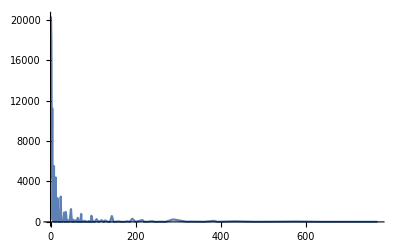

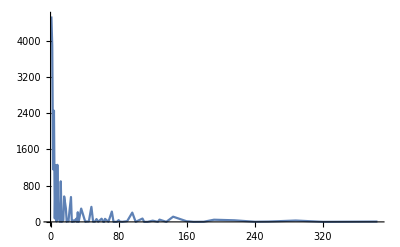

```mathematica
ListPlot[cr15data,Joined->True,PlotRange->All]
ListPlot[cr14data,Joined->True,PlotRange->All]
```

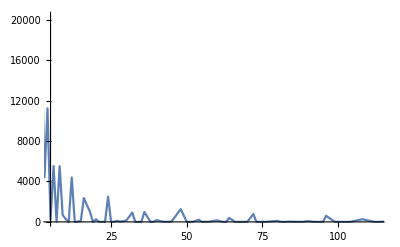

```mathematica
ListPlot[cr15data,Joined->True,PlotRange->{{5,113},All}]
```

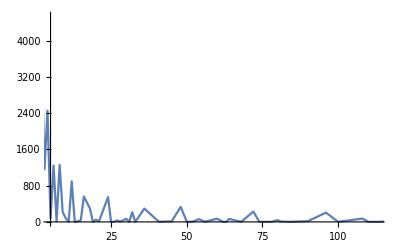

```mathematica
ListPlot[cr14data,Joined->True,PlotRange->{{5,113},All}]
```

```mathematica
Total[Table[cr14data[[i,2]],{i,1,72}]]
```

19536

```mathematica
Total[Table[cr14data[[i,2]] cr14data[[i,1]],{i,1,72}]]
```

251324

```mathematica
Total[Table[cr15data[[i,2]],{i,1,113}]]
```

85263

```mathematica
Total[Table[cr15data[[i,2]] cr15data[[i,1]],{i,1,113}]]
```

1195160

```mathematica
Total[Table[cr13data[[i,2]] cr13data[[i,1]],{i,1,48}]]
```

53471

```mathematica
Total[Table[cr12data[[i,2]] cr12data[[i,1]],{i,1,37}]]
```

11928

```mathematica
Total[Table[cr16data[[i,2]],{i,1,148}]]
```

379799

```mathematica
Total[Table[cr16data[[i,2]] cr16data[[i,1]],{i,1,148}]]
```

5851499

```mathematica
relcross12data=Table[{cr12data[[i,1]],cr12data[[i,2]]/11928.},{i,1,37}]
```

{{1,0.027666},{2,0.0186955},{3,0.00704225},{4,0.0114856},{5,0.000754527},{6,0.00687458},{7,0.000167673},{8,0.00603622},{9,0.00192824},{10,0.0009222},{11,0.0000838364},{12,0.00519785},{13,0.0000838364},{14,0.000251509},{15,0.000503018},{16,0.00243125},{18,0.00285044},{19,0.0000838364},{20,0.000586854},{21,0.0000838364},{24,0.00452716},{27,0.000335345},{30,0.000754527},{32,0.000503018},{33,0.0000838364},{36,0.00259893},{40,0.000251509},{41,0.0000838364},{48,0.0027666},{52,0.0000838364},{54,0.000335345},{60,0.0000838364},{64,0.000586854},{72,0.000838364},{80,0.0000838364},{96,0.000251509},{128,0.0000838364}}

```mathematica
relcross13data=Table[{cr13data[[i,1]],cr13data[[i,2]]/53471.},{i,1,48}]
```

{{1,0.021881},{2,0.0182155},{3,0.00443231},{4,0.0115203},{5,0.00043014},{6,0.00574143},{7,0.000130912},{8,0.0054235},{9,0.000785472},{10,0.00054235},{12,0.00454452},{13,0.0000187017},{14,0.000168316},{15,0.000224421},{16,0.00224421},{18,0.00121561},{20,0.000561052},{22,0.0000561052},{24,0.00308578},{25,0.0000187017},{26,0.0000561052},{27,0.000261824},{28,0.0000374035},{30,0.000299228},{32,0.00138393},{36,0.00147744},{38,0.0000187017},{40,0.000355333},{42,0.0000187017},{44,0.0000187017},{45,0.000187017},{48,0.00157094},{52,0.0000187017},{54,0.00043014},{56,0.0000187017},{57,0.0000374035},{60,0.000261824},{64,0.000448841},{72,0.00138393},{80,0.0000748069},{84,0.0000374035},{90,0.0000187017},{96,0.000766771},{108,0.000243122},{120,0.0000561052},{128,0.0000374035},{144,0.000336631},{192,0.000130912}}

```mathematica
relcross14data=Table[{cr14data[[i,1]],cr14data[[i,2]]/251324.},{i,1,72}]
```

{{1,0.0180484},{2,0.015486},{3,0.00461953},{4,0.00977225},{5,0.000306377},{6,0.00495774},{7,0.0000397893},{8,0.00501345},{9,0.000875364},{10,0.00033423},{11,0.0000119368},{12,0.00356512},{13,3.97893×10^-6},{14,0.0000477471},{15,0.000143241},{16,0.00223616},{18,0.00119766},{19,3.97893×10^-6},{20,0.000198946},{21,0.0000437682},{24,0.00218443},{25,7.95786×10^-6},{26,3.97893×10^-6},{27,0.000131305},{28,0.0000358103},{30,0.000270567},{31,7.95786×10^-6},{32,0.000847512},{33,3.97893×10^-6},{36,0.0011698},{40,0.000198946},{41,3.97893×10^-6},{42,0.0000278525},{45,0.0000437682},{48,0.001321},{50,0.0000159157},{52,0.0000159157},{54,0.000246694},{56,0.0000119368},{60,0.000282504},{62,3.97893×10^-6},{63,3.97893×10^-6},{64,0.000266588},{68,7.95786×10^-6},{72,0.000907195},{74,3.97893×10^-6},{78,7.95786×10^-6},{80,0.000155178},{81,0.0000358103},{84,3.97893×10^-6},{90,0.0000636628},{96,0.00081568},{100,3.97893×10^-6},{108,0.000294441},{110,3.97893×10^-6},{114,3.97893×10^-6},{120,0.000107431},{126,7.95786×10^-6},{128,0.000198946},{136,3.97893×10^-6},{144,0.000457577},{160,0.0000517261},{162,0.0000477471},{168,3.97893×10^-6},{180,0.0000119368},{192,0.000190989},{216,0.000139262},{240,0.0000119368},{256,0.0000278525},{288,0.000119368},{320,3.97893×10^-6},{384,0.0000278525}}

```mathematica
relcross15data=Table[{cr15data[[i,1]],cr15data[[i,2]]/1195160.},{i,1,113}]
```

{{1,0.0170002},{2,0.0148725},{3,0.00369323},{4,0.00939539},{5,0.000189933},{6,0.00462867},{7,0.0000209177},{8,0.00461193},{9,0.000572308},{10,0.000245155},{11,4.18354×10^-6},{12,0.00367315},{13,1.67342×10^-6},{14,0.0000242645},{15,0.0000677734},{16,0.00197296},{18,0.000851769},{19,1.67342×10^-6},{20,0.000217544},{21,8.36708×10^-6},{22,8.36708×10^-6},{23,1.67342×10^-6},{24,0.00208591},{25,3.34683×10^-6},{26,7.53037×10^-6},{27,0.0000937113},{28,0.0000225911},{30,0.000108772},{32,0.000772282},{33,1.67342×10^-6},{35,1.67342×10^-6},{36,0.000816627},{38,2.51012×10^-6},{39,8.36708×10^-7},{40,0.000151444},{42,0.0000192443},{44,4.18354×10^-6},{45,0.0000409987},{48,0.00105509},{50,6.69366×10^-6},{52,4.18354×10^-6},{54,0.000181566},{55,8.36708×10^-7},{56,0.0000108772},{57,4.18354×10^-6},{60,0.00012969},{62,8.36708×10^-7},{63,6.69366×10^-6},{64,0.000327153},{66,8.36708×10^-7},{69,8.36708×10^-7},{70,8.36708×10^-7},{72,0.000653469},{73,8.36708×10^-7},{74,8.36708×10^-7},{75,8.36708×10^-6},{76,1.67342×10^-6},{80,0.0000895278},{81,0.0000100405},{82,8.36708×10^-7},{84,0.0000234278},{88,8.36708×10^-7},{90,0.0000669366},{92,2.51012×10^-6},{93,8.36708×10^-7},{95,8.36708×10^-7},{96,0.000505372},{99,8.36708×10^-7},{100,7.53037×10^-6},{104,8.36708×10^-7},{108,0.000220054},{112,5.02025×10^-6},{114,2.51012×10^-6},{120,0.00013722},{124,1.67342×10^-6},{126,4.18354×10^-6},{128,0.000121323},{135,8.36708×10^-7},{138,2.51012×10^-6},{140,2.51012×10^-6},{144,0.000482781},{148,8.36708×10^-7},{150,1.67342×10^-6},{160,0.0000393253},{162,0.0000326316},{164,8.36708×10^-7},{168,6.69366×10^-6},{174,8.36708×10^-7},{180,0.0000468557},{186,1.67342×10^-6},{192,0.000256869},{200,1.67342×10^-6},{216,0.000151444},{220,8.36708×10^-7},{222,2.51012×10^-6},{224,8.36708×10^-7},{240,0.0000568961},{243,3.34683×10^-6},{252,1.67342×10^-6},{256,0.0000167342},{270,8.36708×10^-7},{288,0.000204993},{320,9.20379×10^-6},{324,0.0000234278},{360,7.53037×10^-6},{384,0.0000836708},{392,8.36708×10^-7},{432,0.0000476924},{480,7.53037×10^-6},{512,0.0000100405},{576,0.0000292848},{640,2.51012×10^-6},{768,5.02025×10^-6}}

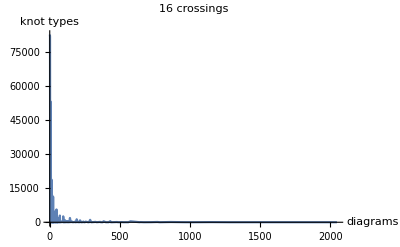

```mathematica
ListPlot[cr16data,PlotRange->All, Joined->True,AxesLabel->{"diagrams", "knot types"},PlotLabel->"16 crossings"]
```

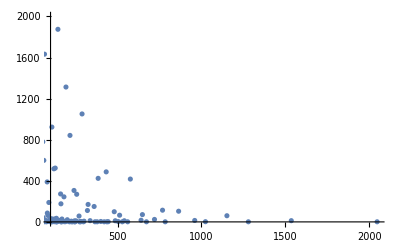

```mathematica
ListPlot[cr16data,PlotRange->{{100,2050},{0,2000}}]
```

```mathematica
relcross16data=Table[{cr16data[[i,1]],cr16data[[i,2]]/5851499.},{i,1,148}]
```

{{1,0.0141056},{2,0.0139293},{3,0.00342886},{4,0.00909271},{5,0.000176536},{6,0.00417278},{7,0.0000160643},{8,0.00460258},{9,0.000603093},{10,0.000201316},{11,1.70896×10^-6},{12,0.00320858},{13,5.12689×10^-7},{14,0.0000138426},{15,0.0000652824},{16,0.00205828},{17,1.70896×10^-7},{18,0.000844399},{19,1.19627×10^-6},{20,0.000153294},{21,9.3993×10^-6},{22,1.70896×10^-7},{23,1.70896×10^-7},{24,0.001919},{25,2.56345×10^-6},{26,1.19627×10^-6},{27,0.0000789541},{28,7.51944×10^-6},{30,0.000103221},{31,3.41793×10^-7},{32,0.000793985},{33,1.19627×10^-6},{35,1.02538×10^-6},{36,0.000725968},{40,0.00010288},{41,5.12689×10^-7},{42,0.0000107665},{43,3.41793×10^-7},{45,0.0000162352},{46,3.41793×10^-7},{48,0.000960779},{50,4.7851×10^-6},{51,1.70896×10^-7},{52,1.36717×10^-6},{54,0.000133299},{55,5.12689×10^-7},{56,7.17765×10^-6},{57,1.70896×10^-7},{60,0.000102367},{62,3.41793×10^-7},{63,2.90524×10^-6},{64,0.000279074},{68,6.83586×10^-7},{69,5.12689×10^-7},{70,1.19627×10^-6},{72,0.000502777},{74,6.83586×10^-7},{75,1.70896×10^-6},{76,1.70896×10^-7},{78,1.87986×10^-6},{80,0.0000664787},{81,0.0000146971},{84,0.0000107665},{90,0.0000322994},{95,5.12689×10^-7},{96,0.000442109},{100,5.46868×10^-6},{102,1.70896×10^-7},{105,3.41793×10^-7},{108,0.000157737},{110,1.70896×10^-7},{112,4.7851×10^-6},{113,6.83586×10^-7},{114,8.54482×10^-7},{120,0.0000883534},{122,3.41793×10^-7},{126,4.7851×10^-6},{128,0.0000895497},{132,1.70896×10^-7},{135,5.98137×10^-6},{136,3.41793×10^-7},{138,1.70896×10^-7},{140,5.12689×10^-7},{144,0.000320431},{150,2.56345×10^-6},{160,0.0000464838},{162,0.0000300778},{163,1.70896×10^-7},{165,1.70896×10^-7},{168,4.7851×10^-6},{171,5.12689×10^-7},{180,0.0000416987},{182,3.41793×10^-7},{189,3.41793×10^-7},{192,0.000224387},{200,3.58882×10^-6},{210,6.83586×10^-7},{213,1.70896×10^-7},{216,0.000143895},{224,1.19627×10^-6},{225,1.70896×10^-7},{232,1.70896×10^-7},{240,0.0000522943},{243,1.70896×10^-6},{244,1.70896×10^-7},{246,1.70896×10^-7},{252,1.70896×10^-6},{256,0.0000459711},{270,9.74109×10^-6},{273,1.70896×10^-7},{279,1.70896×10^-7},{280,6.83586×10^-7},{288,0.000179612},{296,1.70896×10^-7},{300,1.19627×10^-6},{320,0.0000189695},{324,0.0000290524},{336,2.05076×10^-6},{360,0.0000256345},{365,1.70896×10^-7},{378,1.70896×10^-7},{384,0.0000724601},{400,6.83586×10^-7},{420,1.70896×10^-7},{432,0.0000832265},{436,1.70896×10^-7},{444,3.41793×10^-7},{480,0.0000169187},{486,1.87986×10^-6},{504,5.12689×10^-7},{512,0.0000111083},{528,1.70896×10^-7},{540,1.87986×10^-6},{560,1.70896×10^-7},{576,0.0000712638},{640,2.73434×10^-6},{648,0.0000121336},{672,1.70896×10^-7},{720,4.10151×10^-6},{768,0.0000194822},{784,1.70896×10^-7},{864,0.0000177732},{960,2.39255×10^-6},{1024,3.41793×10^-7},{1152,0.0000102538},{1280,1.70896×10^-7},{1536,2.05076×10^-6},{2048,1.70896×10^-7}}

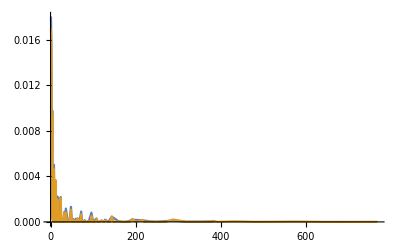

```mathematica
ListPlot[{relcross14data,relcross15data},Joined->True,PlotRange->All]
```

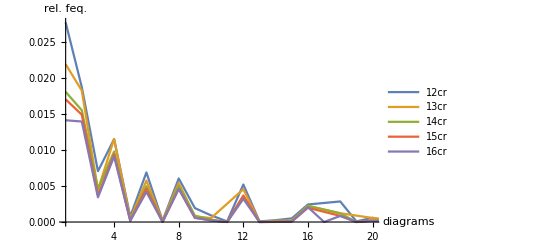

```mathematica
ListPlot[{relcross12data,relcross13data,relcross14data,relcross15data,relcross16data},Joined->True,PlotRange->{{1,20},All},AxesLabel->{"diagrams","rel. feq."},PlotLegends->{"12cr","13cr","14cr","15cr","16cr"}]
```

```mathematica
sorted16cr=Reverse[Sort[Table[{relcross16data[[i,2]],relcross16data[[i,1]]},{i,1,148}]]];
sorted15cr=Reverse[Sort[Table[{relcross15data[[i,2]],relcross15data[[i,1]]},{i,1,113}]]];
sorted14cr=Reverse[Sort[Table[{relcross14data[[i,2]],relcross14data[[i,1]]},{i,1,72}]]];
sorted13cr=Reverse[Sort[Table[{relcross13data[[i,2]],relcross13data[[i,1]]},{i,1,48}]]];
sorted12cr=Reverse[Sort[Table[{relcross12data[[i,2]],relcross12data[[i,1]]},{i,1,37}]]];
```

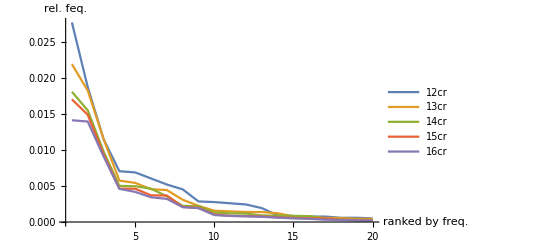

```mathematica
ListPlot[{Table[sorted12cr[[i,1]],{i,1,20}],Table[sorted13cr[[i,1]],{i,1,20}],Table[sorted14cr[[i,1]],{i,1,20}],Table[sorted15cr[[i,1]],{i,1,20}],Table[sorted16cr[[i,1]],{i,1,20}]},Joined->True,PlotRange->All,AxesLabel->{"ranked by freq.","rel. feq."},PlotLegends->{"12cr","13cr","14cr","15cr","16cr"}]
```

```mathematica
TableForm[{Table[sorted12cr[[i,2]],{i,1,20}],Table[sorted13cr[[i,2]],{i,1,20}],Table[sorted14cr[[i,2]],{i,1,20}],Table[sorted15cr[[i,2]],{i,1,20}],Table[sorted16cr[[i,2]],{i,1,20}]}]
```

1 | 2 | 4 | 3 | 6 | 8 | 12 | 24 | 18 | 48 | 36 | 16 | 9 | 10 | 72 | 30 | 5 | 64 | 20 | 32
1 | 2 | 4 | 6 | 8 | 12 | 3 | 24 | 16 | 48 | 36 | 72 | 32 | 18 | 9 | 96 | 20 | 10 | 64 | 54
1 | 2 | 4 | 8 | 6 | 3 | 12 | 16 | 24 | 48 | 18 | 36 | 72 | 9 | 32 | 96 | 144 | 10 | 5 | 108
1 | 2 | 4 | 6 | 8 | 3 | 12 | 24 | 16 | 48 | 18 | 36 | 32 | 72 | 9 | 96 | 144 | 64 | 192 | 10
1 | 2 | 4 | 8 | 6 | 3 | 12 | 16 | 24 | 48 | 18 | 32 | 36 | 9 | 72 | 96 | 144 | 64 | 192 | 10

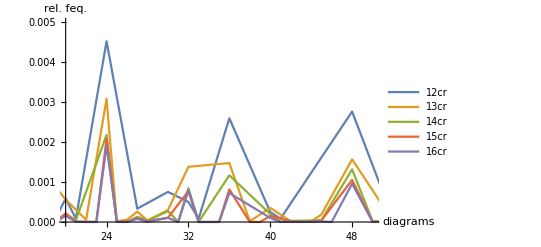

```mathematica
ListPlot[{relcross12data,relcross13data,relcross14data,relcross15data,relcross16data},Joined->True,PlotRange->{{20,50},{0,.005}},AxesLabel->{"diagrams","rel. feq."},PlotLegends->{"12cr","13cr","14cr","15cr","16cr"}]
```

```mathematica
occurringcross15=Table[cr15data[[i,1]],{i,1,Length[cr15data]}]
```

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,18,19,20,21,22,23,24,25,26,27,28,30,32,33,35,36,38,39,40,42,44,45,48,50,52,54,55,56,57,60,62,63,64,66,69,70,72,73,74,75,76,80,81,82,84,88,90,92,93,95,96,99,100,104,108,112,114,120,124,126,128,135,138,140,144,148,150,160,162,164,168,174,180,186,192,200,216,220,222,224,240,243,252,256,270,288,320,324,360,384,392,432,480,512,576,640,768}

```mathematica
Complement[Table[Prime[i],{i,1,136}],occurringcross15]
```

{17,29,31,37,41,43,47,53,59,61,67,71,79,83,89,97,101,103,107,109,113,127,131,137,139,149,151,157,163,167,173,179,181,191,193,197,199,211,223,227,229,233,239,241,251,257,263,269,271,277,281,283,293,307,311,313,317,331,337,347,349,353,359,367,373,379,383,389,397,401,409,419,421,431,433,439,443,449,457,461,463,467,479,487,491,499,503,509,521,523,541,547,557,563,569,571,577,587,593,599,601,607,613,617,619,631,641,643,647,653,659,661,673,677,683,691,701,709,719,727,733,739,743,751,757,761,769}

This shows that most of the primes do not show up

```mathematica
Intersection[Table[Prime[i],{i,1,136}],occurringcross15]
Length[%]
```

{2,3,5,7,11,13,19,23,73}

9

```mathematica
occurringcross16=Table[cr16data[[i,1]],{i,1,Length[cr16data]}]
```

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,30,31,32,33,35,36,40,41,42,43,45,46,48,50,51,52,54,55,56,57,60,62,63,64,68,69,70,72,74,75,76,78,80,81,84,90,95,96,100,102,105,108,110,112,113,114,120,122,126,128,132,135,136,138,140,144,150,160,162,163,165,168,171,180,182,189,192,200,210,213,216,224,225,232,240,243,244,246,252,256,270,273,279,280,288,296,300,320,324,336,360,365,378,384,400,420,432,436,444,480,486,504,512,528,540,560,576,640,648,672,720,768,784,864,960,1024,1152,1280,1536,2048}

```mathematica
Complement[Table[Prime[i],{i,1,310}],occurringcross16]
```

{2,3,5,7,11,13,17,19,23,29,31,37,41,43,47,53,59,61,67,71,73,79,83,89,97,101,103,107,109,113,127,131,137,139,149,151,157,163,167,173,179,181,191,193,197,199,211,223,227,229,233,239,241,251,257,263,269,271,277,281,283,293,307,311,313,317,331,337,347,349,353,359,367,373,379,383,389,397,401,409,419,421,431,433,439,443,449,457,461,463,467,479,487,491,499,503,509,521,523,541,547,557,563,569,571,577,587,593,599,601,607,613,617,619,631,641,643,647,653,659,661,673,677,683,691,701,709,719,727,733,739,743,751,757,761,769,773,787,797,809,811,821,823,827,829,839,853,857,859,863,877,881,883,887,907,911,919,929,937,941,947,953,967,971,977,983,991,997,1009,1013,1019,1021,1031,1033,1039,1049,1051,1061,1063,1069,1087,1091,1093,1097,1103,1109,1117,1123,1129,1151,1153,1163,1171,1181,1187,1193,1201,1213,1217,1223,1229,1231,1237,1249,1259,1277,1279,1283,1289,1291,1297,1301,1303,1307,1319,1321,1327,1361,1367,1373,1381,1399,1409,1423,1427,1429,1433,1439,1447,1451,1453,1459,1471,1481,1483,1487,1489,1493,1499,1511,1523,1531,1543,1549,1553,1559,1567,1571,1579,1583,1597,1601,1607,1609,1613,1619,1621,1627,1637,1657,1663,1667,1669,1693,1697,1699,1709,1721,1723,1733,1741,1747,1753,1759,1777,1783,1787,1789,1801,1811,1823,1831,1847,1861,1867,1871,1873,1877,1879,1889,1901,1907,1913,1931,1933,1949,1951,1973,1979,1987,1993,1997,1999,2003,2011,2017,2027,2029,2039,2053}

```mathematica
Intersection[Table[Prime[i],{i,1,310}],occurringcross16]
Length[%]
```

{2,3,5,7,11,13,17,19,23,31,41,43,113,163}

14

Only 9 primes do show out of 113 different numbers for 15 cr
Only 14 primes do show out of 148 different numbers for 16 cr

```mathematica
Length[ occurringcross15]
```

113

only 9 out of 113 values are prime

```mathematica
Intersection[Table[2^i,{i,1,9}],occurringcross15]
```

{2,4,8,16,32,64,128,256,512}

```mathematica
Intersection[Table[2^i,{i,1,20}],occurringcross16]
```

{2,4,8,16,32,64,128,256,512,1024,2048}

all powers of two are appearing.

```mathematica
Intersection[Table[3 2^i,{i,1,8}],occurringcross15]
```

{6,12,24,48,96,192,384,768}

```mathematica
Intersection[Table[3 2^i,{i,1,18}],occurringcross16]
```

{6,12,24,48,96,192,384,768,1536}

all powers of two times three are appearing.

```mathematica
Complement[Range[768],occurringcross15]
```

{17,29,31,34,37,41,43,46,47,49,51,53,58,59,61,65,67,68,71,77,78,79,83,85,86,87,89,91,94,97,98,101,102,103,105,106,107,109,110,111,113,115,116,117,118,119,121,122,123,125,127,129,130,131,132,133,134,136,137,139,141,142,143,145,146,147,149,151,152,153,154,155,156,157,158,159,161,163,165,166,167,169,170,171,172,173,175,176,177,178,179,181,182,183,184,185,187,188,189,190,191,193,194,195,196,197,198,199,201,202,203,204,205,206,207,208,209,210,211,212,213,214,215,217,218,219,221,223,225,226,227,228,229,230,231,232,233,234,235,236,237,238,239,241,242,244,245,246,247,248,249,250,251,253,254,255,257,258,259,260,261,262,263,264,265,266,267,268,269,271,272,273,274,275,276,277,278,279,280,281,282,283,284,285,286,287,289,290,291,292,293,294,295,296,297,298,299,300,301,302,303,304,305,306,307,308,309,310,311,312,313,314,315,316,317,318,319,321,322,323,325,326,327,328,329,330,331,332,333,334,335,336,337,338,339,340,341,342,343,344,345,346,347,348,349,350,351,352,353,354,355,356,357,358,359,361,362,363,364,365,366,367,368,369,370,371,372,373,374,375,376,377,378,379,380,381,382,383,385,386,387,388,389,390,391,393,394,395,396,397,398,399,400,401,402,403,404,405,406,407,408,409,410,411,412,413,414,415,416,417,418,419,420,421,422,423,424,425,426,427,428,429,430,431,433,434,435,436,437,438,439,440,441,442,443,444,445,446,447,448,449,450,451,452,453,454,455,456,457,458,459,460,461,462,463,464,465,466,467,468,469,470,471,472,473,474,475,476,477,478,479,481,482,483,484,485,486,487,488,489,490,491,492,493,494,495,496,497,498,499,500,501,502,503,504,505,506,507,508,509,510,511,513,514,515,516,517,518,519,520,521,522,523,524,525,526,527,528,529,530,531,532,533,534,535,536,537,538,539,540,541,542,543,544,545,546,547,548,549,550,551,552,553,554,555,556,557,558,559,560,561,562,563,564,565,566,567,568,569,570,571,572,573,574,575,577,578,579,580,581,582,583,584,585,586,587,588,589,590,591,592,593,594,595,596,597,598,599,600,601,602,603,604,605,606,607,608,609,610,611,612,613,614,615,616,617,618,619,620,621,622,623,624,625,626,627,628,629,630,631,632,633,634,635,636,637,638,639,641,642,643,644,645,646,647,648,649,650,651,652,653,654,655,656,657,658,659,660,661,662,663,664,665,666,667,668,669,670,671,672,673,674,675,676,677,678,679,680,681,682,683,684,685,686,687,688,689,690,691,692,693,694,695,696,697,698,699,700,701,702,703,704,705,706,707,708,709,710,711,712,713,714,715,716,717,718,719,720,721,722,723,724,725,726,727,728,729,730,731,732,733,734,735,736,737,738,739,740,741,742,743,744,745,746,747,748,749,750,751,752,753,754,755,756,757,758,759,760,761,762,763,764,765,766,767}

```mathematica
PrimeQ@Complement[Range[768],occurringcross15]
```

{True,True,True,False,True,True,True,False,True,False,False,True,False,True,True,False,True,False,True,False,False,True,True,False,False,False,True,False,False,True,False,True,False,True,False,False,True,True,False,False,True,False,False,False,False,False,False,False,False,False,True,False,False,True,False,False,False,False,True,True,False,False,False,False,False,False,True,True,False,False,False,False,False,True,False,False,False,True,False,False,True,False,False,False,False,True,False,False,False,False,True,True,False,False,False,False,False,False,False,False,True,True,False,False,False,True,False,True,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,True,False,False,True,False,True,False,False,False,True,False,False,False,False,False,True,True,False,False,False,False,False,False,False,False,True,False,False,False,True,False,False,False,False,False,True,False,False,False,False,False,True,True,False,False,False,False,False,True,False,False,False,True,False,True,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,True,False,True,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,True,False,True,False,False,False,True,False,False,False,False,False,True,False,False,False,False,False,False,True,False,False,False,False,False,True,False,False,False,False,False,True,False,False,False,True,False,False,False,False,True,False,False,False,False,False,False,True,False,False,False,True,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,True,False,True,False,False,False,False,False,False,False,False,False,True,True,False,False,False,False,False,True,False,False,False,True,False,False,False,False,False,True,False,False,False,False,False,False,False,True,False,False,False,True,False,True,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,True,False,False,False,True,False,False,False,False,False,False,False,True,False,False,False,True,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,True,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,True,False,False,False,False,False,True,False,True,False,False,False,False,True,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,True,False,False,False,False,False,True,False,True,False,False,False,False,False,True,False,False,False,False,False,True,False,False,False,True,False,True,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,True,False,True,False,False,False,True,False,False,False,False,False,True,False,False,False,False,False,True,False,True,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,True,False,False,False,False,False,True,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,True,False,False,False,False,False,True,False,False,False,False,False,True,False,False,False,True,False,False,False,False,False,False,False,True,False,False,False,False,False,True,False,False,False,True,False,False,False,False,False,False}

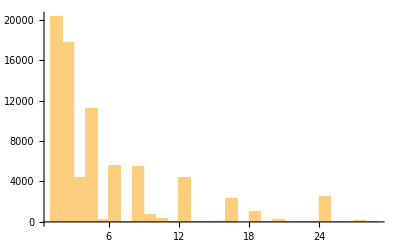

```mathematica
Histogram[countFor15]
```

```mathematica
?Histogram
```

```mathematica
Max[countFor15]
```

768

```mathematica
3*2^8
```

768

```mathematica
Total[countFor15]
```

1195160

```mathematica
Total[countFor15]/85263.
```

14.0173

```mathematica
relcross16data2=Table[{cr16data[[i,1]],cr16data[[i,2]]/379799.},{i,1,148}];
relcross15data2=Table[{cr15data[[i,1]],cr15data[[i,2]]/85263.},{i,1,113}];
relcross14data2=Table[{cr14data[[i,1]],cr14data[[i,2]]/19536.},{i,1,72}];
relcross13data2=Table[{cr13data[[i,1]],cr13data[[i,2]]/4878.},{i,1,48}];
relcross12data2=Table[{cr12data[[i,1]],cr12data[[i,2]]/1288.},{i,1,37}];
relcross11data2=Table[{cr11data[[i,1]],cr11data[[i,2]]/367.},{i,1,23}];
```

```mathematica
TableForm[{relcross11data2,relcross12data2,relcross13data2,relcross14data2,relcross15data2,relcross16data2}]
```

1
0.228883 | 2
0.177112 | 3
0.0626703 | 4
0.114441 | 5
0.013624 | 6
0.0762943 | 7
0.00544959 | 8
0.0544959 | 9
0.0108992 | 10
0.0190736 | 12
0.0735695 | 14
0.0027248 | 15
0.00544959 | 16
0.0463215 | 18
0.0217984 | 20
0.00817439 | 22
0.0027248 | 24
0.0326975 | 26
0.0027248 | 27
0.00544959 | 32
0.0108992 | 36
0.0163488 | 48
0.00817439 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
1
0.256211 | 2
0.173137 | 3
0.0652174 | 4
0.106366 | 5
0.00698758 | 6
0.0636646 | 7
0.0015528 | 8
0.0559006 | 9
0.0178571 | 10
0.00854037 | 11
0.000776398 | 12
0.0481366 | 13
0.000776398 | 14
0.00232919 | 15
0.00465839 | 16
0.0225155 | 18
0.0263975 | 19
0.000776398 | 20
0.00543478 | 21
0.000776398 | 24
0.0419255 | 27
0.00310559 | 30
0.00698758 | 32
0.00465839 | 33
0.000776398 | 36
0.0240683 | 40
0.00232919 | 41
0.000776398 | 48
0.0256211 | 52
0.000776398 | 54
0.00310559 | 60
0.000776398 | 64
0.00543478 | 72
0.00776398 | 80
0.000776398 | 96
0.00232919 | 128
0.000776398 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
1
0.239852 | 2
0.199672 | 3
0.0485855 | 4
0.126281 | 5
0.00471505 | 6
0.0629356 | 7
0.00143501 | 8
0.0594506 | 9
0.00861009 | 10
0.00594506 | 12
0.0498155 | 13
0.000205002 | 14
0.00184502 | 15
0.00246002 | 16
0.0246002 | 18
0.0133251 | 20
0.00615006 | 22
0.000615006 | 24
0.0338253 | 25
0.000205002 | 26
0.000615006 | 27
0.00287003 | 28
0.000410004 | 30
0.00328003 | 32
0.0151702 | 36
0.0161952 | 38
0.000205002 | 40
0.00389504 | 42
0.000205002 | 44
0.000205002 | 45
0.00205002 | 48
0.0172202 | 52
0.000205002 | 54
0.00471505 | 56
0.000205002 | 57
0.000410004 | 60
0.00287003 | 64
0.00492005 | 72
0.0151702 | 80
0.000820008 | 84
0.000410004 | 90
0.000205002 | 96
0.00840508 | 108
0.00266503 | 120
0.000615006 | 128
0.000410004 | 144
0.00369004 | 192
0.00143501 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
1
0.232187 | 2
0.199222 | 3
0.0594287 | 4
0.125717 | 5
0.00394144 | 6
0.0637797 | 7
0.000511876 | 8
0.0644963 | 9
0.0112613 | 10
0.00429975 | 11
0.000153563 | 12
0.045864 | 13
0.0000511876 | 14
0.000614251 | 15
0.00184275 | 16
0.0287674 | 18
0.0154075 | 19
0.0000511876 | 20
0.00255938 | 21
0.000563063 | 24
0.028102 | 25
0.000102375 | 26
0.0000511876 | 27
0.00168919 | 28
0.000460688 | 30
0.00348075 | 31
0.000102375 | 32
0.0109029 | 33
0.0000511876 | 36
0.0150491 | 40
0.00255938 | 41
0.0000511876 | 42
0.000358313 | 45
0.000563063 | 48
0.0169943 | 50
0.00020475 | 52
0.00020475 | 54
0.00317363 | 56
0.000153563 | 60
0.00363432 | 62
0.0000511876 | 63
0.0000511876 | 64
0.00342957 | 68
0.000102375 | 72
0.0116708 | 74
0.0000511876 | 78
0.000102375 | 80
0.00199631 | 81
0.000460688 | 84
0.0000511876 | 90
0.000819001 | 96
0.0104934 | 100
0.0000511876 | 108
0.00378788 | 110
0.0000511876 | 114
0.0000511876 | 120
0.00138206 | 126
0.000102375 | 128
0.00255938 | 136
0.0000511876 | 144
0.00588657 | 160
0.000665438 | 162
0.000614251 | 168
0.0000511876 | 180
0.000153563 | 192
0.002457 | 216
0.00179156 | 240
0.000153563 | 256
0.000358313 | 288
0.00153563 | 320
0.0000511876 | 384
0.000358313 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
1
0.238298 | 2
0.208473 | 3
0.0517692 | 4
0.131698 | 5
0.00266235 | 6
0.0648816 | 7
0.00029321 | 8
0.064647 | 9
0.00802224 | 10
0.00343643 | 11
0.0000586421 | 12
0.0514877 | 13
0.0000234568 | 14
0.000340124 | 15
0.000950002 | 16
0.0276556 | 18
0.0119395 | 19
0.0000234568 | 20
0.00304939 | 21
0.000117284 | 22
0.000117284 | 23
0.0000234568 | 24
0.0292389 | 25
0.0000469137 | 26
0.000105556 | 27
0.00131358 | 28
0.000316667 | 30
0.00152469 | 32
0.0108253 | 33
0.0000234568 | 35
0.0000234568 | 36
0.0114469 | 38
0.0000351853 | 39
0.0000117284 | 40
0.00212284 | 42
0.000269754 | 44
0.0000586421 | 45
0.000574692 | 48
0.0147895 | 50
0.0000938273 | 52
0.0000586421 | 54
0.00254507 | 55
0.0000117284 | 56
0.000152469 | 57
0.0000586421 | 60
0.0018179 | 62
0.0000117284 | 63
0.0000938273 | 64
0.00458581 | 66
0.0000117284 | 69
0.0000117284 | 70
0.0000117284 | 72
0.00915989 | 73
0.0000117284 | 74
0.0000117284 | 75
0.000117284 | 76
0.0000234568 | 80
0.00125494 | 81
0.000140741 | 82
0.0000117284 | 84
0.000328396 | 88
0.0000117284 | 90
0.000938273 | 92
0.0000351853 | 93
0.0000117284 | 95
0.0000117284 | 96
0.00708396 | 99
0.0000117284 | 100
0.000105556 | 104
0.0000117284 | 108
0.00308457 | 112
0.0000703705 | 114
0.0000351853 | 120
0.00192346 | 124
0.0000234568 | 126
0.0000586421 | 128
0.00170062 | 135
0.0000117284 | 138
0.0000351853 | 140
0.0000351853 | 144
0.0067673 | 148
0.0000117284 | 150
0.0000234568 | 160
0.000551236 | 162
0.000457408 | 164
0.0000117284 | 168
0.0000938273 | 174
0.0000117284 | 180
0.000656791 | 186
0.0000234568 | 192
0.00360062 | 200
0.0000234568 | 216
0.00212284 | 220
0.0000117284 | 222
0.0000351853 | 224
0.0000117284 | 240
0.000797532 | 243
0.0000469137 | 252
0.0000234568 | 256
0.000234568 | 270
0.0000117284 | 288
0.00287346 | 320
0.000129013 | 324
0.000328396 | 360
0.000105556 | 384
0.00117284 | 392
0.0000117284 | 432
0.00066852 | 480
0.000105556 | 512
0.000140741 | 576
0.000410495 | 640
0.0000351853 | 768
0.0000703705 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
1
0.217323 | 2
0.214606 | 3
0.0528279 | 4
0.14009 | 5
0.00271986 | 6
0.0642893 | 7
0.000247499 | 8
0.0709112 | 9
0.00929176 | 10
0.00310164 | 11
0.0000263297 | 12
0.049434 | 13
7.89891×10^-6 | 14
0.000213271 | 15
0.0010058 | 16
0.0317115 | 17
2.63297×10^-6 | 18
0.0130095 | 19
0.0000184308 | 20
0.00236178 | 21
0.000144813 | 22
2.63297×10^-6 | 23
2.63297×10^-6 | 24
0.0295656 | 25
0.0000394946 | 26
0.0000184308 | 27
0.00121643 | 28
0.000115851 | 30
0.00159031 | 31
5.26594×10^-6 | 32
0.0122328 | 33
0.0000184308 | 35
0.0000157978 | 36
0.0111849 | 40
0.00158505 | 41
7.89891×10^-6 | 42
0.000165877 | 43
5.26594×10^-6 | 45
0.000250132 | 46
5.26594×10^-6 | 48
0.0148026 | 50
0.0000737232 | 51
2.63297×10^-6 | 52
0.0000210638 | 54
0.00205372 | 55
7.89891×10^-6 | 56
0.000110585 | 57
2.63297×10^-6 | 60
0.00157715 | 62
5.26594×10^-6 | 63
0.0000447605 | 64
0.00429964 | 68
0.0000105319 | 69
7.89891×10^-6 | 70
0.0000184308 | 72
0.0077462 | 74
0.0000105319 | 75
0.0000263297 | 76
2.63297×10^-6 | 78
0.0000289627 | 80
0.00102423 | 81
0.000226436 | 84
0.000165877 | 90
0.000497632 | 95
7.89891×10^-6 | 96
0.0068115 | 100
0.0000842551 | 102
2.63297×10^-6 | 105
5.26594×10^-6 | 108
0.00243023 | 110
2.63297×10^-6 | 112
0.0000737232 | 113
0.0000105319 | 114
0.0000131649 | 120
0.00136125 | 122
5.26594×10^-6 | 126
0.0000737232 | 128
0.00137968 | 132
2.63297×10^-6 | 135
0.000092154 | 136
5.26594×10^-6 | 138
2.63297×10^-6 | 140
7.89891×10^-6 | 144
0.00493682 | 150
0.0000394946 | 160
0.000716168 | 162
0.000463403 | 163
2.63297×10^-6 | 165
2.63297×10^-6 | 168
0.0000737232 | 171
7.89891×10^-6 | 180
0.000642445 | 182
5.26594×10^-6 | 189
5.26594×10^-6 | 192
0.00345709 | 200
0.0000552924 | 210
0.0000105319 | 213
2.63297×10^-6 | 216
0.00221696 | 224
0.0000184308 | 225
2.63297×10^-6 | 232
2.63297×10^-6 | 240
0.000805689 | 243
0.0000263297 | 244
2.63297×10^-6 | 246
2.63297×10^-6 | 252
0.0000263297 | 256
0.000708269 | 270
0.000150079 | 273
2.63297×10^-6 | 279
2.63297×10^-6 | 280
0.0000105319 | 288
0.00276725 | 296
2.63297×10^-6 | 300
0.0000184308 | 320
0.00029226 | 324
0.000447605 | 336
0.0000315957 | 360
0.000394946 | 365
2.63297×10^-6 | 378
2.63297×10^-6 | 384
0.00111638 | 400
0.0000105319 | 420
2.63297×10^-6 | 432
0.00128226 | 436
2.63297×10^-6 | 444
5.26594×10^-6 | 480
0.000260664 | 486
0.0000289627 | 504
7.89891×10^-6 | 512
0.000171143 | 528
2.63297×10^-6 | 540
0.0000289627 | 560
2.63297×10^-6 | 576
0.00109795 | 640
0.0000421275 | 648
0.000186941 | 672
2.63297×10^-6 | 720
0.0000631913 | 768
0.000300159 | 784
2.63297×10^-6 | 864
0.000273829 | 960
0.0000368616 | 1024
5.26594×10^-6 | 1152
0.000157978 | 1280
2.63297×10^-6 | 1536
0.0000315957 | 2048
2.63297×10^-6

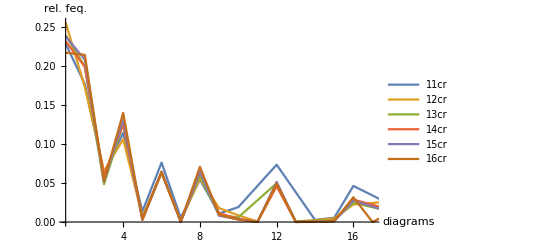

```mathematica
ListPlot[{relcross11data2,relcross12data2,relcross13data2,relcross14data2,relcross15data2,relcross16data2},Joined->True,PlotRange->{{1,17},All},AxesLabel->{"diagrams","rel. feq."},PlotLegends->{"11cr","12cr","13cr","14cr","15cr","16cr"}]
```

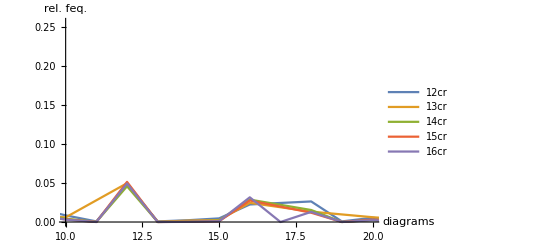

```mathematica
ListPlot[{relcross12data2,relcross13data2,relcross14data2,relcross15data2,relcross16data2},Joined->True,PlotRange->{{10,20},All},AxesLabel->{"diagrams","rel. feq."},PlotLegends->{"12cr","13cr","14cr","15cr","16cr"}]
```

```mathematica
Length[cr10data]
```

14

```mathematica
Total[Table[cr14data[[i,2]],{i,1,72}]]
Total[Table[cr13data[[i,2]],{i,1,48}]]
Total[Table[cr12data[[i,2]],{i,1,37}]]
Total[Table[cr11data[[i,2]],{i,1,23}]]
```

19536

4878

1288

367

```mathematica
cr16data
```

{{1,82539},{2,81507},{3,20064},{4,53206},{5,1033},{6,24417},{7,94},{8,26932},{9,3529},{10,1178},{11,10},{12,18775},{13,3},{14,81},{15,382},{16,12044},{17,1},{18,4941},{19,7},{20,897},{21,55},{22,1},{23,1},{24,11229},{25,15},{26,7},{27,462},{28,44},{30,604},{31,2},{32,4646},{33,7},{35,6},{36,4248},{40,602},{41,3},{42,63},{43,2},{45,95},{46,2},{48,5622},{50,28},{51,1},{52,8},{54,780},{55,3},{56,42},{57,1},{60,599},{62,2},{63,17},{64,1633},{68,4},{69,3},{70,7},{72,2942},{74,4},{75,10},{76,1},{78,11},{80,389},{81,86},{84,63},{90,189},{95,3},{96,2587},{100,32},{102,1},{105,2},{108,923},{110,1},{112,28},{113,4},{114,5},{120,517},{122,2},{126,28},{128,524},{132,1},{135,35},{136,2},{138,1},{140,3},{144,1875},{150,15},{160,272},{162,176},{163,1},{165,1},{168,28},{171,3},{180,244},{182,2},{189,2},{192,1313},{200,21},{210,4},{213,1},{216,842},{224,7},{225,1},{232,1},{240,306},{243,10},{244,1},{246,1},{252,10},{256,269},{270,57},{273,1},{279,1},{280,4},{288,1051},{296,1},{300,7},{320,111},{324,170},{336,12},{360,150},{365,1},{378,1},{384,424},{400,4},{420,1},{432,487},{436,1},{444,2},{480,99},{486,11},{504,3},{512,65},{528,1},{540,11},{560,1},{576,417},{640,16},{648,71},{672,1},{720,24},{768,114},{784,1},{864,104},{960,14},{1024,2},{1152,60},{1280,1},{1536,12},{2048,1}}

```mathematica
?Select
```

```mathematica
cr16data[[1,2]]/379799.
cr15data[[1,2]]/85263.
cr14data[[1,2]]/19536.
```

0.217323

0.238298

0.232187

```mathematica
Total[Select[cr16data,EvenQ[#[[1]]]&&Mod[#[[1]],4]==2&]][[2]]/379799.
Total[Select[cr15data,EvenQ[#[[1]]]&&Mod[#[[1]],4]==2&]][[2]]/85263.
Total[Select[cr14data,EvenQ[#[[1]]]&&Mod[#[[1]],4]==2&]][[2]]/19536.
```

0.300493

0.295451

0.292434

```mathematica
Total[Select[cr16data,Mod[#[[1]],4]==0&&Mod[#[[1]],8]!= 0&]][[2]]/379799.
Total[Select[cr15data,Mod[#[[1]],4]==0&&Mod[#[[1]],8]!= 0&]][[2]]/85263.
Total[Select[cr14data,Mod[#[[1]],4]==0&&Mod[#[[1]],8]!= 0&]][[2]]/19536.
```

0.208666

0.204614

0.197635

```mathematica
Total[Select[cr16data,Mod[#[[1]],8]==0&&Mod[#[[1]],16]!= 0&]][[2]]/379799.
Total[Select[cr15data,Mod[#[[1]],8]==0&&Mod[#[[1]],16]!= 0&]][[2]]/85263.
Total[Select[cr14data,Mod[#[[1]],8]==0&&Mod[#[[1]],16]!= 0&]][[2]]/19536.
```

0.114237

0.109626

0.110258

```mathematica
Total[Select[cr16data,Mod[#[[1]],16]==0&&Mod[#[[1]],32]!= 0&]][[2]]/379799.
Total[Select[cr15data,Mod[#[[1]],16]==0&&Mod[#[[1]],32]!= 0&]][[2]]/85263.
Total[Select[cr14data,Mod[#[[1]],16]==0&&Mod[#[[1]],32]!= 0&]][[2]]/19536.
```

0.05475

0.0520038

0.0537981

```mathematica
Total[Select[cr16data,Mod[#[[1]],32]==0&&Mod[#[[1]],64]!= 0&]][[2]]/379799.
Total[Select[cr15data,Mod[#[[1]],32]==0&&Mod[#[[1]],64]!= 0&]][[2]]/85263.
Total[Select[cr14data,Mod[#[[1]],32]==0&&Mod[#[[1]],64]!= 0&]][[2]]/19536.
```

0.0230833

0.0214513

0.0235975

```mathematica
Total[Select[cr16data,OddQ[#[[1]]]&&#[[1]]>1&]][[2]]/379799.
Total[Select[cr15data,OddQ[#[[1]]]&&#[[1]]>1&]][[2]]/85263.
Total[Select[cr14data,OddQ[#[[1]]]&&#[[1]]>1&]][[2]]/19536.
```

0.0683467

0.0664767

0.0808763

```mathematica
Total[Select[cr16data,#[[1]]==3&]][[2]]/379799.
Total[Select[cr15data,#[[1]]==3&]][[2]]/85263.
Total[Select[cr14data,#[[1]]==3&]][[2]]/19536.
```

0.0528279

0.0517692

0.0594287

```mathematica
Total[Select[cr16data,PrimeQ[#[[1]]]&&OddQ[#[[1]]]&&#[[1]]>3&]][[2]]/379799.
Total[Select[cr15data,PrimeQ[#[[1]]]&&OddQ[#[[1]]]&&#[[1]]>3&]][[2]]/85263.
Total[Select[cr14data,PrimeQ[#[[1]]]&&OddQ[#[[1]]]&&#[[1]]>3&]][[2]]/19536.
```

0.00305688

0.0030963

0.00486282

```mathematica
Select[cr16data,#[[1]]==2048&]
Select[cr14data,#[[1]]==512&]
```

{{2048,1}}

{}

```mathematica
Max[countFor12]
Max[countFor13]
Max[countFor14]
Max[countFor15]
```

128

192

384

768

```mathematica
384/3
```

128

```mathematica
3 2^7
```

384